# WWP Second Isola (p=3)

CONTACT INFORMATION :
  
Ryan Creedon
Department of Applied Mathematics
University of Washington, Seattle, WA

DIRECTIONS:

To evaluate this file, click the Evaluation tab above and then Evaluate Notebook from the drop-down menu.

```mathematica
0.Notation
```

STOKES  WAVES

α : aspect ratio of dimensional Stokes waves, >0, specified by user;
ϵ : small-amplitude parameter,>0, specified by user;
c_0 : zero-amplitude Stokes wave velocity, c_0 = Sqrt[Tanh[α]];
ω : dispersion relation of nondimensional Euler equations in stationary frame, ω[k] = Sign[k]*Sqrt[k*Tanh[α*k]];
Ω : dispersion relation of nondimensional Euler equations in traveling frame,Ω[k,σ] = -c_0*k+σ*ω[k] ;
σ : indicates branch of dispersion relation, σ = +/- 1;
c_g : group velocity of nondimensional Euler equations in traveling frame, c_g[k,σ] = D[Ω[k,σ],k];
c_j : O(ϵ^j) correction of Stokes wave velocity, see Appendix A in manuscript;
η_S_j : O(ϵ^j) correction of Stokes wave surface displacement, see Appendix A in manuscript;
N_(j,k): kth complex Fourier series coefficient of η_S_j;
q_S_j : O(ϵ^j) correction of Stokes wave horizontal velocity potential along surface displacement, see Appendix A in manuscript;
Q_(j,k) : kth complex Fourier cosine series coefficient of q_S_j;

HIGH-FREQUENCY  ISOLA

p : denotes the (p-1)th isola, p=3 in this notebook;
n : integer corresponding to collided eigenvalues;
λ_j : O(ϵ^j) eigenvalue correction;
tildeλ_j : tildeλ_j = ⅈλ_j;
w_j : O(ϵ^j) eigenfunction correction;
γ_j : coefficient of nullspace component of w_j proportional to Exp[ⅈ(n+p)x];
μ_j : O(ϵ^j) Floquet exponent correction;
IHT_j : inhomogeneous forcing terms in O(ϵ^j) spectral problem;
IHT_(j,k) : gives terms proportional to Exp[ⅈkx] from IHT_j; 
ω_k : ω[μ_0+k];
c_(g_(σ,k)): c_g[μ_0+k,σ];
FA_k : vector given by Fredholm alternative to enforce solvability condition k;
s_k : Sinh[α*(μ_0+k)];
C_k : Cosh[α*(μ_0+k)];
cond_(j,k) : solvability condition k at O(ϵ^j);
partsoln_j : gives particular solution to O(ϵ^j) spectral problem as list of Fourier coefficients;
h_(j,k) : 1st component of the kth complex Fourier mode of the particular solution at O(ϵ^j),h_(j,k) = tildeh_(j,k) + γ_0*Γ_(h,j,k,0) + γ_1*Γ_(h,j,k,1) + ...;
ϕ_(j,k) : 2nd component of the kth complex Fourier mode of the particular solution at O(ϵ^j),ϕ_(j,k) = ⅈ(tildeϕ_(j,k) + γ_0*Γ_(ϕ,j,k,0) + γ_1*Γ_(ϕ,j,k,1) + ...);

```mathematica
I. Useful Functions
```

```mathematica
(** Linearized dispersion relation of WWP, Subscript[c, 0] = Sqrt[Tanh[α]]. **)

Ω[k_,σ_]:= -Subscript[c, 0]*k+σ*ω[k];
ω[k_] := Sign[k]*Sqrt[k*Tanh[α*k]];

(** nth order Floquet differentiation of f. Computes (Subscript[μ, 0]+Subscript[D, x])^n[f[x]], where Subscript[D, x] = -Subscript[ⅈd, x]. **)

Fdiff[f_,n_] := If[n==0,f,Expand[(ν-ⅈ*diff)^n] /. diff^j_ :> D[f,{x,j}] //. diff -> D[f,x]//. ν^n ->Subscript[μ, 0]^n*f //. ν -> Subscript[μ, 0]]; 

(** Expand q into a complex Fourier sum. Useful when q is a product of sinusoidal functions. **)

FourierSum[q_] := Expand[TrigToExp[q]] /. Exp[θ_]:> Exp[Simplify[θ]];

(** Creates list of complex Fourier coefficients of a generic function q without using the expensive built-in FourierCoefficient Mathematica function. Must provide a list of desired Fourier modes k. List must
be ordered from least to greatest.  **)

NCoefficient[q_,k_] := CoefficientList[Expand[ z^(-k[[1]])*(TrigToExp[q] /. Exp[θ_]:> Exp[Simplify[θ]]/. Exp[y_] :> z^(Simplify[y/ⅈ/x]))],z];

(** Generate the nth order modulation of a list of wavenumbers k. **)

GenModulate[k_,n_] :=  (Clear[S,P];
S = {}; 
For[j=1,j≤ Length[k],j++,
P = Union[S,k[[j]]+Range[-n,n]];
S = P];
P);

(** Obtain the particular solution of nth-order problem. Importantly, IHT are the inhomogeneous terms after applying the row operation {{1/Subscript[C, k[[j]]],0},{0,1}}.**)

partsoln[IHT_,k_,n_]:= (Clear[S]; S = {};
For[
j=1,
j ≤ Length[k],j++,
A = {{(ⅈ*Subscript[c, 0]*(Subscript[μ, 0]+k[[j]])-Subscript[λ, 0]),Subscript[ω, k[[j]]]^2},{-1,ⅈ*Subscript[c, 0]*(Subscript[μ, 0]+k[[j]])-Subscript[λ, 0]}};
Subscript[w, n,k[[j]]] = {Subscript[h, n,k[[j]]],Subscript[ϕ, n,k[[j]]]};
Subscript[soln, j] = Flatten[Simplify[Solve[A.Subscript[w, n,k[[j]]] - IHT[[All,j]]==0,Subscript[w, n,k[[j]]]]]];
S=Append[S,Subscript[soln, j]]];
S);
```

```mathematica
II. Zeroth-Order Problem
```

```mathematica
p = 3;
Subscript[λ, 0] = Simplify[-ⅈ*(-Subscript[c, 0]*(Subscript[μ, 0]+n)+Subscript[ω, n])]

(** Collided eigenfunction, normalized so that first component has unit nth Fourier mode. 
Subscript[γ, 0] is an arbitrary constant at this order. **)

Subscript[w, 0] = {1,1/(ⅈ*Subscript[ω, n])}*Exp[ⅈ*n*x] + Subscript[γ, 0]*{1,1/(-ⅈ*Subscript[ω, n+p])}*Exp[ⅈ*(n+p)*x]

Subscript[FA, n] = {1,-ⅈ*Subscript[ω, n]}
Subscript[FA, n+p] = {1,ⅈ*Subscript[ω, n+p]}

(* Define the Subscript[L, 0] operator for computations. *)

Subscript[NumL, 0][w_,k_] := (FCoeff = NCoefficient[w,k];{ⅈ*Subscript[c, 0]*Sum[(Subscript[μ, 0]+k[[j]])*Subscript[C, k[[j]]]*FCoeff[[1,j]]*Exp[ⅈ*k[[j]]*x],{j,1,Length[k]}]+Sum[(Subscript[μ, 0]+k[[j]])*Subscript[s, k[[j]]]*FCoeff[[2,j]]*Exp[ⅈ*k[[j]]*x],{j,1,Length[k]}],-w[[1]]+ⅈ*Subscript[c, 0]*Fdiff[w[[2]],1]});

(* Define the Subscript[R, 0] operator for computations. *)

Subscript[NumR, 0][w_,k_]  := (FCoeff = NCoefficient[w,k];{Sum[Subscript[C, k[[j]]]*FCoeff[[1,j]]*Exp[ⅈ*k[[j]]*x],{j,1,Length[k]}],w[[2]]});

(* Define the Subscript[R, 0]^-1 operator for computations. *)

Subscript[NumInvR, 0][w_,k_]  := (FCoeff = NCoefficient[w,k];{Sum[1/(Subscript[C, k[[j]]])*FCoeff[[1,j]]*Exp[ⅈ*k[[j]]*x],{j,1,Length[k]}],w[[2]]});
```

-ⅈ (-c_0 (n+μ_0)+ω_n)

{ⅇ^(ⅈ n x)+ⅇ^(ⅈ (3+n) x) γ_0,-(ⅈ ⅇ^(ⅈ n x))/ω_n+(ⅈ ⅇ^(ⅈ (3+n) x) γ_0)/(ω_(3+n))}

{1,-ⅈ ω_n}

{1,ⅈ ω_(3+n)}

```mathematica
III. First-Order Problem
```

```mathematica
(** Define operator Subscript[L, 1] for numerical computations. **)

Subscript[NumL, 1][w_,k_,η1_,q1_] :=(Clear[integrand];
kmod = GenModulate[k,1];
integrand= NCoefficient[(Subscript[c, 0]*(Subscript[C, κ]*ⅈ*Subscript[μ, 1]*w[[1]]+ⅈ*Subscript[s, κ]*(α*Subscript[μ, 1]+(κ+Subscript[μ, 0])*η1)*Fdiff[w[[1]],1])+(κ+Subscript[μ, 0])*(-ⅈ*Subscript[C, κ]*D[q1,x]+Subscript[s, κ]*Subscript[c, 0]*D[η1,x])*w[[1]] +Subscript[s, κ]*Subscript[μ, 1]*w[[2]]+Subscript[C, κ]*(α*Subscript[μ, 1]+(κ+Subscript[μ, 0])*η1)*Fdiff[w[[2]],1]),kmod];
{Sum[Exp[ⅈ*kmod[[j]]*x]*(integrand[[j]] //. κ -> kmod[[j]]),{j,1,Length[kmod]}],(ⅈ*Subscript[c, 0]^2*D[η1,x]*Fdiff[w[[1]],1])+(Subscript[c, 0]*ⅈ*Subscript[μ, 1]*w[[2]] -ⅈ*D[q1,x]*Fdiff[w[[2]],1])});

(** Define operator Subscript[R, 1] for numerical computations. **)

Subscript[NumR, 1][w_,k_,η1_] :=(Clear[integrand];
kmod = GenModulate[k,1];
integrand =NCoefficient[Subscript[s, κ]*(α*Subscript[μ, 1]+(κ+Subscript[μ, 0])*η1)*w[[1]],kmod];
{Sum[Exp[ⅈ*kmod[[j]]*x]*(integrand[[j]] //. κ -> kmod[[j]]) ,{j,1,Length[kmod]}],Subscript[c, 0]*D[η1,x]*w[[1]]});
```

```mathematica
(** Obtain inhomogeneous terms of (Subscript[A, 0]-Subscript[λ, 0])Subscript[w, 1] = Subscript[λ, 1]*Subscript[w, 0] + Subscript[R, 0]^-1(Subscript[λ, 0] Subscript[R, 1] - Subscript[L, 1])Subscript[w, 0], where Subscript[A, 0] = Subscript[R, 0]^-1 Subscript[L, 0]. **)

Subscript[IHT, 1]=NCoefficient[Subscript[λ, 1]*Subscript[w, 0] + Subscript[NumInvR, 0][Subscript[λ, 0]*Subscript[NumR, 1][Subscript[w, 0],{n,p+n}, Cos[x]] - Subscript[NumL, 1][Subscript[w, 0],{n,p+n},Cos[x],2*Subscript[Q, 1,1]*Sin[x]],GenModulate[{n,n+p},1]] ,GenModulate[{n,n+p},1]];
```

```mathematica
(** Obtain inhomogeneous terms proportional to Exp[ⅈ*n*x] and Exp[ⅈ*(n+p)*x]. **)

Subscript[IHT, 1,n] = Subscript[IHT, 1][[All,2]]
Subscript[IHT, 1,n+p] = Subscript[IHT, 1][[All,2+p]]
```

{λ_1-ⅈ c_0 μ_1+(ⅈ n α μ_1)/ω_n+(ⅈ s_n μ_1)/(C_n ω_n)+(ⅈ α μ_0 μ_1)/ω_n-(ⅈ α s_n μ_1 ω_n)/C_n,-(ⅈ λ_1)/ω_n-(c_0 μ_1)/ω_n}

{γ_0 λ_1-ⅈ c_0 γ_0 μ_1-(3 ⅈ α c_0 s_(3+n) γ_0 μ_1)/(C_(3+n))-(ⅈ α s_(3+n) γ_0 μ_1 ω_n)/(C_(3+n))-(3 ⅈ α γ_0 μ_1)/(ω_(3+n))-(ⅈ n α γ_0 μ_1)/(ω_(3+n))-(ⅈ s_(3+n) γ_0 μ_1)/(C_(3+n) ω_(3+n))-(ⅈ α γ_0 μ_0 μ_1)/(ω_(3+n)),(ⅈ γ_0 λ_1)/(ω_(3+n))+(c_0 γ_0 μ_1)/(ω_(3+n))}

```mathematica
(** Obtain first solvability condition, Dot[Subscript[IHT, 1,n],Refine[Conjugate[Subscript[FA, n]],Subscript[ω, n] ∈ Reals]]) = 0. This condition simplifies to 2(Subscript[λ, 1] +ⅈ*Subscript[μ, 1] Subscript[c, Subscript[g, 1,n]]) = 0, where Subscript[c, Subscript[g, 1,n]] is the group velocity of Subscript[Ω, 1] evaluated at Subscript[μ, 0]+n. **)

Subscript[cond, 1,n] = 2(Subscript[λ, 1] +ⅈ*Subscript[μ, 1]*Subscript[c, Subscript[g, 1,n]]) 

(** It can be easily shown that Subscript[s, n] = (Subscript[C, n] Subscript[ω, n]^2)/(Subscript[μ, 0]+n) and that Subscript[c, Subscript[g, 1,n]] = ((α*(n+Subscript[μ, 0])^2-2 Subscript[c, 0] (n+Subscript[μ, 0]) Subscript[ω, n]+Subscript[ω, n]^2-α*Subscript[ω, n]^4)/(2 (n+Subscript[μ, 0]) Subscript[ω, n])). It follows Subscript[cond, 1,n] = Dot[Subscript[IHT, 1,n],Refine[Conjugate[Subscript[FA, n]],Subscript[ω, n] ∈ Reals]]) . **)

Simplify[(Subscript[cond, 1,n] - Dot[Subscript[IHT, 1,n],Refine[Conjugate[Subscript[FA, n]],Subscript[ω, n] ∈ Reals]])//. Subscript[s, n]-> Subscript[ω, n]^2*Subscript[C, n]/((Subscript[μ, 0]+n)) //. Subscript[c, Subscript[g, 1,n]]-> (α*(n+Subscript[μ, 0])^2-2 Subscript[c, 0] (n+Subscript[μ, 0]) Subscript[ω, n]+Subscript[ω, n]^2-α*Subscript[ω, n]^4)/(2 (n+Subscript[μ, 0]) Subscript[ω, n])]
```

2 (λ_1+ⅈ c_(g_(1,n)) μ_1)

0

```mathematica
(** Obtain second solvability condition, Dot[Subscript[IHT, 1,n+p],Refine[Conjugate[Subscript[FA, n+p]],Subscript[ω, n+p] ∈ Reals]]) = 0. This condition simplifies to 2 Subscript[γ, 0](Subscript[λ, 1] +ⅈ*Subscript[μ, 1] Subscript[c, Subscript[g, -1,n+p]]) = 0, where Subscript[c, Subscript[g, -1,n+p]] is the group velocity of Subscript[Ω, -1] evaluated at Subscript[μ, 0]+n+p. **)

Subscript[cond, 1,n+p] = 2 Subscript[γ, 0](Subscript[λ, 1] +ⅈ*Subscript[μ, 1]*Subscript[c, Subscript[g, -1,n+p]]) 

(** It can be easily shown that Subscript[s, n+p] = (Subscript[C, n+p] Subscript[ω, n+p]^2)/(Subscript[μ, 0]+n+p), that Subscript[c, Subscript[g, -1,n+p]] = (-α (n+p+Subscript[μ, 0])^2-2 Subscript[c, 0] (n+p+Subscript[μ, 0]) Subscript[ω, n+p]-Subscript[ω, n+p]^2+α*Subscript[ω, n+p]^4)/(2 (n+p+Subscript[μ, 0]) Subscript[ω, n+p]), and that Subscript[ω, n+p]+Subscript[ω, n]= -Subscript[αc, 0]p. It follows Subscript[cond, 1,n+p] = Dot[Subscript[IHT, 1,n+p],Refine[Conjugate[Subscript[FA, n+p]],Subscript[ω, n+p] ∈ Reals]]) . **)

FullSimplify[(Subscript[cond, 1,n+p] - Dot[Subscript[IHT, 1,n+p],Refine[Conjugate[Subscript[FA, n+p]],Subscript[ω, n+p] ∈ Reals]])//. Subscript[s, n+p]-> Subscript[ω, n+p]^2*Subscript[C, n+p]/((Subscript[μ, 0]+p+n)) //. Subscript[c, Subscript[g, -1,n+p]]-> (-α (n+p+Subscript[μ, 0])^2-2 Subscript[c, 0] (n+p+Subscript[μ, 0]) Subscript[ω, n+p]-Subscript[ω, n+p]^2+α*Subscript[ω, n+p]^4)/(2 (n+p+Subscript[μ, 0]) Subscript[ω, n+p])//. Subscript[ω, n+p] -> -Subscript[ω, n]-p*Subscript[c, 0] ]
```

2 γ_0 (λ_1+ⅈ c_(g_(-1,3+n)) μ_1)

0

```mathematica
(** Solutions of the solvability conditions. **)

Subscript[λ, 1] = 0
Subscript[μ, 1] = 0
```

0

0

```mathematica
(** Remove sinh from inhomogeneous terms. **)

Subscript[partIHT, 1]= Subscript[IHT, 1][[All,{1,3,4,6}]]/. Subscript[s, j_]:> Subscript[ω, j]^2*Subscript[C, j]/((Subscript[μ, 0]+j));

(** Obtain particular solution. 
To this order, results agree with the DNO formulation. **)

Subscript[partsoln, 1] =Simplify[partsoln[Subscript[IHT, 1][[All,{1,3,4,6}]]/. Subscript[s, j_]:> Subscript[ω, j]^2*Subscript[C, j]/((Subscript[μ, 0]+j)),GenModulate[{n,n+p},1][[{1,3,4,6}]],1]] 
Clear[S];
```

{{h_(1,-1+n)→(((-1+n) n+(-1+2 n) μ_0+μ_0^2) ω_n-c_0^2 ω_(-1+n)^2 ω_n-ω_(-1+n)^2 ω_n^3+2 (n+μ_0) ω_(-1+n)^2 Q_(1,1)+2 (-1+n+μ_0) ω_n^2 Q_(1,1)+c_0 (-μ_0^2+ω_(-1+n)^2 ω_n^2+μ_0 (1-2 n-2 ω_n Q_(1,1))-(-1+n) (n+2 ω_n Q_(1,1))))/(2 ω_n (c_0^2-ω_(-1+n)^2-2 c_0 ω_n+ω_n^2)),ϕ_(1,-1+n)→(ⅈ (n-n^2-μ_0^2-c_0^2 ω_n^2+ω_(-1+n)^2 ω_n^2+2 ω_n Q_(1,1)-4 n ω_n Q_(1,1)+c_0 (-ω_(-1+n)^2 ω_n+ω_n^3+2 n Q_(1,1))+μ_0 (1-2 n+2 c_0 Q_(1,1)-4 ω_n Q_(1,1))))/(2 ω_n (c_0^2-ω_(-1+n)^2-2 c_0 ω_n+ω_n^2))},{h_(1,1+n)→((n+n^2+μ_0+2 n μ_0+μ_0^2) ω_n-c_0^2 ω_n ω_(1+n)^2-ω_n^3 ω_(1+n)^2+2 (1+n+μ_0) ω_n^2 Q_(1,1)+2 (n+μ_0) ω_(1+n)^2 Q_(1,1)+c_0 (n (1+n)+μ_0^2-ω_n^2 ω_(1+n)^2+2 (1+n) ω_n Q_(1,1)+μ_0 (1+2 n+2 ω_n Q_(1,1))))/(2 ω_n (c_0^2+2 c_0 ω_n+ω_n^2-ω_(1+n)^2)),ϕ_(1,1+n)→-((ⅈ (n+n^2+μ_0^2+c_0^2 ω_n^2-ω_n^2 ω_(1+n)^2+2 ω_n Q_(1,1)+4 n ω_n Q_(1,1)+c_0 (ω_n^3-ω_n ω_(1+n)^2+2 n Q_(1,1))+μ_0 (1+2 n+2 c_0 Q_(1,1)+4 ω_n Q_(1,1))))/(2 ω_n (c_0^2+2 c_0 ω_n+ω_n^2-ω_(1+n)^2)))},{h_(1,2+n)→-((γ_0 (7 c_0^2 ω_(2+n)^2 ω_(3+n)+ω_n^2 ω_(2+n)^2 ω_(3+n)+2 (3+n+μ_0) ω_(2+n)^2 Q_(1,1)+(2+n+μ_0) ω_n (3+n+μ_0-2 ω_(3+n) Q_(1,1))+c_0 (2 μ_0^2+5 ω_n ω_(2+n)^2 ω_(3+n)+2 (2+n) (3+n-2 ω_(3+n) Q_(1,1))+2 μ_0 (5+2 n-2 ω_(3+n) Q_(1,1)))))/(2 (4 c_0^2+4 c_0 ω_n+ω_n^2-ω_(2+n)^2) ω_(3+n))),ϕ_(1,2+n)→(ⅈ γ_0 (6+5 n+n^2+μ_0^2+6 c_0^3 ω_(3+n)+5 c_0^2 ω_n ω_(3+n)+ω_n ω_(2+n)^2 ω_(3+n)+6 ω_n Q_(1,1)+2 n ω_n Q_(1,1)-4 ω_(3+n) Q_(1,1)-2 n ω_(3+n) Q_(1,1)+μ_0 (5+2 n+4 c_0 Q_(1,1)+2 ω_n Q_(1,1)-2 ω_(3+n) Q_(1,1))+c_0 (ω_n^2 ω_(3+n)+2 (ω_(2+n)^2 ω_(3+n)+2 (3+n) Q_(1,1)))))/(2 (4 c_0^2+4 c_0 ω_n+ω_n^2-ω_(2+n)^2) ω_(3+n))},{h_(1,4+n)→-((γ_0 (13 c_0^2 ω_(3+n) ω_(4+n)^2+ω_n^2 ω_(3+n) ω_(4+n)^2+2 (3+n+μ_0) ω_(4+n)^2 Q_(1,1)+(4+n+μ_0) ω_n (3+n+μ_0-2 ω_(3+n) Q_(1,1))+c_0 (4 μ_0^2+7 ω_n ω_(3+n) ω_(4+n)^2+4 (4+n) (3+n-2 ω_(3+n) Q_(1,1))+4 μ_0 (7+2 n-2 ω_(3+n) Q_(1,1)))))/(2 ω_(3+n) (16 c_0^2+8 c_0 ω_n+ω_n^2-ω_(4+n)^2))),ϕ_(1,4+n)→(ⅈ γ_0 (12+7 n+n^2+μ_0^2-12 c_0^3 ω_(3+n)-7 c_0^2 ω_n ω_(3+n)+ω_n ω_(3+n) ω_(4+n)^2+6 ω_n Q_(1,1)+2 n ω_n Q_(1,1)-8 ω_(3+n) Q_(1,1)-2 n ω_(3+n) Q_(1,1)+μ_0 (7+2 n+8 c_0 Q_(1,1)+2 ω_n Q_(1,1)-2 ω_(3+n) Q_(1,1))+c_0 (-ω_n^2 ω_(3+n)+4 (ω_(3+n) ω_(4+n)^2+2 (3+n) Q_(1,1)))))/(2 ω_(3+n) (16 c_0^2+8 c_0 ω_n+ω_n^2-ω_(4+n)^2))}}

```mathematica
(** Pull out imaginary factor from Subscript[ϕ, 1,j]'s and rewrite particular solutions as expansions in Subscript[γ, j]'s. **)

Subscript[tildew, 1,-1+n]={Subscript[tildeh, 1,-1+n]-> Subscript[h, 1,-1+n],Subscript[tildeϕ, 1,-1+n]-> Subscript[ϕ, 1,-1+n]/ⅈ} //.Subscript[partsoln, 1][[1,All]]//. Subscript[γ, 0] -> 0

Subscript[tildew, 1,1+n]={Subscript[tildeh, 1,1+n]-> Subscript[h, 1,1+n] ,Subscript[tildeϕ, 1,1+n]-> Subscript[ϕ, 1,1+n]/ⅈ} //.Subscript[partsoln, 1][[2,All]] //. Subscript[γ, 0] -> 0

Subscript[Γ, 1,2+n,0]={Subscript[Γ, h,1,2+n,0]-> Coefficient[Subscript[h, 1,2+n] //.Subscript[partsoln, 1][[3,All]],Subscript[γ, 0]] ,Subscript[Γ, ϕ,1,2+n,0]-> Coefficient[Subscript[ϕ, 1,2+n] //.Subscript[partsoln, 1][[3,All]],Subscript[γ, 0]]/ⅈ}

Subscript[Γ, 1,4+n,0]={Subscript[Γ, h,1,4+n,0]-> Coefficient[Subscript[h, 1,4+n] //.Subscript[partsoln, 1][[4,All]],Subscript[γ, 0]] ,Subscript[Γ, ϕ,1,4+n,0]-> Coefficient[Subscript[ϕ, 1,4+n] //.Subscript[partsoln, 1][[4,All]],Subscript[γ, 0]]/ⅈ}
```

{tildeh_(1,-1+n)→(((-1+n) n+(-1+2 n) μ_0+μ_0^2) ω_n-c_0^2 ω_(-1+n)^2 ω_n-ω_(-1+n)^2 ω_n^3+2 (n+μ_0) ω_(-1+n)^2 Q_(1,1)+2 (-1+n+μ_0) ω_n^2 Q_(1,1)+c_0 (-μ_0^2+ω_(-1+n)^2 ω_n^2+μ_0 (1-2 n-2 ω_n Q_(1,1))-(-1+n) (n+2 ω_n Q_(1,1))))/(2 ω_n (c_0^2-ω_(-1+n)^2-2 c_0 ω_n+ω_n^2)),tildeϕ_(1,-1+n)→(n-n^2-μ_0^2-c_0^2 ω_n^2+ω_(-1+n)^2 ω_n^2+2 ω_n Q_(1,1)-4 n ω_n Q_(1,1)+c_0 (-ω_(-1+n)^2 ω_n+ω_n^3+2 n Q_(1,1))+μ_0 (1-2 n+2 c_0 Q_(1,1)-4 ω_n Q_(1,1)))/(2 ω_n (c_0^2-ω_(-1+n)^2-2 c_0 ω_n+ω_n^2))}

{tildeh_(1,1+n)→((n+n^2+μ_0+2 n μ_0+μ_0^2) ω_n-c_0^2 ω_n ω_(1+n)^2-ω_n^3 ω_(1+n)^2+2 (1+n+μ_0) ω_n^2 Q_(1,1)+2 (n+μ_0) ω_(1+n)^2 Q_(1,1)+c_0 (n (1+n)+μ_0^2-ω_n^2 ω_(1+n)^2+2 (1+n) ω_n Q_(1,1)+μ_0 (1+2 n+2 ω_n Q_(1,1))))/(2 ω_n (c_0^2+2 c_0 ω_n+ω_n^2-ω_(1+n)^2)),tildeϕ_(1,1+n)→-((n+n^2+μ_0^2+c_0^2 ω_n^2-ω_n^2 ω_(1+n)^2+2 ω_n Q_(1,1)+4 n ω_n Q_(1,1)+c_0 (ω_n^3-ω_n ω_(1+n)^2+2 n Q_(1,1))+μ_0 (1+2 n+2 c_0 Q_(1,1)+4 ω_n Q_(1,1)))/(2 ω_n (c_0^2+2 c_0 ω_n+ω_n^2-ω_(1+n)^2)))}

{Γ_(h,1,2+n,0)→-((7 c_0^2 ω_(2+n)^2 ω_(3+n)+ω_n^2 ω_(2+n)^2 ω_(3+n)+2 (3+n+μ_0) ω_(2+n)^2 Q_(1,1)+(2+n+μ_0) ω_n (3+n+μ_0-2 ω_(3+n) Q_(1,1))+c_0 (2 μ_0^2+5 ω_n ω_(2+n)^2 ω_(3+n)+2 (2+n) (3+n-2 ω_(3+n) Q_(1,1))+2 μ_0 (5+2 n-2 ω_(3+n) Q_(1,1))))/(2 (4 c_0^2+4 c_0 ω_n+ω_n^2-ω_(2+n)^2) ω_(3+n))),Γ_(ϕ,1,2+n,0)→(6+5 n+n^2+μ_0^2+6 c_0^3 ω_(3+n)+5 c_0^2 ω_n ω_(3+n)+ω_n ω_(2+n)^2 ω_(3+n)+6 ω_n Q_(1,1)+2 n ω_n Q_(1,1)-4 ω_(3+n) Q_(1,1)-2 n ω_(3+n) Q_(1,1)+μ_0 (5+2 n+4 c_0 Q_(1,1)+2 ω_n Q_(1,1)-2 ω_(3+n) Q_(1,1))+c_0 (ω_n^2 ω_(3+n)+2 (ω_(2+n)^2 ω_(3+n)+2 (3+n) Q_(1,1))))/(2 (4 c_0^2+4 c_0 ω_n+ω_n^2-ω_(2+n)^2) ω_(3+n))}

{Γ_(h,1,4+n,0)→-((13 c_0^2 ω_(3+n) ω_(4+n)^2+ω_n^2 ω_(3+n) ω_(4+n)^2+2 (3+n+μ_0) ω_(4+n)^2 Q_(1,1)+(4+n+μ_0) ω_n (3+n+μ_0-2 ω_(3+n) Q_(1,1))+c_0 (4 μ_0^2+7 ω_n ω_(3+n) ω_(4+n)^2+4 (4+n) (3+n-2 ω_(3+n) Q_(1,1))+4 μ_0 (7+2 n-2 ω_(3+n) Q_(1,1))))/(2 ω_(3+n) (16 c_0^2+8 c_0 ω_n+ω_n^2-ω_(4+n)^2))),Γ_(ϕ,1,4+n,0)→(12+7 n+n^2+μ_0^2-12 c_0^3 ω_(3+n)-7 c_0^2 ω_n ω_(3+n)+ω_n ω_(3+n) ω_(4+n)^2+6 ω_n Q_(1,1)+2 n ω_n Q_(1,1)-8 ω_(3+n) Q_(1,1)-2 n ω_(3+n) Q_(1,1)+μ_0 (7+2 n+8 c_0 Q_(1,1)+2 ω_n Q_(1,1)-2 ω_(3+n) Q_(1,1))+c_0 (-ω_n^2 ω_(3+n)+4 (ω_(3+n) ω_(4+n)^2+2 (3+n) Q_(1,1))))/(2 ω_(3+n) (16 c_0^2+8 c_0 ω_n+ω_n^2-ω_(4+n)^2))}

```mathematica
(* Final solution for the O(ϵ) problem. There is no particular solution proportional to Exp[ⅈ*n*x] at this order because of the choice of normalization on w. At this order, Subscript[γ, 1] is an arbitrary constant. *)

Subscript[w, 1] = Sum[{Subscript[h, 1,j],Subscript[ϕ, 1,j]}*Exp[ⅈ*j*x],{j,GenModulate[{n,n+p},1][[{1,3,4,6}]]}] + Subscript[γ, 1]*{1,1/(-ⅈ*Subscript[ω, n+p])}*Exp[ⅈ*(n+p)*x]
```

{ⅇ^(ⅈ (3+n) x) γ_1+ⅇ^(ⅈ (-1+n) x) h_(1,-1+n)+ⅇ^(ⅈ (1+n) x) h_(1,1+n)+ⅇ^(ⅈ (2+n) x) h_(1,2+n)+ⅇ^(ⅈ (4+n) x) h_(1,4+n),(ⅈ ⅇ^(ⅈ (3+n) x) γ_1)/(ω_(3+n))+ⅇ^(ⅈ (-1+n) x) ϕ_(1,-1+n)+ⅇ^(ⅈ (1+n) x) ϕ_(1,1+n)+ⅇ^(ⅈ (2+n) x) ϕ_(1,2+n)+ⅇ^(ⅈ (4+n) x) ϕ_(1,4+n)}

```mathematica
IV. Second-Order Problem
```

```mathematica
(** Define operator Subscript[L, 2] for numerical computations. **)

Subscript[NumL, 2][w_,k_,η1_,q1_,η2_,q2_] :=(Clear[integrand];
kmod = GenModulate[k,2];
integrand = 1/2*NCoefficient[(2*Subscript[c, 2]*Subscript[C, κ]*ⅈ*Fdiff[w[[1]],1] +Subscript[c, 0]*(Subscript[C, κ]*2*ⅈ*Subscript[μ, 2]*w[[1]]  + (1*(κ+Subscript[μ, 0])^2*Subscript[C, κ]*η1^2+Subscript[s, κ]*(2*α*Subscript[μ, 2] + 2*1*(κ+Subscript[μ, 0])*η2))*ⅈ*Fdiff[w[[1]],1]) +1*(κ +Subscript[μ, 0])*(-2*ⅈ*1*(κ+Subscript[μ, 0])*Subscript[s, κ]*η1*D[q1,x] - 2*ⅈ*Subscript[C, κ]*D[q2,x] + 2*Subscript[c, 0]*1*(κ+Subscript[μ, 0])*Subscript[C, κ]*η1*D[η1,x] + 2*Subscript[c, 0]*Subscript[s, κ]*D[η2,x])*w[[1]]-ⅈ*(Subscript[s, κ]*2*ⅈ*Subscript[μ, 2]*w[[2]] + (1^2*(κ+Subscript[μ, 0])^2*Subscript[s, κ]*η1^2+Subscript[C, κ]*(2*α*Subscript[μ, 2] + 2*1*(κ+Subscript[μ, 0])*η2))*ⅈ*Fdiff[w[[2]],1])),kmod];
{Sum[Exp[ⅈ*kmod[[j]]*x]*(integrand[[j]] //. κ -> kmod[[j]]),{j,1,Length[kmod]}],1/2*(-4*Subscript[c, 0]*1^3*D[q1,x]*D[η1,x] + 2*Subscript[c, 0]^2*1^2*D[η2,x])*ⅈ*Fdiff[w[[1]],1] + 1/2*(-1*(-Subscript[c, 0]*1)*2*ⅈ*Subscript[μ, 2]*w[[2]] - (1*(-2 Subscript[c, 2]+2*1*D[q2,x])+2*Subscript[c, 0]*1^3*(D[η1,x])^2)*ⅈ*Fdiff[w[[2]],1])});

(** Define operator Subscript[R, 2] for numerical computations. **)

Subscript[NumR, 2][w_,k_,η1_,q1_,η2_] :=(Clear[integrand];
kmod = GenModulate[k,2];
integrand = 1/2*NCoefficient[(1^2*(κ+Subscript[μ, 0])^2*Subscript[C, κ]*η1^2 + Subscript[s, κ]*(2*α*Subscript[μ, 2]+2*1*(κ+Subscript[μ, 0])*η2))*w[[1]],kmod];
{Sum[Exp[ⅈ*kmod[[j]]*x]*(integrand[[j]] //. κ -> kmod[[j]]),{j,1,Length[kmod]}],1/2*(-2*1^2*D[q1,x]*D[η1,x]+2*Subscript[c, 0]*1*D[η2,x])*w[[1]]});
```

```mathematica
(** Obtain inhomogeneous terms of (Subscript[A, 0]-Subscript[λ, 0])Subscript[w, 2] = Subscript[λ, 2]*Subscript[w, 0] +Subscript[R, 0]^-1( (Subscript[λ, 0] Subscript[R, 1] - Subscript[L, 1])Subscript[w, 1]+ (Subscript[λ, 0] Subscript[R, 2] - Subscript[L, 2])Subscript[w, 0]), where Subscript[A, 0] = Subscript[R, 0]^-1 Subscript[L, 0]. **)

Subscript[IHT, 2]=NCoefficient[Subscript[λ, 2]*Subscript[w, 0] + Subscript[NumInvR, 0][Subscript[λ, 0]*Subscript[NumR, 1][Subscript[w, 1],GenModulate[{n,p+n},1], Cos[x]] - Subscript[NumL, 1][Subscript[w, 1],GenModulate[{n,p+n},1],Cos[x],2*Subscript[Q, 1,1]*Sin[x]] + Subscript[λ, 0]*Subscript[NumR, 2][Subscript[w, 0],{n,p+n}, Cos[x],2*Subscript[Q, 1,1]*Sin[x],2*Subscript[N, 2,2]*Cos[2*x]] - Subscript[NumL, 2][Subscript[w, 0],{n,p+n},Cos[x],2*Subscript[Q, 1,1]*Sin[x],2*Subscript[N, 2,2]*Cos[2*x],Subscript[Q, 2,0]*x + 2*Subscript[Q, 2,2]*Sin[2*x]],GenModulate[{n,n+p},2]] ,GenModulate[{n,n+p},2]];
```

```mathematica
(** Obtain inhomogeneous terms proportional to Exp[ⅈ*n*x] and Exp[ⅈ*(n+p)*x]. Rewrite hyperbolic sinh and cosh in terms of ω. Use Subscript[γ, j] expansions of particular solutions for Subscript[w, 1]. **)

Subscript[IHT, 2,n] = Subscript[IHT, 2][[All,3]] /. Subscript[s, j_]:>  Subscript[ω, j]^2*Subscript[C, j]/((Subscript[μ, 0]+j)) //. {Subscript[h, 1,-1+n]-> Subscript[tildeh, 1,-1+n],Subscript[ϕ, 1,-1+n]-> ⅈ*(Subscript[tildeϕ, 1,-1+n])} //. {Subscript[h, 1,1+n]-> Subscript[tildeh, 1,1+n] ,Subscript[ϕ, 1,1+n]-> ⅈ*(Subscript[tildeϕ, 1,1+n])} //.{Subscript[h, 1,2+n]-> Subscript[γ, 0]*Subscript[Γ, h,1,2+n,0] ,Subscript[ϕ, 1,2+n]-> ⅈ*( Subscript[γ, 0]*Subscript[Γ, ϕ,1,2+n,0])}//.{Subscript[h, 1,4+n]-> Subscript[γ, 0]*Subscript[Γ, h,1,4+n,0] ,Subscript[ϕ, 1,4+n]-> ⅈ*( Subscript[γ, 0]*Subscript[Γ, ϕ,1,4+n,0])};
Subscript[IHT, 2,n+p] = Subscript[IHT, 2][[All,3+p]]/. Subscript[s, j_]:>  Subscript[ω, j]^2*Subscript[C, j]/((Subscript[μ, 0]+j)) //. {Subscript[h, 1,-1+n]-> Subscript[tildeh, 1,-1+n],Subscript[ϕ, 1,-1+n]-> ⅈ*(Subscript[tildeϕ, 1,-1+n])} //. {Subscript[h, 1,1+n]-> Subscript[tildeh, 1,1+n] ,Subscript[ϕ, 1,1+n]-> ⅈ*(Subscript[tildeϕ, 1,1+n])} //.{Subscript[h, 1,2+n]-> Subscript[γ, 0]*Subscript[Γ, h,1,2+n,0] ,Subscript[ϕ, 1,2+n]-> ⅈ*( Subscript[γ, 0]*Subscript[Γ, ϕ,1,2+n,0])}//.{Subscript[h, 1,4+n]-> Subscript[γ, 0]*Subscript[Γ, h,1,4+n,0] ,Subscript[ϕ, 1,4+n]-> ⅈ*( Subscript[γ, 0]*Subscript[Γ, ϕ,1,4+n,0])};
```

```mathematica
(** Simplify the first solvability condition to the form: Subscript[λ, 2] + Subscript[ⅈμ, 2] Subscript[c, Subscript[g, 1],n] - Subscript[ⅈP, 2,n] = 0. **)

Subscript[cond, 2,n,v1]=Dot[Subscript[IHT, 2,n],Refine[Conjugate[Subscript[FA, n]],Subscript[ω, n] ∈ Reals]]/2/. Subscript[s, j_]:>  Subscript[ω, j]^2*Subscript[C, j]/((Subscript[μ, 0]+j)) ;
```

```mathematica
Subscript[P, 2,n] = FullSimplify[Subscript[cond, 2,n,v1]/(-ⅈ) //. Subscript[μ, 2] -> 0 //. Subscript[λ, 2] -> 0]
Subscript[cond, 2,n,v2] = Subscript[λ, 2] + ⅈ*Subscript[μ, 2]*Subscript[c, Subscript[g, 1,n]] - ⅈ*Subscript[P, 2,n]
Simplify[Subscript[cond, 2,n,v2] - Subscript[cond, 2,n,v1] //. Subscript[c, Subscript[g, 1,n]]-> (α*(n+Subscript[μ, 0])^2-2 Subscript[c, 0] (n+Subscript[μ, 0]) Subscript[ω, n]+Subscript[ω, n]^2-α*Subscript[ω, n]^4)/(2 (n+Subscript[μ, 0]) Subscript[ω, n])]
```

1/4 (4 c_2 (n+μ_0)-2 n ω_n^2 Q_(1,1)-2 μ_0 ω_n^2 Q_(1,1)-4 n Q_(2,0)-4 μ_0 Q_(2,0)+ω_n^3 tildeh_(1,-1+n)-2 n Q_(1,1) tildeh_(1,-1+n)-2 μ_0 Q_(1,1) tildeh_(1,-1+n)-c_0 (n+μ_0+ω_n^2 (tildeh_(1,-1+n)-tildeh_(1,1+n)))+ω_n^3 tildeh_(1,1+n)-2 n Q_(1,1) tildeh_(1,1+n)-2 μ_0 Q_(1,1) tildeh_(1,1+n)+c_0^2 ω_n (tildeh_(1,-1+n)+tildeh_(1,1+n))-n tildeϕ_(1,-1+n)+n^2 tildeϕ_(1,-1+n)-μ_0 tildeϕ_(1,-1+n)+2 n μ_0 tildeϕ_(1,-1+n)+μ_0^2 tildeϕ_(1,-1+n)-2 ω_n Q_(1,1) tildeϕ_(1,-1+n)+2 n ω_n Q_(1,1) tildeϕ_(1,-1+n)+2 μ_0 ω_n Q_(1,1) tildeϕ_(1,-1+n)+(1+n+μ_0) (n+μ_0+2 ω_n Q_(1,1)) tildeϕ_(1,1+n))

λ_2+ⅈ c_(g_(1,n)) μ_2-1/4 ⅈ (4 c_2 (n+μ_0)-2 n ω_n^2 Q_(1,1)-2 μ_0 ω_n^2 Q_(1,1)-4 n Q_(2,0)-4 μ_0 Q_(2,0)+ω_n^3 tildeh_(1,-1+n)-2 n Q_(1,1) tildeh_(1,-1+n)-2 μ_0 Q_(1,1) tildeh_(1,-1+n)-c_0 (n+μ_0+ω_n^2 (tildeh_(1,-1+n)-tildeh_(1,1+n)))+ω_n^3 tildeh_(1,1+n)-2 n Q_(1,1) tildeh_(1,1+n)-2 μ_0 Q_(1,1) tildeh_(1,1+n)+c_0^2 ω_n (tildeh_(1,-1+n)+tildeh_(1,1+n))-n tildeϕ_(1,-1+n)+n^2 tildeϕ_(1,-1+n)-μ_0 tildeϕ_(1,-1+n)+2 n μ_0 tildeϕ_(1,-1+n)+μ_0^2 tildeϕ_(1,-1+n)-2 ω_n Q_(1,1) tildeϕ_(1,-1+n)+2 n ω_n Q_(1,1) tildeϕ_(1,-1+n)+2 μ_0 ω_n Q_(1,1) tildeϕ_(1,-1+n)+(1+n+μ_0) (n+μ_0+2 ω_n Q_(1,1)) tildeϕ_(1,1+n))

0

```mathematica
(** Simplify the second solvability condition to the form: Subscript[λ, 2]+Subscript[ⅈμ, 2] Subscript[c, Subscript[g, -1,n+p]]-ⅈ*Subscript[P, 2,n+p] =0. **)

Subscript[cond, 2,n+p,v1] = Dot[Subscript[IHT, 2,n+p],Refine[Conjugate[Subscript[FA, n+p]],Subscript[ω, n+p] ∈ Reals]]/(2*Subscript[γ, 0])/. Subscript[s, j_]:>  Subscript[ω, j]^2*Subscript[C, j]/((Subscript[μ, 0]+j)) ;

Subscript[P, 2,n+p] = FullSimplify[Subscript[cond, 2,n+p,v1]/(-ⅈ) //. Subscript[μ, 2] -> 0 //. Subscript[λ, 2] -> 0]
Subscript[cond, 2,n+p,v2] = Subscript[λ, 2] + ⅈ*Subscript[μ, 2]*Subscript[c, Subscript[g, -1,n+p]] - ⅈ*Subscript[P, 2,n+p]
Simplify[Subscript[cond, 2,n+p,v2] - Subscript[cond, 2,n+p,v1] //.Subscript[c, Subscript[g, -1,n+p]]-> (-α (n+p+Subscript[μ, 0])^2-2 Subscript[c, 0] (n+p+Subscript[μ, 0]) Subscript[ω, n+p]-Subscript[ω, n+p]^2+α*Subscript[ω, n+p]^4)/(2 (n+p+Subscript[μ, 0]) Subscript[ω, n+p]) //. Subscript[ω, p+n] -> -Subscript[ω, n]-p*Subscript[c, 0]]
```

1/8 (8 c_2 (3+n+μ_0)+9 ω_n+6 n ω_n+n^2 ω_n+6 μ_0 ω_n+2 n μ_0 ω_n+μ_0^2 ω_n+9 ω_(3+n)+6 n ω_(3+n)+n^2 ω_(3+n)+6 μ_0 ω_(3+n)+2 n μ_0 ω_(3+n)+μ_0^2 ω_(3+n)-12 ω_(3+n)^2 Q_(1,1)-4 n ω_(3+n)^2 Q_(1,1)-4 μ_0 ω_(3+n)^2 Q_(1,1)-24 Q_(2,0)-8 n Q_(2,0)-8 μ_0 Q_(2,0)+2 ω_n ω_(3+n)^2 Γ_(h,1,2+n,0)-12 Q_(1,1) Γ_(h,1,2+n,0)-4 n Q_(1,1) Γ_(h,1,2+n,0)-4 μ_0 Q_(1,1) Γ_(h,1,2+n,0)+4 c_0^2 ω_(3+n) (Γ_(h,1,2+n,0)-2 Γ_(h,1,4+n,0))+2 ω_n ω_(3+n)^2 Γ_(h,1,4+n,0)-12 Q_(1,1) Γ_(h,1,4+n,0)-4 n Q_(1,1) Γ_(h,1,4+n,0)-4 μ_0 Q_(1,1) Γ_(h,1,4+n,0)+c_0 ((3+n) (7+3 n)+μ_0 (16+6 n+3 μ_0)+2 ω_(3+n) ((ω_n+3 ω_(3+n)) Γ_(h,1,2+n,0)-(ω_n-3 ω_(3+n)) Γ_(h,1,4+n,0)))+12 Γ_(ϕ,1,2+n,0)+10 n Γ_(ϕ,1,2+n,0)+2 n^2 Γ_(ϕ,1,2+n,0)+10 μ_0 Γ_(ϕ,1,2+n,0)+4 n μ_0 Γ_(ϕ,1,2+n,0)+2 μ_0^2 Γ_(ϕ,1,2+n,0)-8 ω_(3+n) Q_(1,1) Γ_(ϕ,1,2+n,0)-4 n ω_(3+n) Q_(1,1) Γ_(ϕ,1,2+n,0)-4 μ_0 ω_(3+n) Q_(1,1) Γ_(ϕ,1,2+n,0)+2 (4+n+μ_0) (3+n+μ_0-2 ω_(3+n) Q_(1,1)) Γ_(ϕ,1,4+n,0))

λ_2+ⅈ c_(g_(-1,3+n)) μ_2-1/8 ⅈ (8 c_2 (3+n+μ_0)+9 ω_n+6 n ω_n+n^2 ω_n+6 μ_0 ω_n+2 n μ_0 ω_n+μ_0^2 ω_n+9 ω_(3+n)+6 n ω_(3+n)+n^2 ω_(3+n)+6 μ_0 ω_(3+n)+2 n μ_0 ω_(3+n)+μ_0^2 ω_(3+n)-12 ω_(3+n)^2 Q_(1,1)-4 n ω_(3+n)^2 Q_(1,1)-4 μ_0 ω_(3+n)^2 Q_(1,1)-24 Q_(2,0)-8 n Q_(2,0)-8 μ_0 Q_(2,0)+2 ω_n ω_(3+n)^2 Γ_(h,1,2+n,0)-12 Q_(1,1) Γ_(h,1,2+n,0)-4 n Q_(1,1) Γ_(h,1,2+n,0)-4 μ_0 Q_(1,1) Γ_(h,1,2+n,0)+4 c_0^2 ω_(3+n) (Γ_(h,1,2+n,0)-2 Γ_(h,1,4+n,0))+2 ω_n ω_(3+n)^2 Γ_(h,1,4+n,0)-12 Q_(1,1) Γ_(h,1,4+n,0)-4 n Q_(1,1) Γ_(h,1,4+n,0)-4 μ_0 Q_(1,1) Γ_(h,1,4+n,0)+c_0 ((3+n) (7+3 n)+μ_0 (16+6 n+3 μ_0)+2 ω_(3+n) ((ω_n+3 ω_(3+n)) Γ_(h,1,2+n,0)-(ω_n-3 ω_(3+n)) Γ_(h,1,4+n,0)))+12 Γ_(ϕ,1,2+n,0)+10 n Γ_(ϕ,1,2+n,0)+2 n^2 Γ_(ϕ,1,2+n,0)+10 μ_0 Γ_(ϕ,1,2+n,0)+4 n μ_0 Γ_(ϕ,1,2+n,0)+2 μ_0^2 Γ_(ϕ,1,2+n,0)-8 ω_(3+n) Q_(1,1) Γ_(ϕ,1,2+n,0)-4 n ω_(3+n) Q_(1,1) Γ_(ϕ,1,2+n,0)-4 μ_0 ω_(3+n) Q_(1,1) Γ_(ϕ,1,2+n,0)+2 (4+n+μ_0) (3+n+μ_0-2 ω_(3+n) Q_(1,1)) Γ_(ϕ,1,4+n,0))

0

```mathematica
(** Solve for the eigenvalue and Floquet corrects. Let Subscript[Ρ, 2,k] = Subscript[P, 2,k] from above. **)

Flatten[Solve[{Subscript[λ, 2] + ⅈ*Subscript[μ, 2]*Subscript[c, Subscript[g, 1,n]] - ⅈ*Subscript[Ρ, 2,n],Subscript[λ, 2]+ⅈ*Subscript[μ, 2]*Subscript[c, Subscript[g, -1,n+p]]-ⅈ*Subscript[Ρ, 2,n+p]}==0,{Subscript[λ, 2],Subscript[μ, 2]}]]
Subscript[μλ, 2]=Flatten[Solve[{Subscript[λ, 2] + ⅈ*Subscript[μ, 2]*Subscript[c, Subscript[g, 1,n]] - ⅈ*Subscript[P, 2,n],Subscript[λ, 2]+ⅈ*Subscript[μ, 2]*Subscript[c, Subscript[g, -1,n+p]]-ⅈ*Subscript[P, 2,n+p]}==0,{Subscript[λ, 2],Subscript[μ, 2]}]];
```

{λ_2→(ⅈ (c_(g_(-1,3+n)) Ρ_(2,n)-c_(g_(1,n)) Ρ_(2,3+n)))/(c_(g_(-1,3+n))-c_(g_(1,n))),μ_2→-(-Ρ_(2,n)+Ρ_(2,3+n))/(-c_(g_(-1,3+n))+c_(g_(1,n)))}

```mathematica
(** Remove hyperbolic sinh from inhomogeneous terms. **)

Subscript[partIHT, 2]= Subscript[IHT, 2][[All,{1,2,4,5,7,8}]]/. Subscript[s, j_]:> Subscript[ω, j]^2*Subscript[C, j]/((Subscript[μ, 0]+j));

(** Obtain particular solutions for vectors proportional to Exp[ⅈ*k*x], with k =/= n,n+p. **)

Subscript[partsoln, 2]=Simplify[partsoln[Subscript[partIHT, 2],GenModulate[{n,n+p},2][[{1,2,4,5,7,8}]],2]//. {Subscript[h, 1,-1+n]-> Subscript[tildeh, 1,-1+n],Subscript[ϕ, 1,-1+n]-> ⅈ*(Subscript[tildeϕ, 1,-1+n])} //. {Subscript[h, 1,1+n]-> Subscript[tildeh, 1,1+n] ,Subscript[ϕ, 1,1+n]-> ⅈ*(Subscript[tildeϕ, 1,1+n])} //.{Subscript[h, 1,2+n]-> Subscript[γ, 0]*Subscript[Γ, h,1,2+n,0] ,Subscript[ϕ, 1,2+n]-> ⅈ*( Subscript[γ, 0]*Subscript[Γ, ϕ,1,2+n,0])}//.{Subscript[h, 1,4+n]-> Subscript[γ, 0]*Subscript[Γ, h,1,4+n,0] ,Subscript[ϕ, 1,4+n]-> ⅈ*( Subscript[γ, 0]*Subscript[Γ, ϕ,1,4+n,0])}]
Clear[S];
```

{{h_(2,-2+n)→-((4 c_0^2 ω_n ((-2+n)^2+2 (-2+n) μ_0+μ_0^2+ω_(-2+n)^2 (8 N_(2,2)+3 tildeh_(1,-1+n)))+(-2+n+μ_0) ω_n ((-2+n+μ_0) ω_n^2-8 (n+μ_0) N_(2,2)-4 ω_n (4 Q_(2,2)+2 Q_(1,1) tildeh_(1,-1+n)-(-1+n+μ_0) tildeϕ_(1,-1+n)))+2 c_0 (ω_(-2+n)^2 ((-1+n) n+μ_0^2+2 (-4+n) ω_n Q_(1,1)+μ_0 (-1+2 n+2 ω_n Q_(1,1))-2 ω_n^2 (4 N_(2,2)+3 tildeh_(1,-1+n)))-2 (-2+n+μ_0) ((-2+n+μ_0) ω_n^2-4 (n+μ_0) N_(2,2)-2 ω_n (4 Q_(2,2)+2 Q_(1,1) tildeh_(1,-1+n)-(-1+n+μ_0) tildeϕ_(1,-1+n))))-ω_(-2+n)^2 (4 (-1+n+μ_0) ω_n^2 Q_(1,1)+16 (n+μ_0) Q_(2,2)-4 ω_n^3 (2 N_(2,2)+tildeh_(1,-1+n))+ω_n ((-2+n) n+μ_0^2-8 (-1+n) Q_(1,1) tildeϕ_(1,-1+n)+2 μ_0 (-1+n-4 Q_(1,1) tildeϕ_(1,-1+n)))))/(8 ω_n (4 c_0^2-ω_(-2+n)^2-4 c_0 ω_n+ω_n^2))),ϕ_(2,-2+n)→-((ⅈ (-4 ω_n^2+4 n ω_n^2-n^2 ω_n^2+4 μ_0 ω_n^2-2 n μ_0 ω_n^2-μ_0^2 ω_n^2-16 n N_(2,2)+8 n^2 N_(2,2)-16 μ_0 N_(2,2)+16 n μ_0 N_(2,2)+8 μ_0^2 N_(2,2)+4 ω_n^3 Q_(1,1)-32 ω_n Q_(2,2)+32 n ω_n Q_(2,2)+32 μ_0 ω_n Q_(2,2)-8 c_0^3 ω_n tildeh_(1,-1+n)-16 ω_n Q_(1,1) tildeh_(1,-1+n)+8 n ω_n Q_(1,1) tildeh_(1,-1+n)+8 μ_0 ω_n Q_(1,1) tildeh_(1,-1+n)+ω_(-2+n)^2 ((-2+n) n+μ_0^2+4 (-2+n) ω_n Q_(1,1)+2 μ_0 (-1+n+2 ω_n Q_(1,1))-4 ω_n^2 (2 N_(2,2)+tildeh_(1,-1+n)))+4 c_0^2 (n-2 n ω_n Q_(1,1)+μ_0 (1-2 ω_n Q_(1,1))+ω_n^2 (8 N_(2,2)+3 tildeh_(1,-1+n)))-8 ω_n tildeϕ_(1,-1+n)+12 n ω_n tildeϕ_(1,-1+n)-4 n^2 ω_n tildeϕ_(1,-1+n)+12 μ_0 ω_n tildeϕ_(1,-1+n)-8 n μ_0 ω_n tildeϕ_(1,-1+n)-4 μ_0^2 ω_n tildeϕ_(1,-1+n)+8 ω_n^2 Q_(1,1) tildeϕ_(1,-1+n)-8 n ω_n^2 Q_(1,1) tildeϕ_(1,-1+n)-8 μ_0 ω_n^2 Q_(1,1) tildeϕ_(1,-1+n)-2 c_0 (-2 (-2+n+μ_0) ω_n^2 Q_(1,1)+16 (n+μ_0) Q_(2,2)+2 ω_n^3 (4 N_(2,2)+tildeh_(1,-1+n))-ω_n (μ_0^2+4 ω_(-2+n)^2 (2 N_(2,2)+tildeh_(1,-1+n))+(-1+n) (-4+n+8 Q_(1,1) tildeϕ_(1,-1+n))+μ_0 (-5+2 n+8 Q_(1,1) tildeϕ_(1,-1+n))))))/(8 ω_n (4 c_0^2-ω_(-2+n)^2-4 c_0 ω_n+ω_n^2)))},{h_(2,-1+n)→0,ϕ_(2,-1+n)→0},{h_(2,1+n)→-((γ_0 (ω_n^2 ω_(3+n) ((1+n)^2+2 (1+n) μ_0+μ_0^2+8 ω_(1+n)^2 N_(2,2))+16 (3+n+μ_0) ω_(1+n)^2 Q_(2,2)+ω_n (ω_(1+n)^2 (3+4 n+n^2+μ_0^2-4 (2+n) ω_(3+n) Q_(1,1)+2 μ_0 (2+n-2 ω_(3+n) Q_(1,1)))+8 (1+n+μ_0) ((3+n+μ_0) N_(2,2)-2 ω_(3+n) Q_(2,2)))+c_0^2 ω_(3+n) ((1+n)^2+2 (1+n) μ_0+μ_0^2+4 ω_(1+n)^2 (14 N_(2,2)+3 Γ_(h,1,2+n,0)))+4 ω_(3+n) (ω_n^2 ω_(1+n)^2 Γ_(h,1,2+n,0)+2 (2+n+μ_0) ω_(1+n)^2 Q_(1,1) Γ_(ϕ,1,2+n,0)-(1+n+μ_0) ω_n (2 Q_(1,1) Γ_(h,1,2+n,0)-(2+n+μ_0) Γ_(ϕ,1,2+n,0)))+c_0 (ω_(1+n)^2 (-3+2 n+n^2+μ_0^2+32 ω_n ω_(3+n) N_(2,2)-28 ω_(3+n) Q_(1,1)-8 n ω_(3+n) Q_(1,1)+2 μ_0 (1+n-4 ω_(3+n) Q_(1,1)))+2 (1+n+μ_0) ((1+n+μ_0) ω_n ω_(3+n)+4 ((3+n+μ_0) N_(2,2)-2 ω_(3+n) Q_(2,2)))+4 ω_(3+n) (3 ω_n ω_(1+n)^2 Γ_(h,1,2+n,0)-(1+n+μ_0) (2 Q_(1,1) Γ_(h,1,2+n,0)-(2+n+μ_0) Γ_(ϕ,1,2+n,0))))))/(8 (c_0^2+2 c_0 ω_n+ω_n^2-ω_(1+n)^2) ω_(3+n))),ϕ_(2,1+n)→(ⅈ γ_0 (-4 ω_n^2 ω_(3+n) Q_(1,1)+ω_(1+n)^2 (μ_0^2+8 ω_n ω_(3+n) N_(2,2)+(1+n) (3+n-4 ω_(3+n) Q_(1,1))+2 μ_0 (2+n-2 ω_(3+n) Q_(1,1)))+ω_n ((1+n+μ_0)^2 ω_(3+n)+16 (3+n+μ_0) Q_(2,2))+8 (1+n+μ_0) ((3+n+μ_0) N_(2,2)-2 ω_(3+n) Q_(2,2))+8 c_0^3 ω_(3+n) (6 N_(2,2)+Γ_(h,1,2+n,0))-2 c_0^2 (3+n+12 ω_(3+n) Q_(1,1)+2 n ω_(3+n) Q_(1,1)+μ_0 (1+2 ω_(3+n) Q_(1,1))-2 ω_n ω_(3+n) (16 N_(2,2)+3 Γ_(h,1,2+n,0)))-4 ω_(3+n) ((1+n+μ_0) (2 Q_(1,1) Γ_(h,1,2+n,0)-(2+n+μ_0) Γ_(ϕ,1,2+n,0))-ω_n (ω_(1+n)^2 Γ_(h,1,2+n,0)+2 (2+n+μ_0) Q_(1,1) Γ_(ϕ,1,2+n,0)))+c_0 (16 ω_n^2 ω_(3+n) N_(2,2)+ω_(3+n) ((1+n)^2+2 (1+n) μ_0+μ_0^2+8 ω_(1+n)^2 N_(2,2))-2 ω_n (3+n+2 (7+n) ω_(3+n) Q_(1,1)+μ_0 (1+2 ω_(3+n) Q_(1,1)))+16 (3+n+μ_0) Q_(2,2)+4 ω_(3+n) (ω_n^2 Γ_(h,1,2+n,0)+ω_(1+n)^2 Γ_(h,1,2+n,0)+2 (2+n+μ_0) Q_(1,1) Γ_(ϕ,1,2+n,0)))))/(8 (c_0^2+2 c_0 ω_n+ω_n^2-ω_(1+n)^2) ω_(3+n))},{h_(2,2+n)→(-4 γ_1 ω_n (ω_n^2 ω_(2+n)^2 ω_(3+n)+2 (3+n+μ_0) ω_(2+n)^2 Q_(1,1)+(2+n+μ_0) ω_n (3+n+μ_0-2 ω_(3+n) Q_(1,1)))-4 c_0^2 ω_n ω_(3+n) (4+4 n+n^2+2 (2+n) μ_0+μ_0^2+7 γ_1 ω_(2+n)^2+8 ω_(2+n)^2 N_(2,2)+3 ω_(2+n)^2 tildeh_(1,1+n))-2 c_0 (2 γ_1 ω_n (2 μ_0^2+5 ω_n ω_(2+n)^2 ω_(3+n)+2 (2+n) (3+n-2 ω_(3+n) Q_(1,1))+2 μ_0 (5+2 n-2 ω_(3+n) Q_(1,1)))+ω_(3+n) (-(n+μ_0) ((1+n+μ_0) ω_(2+n)^2+8 (2+n+μ_0) N_(2,2))+2 ω_n^2 ((2+n)^2+2 (2+n) μ_0+μ_0^2+ω_(2+n)^2 (4 N_(2,2)+3 tildeh_(1,1+n)))-2 ω_n ((4+n+μ_0) ω_(2+n)^2 Q_(1,1)+2 (2+n+μ_0) (4 Q_(2,2)+2 Q_(1,1) tildeh_(1,1+n)-(1+n+μ_0) tildeϕ_(1,1+n)))))+ω_(3+n) (16 (n+μ_0) ω_(2+n)^2 Q_(2,2)-ω_n^3 ((2+n)^2+2 (2+n) μ_0+μ_0^2+4 ω_(2+n)^2 (2 N_(2,2)+tildeh_(1,1+n)))+4 ω_n^2 ((1+n+μ_0) ω_(2+n)^2 Q_(1,1)+(2+n+μ_0) (4 Q_(2,2)+2 Q_(1,1) tildeh_(1,1+n)-(1+n+μ_0) tildeϕ_(1,1+n)))+ω_n (8 (n (2+n)+2 (1+n) μ_0+μ_0^2) N_(2,2)+ω_(2+n)^2 (n (2+n)+μ_0^2-8 (1+n) Q_(1,1) tildeϕ_(1,1+n)+2 μ_0 (1+n-4 Q_(1,1) tildeϕ_(1,1+n))))))/(8 ω_n (4 c_0^2+4 c_0 ω_n+ω_n^2-ω_(2+n)^2) ω_(3+n)),ϕ_(2,2+n)→(ⅈ (4 γ_1 ω_n (6+5 n+n^2+μ_0^2+6 c_0^3 ω_(3+n)+5 c_0^2 ω_n ω_(3+n)+ω_n ω_(2+n)^2 ω_(3+n)+6 ω_n Q_(1,1)+2 n ω_n Q_(1,1)-4 ω_(3+n) Q_(1,1)-2 n ω_(3+n) Q_(1,1)+μ_0 (5+2 n+4 c_0 Q_(1,1)+2 ω_n Q_(1,1)-2 ω_(3+n) Q_(1,1))+c_0 (ω_n^2 ω_(3+n)+2 (ω_(2+n)^2 ω_(3+n)+2 (3+n) Q_(1,1))))+ω_(3+n) (-(n (2+n)+2 (1+n) μ_0+μ_0^2) (ω_(2+n)^2+8 N_(2,2))+4 ω_n^3 Q_(1,1)-8 c_0^3 ω_n tildeh_(1,1+n)+4 c_0^2 (n+2 n ω_n Q_(1,1)+μ_0 (1+2 ω_n Q_(1,1))-ω_n^2 (8 N_(2,2)+3 tildeh_(1,1+n)))-4 ω_n ((2+n+μ_0) ω_(2+n)^2 Q_(1,1)+2 (2+n+μ_0) Q_(1,1) tildeh_(1,1+n)+ⅈ (1+n+μ_0) (-8 ⅈ Q_(2,2)+ⅈ (2+n+μ_0) tildeϕ_(1,1+n)))+ω_n^2 (4+4 n+n^2+μ_0^2+4 ω_(2+n)^2 (2 N_(2,2)+tildeh_(1,1+n))+8 Q_(1,1) tildeϕ_(1,1+n)+8 n Q_(1,1) tildeϕ_(1,1+n)+2 μ_0 (2+n+4 Q_(1,1) tildeϕ_(1,1+n)))-2 c_0 (-2 (2+n+μ_0) ω_n^2 Q_(1,1)+16 (n+μ_0) Q_(2,2)+2 ω_n^3 (4 N_(2,2)+tildeh_(1,1+n))-ω_n (μ_0^2+4 ω_(2+n)^2 (2 N_(2,2)+tildeh_(1,1+n))+(1+n) (4+n+8 Q_(1,1) tildeϕ_(1,1+n))+μ_0 (5+2 n+8 Q_(1,1) tildeϕ_(1,1+n)))))))/(8 ω_n (4 c_0^2+4 c_0 ω_n+ω_n^2-ω_(2+n)^2) ω_(3+n))},{h_(2,4+n)→-((γ_1 (13 c_0^2 ω_(3+n) ω_(4+n)^2+ω_n^2 ω_(3+n) ω_(4+n)^2+2 (3+n+μ_0) ω_(4+n)^2 Q_(1,1)+(4+n+μ_0) ω_n (3+n+μ_0-2 ω_(3+n) Q_(1,1))+c_0 (4 μ_0^2+7 ω_n ω_(3+n) ω_(4+n)^2+4 (4+n) (3+n-2 ω_(3+n) Q_(1,1))+4 μ_0 (7+2 n-2 ω_(3+n) Q_(1,1)))))/(2 ω_(3+n) (16 c_0^2+8 c_0 ω_n+ω_n^2-ω_(4+n)^2))),ϕ_(2,4+n)→(ⅈ γ_1 (12+7 n+n^2+μ_0^2-12 c_0^3 ω_(3+n)-7 c_0^2 ω_n ω_(3+n)+ω_n ω_(3+n) ω_(4+n)^2+6 ω_n Q_(1,1)+2 n ω_n Q_(1,1)-8 ω_(3+n) Q_(1,1)-2 n ω_(3+n) Q_(1,1)+μ_0 (7+2 n+8 c_0 Q_(1,1)+2 ω_n Q_(1,1)-2 ω_(3+n) Q_(1,1))+c_0 (-ω_n^2 ω_(3+n)+4 (ω_(3+n) ω_(4+n)^2+2 (3+n) Q_(1,1)))))/(2 ω_(3+n) (16 c_0^2+8 c_0 ω_n+ω_n^2-ω_(4+n)^2))},{h_(2,5+n)→-((γ_0 (ω_n^2 ω_(3+n) ((5+n)^2+2 (5+n) μ_0+μ_0^2+8 ω_(5+n)^2 N_(2,2))+16 (3+n+μ_0) ω_(5+n)^2 Q_(2,2)+ω_n (ω_(5+n)^2 (15+8 n+n^2+μ_0^2-4 (4+n) ω_(3+n) Q_(1,1)+2 μ_0 (4+n-2 ω_(3+n) Q_(1,1)))+8 (5+n+μ_0) ((3+n+μ_0) N_(2,2)-2 ω_(3+n) Q_(2,2)))+c_0^2 ω_(3+n) (25 (5+n)^2+50 (5+n) μ_0+25 μ_0^2+4 ω_(5+n)^2 (38 N_(2,2)+21 Γ_(h,1,4+n,0)))+4 ω_(3+n) (ω_n^2 ω_(5+n)^2 Γ_(h,1,4+n,0)+2 (4+n+μ_0) ω_(5+n)^2 Q_(1,1) Γ_(ϕ,1,4+n,0)-(5+n+μ_0) ω_n (2 Q_(1,1) Γ_(h,1,4+n,0)-(4+n+μ_0) Γ_(ϕ,1,4+n,0)))+c_0 (2 ω_n ω_(3+n) (5 (5+n)^2+10 (5+n) μ_0+5 μ_0^2+32 ω_(5+n)^2 N_(2,2))+ω_(5+n)^2 (69+38 n+5 n^2+5 μ_0^2-4 (19+4 n) ω_(3+n) Q_(1,1)+2 μ_0 (19+5 n-8 ω_(3+n) Q_(1,1)))+40 (5+n+μ_0) ((3+n+μ_0) N_(2,2)-2 ω_(3+n) Q_(2,2))+4 ω_(3+n) (9 ω_n ω_(5+n)^2 Γ_(h,1,4+n,0)-5 (5+n+μ_0) (2 Q_(1,1) Γ_(h,1,4+n,0)-(4+n+μ_0) Γ_(ϕ,1,4+n,0))))))/(8 ω_(3+n) (25 c_0^2+10 c_0 ω_n+ω_n^2-ω_(5+n)^2))),ϕ_(2,5+n)→-((ⅈ γ_0 (-4 ω_n^2 ω_(3+n) Q_(1,1)-ω_n (ω_(3+n) ((5+n)^2+2 (5+n) μ_0+μ_0^2+8 ω_(5+n)^2 N_(2,2))+16 (3+n+μ_0) Q_(2,2))-(5+n+μ_0) (ω_(5+n)^2 (3+n+μ_0-4 ω_(3+n) Q_(1,1))+8 ((3+n+μ_0) N_(2,2)-2 ω_(3+n) Q_(2,2)))+80 c_0^3 ω_(3+n) (3 N_(2,2)+Γ_(h,1,4+n,0))-2 c_0^2 (5 μ_0 (-1+2 ω_(3+n) Q_(1,1))+5 (-3-n+2 (6+n) ω_(3+n) Q_(1,1))-2 ω_n ω_(3+n) (32 N_(2,2)+9 Γ_(h,1,4+n,0)))+4 ω_(3+n) ((5+n+μ_0) (2 Q_(1,1) Γ_(h,1,4+n,0)-(4+n+μ_0) Γ_(ϕ,1,4+n,0))-ω_n (ω_(5+n)^2 Γ_(h,1,4+n,0)+2 (4+n+μ_0) Q_(1,1) Γ_(ϕ,1,4+n,0)))+c_0 (16 ω_n^2 ω_(3+n) N_(2,2)+2 ω_n (3+n-2 (11+n) ω_(3+n) Q_(1,1)+μ_0 (1-2 ω_(3+n) Q_(1,1)))-5 (ω_(3+n) ((5+n)^2+2 (5+n) μ_0+μ_0^2+8 ω_(5+n)^2 N_(2,2))+16 (3+n+μ_0) Q_(2,2))+4 ω_(3+n) (ω_n^2 Γ_(h,1,4+n,0)-5 (ω_(5+n)^2 Γ_(h,1,4+n,0)+2 (4+n+μ_0) Q_(1,1) Γ_(ϕ,1,4+n,0))))))/(8 ω_(3+n) (25 c_0^2+10 c_0 ω_n+ω_n^2-ω_(5+n)^2)))}}

```mathematica
(** Re-express particular solutions as sums of γ coefficients. **)

Subscript[tildew, 2,-2+n] = {Subscript[tildeh, 2,-2+n]-> Simplify[{{1,0},{0,1/ⅈ}}.{Subscript[h, 2,-2+n],Subscript[ϕ, 2,-2+n]}][[1]] //.Subscript[partsoln, 2][[1,All]] ,Subscript[tildeϕ, 2,-2+n]-> Simplify[{{1,0},{0,1/ⅈ}}.{Subscript[h, 2,-2+n],Subscript[ϕ, 2,-2+n]}][[2]] //.Subscript[partsoln, 2][[1,All]] }


Subscript[Γ, 2,1+n,0] ={Subscript[Γ, h,2,1+n,0] -> Simplify[{{1,0},{0,1/ⅈ}}.{Subscript[h, 2,1+n],Subscript[ϕ, 2,1+n]}/Subscript[γ, 0]//. Subscript[partsoln, 2][[3,All]]][[1]],Subscript[Γ, ϕ,2,1+n,0] -> Simplify[{{1,0},{0,1/ⅈ}}.{Subscript[h, 2,1+n],Subscript[ϕ, 2,1+n]}/Subscript[γ, 0]//. Subscript[partsoln, 2][[3,All]]][[2]]}

Subscript[tildew, 2,2+n] = {Subscript[tildeh, 2,2+n]-> Simplify[{{1,0},{0,1/ⅈ}}.{Subscript[h, 2,2+n],Subscript[ϕ, 2,2+n]}][[1]] //.Subscript[partsoln, 2][[4,All]] //. Subscript[γ, 1]-> 0 ,Subscript[tildeϕ, 2,2+n]-> Simplify[{{1,0},{0,1/ⅈ}}.{Subscript[h, 2,2+n],Subscript[ϕ, 2,2+n]}][[2]] //.Subscript[partsoln, 2][[4,All]] //. Subscript[γ, 1]-> 0 }
Subscript[Γ, 2,2+n,1] ={Subscript[Γ, h,2,2+n,1] -> Simplify[Coefficient[{{1,0},{0,1/ⅈ}}.{Subscript[h, 2,2+n],Subscript[ϕ, 2,2+n]}//. Subscript[partsoln, 2][[4,All]],Subscript[γ, 1]]][[1]],Subscript[Γ, ϕ,2,2+n,1] -> Simplify[Coefficient[{{1,0},{0,1/ⅈ}}.{Subscript[h, 2,2+n],Subscript[ϕ, 2,2+n]}//. Subscript[partsoln, 2][[4,All]],Subscript[γ, 1]]][[2]]}

Subscript[Γ, 2,4+n,1] ={Subscript[Γ, h,2,4+n,1] -> Simplify[{{1,0},{0,1/ⅈ}}.{Subscript[h, 2,4+n],Subscript[ϕ, 2,4+n]}/Subscript[γ, 1]//. Subscript[partsoln, 2][[5,All]]][[1]],Subscript[Γ, ϕ,2,4+n,1] -> Simplify[{{1,0},{0,1/ⅈ}}.{Subscript[h, 2,4+n],Subscript[ϕ, 2,4+n]}/Subscript[γ, 1]//. Subscript[partsoln, 2][[5,All]]][[2]]}

Subscript[Γ, 2,5+n,0] ={Subscript[Γ, h,2,5+n,0] -> Simplify[{{1,0},{0,1/ⅈ}}.{Subscript[h, 2,5+n],Subscript[ϕ, 2,5+n]}/Subscript[γ, 0]//. Subscript[partsoln, 2][[6,All]]][[1]],Subscript[Γ, ϕ,2,5+n,0] -> Simplify[{{1,0},{0,1/ⅈ}}.{Subscript[h, 2,5+n],Subscript[ϕ, 2,5+n]}/Subscript[γ, 0]//. Subscript[partsoln, 2][[6,All]]][[2]]}
```

{tildeh_(2,-2+n)→-((4 c_0^2 ω_n ((-2+n)^2+2 (-2+n) μ_0+μ_0^2+ω_(-2+n)^2 (8 N_(2,2)+3 tildeh_(1,-1+n)))+(-2+n+μ_0) ω_n ((-2+n+μ_0) ω_n^2-8 (n+μ_0) N_(2,2)-4 ω_n (4 Q_(2,2)+2 Q_(1,1) tildeh_(1,-1+n)-(-1+n+μ_0) tildeϕ_(1,-1+n)))+2 c_0 (ω_(-2+n)^2 ((-1+n) n+μ_0^2+2 (-4+n) ω_n Q_(1,1)+μ_0 (-1+2 n+2 ω_n Q_(1,1))-2 ω_n^2 (4 N_(2,2)+3 tildeh_(1,-1+n)))-2 (-2+n+μ_0) ((-2+n+μ_0) ω_n^2-4 (n+μ_0) N_(2,2)-2 ω_n (4 Q_(2,2)+2 Q_(1,1) tildeh_(1,-1+n)-(-1+n+μ_0) tildeϕ_(1,-1+n))))-ω_(-2+n)^2 (4 (-1+n+μ_0) ω_n^2 Q_(1,1)+16 (n+μ_0) Q_(2,2)-4 ω_n^3 (2 N_(2,2)+tildeh_(1,-1+n))+ω_n ((-2+n) n+μ_0^2-8 (-1+n) Q_(1,1) tildeϕ_(1,-1+n)+2 μ_0 (-1+n-4 Q_(1,1) tildeϕ_(1,-1+n)))))/(8 ω_n (4 c_0^2-ω_(-2+n)^2-4 c_0 ω_n+ω_n^2))),tildeϕ_(2,-2+n)→-((-4 ω_n^2+4 n ω_n^2-n^2 ω_n^2+4 μ_0 ω_n^2-2 n μ_0 ω_n^2-μ_0^2 ω_n^2-16 n N_(2,2)+8 n^2 N_(2,2)-16 μ_0 N_(2,2)+16 n μ_0 N_(2,2)+8 μ_0^2 N_(2,2)+4 ω_n^3 Q_(1,1)-32 ω_n Q_(2,2)+32 n ω_n Q_(2,2)+32 μ_0 ω_n Q_(2,2)-8 c_0^3 ω_n tildeh_(1,-1+n)-16 ω_n Q_(1,1) tildeh_(1,-1+n)+8 n ω_n Q_(1,1) tildeh_(1,-1+n)+8 μ_0 ω_n Q_(1,1) tildeh_(1,-1+n)+ω_(-2+n)^2 ((-2+n) n+μ_0^2+4 (-2+n) ω_n Q_(1,1)+2 μ_0 (-1+n+2 ω_n Q_(1,1))-4 ω_n^2 (2 N_(2,2)+tildeh_(1,-1+n)))+4 c_0^2 (n-2 n ω_n Q_(1,1)+μ_0 (1-2 ω_n Q_(1,1))+ω_n^2 (8 N_(2,2)+3 tildeh_(1,-1+n)))-8 ω_n tildeϕ_(1,-1+n)+12 n ω_n tildeϕ_(1,-1+n)-4 n^2 ω_n tildeϕ_(1,-1+n)+12 μ_0 ω_n tildeϕ_(1,-1+n)-8 n μ_0 ω_n tildeϕ_(1,-1+n)-4 μ_0^2 ω_n tildeϕ_(1,-1+n)+8 ω_n^2 Q_(1,1) tildeϕ_(1,-1+n)-8 n ω_n^2 Q_(1,1) tildeϕ_(1,-1+n)-8 μ_0 ω_n^2 Q_(1,1) tildeϕ_(1,-1+n)-2 c_0 (-2 (-2+n+μ_0) ω_n^2 Q_(1,1)+16 (n+μ_0) Q_(2,2)+2 ω_n^3 (4 N_(2,2)+tildeh_(1,-1+n))-ω_n (μ_0^2+4 ω_(-2+n)^2 (2 N_(2,2)+tildeh_(1,-1+n))+(-1+n) (-4+n+8 Q_(1,1) tildeϕ_(1,-1+n))+μ_0 (-5+2 n+8 Q_(1,1) tildeϕ_(1,-1+n)))))/(8 ω_n (4 c_0^2-ω_(-2+n)^2-4 c_0 ω_n+ω_n^2)))}

{Γ_(h,2,1+n,0)→-((ω_n^2 ω_(3+n) ((1+n)^2+2 (1+n) μ_0+μ_0^2+8 ω_(1+n)^2 N_(2,2))+16 (3+n+μ_0) ω_(1+n)^2 Q_(2,2)+ω_n (ω_(1+n)^2 (3+4 n+n^2+μ_0^2-4 (2+n) ω_(3+n) Q_(1,1)+2 μ_0 (2+n-2 ω_(3+n) Q_(1,1)))+8 (1+n+μ_0) ((3+n+μ_0) N_(2,2)-2 ω_(3+n) Q_(2,2)))+c_0^2 ω_(3+n) ((1+n)^2+2 (1+n) μ_0+μ_0^2+4 ω_(1+n)^2 (14 N_(2,2)+3 Γ_(h,1,2+n,0)))+4 ω_(3+n) (ω_n^2 ω_(1+n)^2 Γ_(h,1,2+n,0)+2 (2+n+μ_0) ω_(1+n)^2 Q_(1,1) Γ_(ϕ,1,2+n,0)-(1+n+μ_0) ω_n (2 Q_(1,1) Γ_(h,1,2+n,0)-(2+n+μ_0) Γ_(ϕ,1,2+n,0)))+c_0 (ω_(1+n)^2 (-3+2 n+n^2+μ_0^2+32 ω_n ω_(3+n) N_(2,2)-28 ω_(3+n) Q_(1,1)-8 n ω_(3+n) Q_(1,1)+2 μ_0 (1+n-4 ω_(3+n) Q_(1,1)))+2 (1+n+μ_0) ((1+n+μ_0) ω_n ω_(3+n)+4 ((3+n+μ_0) N_(2,2)-2 ω_(3+n) Q_(2,2)))+4 ω_(3+n) (3 ω_n ω_(1+n)^2 Γ_(h,1,2+n,0)-(1+n+μ_0) (2 Q_(1,1) Γ_(h,1,2+n,0)-(2+n+μ_0) Γ_(ϕ,1,2+n,0)))))/(8 (c_0^2+2 c_0 ω_n+ω_n^2-ω_(1+n)^2) ω_(3+n))),Γ_(ϕ,2,1+n,0)→(-4 ω_n^2 ω_(3+n) Q_(1,1)+ω_(1+n)^2 (μ_0^2+8 ω_n ω_(3+n) N_(2,2)+(1+n) (3+n-4 ω_(3+n) Q_(1,1))+2 μ_0 (2+n-2 ω_(3+n) Q_(1,1)))+ω_n ((1+n+μ_0)^2 ω_(3+n)+16 (3+n+μ_0) Q_(2,2))+8 (1+n+μ_0) ((3+n+μ_0) N_(2,2)-2 ω_(3+n) Q_(2,2))+8 c_0^3 ω_(3+n) (6 N_(2,2)+Γ_(h,1,2+n,0))-2 c_0^2 (3+n+12 ω_(3+n) Q_(1,1)+2 n ω_(3+n) Q_(1,1)+μ_0 (1+2 ω_(3+n) Q_(1,1))-2 ω_n ω_(3+n) (16 N_(2,2)+3 Γ_(h,1,2+n,0)))-4 ω_(3+n) ((1+n+μ_0) (2 Q_(1,1) Γ_(h,1,2+n,0)-(2+n+μ_0) Γ_(ϕ,1,2+n,0))-ω_n (ω_(1+n)^2 Γ_(h,1,2+n,0)+2 (2+n+μ_0) Q_(1,1) Γ_(ϕ,1,2+n,0)))+c_0 (16 ω_n^2 ω_(3+n) N_(2,2)+ω_(3+n) ((1+n)^2+2 (1+n) μ_0+μ_0^2+8 ω_(1+n)^2 N_(2,2))-2 ω_n (3+n+2 (7+n) ω_(3+n) Q_(1,1)+μ_0 (1+2 ω_(3+n) Q_(1,1)))+16 (3+n+μ_0) Q_(2,2)+4 ω_(3+n) (ω_n^2 Γ_(h,1,2+n,0)+ω_(1+n)^2 Γ_(h,1,2+n,0)+2 (2+n+μ_0) Q_(1,1) Γ_(ϕ,1,2+n,0))))/(8 (c_0^2+2 c_0 ω_n+ω_n^2-ω_(1+n)^2) ω_(3+n))}

{tildeh_(2,2+n)→(-4 c_0^2 ω_n ω_(3+n) (4+4 n+n^2+2 (2+n) μ_0+μ_0^2+8 ω_(2+n)^2 N_(2,2)+3 ω_(2+n)^2 tildeh_(1,1+n))-2 c_0 ω_(3+n) (-(n+μ_0) ((1+n+μ_0) ω_(2+n)^2+8 (2+n+μ_0) N_(2,2))+2 ω_n^2 ((2+n)^2+2 (2+n) μ_0+μ_0^2+ω_(2+n)^2 (4 N_(2,2)+3 tildeh_(1,1+n)))-2 ω_n ((4+n+μ_0) ω_(2+n)^2 Q_(1,1)+2 (2+n+μ_0) (4 Q_(2,2)+2 Q_(1,1) tildeh_(1,1+n)-(1+n+μ_0) tildeϕ_(1,1+n))))+ω_(3+n) (16 (n+μ_0) ω_(2+n)^2 Q_(2,2)-ω_n^3 ((2+n)^2+2 (2+n) μ_0+μ_0^2+4 ω_(2+n)^2 (2 N_(2,2)+tildeh_(1,1+n)))+4 ω_n^2 ((1+n+μ_0) ω_(2+n)^2 Q_(1,1)+(2+n+μ_0) (4 Q_(2,2)+2 Q_(1,1) tildeh_(1,1+n)-(1+n+μ_0) tildeϕ_(1,1+n)))+ω_n (8 (n (2+n)+2 (1+n) μ_0+μ_0^2) N_(2,2)+ω_(2+n)^2 (n (2+n)+μ_0^2-8 (1+n) Q_(1,1) tildeϕ_(1,1+n)+2 μ_0 (1+n-4 Q_(1,1) tildeϕ_(1,1+n))))))/(8 ω_n (4 c_0^2+4 c_0 ω_n+ω_n^2-ω_(2+n)^2) ω_(3+n)),tildeϕ_(2,2+n)→(-(n (2+n)+2 (1+n) μ_0+μ_0^2) (ω_(2+n)^2+8 N_(2,2))+4 ω_n^3 Q_(1,1)-8 c_0^3 ω_n tildeh_(1,1+n)+4 c_0^2 (n+2 n ω_n Q_(1,1)+μ_0 (1+2 ω_n Q_(1,1))-ω_n^2 (8 N_(2,2)+3 tildeh_(1,1+n)))-4 ω_n ((2+n+μ_0) ω_(2+n)^2 Q_(1,1)+2 (2+n+μ_0) Q_(1,1) tildeh_(1,1+n)+ⅈ (1+n+μ_0) (-8 ⅈ Q_(2,2)+ⅈ (2+n+μ_0) tildeϕ_(1,1+n)))+ω_n^2 (4+4 n+n^2+μ_0^2+4 ω_(2+n)^2 (2 N_(2,2)+tildeh_(1,1+n))+8 Q_(1,1) tildeϕ_(1,1+n)+8 n Q_(1,1) tildeϕ_(1,1+n)+2 μ_0 (2+n+4 Q_(1,1) tildeϕ_(1,1+n)))-2 c_0 (-2 (2+n+μ_0) ω_n^2 Q_(1,1)+16 (n+μ_0) Q_(2,2)+2 ω_n^3 (4 N_(2,2)+tildeh_(1,1+n))-ω_n (μ_0^2+4 ω_(2+n)^2 (2 N_(2,2)+tildeh_(1,1+n))+(1+n) (4+n+8 Q_(1,1) tildeϕ_(1,1+n))+μ_0 (5+2 n+8 Q_(1,1) tildeϕ_(1,1+n)))))/(8 ω_n (4 c_0^2+4 c_0 ω_n+ω_n^2-ω_(2+n)^2))}

{Γ_(h,2,2+n,1)→-((7 c_0^2 ω_(2+n)^2 ω_(3+n)+ω_n^2 ω_(2+n)^2 ω_(3+n)+2 (3+n+μ_0) ω_(2+n)^2 Q_(1,1)+(2+n+μ_0) ω_n (3+n+μ_0-2 ω_(3+n) Q_(1,1))+c_0 (2 μ_0^2+5 ω_n ω_(2+n)^2 ω_(3+n)+2 (2+n) (3+n-2 ω_(3+n) Q_(1,1))+2 μ_0 (5+2 n-2 ω_(3+n) Q_(1,1))))/(2 (4 c_0^2+4 c_0 ω_n+ω_n^2-ω_(2+n)^2) ω_(3+n))),Γ_(ϕ,2,2+n,1)→(6+5 n+n^2+μ_0^2+6 c_0^3 ω_(3+n)+5 c_0^2 ω_n ω_(3+n)+ω_n ω_(2+n)^2 ω_(3+n)+6 ω_n Q_(1,1)+2 n ω_n Q_(1,1)-4 ω_(3+n) Q_(1,1)-2 n ω_(3+n) Q_(1,1)+μ_0 (5+2 n+4 c_0 Q_(1,1)+2 ω_n Q_(1,1)-2 ω_(3+n) Q_(1,1))+c_0 (ω_n^2 ω_(3+n)+2 (ω_(2+n)^2 ω_(3+n)+2 (3+n) Q_(1,1))))/(2 (4 c_0^2+4 c_0 ω_n+ω_n^2-ω_(2+n)^2) ω_(3+n))}

{Γ_(h,2,4+n,1)→-((13 c_0^2 ω_(3+n) ω_(4+n)^2+ω_n^2 ω_(3+n) ω_(4+n)^2+2 (3+n+μ_0) ω_(4+n)^2 Q_(1,1)+(4+n+μ_0) ω_n (3+n+μ_0-2 ω_(3+n) Q_(1,1))+c_0 (4 μ_0^2+7 ω_n ω_(3+n) ω_(4+n)^2+4 (4+n) (3+n-2 ω_(3+n) Q_(1,1))+4 μ_0 (7+2 n-2 ω_(3+n) Q_(1,1))))/(2 ω_(3+n) (16 c_0^2+8 c_0 ω_n+ω_n^2-ω_(4+n)^2))),Γ_(ϕ,2,4+n,1)→(12+7 n+n^2+μ_0^2-12 c_0^3 ω_(3+n)-7 c_0^2 ω_n ω_(3+n)+ω_n ω_(3+n) ω_(4+n)^2+6 ω_n Q_(1,1)+2 n ω_n Q_(1,1)-8 ω_(3+n) Q_(1,1)-2 n ω_(3+n) Q_(1,1)+μ_0 (7+2 n+8 c_0 Q_(1,1)+2 ω_n Q_(1,1)-2 ω_(3+n) Q_(1,1))+c_0 (-ω_n^2 ω_(3+n)+4 (ω_(3+n) ω_(4+n)^2+2 (3+n) Q_(1,1))))/(2 ω_(3+n) (16 c_0^2+8 c_0 ω_n+ω_n^2-ω_(4+n)^2))}

{Γ_(h,2,5+n,0)→-((ω_n^2 ω_(3+n) ((5+n)^2+2 (5+n) μ_0+μ_0^2+8 ω_(5+n)^2 N_(2,2))+16 (3+n+μ_0) ω_(5+n)^2 Q_(2,2)+ω_n (ω_(5+n)^2 (15+8 n+n^2+μ_0^2-4 (4+n) ω_(3+n) Q_(1,1)+2 μ_0 (4+n-2 ω_(3+n) Q_(1,1)))+8 (5+n+μ_0) ((3+n+μ_0) N_(2,2)-2 ω_(3+n) Q_(2,2)))+c_0^2 ω_(3+n) (25 (5+n)^2+50 (5+n) μ_0+25 μ_0^2+4 ω_(5+n)^2 (38 N_(2,2)+21 Γ_(h,1,4+n,0)))+4 ω_(3+n) (ω_n^2 ω_(5+n)^2 Γ_(h,1,4+n,0)+2 (4+n+μ_0) ω_(5+n)^2 Q_(1,1) Γ_(ϕ,1,4+n,0)-(5+n+μ_0) ω_n (2 Q_(1,1) Γ_(h,1,4+n,0)-(4+n+μ_0) Γ_(ϕ,1,4+n,0)))+c_0 (2 ω_n ω_(3+n) (5 (5+n)^2+10 (5+n) μ_0+5 μ_0^2+32 ω_(5+n)^2 N_(2,2))+ω_(5+n)^2 (69+38 n+5 n^2+5 μ_0^2-4 (19+4 n) ω_(3+n) Q_(1,1)+2 μ_0 (19+5 n-8 ω_(3+n) Q_(1,1)))+40 (5+n+μ_0) ((3+n+μ_0) N_(2,2)-2 ω_(3+n) Q_(2,2))+4 ω_(3+n) (9 ω_n ω_(5+n)^2 Γ_(h,1,4+n,0)-5 (5+n+μ_0) (2 Q_(1,1) Γ_(h,1,4+n,0)-(4+n+μ_0) Γ_(ϕ,1,4+n,0)))))/(8 ω_(3+n) (25 c_0^2+10 c_0 ω_n+ω_n^2-ω_(5+n)^2))),Γ_(ϕ,2,5+n,0)→-((-4 ω_n^2 ω_(3+n) Q_(1,1)-ω_n (ω_(3+n) ((5+n)^2+2 (5+n) μ_0+μ_0^2+8 ω_(5+n)^2 N_(2,2))+16 (3+n+μ_0) Q_(2,2))-(5+n+μ_0) (ω_(5+n)^2 (3+n+μ_0-4 ω_(3+n) Q_(1,1))+8 ((3+n+μ_0) N_(2,2)-2 ω_(3+n) Q_(2,2)))+80 c_0^3 ω_(3+n) (3 N_(2,2)+Γ_(h,1,4+n,0))-2 c_0^2 (5 μ_0 (-1+2 ω_(3+n) Q_(1,1))+5 (-3-n+2 (6+n) ω_(3+n) Q_(1,1))-2 ω_n ω_(3+n) (32 N_(2,2)+9 Γ_(h,1,4+n,0)))+4 ω_(3+n) ((5+n+μ_0) (2 Q_(1,1) Γ_(h,1,4+n,0)-(4+n+μ_0) Γ_(ϕ,1,4+n,0))-ω_n (ω_(5+n)^2 Γ_(h,1,4+n,0)+2 (4+n+μ_0) Q_(1,1) Γ_(ϕ,1,4+n,0)))+c_0 (16 ω_n^2 ω_(3+n) N_(2,2)+2 ω_n (3+n-2 (11+n) ω_(3+n) Q_(1,1)+μ_0 (1-2 ω_(3+n) Q_(1,1)))-5 (ω_(3+n) ((5+n)^2+2 (5+n) μ_0+μ_0^2+8 ω_(5+n)^2 N_(2,2))+16 (3+n+μ_0) Q_(2,2))+4 ω_(3+n) (ω_n^2 Γ_(h,1,4+n,0)-5 (ω_(5+n)^2 Γ_(h,1,4+n,0)+2 (4+n+μ_0) Q_(1,1) Γ_(ϕ,1,4+n,0)))))/(8 ω_(3+n) (25 c_0^2+10 c_0 ω_n+ω_n^2-ω_(5+n)^2)))}

```mathematica
(** Obtain particular solution for vectors proportional to Exp[ⅈ*k*x], with k = n and n+p.**)

Subscript[partsoln, 2,n] = Simplify[{Subscript[h, 2,n]-> 0,Subscript[ϕ, 2,n]-> Subscript[IHT, 2][[1,3]]/(Subscript[ω, n]^2)}/. Subscript[s, j_]:> Subscript[ω, j]^2*Subscript[C, j]/((Subscript[μ, 0]+j))]
Subscript[partsoln, 2,n+p] = Simplify[{Subscript[h, 2,n+p]-> 0,Subscript[ϕ, 2,n+p]-> Subscript[IHT, 2][[1,6]]/(Subscript[ω, n+p]^2)}/. Subscript[s, j_]:> Subscript[ω, j]^2*Subscript[C, j]/((Subscript[μ, 0]+j))]

(** Reexpress the particular solutions as sums of γ coefficients. **)

Subscript[tildew, 2,n] = {Subscript[tildeh, 2,n]-> Simplify[{{1,0},{0,1/ⅈ}}.{Subscript[h, 2,n],Subscript[ϕ, 2,n]}][[1]] //. Subscript[partsoln, 2,n]//. Subscript[λ, 2] -> ⅈ*Subscript[tildeλ, 2] //. {Subscript[h, 1,-1+n] -> Subscript[tildeh, 1,-1+n], Subscript[ϕ, 1,-1+n] -> ⅈ*Subscript[tildeϕ, 1,-1+n] }//. {Subscript[h, 1,1+n]-> Subscript[tildeh, 1,1+n], Subscript[ϕ, 1,1+n] -> ⅈ*Subscript[tildeϕ, 1,1+n]},Subscript[tildeϕ, 2,n]-> Simplify[({{1,0},{0,1/ⅈ}}.{Subscript[h, 2,n],Subscript[ϕ, 2,n]})[[2]] //. Subscript[partsoln, 2,n] //. Subscript[λ, 2] -> ⅈ*Subscript[tildeλ, 2] //. {Subscript[h, 1,-1+n] -> Subscript[tildeh, 1,-1+n], Subscript[ϕ, 1,-1+n] -> ⅈ*Subscript[tildeϕ, 1,-1+n] }//. {Subscript[h, 1,1+n]-> Subscript[tildeh, 1,1+n], Subscript[ϕ, 1,1+n] -> ⅈ*Subscript[tildeϕ, 1,1+n]}]}

Subscript[Γ, 2,n+p,0] = {Subscript[Γ, h,2,n+p,0]->Coefficient[Simplify[{{1,0},{0,1/ⅈ}}.{Subscript[h, 2,n+p],Subscript[ϕ, 2,n+p]}][[1]] //. Subscript[partsoln, 2,n+p] //. Subscript[λ, 2] -> ⅈ*Subscript[tildeλ, 2] //. {Subscript[h, 1,2+n] -> Subscript[γ, 0]*Subscript[Γ, h,1,2+n,0],Subscript[ϕ, 1,2+n] -> ⅈ*Subscript[γ, 0]*Subscript[Γ, ϕ,1,n+2,0]}//. {Subscript[h, 1,4+n] -> Subscript[γ, 0]*Subscript[Γ, h,1,4+n,0], Subscript[ϕ, 1,4+n] -> ⅈ*Subscript[γ, 0]*Subscript[Γ, ϕ,1,n+4,0]} //. Subscript[Γ, 1,4+n,0],Subscript[γ, 0]],Subscript[Γ, ϕ,2,n+p,0]-> Coefficient[Simplify[({{1,0},{0,1/ⅈ}}.{Subscript[h, 2,n+p],Subscript[ϕ, 2,n+p]})[[2]] //. Subscript[partsoln, 2,n+p] //. Subscript[λ, 2] -> ⅈ*Subscript[tildeλ, 2] //. {Subscript[h, 1,2+n] -> Subscript[γ, 0]*Subscript[Γ, h,1,2+n,0],Subscript[ϕ, 1,2+n] -> ⅈ*Subscript[γ, 0]*Subscript[Γ, ϕ,1,n+2,0]}//. {Subscript[h, 1,4+n] -> Subscript[γ, 0]*Subscript[Γ, h,1,4+n,0], Subscript[ϕ, 1,4+n] -> ⅈ*Subscript[γ, 0]*Subscript[Γ, ϕ,1,n+4,0]} //. Subscript[Γ, 1,4+n,0] ],Subscript[γ, 0]]}
```

{h_(2,n)→0,ϕ_(2,n)→1/(2 (n+μ_0) ω_n^3)(2 ⅈ μ_2 (n^2 α+α μ_0^2-n c_0 ω_n+ω_n^2-α ω_n^4+μ_0 (2 n α-c_0 ω_n))-(n+μ_0) ω_n (-2 λ_2+2 ⅈ c_2 (n+μ_0)+ⅈ ω_n^3 h_(1,-1+n)+ⅈ ω_n^3 h_(1,1+n)-2 ⅈ n ω_n^2 Q_(1,1)-2 ⅈ μ_0 ω_n^2 Q_(1,1)-2 ⅈ n h_(1,-1+n) Q_(1,1)-2 ⅈ μ_0 h_(1,-1+n) Q_(1,1)-2 ⅈ n h_(1,1+n) Q_(1,1)-2 ⅈ μ_0 h_(1,1+n) Q_(1,1)-2 ⅈ n Q_(2,0)-2 ⅈ μ_0 Q_(2,0)-n ϕ_(1,-1+n)+n^2 ϕ_(1,-1+n)-μ_0 ϕ_(1,-1+n)+2 n μ_0 ϕ_(1,-1+n)+μ_0^2 ϕ_(1,-1+n)+n ϕ_(1,1+n)+n^2 ϕ_(1,1+n)+μ_0 ϕ_(1,1+n)+2 n μ_0 ϕ_(1,1+n)+μ_0^2 ϕ_(1,1+n)))}

{h_(2,3+n)→0,ϕ_(2,3+n)→-((ⅈ (γ_0 (4 μ_2 (9 α+6 n α+n^2 α+α μ_0^2+ω_(3+n)^2+α ω_n ω_(3+n)^3+μ_0 (2 (3+n) α+c_0 ω_(3+n))+c_0 ω_(3+n) (3+n+3 α ω_(3+n)^2))+(3+n+μ_0) ω_(3+n) (4 ⅈ λ_2+4 c_2 (3+n+μ_0)+3 c_0 (3+n+μ_0)^2+9 ω_n+6 n ω_n+n^2 ω_n+6 μ_0 ω_n+2 n μ_0 ω_n+μ_0^2 ω_n+9 ω_(3+n)+6 n ω_(3+n)+n^2 ω_(3+n)+6 μ_0 ω_(3+n)+2 n μ_0 ω_(3+n)+μ_0^2 ω_(3+n)-12 ω_(3+n)^2 Q_(1,1)-4 n ω_(3+n)^2 Q_(1,1)-4 μ_0 ω_(3+n)^2 Q_(1,1)-12 Q_(2,0)-4 n Q_(2,0)-4 μ_0 Q_(2,0)))-2 ⅈ (3+n+μ_0) ω_(3+n) (3 ⅈ c_0 ω_(3+n)^2 (h_(1,2+n)+h_(1,4+n))+ⅈ ω_n ω_(3+n)^2 (h_(1,2+n)+h_(1,4+n))+(3+n+μ_0) (-2 ⅈ h_(1,2+n) Q_(1,1)-2 ⅈ h_(1,4+n) Q_(1,1)+2 ϕ_(1,2+n)+n ϕ_(1,2+n)+μ_0 ϕ_(1,2+n)+4 ϕ_(1,4+n)+n ϕ_(1,4+n)+μ_0 ϕ_(1,4+n)))))/(4 (3+n+μ_0) ω_(3+n)^3))}

{tildeh_(2,n)→0,tildeϕ_(2,n)→1/(2 (n+μ_0) ω_n^3)(2 μ_2 (n^2 α+α μ_0^2-n c_0 ω_n+ω_n^2-α ω_n^4+μ_0 (2 n α-c_0 ω_n))-(n+μ_0) ω_n (-2 tildeλ_2+2 c_2 (n+μ_0)-2 n ω_n^2 Q_(1,1)-2 μ_0 ω_n^2 Q_(1,1)-2 n Q_(2,0)-2 μ_0 Q_(2,0)+ω_n^3 tildeh_(1,-1+n)-2 n Q_(1,1) tildeh_(1,-1+n)-2 μ_0 Q_(1,1) tildeh_(1,-1+n)+ω_n^3 tildeh_(1,1+n)-2 n Q_(1,1) tildeh_(1,1+n)-2 μ_0 Q_(1,1) tildeh_(1,1+n)-n tildeϕ_(1,-1+n)+n^2 tildeϕ_(1,-1+n)-μ_0 tildeϕ_(1,-1+n)+2 n μ_0 tildeϕ_(1,-1+n)+μ_0^2 tildeϕ_(1,-1+n)+n tildeϕ_(1,1+n)+n^2 tildeϕ_(1,1+n)+μ_0 tildeϕ_(1,1+n)+2 n μ_0 tildeϕ_(1,1+n)+μ_0^2 tildeϕ_(1,1+n)))}

{Γ_(h,2,3+n,0)→0,Γ_(ϕ,2,3+n,0)→-(((16 c_0^2+8 c_0 ω_n+ω_n^2-ω_(4+n)^2) (4 μ_2 (9 α+6 n α+n^2 α+α μ_0^2+ω_(3+n)^2+α ω_n ω_(3+n)^3+μ_0 (2 (3+n) α+c_0 ω_(3+n))+c_0 ω_(3+n) (3+n+3 α ω_(3+n)^2))+(3+n+μ_0) ω_(3+n) (-4 tildeλ_2+4 c_2 (3+n+μ_0)+3 c_0 (3+n+μ_0)^2+9 ω_n+6 n ω_n+n^2 ω_n+6 μ_0 ω_n+2 n μ_0 ω_n+μ_0^2 ω_n+9 ω_(3+n)+6 n ω_(3+n)+n^2 ω_(3+n)+6 μ_0 ω_(3+n)+2 n μ_0 ω_(3+n)+μ_0^2 ω_(3+n)-12 ω_(3+n)^2 Q_(1,1)-4 n ω_(3+n)^2 Q_(1,1)-4 μ_0 ω_(3+n)^2 Q_(1,1)-12 Q_(2,0)-4 n Q_(2,0)-4 μ_0 Q_(2,0)))-(3+n+μ_0) (3 c_0 ω_(3+n)^2 (13 c_0^2 ω_(3+n) ω_(4+n)^2+ω_n^2 ω_(3+n) ω_(4+n)^2+2 (3+n+μ_0) ω_(4+n)^2 Q_(1,1)+(4+n+μ_0) ω_n (3+n+μ_0-2 ω_(3+n) Q_(1,1))+c_0 (4 μ_0^2+7 ω_n ω_(3+n) ω_(4+n)^2+4 (4+n) (3+n-2 ω_(3+n) Q_(1,1))+4 μ_0 (7+2 n-2 ω_(3+n) Q_(1,1)))-2 ω_(3+n) (16 c_0^2+8 c_0 ω_n+ω_n^2-ω_(4+n)^2) Γ_(h,1,2+n,0))+ω_n ω_(3+n)^2 (13 c_0^2 ω_(3+n) ω_(4+n)^2+ω_n^2 ω_(3+n) ω_(4+n)^2+2 (3+n+μ_0) ω_(4+n)^2 Q_(1,1)+(4+n+μ_0) ω_n (3+n+μ_0-2 ω_(3+n) Q_(1,1))+c_0 (4 μ_0^2+7 ω_n ω_(3+n) ω_(4+n)^2+4 (4+n) (3+n-2 ω_(3+n) Q_(1,1))+4 μ_0 (7+2 n-2 ω_(3+n) Q_(1,1)))-2 ω_(3+n) (16 c_0^2+8 c_0 ω_n+ω_n^2-ω_(4+n)^2) Γ_(h,1,2+n,0))-(3+n+μ_0) (48+40 n+11 n^2+n^3+μ_0^3-12 (4+n) c_0^3 ω_(3+n)+4 ω_n ω_(3+n) ω_(4+n)^2+n ω_n ω_(3+n) ω_(4+n)^2+48 ω_n Q_(1,1)+28 n ω_n Q_(1,1)+4 n^2 ω_n Q_(1,1)-32 ω_(3+n) Q_(1,1)-16 n ω_(3+n) Q_(1,1)-2 n^2 ω_(3+n) Q_(1,1)+2 ω_n^2 ω_(3+n) ω_(4+n)^2 Q_(1,1)-16 ω_n ω_(3+n) Q_(1,1)^2-4 n ω_n ω_(3+n) Q_(1,1)^2+12 ω_(4+n)^2 Q_(1,1)^2+4 n ω_(4+n)^2 Q_(1,1)^2+μ_0^2 (11+3 n+16 c_0 Q_(1,1)+4 ω_n Q_(1,1)-2 ω_(3+n) Q_(1,1))-4 ω_n^2 ω_(3+n) Q_(1,1) Γ_(h,1,2+n,0)+4 ω_(3+n) ω_(4+n)^2 Q_(1,1) Γ_(h,1,2+n,0)+4 ω_n^2 ω_(3+n) Γ_(ϕ,1,2+n,0)+2 n ω_n^2 ω_(3+n) Γ_(ϕ,1,2+n,0)-4 ω_(3+n) ω_(4+n)^2 Γ_(ϕ,1,2+n,0)-2 n ω_(3+n) ω_(4+n)^2 Γ_(ϕ,1,2+n,0)+c_0^2 ω_(3+n) (-7 (4+n) ω_n+26 ω_(4+n)^2 Q_(1,1)+32 (-2 Q_(1,1) Γ_(h,1,2+n,0)+(2+n) Γ_(ϕ,1,2+n,0)))+μ_0 (40+22 n+3 n^2-12 c_0^3 ω_(3+n)-16 ω_(3+n) Q_(1,1)-4 n ω_(3+n) Q_(1,1)+4 ω_(4+n)^2 Q_(1,1)^2+ω_n (4 (7+2 n) Q_(1,1)+ω_(3+n) (ω_(4+n)^2-4 Q_(1,1)^2))+2 ω_n^2 ω_(3+n) Γ_(ϕ,1,2+n,0)-2 ω_(3+n) ω_(4+n)^2 Γ_(ϕ,1,2+n,0)+c_0^2 ω_(3+n) (-7 ω_n+32 Γ_(ϕ,1,2+n,0))+c_0 (-ω_n^2 ω_(3+n)+4 (4 (7+2 n) Q_(1,1)+ω_(3+n) (ω_(4+n)^2-4 Q_(1,1)^2))+16 ω_n ω_(3+n) Γ_(ϕ,1,2+n,0)))+c_0 (-(4+n) ω_n^2 ω_(3+n)+4 (4+n) (4 (3+n) Q_(1,1)+ω_(3+n) (ω_(4+n)^2-4 Q_(1,1)^2))+2 ω_n ω_(3+n) (7 ω_(4+n)^2 Q_(1,1)+8 (-2 Q_(1,1) Γ_(h,1,2+n,0)+(2+n) Γ_(ϕ,1,2+n,0)))))))/(4 (3+n+μ_0) ω_(3+n)^3 (16 c_0^2+8 c_0 ω_n+ω_n^2-ω_(4+n)^2)))}

```mathematica
Subscript[w, 2] = Sum[{Subscript[h, 2,j],Subscript[ϕ, 2,j]}*Exp[ⅈ*j*x],{j,GenModulate[{n,n+p},2][[{1,3,4,5,6,7,8}]]} ]+ Subscript[γ, 2]*{1,1/(-ⅈ*Subscript[ω, n+p])}*Exp[ⅈ*(n+p)*x]//. Subscript[h, 2,n] -> 0 //. Subscript[h, 2,n+p]-> 0
```

{ⅇ^(ⅈ (3+n) x) γ_2+ⅇ^(ⅈ (-2+n) x) h_(2,-2+n)+ⅇ^(ⅈ (1+n) x) h_(2,1+n)+ⅇ^(ⅈ (2+n) x) h_(2,2+n)+ⅇ^(ⅈ (4+n) x) h_(2,4+n)+ⅇ^(ⅈ (5+n) x) h_(2,5+n),(ⅈ ⅇ^(ⅈ (3+n) x) γ_2)/(ω_(3+n))+ⅇ^(ⅈ (-2+n) x) ϕ_(2,-2+n)+ⅇ^(ⅈ n x) ϕ_(2,n)+ⅇ^(ⅈ (1+n) x) ϕ_(2,1+n)+ⅇ^(ⅈ (2+n) x) ϕ_(2,2+n)+ⅇ^(ⅈ (3+n) x) ϕ_(2,3+n)+ⅇ^(ⅈ (4+n) x) ϕ_(2,4+n)+ⅇ^(ⅈ (5+n) x) ϕ_(2,5+n)}

```mathematica
VII. Third-Order Problem
```

```mathematica
(** Define operator Subscript[L, 3] for numerical computations. **)

Subscript[NumL, 3][w_,k_,η1_,q1_,η2_,q2_,η3_,q3_] :=(Clear[integrand];
kmod = GenModulate[k,3];
integrand = NCoefficient[1/6*(6 Subscript[c, 2] ((κ+Subscript[μ, 0]) Subscript[s, κ] η1)*ⅈ*Fdiff[w[[1]],1]+Subscript[c, 0] (Subscript[C, κ] *(6 ⅈ Subscript[μ, 3])*w[[1]]+3 ((κ+Subscript[μ, 0]) Subscript[s, κ] η1)*(2 ⅈ Subscript[μ, 2])*w[[1]]+((κ+Subscript[μ, 0])^3 Subscript[s, κ] η1^3+3 (κ+Subscript[μ, 0]) Subscript[C, κ]  η1 (2 α Subscript[μ, 2]+2 (κ+Subscript[μ, 0]) η2)+Subscript[s, κ] (6 α Subscript[μ, 3]+6 Subscript[μ, 2] η1+6 (κ+Subscript[μ, 0]) η3))*ⅈ*Fdiff[w[[1]],1])+6 Subscript[μ, 2] (-ⅈ Subscript[C, κ]  D[q1,x]+Subscript[c, 0] Subscript[s, κ] D[η1,x])*w[[1]]+(κ+Subscript[μ, 0]) (-3 ⅈ ((κ+Subscript[μ, 0])^2 Subscript[C, κ]  η1^2+Subscript[s, κ] (2 α Subscript[μ, 2]+2 (κ+Subscript[μ, 0]) η2)) D[q1,x]-6 ⅈ (κ+Subscript[μ, 0]) Subscript[s, κ] η1 D[q2,x]-6 ⅈ Subscript[C, κ]  D[q3,x]+3 (2 Subscript[c, 2] Subscript[s, κ] +Subscript[c, 0] ((κ+Subscript[μ, 0])^2 Subscript[s, κ] η1^2+Subscript[C, κ]  (2 α Subscript[μ, 2]+2 (κ+Subscript[μ, 0]) η2))) D[η1,x]+6 Subscript[c, 0] (κ+Subscript[μ, 0]) Subscript[C, κ]  η1 D[η2,x]+6 Subscript[c, 0] Subscript[s, κ] D[η3,x])*w[[1]])-ⅈ/6*(Subscript[s, κ] *(6 ⅈ Subscript[μ, 3])*w[[2]]+3 ((κ+Subscript[μ, 0]) Subscript[C, κ]  η1)*(2 ⅈ Subscript[μ, 2])*w[[2]]+((κ+Subscript[μ, 0])^3 Subscript[C, κ]  η1^3+3 (κ+Subscript[μ, 0]) Subscript[s, κ] η1 (2 α Subscript[μ, 2]+2 (κ+Subscript[μ, 0]) η2)+Subscript[C, κ]  (6 α Subscript[μ, 3]+6 Subscript[μ, 2] η1+6 (κ+Subscript[μ, 0]) η3))*ⅈ*Fdiff[w[[2]],1]),kmod];
{Sum[Exp[ⅈ*kmod[[j]]*x]*(integrand[[j]] //. κ -> kmod[[j]]),{j,1,Length[kmod]}],1/6 (3 D[η1,x]*Subscript[c, 0]^2*(2 ⅈ  Subscript[μ, 2])*w[[1]]+D[η1,x]*(2  D[q1,x]^2-2 Subscript[c, 0] (-2 Subscript[c, 2]+2 D[q2,x])-4 Subscript[c, 0]^2 D[η1,x]^2)*ⅈ*Fdiff[w[[1]],1]+(2 D[η2,x])*(-2 Subscript[c, 0]  D[q1,x])*ⅈ*Fdiff[w[[1]],1]+2 (D[η1,x]*(2  D[q1,x]^2-2 Subscript[c, 0] (-2 Subscript[c, 2]+2 D[q2,x])-4 Subscript[c, 0]^2 D[η1,x]^2)*ⅈ*Fdiff[w[[1]],1]+(2 D[η2,x])*(-2 Subscript[c, 0] D[q1,x])*ⅈ*Fdiff[w[[1]],1])+(6 D[η3,x])*Subscript[c, 0]^2*ⅈ*Fdiff[w[[1]],1])+1/6 (-(-Subscript[c, 0])*(6 ⅈ Subscript[μ, 3])*w[[2]]-3 D[q1,x]*(2 ⅈ Subscript[μ, 2])*w[[2]]-(6 D[q3,x]-6 D[q1,x] D[η1,x]^2+12 Subscript[c, 0] D[η1,x] D[η2,x])*ⅈ*Fdiff[w[[2]],1])   });

(** Define operator Subscript[R, 3] for numerical computations. **)

Subscript[NumR, 3][w_,k_,η1_,q1_,η2_,q2_,η3_] :=(Clear[integrand];
kmod = GenModulate[k,3];
integrand = NCoefficient[1/6*((κ+Subscript[μ, 0])^3 Subscript[s, κ] η1^3+3 (κ+Subscript[μ, 0]) Subscript[C, κ]  η1 (2 α Subscript[μ, 2]+2 (κ+Subscript[μ, 0]) η2)+Subscript[s, κ] (6 α Subscript[μ, 3]+6 Subscript[μ, 2] η1+6 (κ+Subscript[μ, 0]) η3))*w[[1]],kmod];
{Sum[Exp[ⅈ*kmod[[j]]*x]*(integrand[[j]] //. κ -> kmod[[j]]),{j,1,Length[kmod]}],1/6 (3 (2 Subscript[c, 2]-2 D[q2,x]) D[η1,x]-6 D[q1,x] D[η2,x]+Subscript[c, 0] (-6 D[η1,x]^3+6 D[η3,x]))*w[[1]]});
```

```mathematica
(** Obtain inhomogeneous terms of (Subscript[A, 0]-Subscript[λ, 0])Subscript[w, 3] = Subscript[λ, 3]*Subscript[w, 0] +Subscript[R, 0]^-1( (Subscript[λ, 0] Subscript[R, 1]-Subscript[L, 1])Subscript[w, 2]+(Subscript[λ, 0] Subscript[R, 2]+Subscript[λ, 2] Subscript[R, 0]-Subscript[L, 2])Subscript[w, 1]+ (Subscript[λ, 0] Subscript[R, 3]+Subscript[λ, 2] Subscript[R, 1]-Subscript[L, 3])Subscript[w, 0]), where Subscript[A, 0] = Subscript[R, 0]^-1 Subscript[L, 0]. **)

Subscript[IHT, 3]=NCoefficient[Subscript[λ, 3]*Subscript[w, 0] + Subscript[NumInvR, 0][Subscript[λ, 0]*Subscript[NumR, 1][Subscript[w, 2],GenModulate[{n,p+n},2], Cos[x]] - Subscript[NumL, 1][Subscript[w, 2],GenModulate[{n,p+n},2],Cos[x],2*Subscript[Q, 1,1]*Sin[x]] + Subscript[λ, 0]*Subscript[NumR, 2][Subscript[w, 1],GenModulate[{n,p+n},1], Cos[x],2*Subscript[Q, 1,1]*Sin[x],2*Subscript[N, 2,2]*Cos[2*x]] + Subscript[λ, 2]*Subscript[NumR, 0][Subscript[w, 1],GenModulate[{n,n+p},1]] - Subscript[NumL, 2][Subscript[w, 1],GenModulate[{n,p+n},1],Cos[x],2*Subscript[Q, 1,1]*Sin[x],2*Subscript[N, 2,2]*Cos[2*x],Subscript[Q, 2,0]*x + 2*Subscript[Q, 2,2]*Sin[2*x]] +Subscript[λ, 0]*Subscript[NumR, 3][Subscript[w, 0],{n,n+p},Cos[x],2*Subscript[Q, 1,1]*Sin[x],2*Subscript[N, 2,2]*Cos[2*x],Subscript[Q, 2,0]*x + 2*Subscript[Q, 2,2]*Sin[2*x], 2*Subscript[N, 3,3]*Cos[3*x]]+Subscript[λ, 2]*Subscript[NumR, 1][Subscript[w, 0],{n,n+p},Cos[x]] - Subscript[NumL, 3][Subscript[w, 0],{n,n+p},Cos[x],2*Subscript[Q, 1,1]*Sin[x],2*Subscript[N, 2,2]*Cos[2*x],Subscript[Q, 2,0]*x + 2*Subscript[Q, 2,2]*Sin[2*x], 2*Subscript[N, 3,3]*Cos[3*x],2*Subscript[Q, 3,1]*Sin[x]+2*Subscript[Q, 3,3]*Sin[3*x]],GenModulate[{n,n+p},3]] ,GenModulate[{n,n+p},3]];
```

```mathematica
(** Collect inhomogeneous terms proportional to Exp[ⅈnx] and Exp[ⅈ(n+p)x]. **)

Subscript[IHT, 3,n] = Subscript[IHT, 3][[All,4]] /. Subscript[s, j_]:>  Subscript[ω, j]^2*Subscript[C, j]/((Subscript[μ, 0]+j)) //. {Subscript[h, 2,1+n] ->Subscript[Γ, h,2,1+n,0]*Subscript[γ, 0], Subscript[ϕ, 2,1+n] -> ⅈ*Subscript[Γ, ϕ,2,1+n,0]*Subscript[γ, 0]} //. {Subscript[h, 1,-1+n]-> Subscript[tildeh, 1,-1+n],Subscript[ϕ, 1,-1+n]-> ⅈ*(Subscript[tildeϕ, 1,-1+n])} //. {Subscript[h, 1,1+n]-> Subscript[tildeh, 1,1+n] ,Subscript[ϕ, 1,1+n]-> ⅈ*(Subscript[tildeϕ, 1,1+n])} //.{Subscript[h, 1,2+n]-> Subscript[γ, 0]*Subscript[Γ, h,1,2+n,0] ,Subscript[ϕ, 1,2+n]-> ⅈ*( Subscript[γ, 0]*Subscript[Γ, ϕ,1,2+n,0])}//.{Subscript[h, 1,4+n]-> Subscript[γ, 0]*Subscript[Γ, h,1,4+n,0] ,Subscript[ϕ, 1,4+n]-> ⅈ*( Subscript[γ, 0]*Subscript[Γ, ϕ,1,4+n,0])}

Subscript[IHT, 3,n+p] = Subscript[IHT, 3][[All,4+p]]/. Subscript[s, j_]:>  Subscript[ω, j]^2*Subscript[C, j]/((Subscript[μ, 0]+j)) //. {Subscript[h, 2,2+n] -> Subscript[Γ, h,2,2+n,1] *Subscript[γ, 1] + Subscript[tildeh, 2,2+n],Subscript[ϕ, 2,2+n] -> ⅈ*(Subscript[Γ, ϕ,2,2+n,1]*Subscript[γ, 1] + Subscript[tildeϕ, 2,2+n])} //. {Subscript[h, 2,4+n] -> Subscript[Γ, h,2,4+n,1]*Subscript[γ, 1],Subscript[ϕ, 2,4+n]->ⅈ*Subscript[Γ, ϕ,2,4+n,1]*Subscript[γ, 1] }//. {Subscript[h, 1,-1+n]-> Subscript[tildeh, 1,-1+n],Subscript[ϕ, 1,-1+n]-> ⅈ*(Subscript[tildeϕ, 1,-1+n])} //. {Subscript[h, 1,1+n]-> Subscript[tildeh, 1,1+n] ,Subscript[ϕ, 1,1+n]-> ⅈ*(Subscript[tildeϕ, 1,1+n])} //.{Subscript[h, 1,2+n]-> Subscript[γ, 0]*Subscript[Γ, h,1,2+n,0] ,Subscript[ϕ, 1,2+n]-> ⅈ*( Subscript[γ, 0]*Subscript[Γ, ϕ,1,2+n,0])}//.{Subscript[h, 1,4+n]-> Subscript[γ, 0]*Subscript[Γ, h,1,4+n,0] ,Subscript[ϕ, 1,4+n]-> ⅈ*( Subscript[γ, 0]*Subscript[Γ, ϕ,1,4+n,0])}
```

{λ_3-ⅈ c_0 μ_3+(ⅈ n α μ_3)/ω_n+(ⅈ α μ_0 μ_3)/ω_n+(ⅈ μ_3 ω_n)/(n+μ_0)-(ⅈ n^3 γ_0 ω_n^3)/(48 (n+μ_0))-(ⅈ n^2 γ_0 μ_0 ω_n^3)/(16 (n+μ_0))-(ⅈ n γ_0 μ_0^2 ω_n^3)/(16 (n+μ_0))-(ⅈ γ_0 μ_0^3 ω_n^3)/(48 (n+μ_0))-(ⅈ α μ_3 ω_n^3)/(n+μ_0)-(ⅈ n^3 γ_0)/(16 ω_(3+n))-(ⅈ n^4 γ_0)/(48 ω_(3+n))-(3 ⅈ n^2 γ_0 μ_0)/(16 ω_(3+n))-(ⅈ n^3 γ_0 μ_0)/(12 ω_(3+n))-(3 ⅈ n γ_0 μ_0^2)/(16 ω_(3+n))-(ⅈ n^2 γ_0 μ_0^2)/(8 ω_(3+n))-(ⅈ γ_0 μ_0^3)/(16 ω_(3+n))-(ⅈ n γ_0 μ_0^3)/(12 ω_(3+n))-(ⅈ γ_0 μ_0^4)/(48 ω_(3+n))-1/2 ⅈ n^2 γ_0 ω_n N_(2,2)-ⅈ n γ_0 μ_0 ω_n N_(2,2)-1/2 ⅈ γ_0 μ_0^2 ω_n N_(2,2)-(3 ⅈ n^2 γ_0 ω_n^2 N_(2,2))/(2 (n+μ_0) ω_(3+n))-(ⅈ n^3 γ_0 ω_n^2 N_(2,2))/(2 (n+μ_0) ω_(3+n))-(3 ⅈ n γ_0 μ_0 ω_n^2 N_(2,2))/((n+μ_0) ω_(3+n))-(3 ⅈ n^2 γ_0 μ_0 ω_n^2 N_(2,2))/(2 (n+μ_0) ω_(3+n))-(3 ⅈ γ_0 μ_0^2 ω_n^2 N_(2,2))/(2 (n+μ_0) ω_(3+n))-(3 ⅈ n γ_0 μ_0^2 ω_n^2 N_(2,2))/(2 (n+μ_0) ω_(3+n))-(ⅈ γ_0 μ_0^3 ω_n^2 N_(2,2))/(2 (n+μ_0) ω_(3+n))-(ⅈ n γ_0 ω_n^3 N_(3,3))/(n+μ_0)-(ⅈ γ_0 μ_0 ω_n^3 N_(3,3))/(n+μ_0)-(3 ⅈ n γ_0 N_(3,3))/(ω_(3+n))-(ⅈ n^2 γ_0 N_(3,3))/(ω_(3+n))-(3 ⅈ γ_0 μ_0 N_(3,3))/(ω_(3+n))-(2 ⅈ n γ_0 μ_0 N_(3,3))/(ω_(3+n))-(ⅈ γ_0 μ_0^2 N_(3,3))/(ω_(3+n))+1/8 ⅈ n^3 γ_0 Q_(1,1)+3/8 ⅈ n^2 γ_0 μ_0 Q_(1,1)+3/8 ⅈ n γ_0 μ_0^2 Q_(1,1)+1/8 ⅈ γ_0 μ_0^3 Q_(1,1)+(ⅈ n^2 γ_0 ω_n^2 N_(2,2) Q_(1,1))/(n+μ_0)+(2 ⅈ n γ_0 μ_0 ω_n^2 N_(2,2) Q_(1,1))/(n+μ_0)+(ⅈ γ_0 μ_0^2 ω_n^2 N_(2,2) Q_(1,1))/(n+μ_0)+(ⅈ n^2 γ_0 ω_n^2 Q_(2,2))/(n+μ_0)+(2 ⅈ n γ_0 μ_0 ω_n^2 Q_(2,2))/(n+μ_0)+(ⅈ γ_0 μ_0^2 ω_n^2 Q_(2,2))/(n+μ_0)+3 ⅈ n γ_0 Q_(3,3)+3 ⅈ γ_0 μ_0 Q_(3,3)-1/8 ⅈ n^2 γ_0 ω_n Γ_(h,1,2+n,0)-1/4 ⅈ n γ_0 μ_0 ω_n Γ_(h,1,2+n,0)-1/8 ⅈ γ_0 μ_0^2 ω_n Γ_(h,1,2+n,0)-(ⅈ n γ_0 ω_n^3 N_(2,2) Γ_(h,1,2+n,0))/(n+μ_0)-(ⅈ γ_0 μ_0 ω_n^3 N_(2,2) Γ_(h,1,2+n,0))/(n+μ_0)+(ⅈ n^2 γ_0 ω_n^2 Q_(1,1) Γ_(h,1,2+n,0))/(2 (n+μ_0))+(ⅈ n γ_0 μ_0 ω_n^2 Q_(1,1) Γ_(h,1,2+n,0))/(n+μ_0)+(ⅈ γ_0 μ_0^2 ω_n^2 Q_(1,1) Γ_(h,1,2+n,0))/(2 (n+μ_0))+2 ⅈ n γ_0 Q_(2,2) Γ_(h,1,2+n,0)+2 ⅈ γ_0 μ_0 Q_(2,2) Γ_(h,1,2+n,0)-(ⅈ n γ_0 ω_n^3 Γ_(h,2,1+n,0))/(2 (n+μ_0))-(ⅈ γ_0 μ_0 ω_n^3 Γ_(h,2,1+n,0))/(2 (n+μ_0))+ⅈ n γ_0 Q_(1,1) Γ_(h,2,1+n,0)+ⅈ γ_0 μ_0 Q_(1,1) Γ_(h,2,1+n,0)-(ⅈ n^2 γ_0 ω_n^2 Γ_(ϕ,1,2+n,0))/(4 (n+μ_0))-(ⅈ n^3 γ_0 ω_n^2 Γ_(ϕ,1,2+n,0))/(8 (n+μ_0))-(ⅈ n γ_0 μ_0 ω_n^2 Γ_(ϕ,1,2+n,0))/(2 (n+μ_0))-(3 ⅈ n^2 γ_0 μ_0 ω_n^2 Γ_(ϕ,1,2+n,0))/(8 (n+μ_0))-(ⅈ γ_0 μ_0^2 ω_n^2 Γ_(ϕ,1,2+n,0))/(4 (n+μ_0))-(3 ⅈ n γ_0 μ_0^2 ω_n^2 Γ_(ϕ,1,2+n,0))/(8 (n+μ_0))-(ⅈ γ_0 μ_0^3 ω_n^2 Γ_(ϕ,1,2+n,0))/(8 (n+μ_0))-2 ⅈ n γ_0 N_(2,2) Γ_(ϕ,1,2+n,0)-ⅈ n^2 γ_0 N_(2,2) Γ_(ϕ,1,2+n,0)-2 ⅈ γ_0 μ_0 N_(2,2) Γ_(ϕ,1,2+n,0)-2 ⅈ n γ_0 μ_0 N_(2,2) Γ_(ϕ,1,2+n,0)-ⅈ γ_0 μ_0^2 N_(2,2) Γ_(ϕ,1,2+n,0)-1/2 ⅈ n γ_0 Γ_(ϕ,2,1+n,0)-1/2 ⅈ n^2 γ_0 Γ_(ϕ,2,1+n,0)-1/2 ⅈ γ_0 μ_0 Γ_(ϕ,2,1+n,0)-ⅈ n γ_0 μ_0 Γ_(ϕ,2,1+n,0)-1/2 ⅈ γ_0 μ_0^2 Γ_(ϕ,2,1+n,0),-3/4 c_0^2 γ_0-1/8 n c_0^2 γ_0-1/8 c_0^2 γ_0 μ_0-(ⅈ λ_3)/ω_n-(c_0 μ_3)/ω_n-1/8 c_0 γ_0 ω_n+(6 c_0 γ_0 N_(2,2))/(ω_(3+n))+(2 n c_0 γ_0 N_(2,2))/(ω_(3+n))+(2 c_0 γ_0 μ_0 N_(2,2))/(ω_(3+n))-9 c_0^2 γ_0 N_(3,3)-3 c_0 γ_0 ω_n N_(3,3)-(3 γ_0 Q_(1,1))/(4 ω_(3+n))-(n γ_0 Q_(1,1))/(4 ω_(3+n))-(γ_0 μ_0 Q_(1,1))/(4 ω_(3+n))+12 c_0 γ_0 N_(2,2) Q_(1,1)+2 n c_0 γ_0 N_(2,2) Q_(1,1)+2 c_0 γ_0 μ_0 N_(2,2) Q_(1,1)+2 γ_0 ω_n N_(2,2) Q_(1,1)-3/2 γ_0 Q_(1,1)^2-1/2 n γ_0 Q_(1,1)^2-1/2 γ_0 μ_0 Q_(1,1)^2+6 c_0 γ_0 Q_(2,2)+n c_0 γ_0 Q_(2,2)+c_0 γ_0 μ_0 Q_(2,2)+γ_0 ω_n Q_(2,2)-(9 γ_0 Q_(3,3))/(ω_(3+n))-(3 n γ_0 Q_(3,3))/(ω_(3+n))-(3 γ_0 μ_0 Q_(3,3))/(ω_(3+n))-4 c_0^2 γ_0 N_(2,2) Γ_(h,1,2+n,0)-2 c_0 γ_0 ω_n N_(2,2) Γ_(h,1,2+n,0)+2 c_0 γ_0 Q_(1,1) Γ_(h,1,2+n,0)+1/2 n c_0 γ_0 Q_(1,1) Γ_(h,1,2+n,0)+1/2 c_0 γ_0 μ_0 Q_(1,1) Γ_(h,1,2+n,0)+1/2 γ_0 ω_n Q_(1,1) Γ_(h,1,2+n,0)-1/2 c_0^2 γ_0 Γ_(h,2,1+n,0)-1/2 c_0 γ_0 ω_n Γ_(h,2,1+n,0)+1/2 c_0 γ_0 Γ_(ϕ,1,2+n,0)+1/4 n c_0 γ_0 Γ_(ϕ,1,2+n,0)+1/4 c_0 γ_0 μ_0 Γ_(ϕ,1,2+n,0)-4 γ_0 Q_(2,2) Γ_(ϕ,1,2+n,0)-2 n γ_0 Q_(2,2) Γ_(ϕ,1,2+n,0)-2 γ_0 μ_0 Q_(2,2) Γ_(ϕ,1,2+n,0)-γ_0 Q_(1,1) Γ_(ϕ,2,1+n,0)-n γ_0 Q_(1,1) Γ_(ϕ,2,1+n,0)-γ_0 μ_0 Q_(1,1) Γ_(ϕ,2,1+n,0)}

{-27/4 ⅈ c_0 γ_1-9/2 ⅈ n c_0 γ_1-3/4 ⅈ n^2 c_0 γ_1-3 ⅈ c_2 γ_1-ⅈ n c_2 γ_1+γ_1 λ_2+γ_0 λ_3-9/2 ⅈ c_0 γ_1 μ_0-3/2 ⅈ n c_0 γ_1 μ_0-ⅈ c_2 γ_1 μ_0-3/4 ⅈ c_0 γ_1 μ_0^2-ⅈ c_0 γ_1 μ_2-ⅈ c_0 γ_0 μ_3+(9 ⅈ n)/(16 ω_n)+(9 ⅈ n^2)/(16 ω_n)+(3 ⅈ n^3)/(16 ω_n)+(ⅈ n^4)/(48 ω_n)+(9 ⅈ μ_0)/(16 ω_n)+(9 ⅈ n μ_0)/(8 ω_n)+(9 ⅈ n^2 μ_0)/(16 ω_n)+(ⅈ n^3 μ_0)/(12 ω_n)+(9 ⅈ μ_0^2)/(16 ω_n)+(9 ⅈ n μ_0^2)/(16 ω_n)+(ⅈ n^2 μ_0^2)/(8 ω_n)+(3 ⅈ μ_0^3)/(16 ω_n)+(ⅈ n μ_0^3)/(12 ω_n)+(ⅈ μ_0^4)/(48 ω_n)-9/4 ⅈ γ_1 ω_n-3/2 ⅈ n γ_1 ω_n-1/4 ⅈ n^2 γ_1 ω_n-3/2 ⅈ γ_1 μ_0 ω_n-1/2 ⅈ n γ_1 μ_0 ω_n-1/4 ⅈ γ_1 μ_0^2 ω_n-(3 ⅈ α γ_1 μ_2)/(ω_(3+n))-(ⅈ n α γ_1 μ_2)/(ω_(3+n))-(ⅈ α γ_1 μ_0 μ_2)/(ω_(3+n))-(3 ⅈ α γ_0 μ_3)/(ω_(3+n))-(ⅈ n α γ_0 μ_3)/(ω_(3+n))-(ⅈ α γ_0 μ_0 μ_3)/(ω_(3+n))-(27 ⅈ γ_1 ω_(3+n))/(4 (3+n+μ_0))-(27 ⅈ n γ_1 ω_(3+n))/(4 (3+n+μ_0))-(9 ⅈ n^2 γ_1 ω_(3+n))/(4 (3+n+μ_0))-(ⅈ n^3 γ_1 ω_(3+n))/(4 (3+n+μ_0))-(27 ⅈ γ_1 μ_0 ω_(3+n))/(4 (3+n+μ_0))-(9 ⅈ n γ_1 μ_0 ω_(3+n))/(2 (3+n+μ_0))-(3 ⅈ n^2 γ_1 μ_0 ω_(3+n))/(4 (3+n+μ_0))-(9 ⅈ γ_1 μ_0^2 ω_(3+n))/(4 (3+n+μ_0))-(3 ⅈ n γ_1 μ_0^2 ω_(3+n))/(4 (3+n+μ_0))-(ⅈ γ_1 μ_0^3 ω_(3+n))/(4 (3+n+μ_0))-(ⅈ γ_1 μ_2 ω_(3+n))/(3+n+μ_0)-(ⅈ γ_0 μ_3 ω_(3+n))/(3+n+μ_0)-(27 ⅈ c_0 ω_(3+n)^2)/(16 (3+n+μ_0))-(27 ⅈ n c_0 ω_(3+n)^2)/(16 (3+n+μ_0))-(9 ⅈ n^2 c_0 ω_(3+n)^2)/(16 (3+n+μ_0))-(ⅈ n^3 c_0 ω_(3+n)^2)/(16 (3+n+μ_0))-(27 ⅈ c_0 μ_0 ω_(3+n)^2)/(16 (3+n+μ_0))-(9 ⅈ n c_0 μ_0 ω_(3+n)^2)/(8 (3+n+μ_0))-(3 ⅈ n^2 c_0 μ_0 ω_(3+n)^2)/(16 (3+n+μ_0))-(9 ⅈ c_0 μ_0^2 ω_(3+n)^2)/(16 (3+n+μ_0))-(3 ⅈ n c_0 μ_0^2 ω_(3+n)^2)/(16 (3+n+μ_0))-(ⅈ c_0 μ_0^3 ω_(3+n)^2)/(16 (3+n+μ_0))-(3 ⅈ α c_0 γ_1 μ_2 ω_(3+n)^2)/(3+n+μ_0)-(3 ⅈ α c_0 γ_0 μ_3 ω_(3+n)^2)/(3+n+μ_0)-(9 ⅈ ω_n ω_(3+n)^2)/(16 (3+n+μ_0))-(9 ⅈ n ω_n ω_(3+n)^2)/(16 (3+n+μ_0))-(3 ⅈ n^2 ω_n ω_(3+n)^2)/(16 (3+n+μ_0))-(ⅈ n^3 ω_n ω_(3+n)^2)/(48 (3+n+μ_0))-(9 ⅈ μ_0 ω_n ω_(3+n)^2)/(16 (3+n+μ_0))-(3 ⅈ n μ_0 ω_n ω_(3+n)^2)/(8 (3+n+μ_0))-(ⅈ n^2 μ_0 ω_n ω_(3+n)^2)/(16 (3+n+μ_0))-(3 ⅈ μ_0^2 ω_n ω_(3+n)^2)/(16 (3+n+μ_0))-(ⅈ n μ_0^2 ω_n ω_(3+n)^2)/(16 (3+n+μ_0))-(ⅈ μ_0^3 ω_n ω_(3+n)^2)/(48 (3+n+μ_0))-(ⅈ α γ_1 μ_2 ω_n ω_(3+n)^2)/(3+n+μ_0)-(ⅈ α γ_0 μ_3 ω_n ω_(3+n)^2)/(3+n+μ_0)-27/2 ⅈ c_0 N_(2,2)-9 ⅈ n c_0 N_(2,2)-3/2 ⅈ n^2 c_0 N_(2,2)-9 ⅈ c_0 μ_0 N_(2,2)-3 ⅈ n c_0 μ_0 N_(2,2)-3/2 ⅈ c_0 μ_0^2 N_(2,2)-9/2 ⅈ ω_n N_(2,2)-3 ⅈ n ω_n N_(2,2)-1/2 ⅈ n^2 ω_n N_(2,2)-3 ⅈ μ_0 ω_n N_(2,2)-ⅈ n μ_0 ω_n N_(2,2)-1/2 ⅈ μ_0^2 ω_n N_(2,2)+(9 ⅈ n ω_(3+n)^2 N_(2,2))/(2 (3+n+μ_0) ω_n)+(3 ⅈ n^2 ω_(3+n)^2 N_(2,2))/((3+n+μ_0) ω_n)+(ⅈ n^3 ω_(3+n)^2 N_(2,2))/(2 (3+n+μ_0) ω_n)+(9 ⅈ μ_0 ω_(3+n)^2 N_(2,2))/(2 (3+n+μ_0) ω_n)+(6 ⅈ n μ_0 ω_(3+n)^2 N_(2,2))/((3+n+μ_0) ω_n)+(3 ⅈ n^2 μ_0 ω_(3+n)^2 N_(2,2))/(2 (3+n+μ_0) ω_n)+(3 ⅈ μ_0^2 ω_(3+n)^2 N_(2,2))/((3+n+μ_0) ω_n)+(3 ⅈ n μ_0^2 ω_(3+n)^2 N_(2,2))/(2 (3+n+μ_0) ω_n)+(ⅈ μ_0^3 ω_(3+n)^2 N_(2,2))/(2 (3+n+μ_0) ω_n)+(3 ⅈ n N_(3,3))/ω_n+(ⅈ n^2 N_(3,3))/ω_n+(3 ⅈ μ_0 N_(3,3))/ω_n+(2 ⅈ n μ_0 N_(3,3))/ω_n+(ⅈ μ_0^2 N_(3,3))/ω_n-(9 ⅈ c_0 ω_(3+n)^2 N_(3,3))/(3+n+μ_0)-(3 ⅈ n c_0 ω_(3+n)^2 N_(3,3))/(3+n+μ_0)-(3 ⅈ c_0 μ_0 ω_(3+n)^2 N_(3,3))/(3+n+μ_0)-(3 ⅈ ω_n ω_(3+n)^2 N_(3,3))/(3+n+μ_0)-(ⅈ n ω_n ω_(3+n)^2 N_(3,3))/(3+n+μ_0)-(ⅈ μ_0 ω_n ω_(3+n)^2 N_(3,3))/(3+n+μ_0)+27/8 ⅈ Q_(1,1)+27/8 ⅈ n Q_(1,1)+9/8 ⅈ n^2 Q_(1,1)+1/8 ⅈ n^3 Q_(1,1)+27/8 ⅈ μ_0 Q_(1,1)+9/4 ⅈ n μ_0 Q_(1,1)+3/8 ⅈ n^2 μ_0 Q_(1,1)+9/8 ⅈ μ_0^2 Q_(1,1)+3/8 ⅈ n μ_0^2 Q_(1,1)+1/8 ⅈ μ_0^3 Q_(1,1)+(9 ⅈ γ_1 ω_(3+n)^2 Q_(1,1))/(3+n+μ_0)+(6 ⅈ n γ_1 ω_(3+n)^2 Q_(1,1))/(3+n+μ_0)+(ⅈ n^2 γ_1 ω_(3+n)^2 Q_(1,1))/(3+n+μ_0)+(6 ⅈ γ_1 μ_0 ω_(3+n)^2 Q_(1,1))/(3+n+μ_0)+(2 ⅈ n γ_1 μ_0 ω_(3+n)^2 Q_(1,1))/(3+n+μ_0)+(ⅈ γ_1 μ_0^2 ω_(3+n)^2 Q_(1,1))/(3+n+μ_0)+(9 ⅈ ω_(3+n)^2 N_(2,2) Q_(1,1))/(3+n+μ_0)+(6 ⅈ n ω_(3+n)^2 N_(2,2) Q_(1,1))/(3+n+μ_0)+(ⅈ n^2 ω_(3+n)^2 N_(2,2) Q_(1,1))/(3+n+μ_0)+(6 ⅈ μ_0 ω_(3+n)^2 N_(2,2) Q_(1,1))/(3+n+μ_0)+(2 ⅈ n μ_0 ω_(3+n)^2 N_(2,2) Q_(1,1))/(3+n+μ_0)+(ⅈ μ_0^2 ω_(3+n)^2 N_(2,2) Q_(1,1))/(3+n+μ_0)+3 ⅈ γ_1 Q_(2,0)+ⅈ n γ_1 Q_(2,0)+ⅈ γ_1 μ_0 Q_(2,0)+(9 ⅈ ω_(3+n)^2 Q_(2,2))/(3+n+μ_0)+(6 ⅈ n ω_(3+n)^2 Q_(2,2))/(3+n+μ_0)+(ⅈ n^2 ω_(3+n)^2 Q_(2,2))/(3+n+μ_0)+(6 ⅈ μ_0 ω_(3+n)^2 Q_(2,2))/(3+n+μ_0)+(2 ⅈ n μ_0 ω_(3+n)^2 Q_(2,2))/(3+n+μ_0)+(ⅈ μ_0^2 ω_(3+n)^2 Q_(2,2))/(3+n+μ_0)+9 ⅈ Q_(3,3)+3 ⅈ n Q_(3,3)+3 ⅈ μ_0 Q_(3,3)-27/8 ⅈ c_0 tildeh_(1,1+n)-9/4 ⅈ n c_0 tildeh_(1,1+n)-3/8 ⅈ n^2 c_0 tildeh_(1,1+n)-9/4 ⅈ c_0 μ_0 tildeh_(1,1+n)-3/4 ⅈ n c_0 μ_0 tildeh_(1,1+n)-3/8 ⅈ c_0 μ_0^2 tildeh_(1,1+n)-9/8 ⅈ ω_n tildeh_(1,1+n)-3/4 ⅈ n ω_n tildeh_(1,1+n)-1/8 ⅈ n^2 ω_n tildeh_(1,1+n)-3/4 ⅈ μ_0 ω_n tildeh_(1,1+n)-1/4 ⅈ n μ_0 ω_n tildeh_(1,1+n)-1/8 ⅈ μ_0^2 ω_n tildeh_(1,1+n)-(9 ⅈ c_0 ω_(3+n)^2 N_(2,2) tildeh_(1,1+n))/(3+n+μ_0)-(3 ⅈ n c_0 ω_(3+n)^2 N_(2,2) tildeh_(1,1+n))/(3+n+μ_0)-(3 ⅈ c_0 μ_0 ω_(3+n)^2 N_(2,2) tildeh_(1,1+n))/(3+n+μ_0)-(3 ⅈ ω_n ω_(3+n)^2 N_(2,2) tildeh_(1,1+n))/(3+n+μ_0)-(ⅈ n ω_n ω_(3+n)^2 N_(2,2) tildeh_(1,1+n))/(3+n+μ_0)-(ⅈ μ_0 ω_n ω_(3+n)^2 N_(2,2) tildeh_(1,1+n))/(3+n+μ_0)+(9 ⅈ ω_(3+n)^2 Q_(1,1) tildeh_(1,1+n))/(2 (3+n+μ_0))+(3 ⅈ n ω_(3+n)^2 Q_(1,1) tildeh_(1,1+n))/(3+n+μ_0)+(ⅈ n^2 ω_(3+n)^2 Q_(1,1) tildeh_(1,1+n))/(2 (3+n+μ_0))+(3 ⅈ μ_0 ω_(3+n)^2 Q_(1,1) tildeh_(1,1+n))/(3+n+μ_0)+(ⅈ n μ_0 ω_(3+n)^2 Q_(1,1) tildeh_(1,1+n))/(3+n+μ_0)+(ⅈ μ_0^2 ω_(3+n)^2 Q_(1,1) tildeh_(1,1+n))/(2 (3+n+μ_0))+6 ⅈ Q_(2,2) tildeh_(1,1+n)+2 ⅈ n Q_(2,2) tildeh_(1,1+n)+2 ⅈ μ_0 Q_(2,2) tildeh_(1,1+n)-(9 ⅈ ω_(3+n)^2 tildeϕ_(1,1+n))/(8 (3+n+μ_0))-(15 ⅈ n ω_(3+n)^2 tildeϕ_(1,1+n))/(8 (3+n+μ_0))-(7 ⅈ n^2 ω_(3+n)^2 tildeϕ_(1,1+n))/(8 (3+n+μ_0))-(ⅈ n^3 ω_(3+n)^2 tildeϕ_(1,1+n))/(8 (3+n+μ_0))-(15 ⅈ μ_0 ω_(3+n)^2 tildeϕ_(1,1+n))/(8 (3+n+μ_0))-(7 ⅈ n μ_0 ω_(3+n)^2 tildeϕ_(1,1+n))/(4 (3+n+μ_0))-(3 ⅈ n^2 μ_0 ω_(3+n)^2 tildeϕ_(1,1+n))/(8 (3+n+μ_0))-(7 ⅈ μ_0^2 ω_(3+n)^2 tildeϕ_(1,1+n))/(8 (3+n+μ_0))-(3 ⅈ n μ_0^2 ω_(3+n)^2 tildeϕ_(1,1+n))/(8 (3+n+μ_0))-(ⅈ μ_0^3 ω_(3+n)^2 tildeϕ_(1,1+n))/(8 (3+n+μ_0))-3 ⅈ N_(2,2) tildeϕ_(1,1+n)-4 ⅈ n N_(2,2) tildeϕ_(1,1+n)-ⅈ n^2 N_(2,2) tildeϕ_(1,1+n)-4 ⅈ μ_0 N_(2,2) tildeϕ_(1,1+n)-2 ⅈ n μ_0 N_(2,2) tildeϕ_(1,1+n)-ⅈ μ_0^2 N_(2,2) tildeϕ_(1,1+n)-(9 ⅈ c_0 ω_(3+n)^2 (tildeh_(2,2+n)+γ_1 Γ_(h,2,2+n,1)))/(2 (3+n+μ_0))-(3 ⅈ n c_0 ω_(3+n)^2 (tildeh_(2,2+n)+γ_1 Γ_(h,2,2+n,1)))/(2 (3+n+μ_0))-(3 ⅈ c_0 μ_0 ω_(3+n)^2 (tildeh_(2,2+n)+γ_1 Γ_(h,2,2+n,1)))/(2 (3+n+μ_0))-(3 ⅈ ω_n ω_(3+n)^2 (tildeh_(2,2+n)+γ_1 Γ_(h,2,2+n,1)))/(2 (3+n+μ_0))-(ⅈ n ω_n ω_(3+n)^2 (tildeh_(2,2+n)+γ_1 Γ_(h,2,2+n,1)))/(2 (3+n+μ_0))-(ⅈ μ_0 ω_n ω_(3+n)^2 (tildeh_(2,2+n)+γ_1 Γ_(h,2,2+n,1)))/(2 (3+n+μ_0))+3 ⅈ Q_(1,1) (tildeh_(2,2+n)+γ_1 Γ_(h,2,2+n,1))+ⅈ n Q_(1,1) (tildeh_(2,2+n)+γ_1 Γ_(h,2,2+n,1))+ⅈ μ_0 Q_(1,1) (tildeh_(2,2+n)+γ_1 Γ_(h,2,2+n,1))-(9 ⅈ c_0 γ_1 ω_(3+n)^2 Γ_(h,2,4+n,1))/(2 (3+n+μ_0))-(3 ⅈ n c_0 γ_1 ω_(3+n)^2 Γ_(h,2,4+n,1))/(2 (3+n+μ_0))-(3 ⅈ c_0 γ_1 μ_0 ω_(3+n)^2 Γ_(h,2,4+n,1))/(2 (3+n+μ_0))-(3 ⅈ γ_1 ω_n ω_(3+n)^2 Γ_(h,2,4+n,1))/(2 (3+n+μ_0))-(ⅈ n γ_1 ω_n ω_(3+n)^2 Γ_(h,2,4+n,1))/(2 (3+n+μ_0))-(ⅈ γ_1 μ_0 ω_n ω_(3+n)^2 Γ_(h,2,4+n,1))/(2 (3+n+μ_0))+3 ⅈ γ_1 Q_(1,1) Γ_(h,2,4+n,1)+ⅈ n γ_1 Q_(1,1) Γ_(h,2,4+n,1)+ⅈ γ_1 μ_0 Q_(1,1) Γ_(h,2,4+n,1)-3 ⅈ (tildeϕ_(2,2+n)+γ_1 Γ_(ϕ,2,2+n,1))-5/2 ⅈ n (tildeϕ_(2,2+n)+γ_1 Γ_(ϕ,2,2+n,1))-1/2 ⅈ n^2 (tildeϕ_(2,2+n)+γ_1 Γ_(ϕ,2,2+n,1))-5/2 ⅈ μ_0 (tildeϕ_(2,2+n)+γ_1 Γ_(ϕ,2,2+n,1))-ⅈ n μ_0 (tildeϕ_(2,2+n)+γ_1 Γ_(ϕ,2,2+n,1))-1/2 ⅈ μ_0^2 (tildeϕ_(2,2+n)+γ_1 Γ_(ϕ,2,2+n,1))-6 ⅈ γ_1 Γ_(ϕ,2,4+n,1)-7/2 ⅈ n γ_1 Γ_(ϕ,2,4+n,1)-1/2 ⅈ n^2 γ_1 Γ_(ϕ,2,4+n,1)-7/2 ⅈ γ_1 μ_0 Γ_(ϕ,2,4+n,1)-ⅈ n γ_1 μ_0 Γ_(ϕ,2,4+n,1)-1/2 ⅈ γ_1 μ_0^2 Γ_(ϕ,2,4+n,1),(n c_0^2)/8+1/8 c_0^2 μ_0+(c_0 ω_n)/8-(3 c_0 γ_1)/(2 ω_(3+n))-(n c_0 γ_1)/(2 ω_(3+n))+(3 c_2 γ_1)/(ω_(3+n))+(n c_2 γ_1)/(ω_(3+n))+(ⅈ γ_1 λ_2)/(ω_(3+n))+(ⅈ γ_0 λ_3)/(ω_(3+n))-(c_0 γ_1 μ_0)/(2 ω_(3+n))+(c_2 γ_1 μ_0)/(ω_(3+n))+(c_0 γ_1 μ_2)/(ω_(3+n))+(c_0 γ_0 μ_3)/(ω_(3+n))-(2 n c_0 N_(2,2))/ω_n-(2 c_0 μ_0 N_(2,2))/ω_n+3 c_0 ω_n N_(3,3)+(n Q_(1,1))/(4 ω_n)+(μ_0 Q_(1,1))/(4 ω_n)-2 n c_0 N_(2,2) Q_(1,1)-2 c_0 μ_0 N_(2,2) Q_(1,1)-2 ω_n N_(2,2) Q_(1,1)+1/2 n Q_(1,1)^2+1/2 μ_0 Q_(1,1)^2-(3 γ_1 Q_(2,0))/(ω_(3+n))-(n γ_1 Q_(2,0))/(ω_(3+n))-(γ_1 μ_0 Q_(2,0))/(ω_(3+n))-n c_0 Q_(2,2)-c_0 μ_0 Q_(2,2)-ω_n Q_(2,2)+(3 n Q_(3,3))/ω_n+(3 μ_0 Q_(3,3))/ω_n+2 c_0^2 N_(2,2) tildeh_(1,1+n)+2 c_0 ω_n N_(2,2) tildeh_(1,1+n)-c_0 Q_(1,1) tildeh_(1,1+n)-1/2 n c_0 Q_(1,1) tildeh_(1,1+n)-1/2 c_0 μ_0 Q_(1,1) tildeh_(1,1+n)-1/2 ω_n Q_(1,1) tildeh_(1,1+n)+1/4 c_0 tildeϕ_(1,1+n)+1/4 n c_0 tildeϕ_(1,1+n)+1/4 c_0 μ_0 tildeϕ_(1,1+n)-2 Q_(2,2) tildeϕ_(1,1+n)-2 n Q_(2,2) tildeϕ_(1,1+n)-2 μ_0 Q_(2,2) tildeϕ_(1,1+n)+c_0^2 (tildeh_(2,2+n)+γ_1 Γ_(h,2,2+n,1))+1/2 c_0 ω_n (tildeh_(2,2+n)+γ_1 Γ_(h,2,2+n,1))-2 c_0^2 γ_1 Γ_(h,2,4+n,1)-1/2 c_0 γ_1 ω_n Γ_(h,2,4+n,1)-2 Q_(1,1) (tildeϕ_(2,2+n)+γ_1 Γ_(ϕ,2,2+n,1))-n Q_(1,1) (tildeϕ_(2,2+n)+γ_1 Γ_(ϕ,2,2+n,1))-μ_0 Q_(1,1) (tildeϕ_(2,2+n)+γ_1 Γ_(ϕ,2,2+n,1))-4 γ_1 Q_(1,1) Γ_(ϕ,2,4+n,1)-n γ_1 Q_(1,1) Γ_(ϕ,2,4+n,1)-γ_1 μ_0 Q_(1,1) Γ_(ϕ,2,4+n,1)}

```mathematica
Subscript[cond, 3,n,v1]=Dot[Subscript[IHT, 3,n],Refine[Conjugate[Subscript[FA, n]],Subscript[ω, n] ∈ Reals]]/. Subscript[s, j_]:>  Subscript[ω, j]^2*Subscript[C, j]/((Subscript[μ, 0]+j))
```

λ_3-ⅈ c_0 μ_3+(ⅈ n α μ_3)/ω_n+(ⅈ α μ_0 μ_3)/ω_n+(ⅈ μ_3 ω_n)/(n+μ_0)-(ⅈ n^3 γ_0 ω_n^3)/(48 (n+μ_0))-(ⅈ n^2 γ_0 μ_0 ω_n^3)/(16 (n+μ_0))-(ⅈ n γ_0 μ_0^2 ω_n^3)/(16 (n+μ_0))-(ⅈ γ_0 μ_0^3 ω_n^3)/(48 (n+μ_0))-(ⅈ α μ_3 ω_n^3)/(n+μ_0)-(ⅈ n^3 γ_0)/(16 ω_(3+n))-(ⅈ n^4 γ_0)/(48 ω_(3+n))-(3 ⅈ n^2 γ_0 μ_0)/(16 ω_(3+n))-(ⅈ n^3 γ_0 μ_0)/(12 ω_(3+n))-(3 ⅈ n γ_0 μ_0^2)/(16 ω_(3+n))-(ⅈ n^2 γ_0 μ_0^2)/(8 ω_(3+n))-(ⅈ γ_0 μ_0^3)/(16 ω_(3+n))-(ⅈ n γ_0 μ_0^3)/(12 ω_(3+n))-(ⅈ γ_0 μ_0^4)/(48 ω_(3+n))-1/2 ⅈ n^2 γ_0 ω_n N_(2,2)-ⅈ n γ_0 μ_0 ω_n N_(2,2)-1/2 ⅈ γ_0 μ_0^2 ω_n N_(2,2)-(3 ⅈ n^2 γ_0 ω_n^2 N_(2,2))/(2 (n+μ_0) ω_(3+n))-(ⅈ n^3 γ_0 ω_n^2 N_(2,2))/(2 (n+μ_0) ω_(3+n))-(3 ⅈ n γ_0 μ_0 ω_n^2 N_(2,2))/((n+μ_0) ω_(3+n))-(3 ⅈ n^2 γ_0 μ_0 ω_n^2 N_(2,2))/(2 (n+μ_0) ω_(3+n))-(3 ⅈ γ_0 μ_0^2 ω_n^2 N_(2,2))/(2 (n+μ_0) ω_(3+n))-(3 ⅈ n γ_0 μ_0^2 ω_n^2 N_(2,2))/(2 (n+μ_0) ω_(3+n))-(ⅈ γ_0 μ_0^3 ω_n^2 N_(2,2))/(2 (n+μ_0) ω_(3+n))-(ⅈ n γ_0 ω_n^3 N_(3,3))/(n+μ_0)-(ⅈ γ_0 μ_0 ω_n^3 N_(3,3))/(n+μ_0)-(3 ⅈ n γ_0 N_(3,3))/(ω_(3+n))-(ⅈ n^2 γ_0 N_(3,3))/(ω_(3+n))-(3 ⅈ γ_0 μ_0 N_(3,3))/(ω_(3+n))-(2 ⅈ n γ_0 μ_0 N_(3,3))/(ω_(3+n))-(ⅈ γ_0 μ_0^2 N_(3,3))/(ω_(3+n))+1/8 ⅈ n^3 γ_0 Q_(1,1)+3/8 ⅈ n^2 γ_0 μ_0 Q_(1,1)+3/8 ⅈ n γ_0 μ_0^2 Q_(1,1)+1/8 ⅈ γ_0 μ_0^3 Q_(1,1)+(ⅈ n^2 γ_0 ω_n^2 N_(2,2) Q_(1,1))/(n+μ_0)+(2 ⅈ n γ_0 μ_0 ω_n^2 N_(2,2) Q_(1,1))/(n+μ_0)+(ⅈ γ_0 μ_0^2 ω_n^2 N_(2,2) Q_(1,1))/(n+μ_0)+(ⅈ n^2 γ_0 ω_n^2 Q_(2,2))/(n+μ_0)+(2 ⅈ n γ_0 μ_0 ω_n^2 Q_(2,2))/(n+μ_0)+(ⅈ γ_0 μ_0^2 ω_n^2 Q_(2,2))/(n+μ_0)+3 ⅈ n γ_0 Q_(3,3)+3 ⅈ γ_0 μ_0 Q_(3,3)-1/8 ⅈ n^2 γ_0 ω_n Γ_(h,1,2+n,0)-1/4 ⅈ n γ_0 μ_0 ω_n Γ_(h,1,2+n,0)-1/8 ⅈ γ_0 μ_0^2 ω_n Γ_(h,1,2+n,0)-(ⅈ n γ_0 ω_n^3 N_(2,2) Γ_(h,1,2+n,0))/(n+μ_0)-(ⅈ γ_0 μ_0 ω_n^3 N_(2,2) Γ_(h,1,2+n,0))/(n+μ_0)+(ⅈ n^2 γ_0 ω_n^2 Q_(1,1) Γ_(h,1,2+n,0))/(2 (n+μ_0))+(ⅈ n γ_0 μ_0 ω_n^2 Q_(1,1) Γ_(h,1,2+n,0))/(n+μ_0)+(ⅈ γ_0 μ_0^2 ω_n^2 Q_(1,1) Γ_(h,1,2+n,0))/(2 (n+μ_0))+2 ⅈ n γ_0 Q_(2,2) Γ_(h,1,2+n,0)+2 ⅈ γ_0 μ_0 Q_(2,2) Γ_(h,1,2+n,0)-(ⅈ n γ_0 ω_n^3 Γ_(h,2,1+n,0))/(2 (n+μ_0))-(ⅈ γ_0 μ_0 ω_n^3 Γ_(h,2,1+n,0))/(2 (n+μ_0))+ⅈ n γ_0 Q_(1,1) Γ_(h,2,1+n,0)+ⅈ γ_0 μ_0 Q_(1,1) Γ_(h,2,1+n,0)-(ⅈ n^2 γ_0 ω_n^2 Γ_(ϕ,1,2+n,0))/(4 (n+μ_0))-(ⅈ n^3 γ_0 ω_n^2 Γ_(ϕ,1,2+n,0))/(8 (n+μ_0))-(ⅈ n γ_0 μ_0 ω_n^2 Γ_(ϕ,1,2+n,0))/(2 (n+μ_0))-(3 ⅈ n^2 γ_0 μ_0 ω_n^2 Γ_(ϕ,1,2+n,0))/(8 (n+μ_0))-(ⅈ γ_0 μ_0^2 ω_n^2 Γ_(ϕ,1,2+n,0))/(4 (n+μ_0))-(3 ⅈ n γ_0 μ_0^2 ω_n^2 Γ_(ϕ,1,2+n,0))/(8 (n+μ_0))-(ⅈ γ_0 μ_0^3 ω_n^2 Γ_(ϕ,1,2+n,0))/(8 (n+μ_0))-2 ⅈ n γ_0 N_(2,2) Γ_(ϕ,1,2+n,0)-ⅈ n^2 γ_0 N_(2,2) Γ_(ϕ,1,2+n,0)-2 ⅈ γ_0 μ_0 N_(2,2) Γ_(ϕ,1,2+n,0)-2 ⅈ n γ_0 μ_0 N_(2,2) Γ_(ϕ,1,2+n,0)-ⅈ γ_0 μ_0^2 N_(2,2) Γ_(ϕ,1,2+n,0)-1/2 ⅈ n γ_0 Γ_(ϕ,2,1+n,0)-1/2 ⅈ n^2 γ_0 Γ_(ϕ,2,1+n,0)-1/2 ⅈ γ_0 μ_0 Γ_(ϕ,2,1+n,0)-ⅈ n γ_0 μ_0 Γ_(ϕ,2,1+n,0)-1/2 ⅈ γ_0 μ_0^2 Γ_(ϕ,2,1+n,0)+ⅈ ω_n (-3/4 c_0^2 γ_0-1/8 n c_0^2 γ_0-1/8 c_0^2 γ_0 μ_0-(ⅈ λ_3)/ω_n-(c_0 μ_3)/ω_n-1/8 c_0 γ_0 ω_n+(6 c_0 γ_0 N_(2,2))/(ω_(3+n))+(2 n c_0 γ_0 N_(2,2))/(ω_(3+n))+(2 c_0 γ_0 μ_0 N_(2,2))/(ω_(3+n))-9 c_0^2 γ_0 N_(3,3)-3 c_0 γ_0 ω_n N_(3,3)-(3 γ_0 Q_(1,1))/(4 ω_(3+n))-(n γ_0 Q_(1,1))/(4 ω_(3+n))-(γ_0 μ_0 Q_(1,1))/(4 ω_(3+n))+12 c_0 γ_0 N_(2,2) Q_(1,1)+2 n c_0 γ_0 N_(2,2) Q_(1,1)+2 c_0 γ_0 μ_0 N_(2,2) Q_(1,1)+2 γ_0 ω_n N_(2,2) Q_(1,1)-3/2 γ_0 Q_(1,1)^2-1/2 n γ_0 Q_(1,1)^2-1/2 γ_0 μ_0 Q_(1,1)^2+6 c_0 γ_0 Q_(2,2)+n c_0 γ_0 Q_(2,2)+c_0 γ_0 μ_0 Q_(2,2)+γ_0 ω_n Q_(2,2)-(9 γ_0 Q_(3,3))/(ω_(3+n))-(3 n γ_0 Q_(3,3))/(ω_(3+n))-(3 γ_0 μ_0 Q_(3,3))/(ω_(3+n))-4 c_0^2 γ_0 N_(2,2) Γ_(h,1,2+n,0)-2 c_0 γ_0 ω_n N_(2,2) Γ_(h,1,2+n,0)+2 c_0 γ_0 Q_(1,1) Γ_(h,1,2+n,0)+1/2 n c_0 γ_0 Q_(1,1) Γ_(h,1,2+n,0)+1/2 c_0 γ_0 μ_0 Q_(1,1) Γ_(h,1,2+n,0)+1/2 γ_0 ω_n Q_(1,1) Γ_(h,1,2+n,0)-1/2 c_0^2 γ_0 Γ_(h,2,1+n,0)-1/2 c_0 γ_0 ω_n Γ_(h,2,1+n,0)+1/2 c_0 γ_0 Γ_(ϕ,1,2+n,0)+1/4 n c_0 γ_0 Γ_(ϕ,1,2+n,0)+1/4 c_0 γ_0 μ_0 Γ_(ϕ,1,2+n,0)-4 γ_0 Q_(2,2) Γ_(ϕ,1,2+n,0)-2 n γ_0 Q_(2,2) Γ_(ϕ,1,2+n,0)-2 γ_0 μ_0 Q_(2,2) Γ_(ϕ,1,2+n,0)-γ_0 Q_(1,1) Γ_(ϕ,2,1+n,0)-n γ_0 Q_(1,1) Γ_(ϕ,2,1+n,0)-γ_0 μ_0 Q_(1,1) Γ_(ϕ,2,1+n,0))

```mathematica
(** Simplify the solvability condition to 2*(Subscript[λ, 3]+ⅈ*Subscript[μ, 3]*Subscript[c, Subscript[g, 1,n]])+ⅈ*Subscript[γ, 0]*Subscript[S, 3,n]. **)

Subscript[S, 3,n]=Simplify[Coefficient[Subscript[cond, 3,n,v1],Subscript[γ, 0]]/ⅈ]
Subscript[cond, 3,n,v2] = 2*(Subscript[λ, 3]+ⅈ*Subscript[μ, 3]*Subscript[c, Subscript[g, 1,n]])+ⅈ*Subscript[γ, 0]*Subscript[S, 3,n]
Simplify[Subscript[cond, 3,n,v1]-Subscript[cond, 3,n,v2]//.Subscript[c, Subscript[g, 1,n]]-> (α*(n+Subscript[μ, 0])^2-2 Subscript[c, 0] (n+Subscript[μ, 0]) Subscript[ω, n]+Subscript[ω, n]^2-α*Subscript[ω, n]^4)/(2 (n+Subscript[μ, 0]) Subscript[ω, n])]
```

-1/(48 ω_(3+n))(3 n^3+n^4+μ_0^4+n^2 ω_n^3 ω_(3+n)+72 n ω_n^2 N_(2,2)+24 n^2 ω_n^2 N_(2,2)+24 n^2 ω_n ω_(3+n) N_(2,2)+144 n N_(3,3)+48 n^2 N_(3,3)+48 ω_n^3 ω_(3+n) N_(3,3)+36 ω_n Q_(1,1)+12 n ω_n Q_(1,1)-6 n^3 ω_(3+n) Q_(1,1)-96 ω_n^2 ω_(3+n) N_(2,2) Q_(1,1)-48 n ω_n^2 ω_(3+n) N_(2,2) Q_(1,1)+72 ω_n ω_(3+n) Q_(1,1)^2+24 n ω_n ω_(3+n) Q_(1,1)^2+μ_0^3 (3+4 n-6 ω_(3+n) Q_(1,1))-48 ω_n^2 ω_(3+n) Q_(2,2)-48 n ω_n^2 ω_(3+n) Q_(2,2)+432 ω_n Q_(3,3)+144 n ω_n Q_(3,3)-144 n ω_(3+n) Q_(3,3)+6 n^2 ω_n ω_(3+n) Γ_(h,1,2+n,0)+48 ω_n^3 ω_(3+n) N_(2,2) Γ_(h,1,2+n,0)-24 ω_n^2 ω_(3+n) Q_(1,1) Γ_(h,1,2+n,0)-24 n ω_n^2 ω_(3+n) Q_(1,1) Γ_(h,1,2+n,0)-96 n ω_(3+n) Q_(2,2) Γ_(h,1,2+n,0)+24 ω_n^3 ω_(3+n) Γ_(h,2,1+n,0)-48 n ω_(3+n) Q_(1,1) Γ_(h,2,1+n,0)+6 c_0^2 ω_n ω_(3+n) (6+n+72 N_(3,3)+32 N_(2,2) Γ_(h,1,2+n,0)+4 Γ_(h,2,1+n,0))+12 n ω_n^2 ω_(3+n) Γ_(ϕ,1,2+n,0)+6 n^2 ω_n^2 ω_(3+n) Γ_(ϕ,1,2+n,0)+96 n ω_(3+n) N_(2,2) Γ_(ϕ,1,2+n,0)+48 n^2 ω_(3+n) N_(2,2) Γ_(ϕ,1,2+n,0)+192 ω_n ω_(3+n) Q_(2,2) Γ_(ϕ,1,2+n,0)+96 n ω_n ω_(3+n) Q_(2,2) Γ_(ϕ,1,2+n,0)+6 c_0 ω_n (ω_n ω_(3+n) (1+24 N_(3,3)+16 N_(2,2) Γ_(h,1,2+n,0)+4 Γ_(h,2,1+n,0))-2 (8 N_(2,2) (3+n+(6+n) ω_(3+n) Q_(1,1))+ω_(3+n) (4 (6+n) Q_(2,2)+2 (4+n) Q_(1,1) Γ_(h,1,2+n,0)+(2+n) Γ_(ϕ,1,2+n,0))))+24 n ω_(3+n) Γ_(ϕ,2,1+n,0)+24 n^2 ω_(3+n) Γ_(ϕ,2,1+n,0)+48 ω_n ω_(3+n) Q_(1,1) Γ_(ϕ,2,1+n,0)+48 n ω_n ω_(3+n) Q_(1,1) Γ_(ϕ,2,1+n,0)+μ_0^2 (ω_n^3 ω_(3+n)+6 ω_n ω_(3+n) (4 N_(2,2)+Γ_(h,1,2+n,0))+6 ω_n^2 (4 N_(2,2)+ω_(3+n) Γ_(ϕ,1,2+n,0))+3 (n (3+2 n)+16 N_(3,3)+ω_(3+n) (-6 n Q_(1,1)+16 N_(2,2) Γ_(ϕ,1,2+n,0)+8 Γ_(ϕ,2,1+n,0))))+μ_0 (9 n^2+4 n^3+6 c_0^2 ω_n ω_(3+n)+2 n ω_n^3 ω_(3+n)+144 N_(3,3)+96 n N_(3,3)-18 n^2 ω_(3+n) Q_(1,1)-144 ω_(3+n) Q_(3,3)-96 ω_(3+n) Q_(2,2) Γ_(h,1,2+n,0)-48 ω_(3+n) Q_(1,1) Γ_(h,2,1+n,0)+96 ω_(3+n) N_(2,2) Γ_(ϕ,1,2+n,0)+96 n ω_(3+n) N_(2,2) Γ_(ϕ,1,2+n,0)-12 c_0 ω_n (8 N_(2,2) (1+ω_(3+n) Q_(1,1))+ω_(3+n) (4 Q_(2,2)+2 Q_(1,1) Γ_(h,1,2+n,0)+Γ_(ϕ,1,2+n,0)))+12 ω_n^2 (N_(2,2) (6+4 n-4 ω_(3+n) Q_(1,1))+ω_(3+n) (-4 Q_(2,2)-2 Q_(1,1) Γ_(h,1,2+n,0)+(1+n) Γ_(ϕ,1,2+n,0)))+24 ω_(3+n) Γ_(ϕ,2,1+n,0)+48 n ω_(3+n) Γ_(ϕ,2,1+n,0)+12 ω_n (Q_(1,1)+12 Q_(3,3)+ω_(3+n) (4 n N_(2,2)+2 Q_(1,1)^2+n Γ_(h,1,2+n,0)+8 Q_(2,2) Γ_(ϕ,1,2+n,0)+4 Q_(1,1) Γ_(ϕ,2,1+n,0)))))

2 (λ_3+ⅈ c_(g_(1,n)) μ_3)-1/(48 ω_(3+n))ⅈ γ_0 (3 n^3+n^4+μ_0^4+n^2 ω_n^3 ω_(3+n)+72 n ω_n^2 N_(2,2)+24 n^2 ω_n^2 N_(2,2)+24 n^2 ω_n ω_(3+n) N_(2,2)+144 n N_(3,3)+48 n^2 N_(3,3)+48 ω_n^3 ω_(3+n) N_(3,3)+36 ω_n Q_(1,1)+12 n ω_n Q_(1,1)-6 n^3 ω_(3+n) Q_(1,1)-96 ω_n^2 ω_(3+n) N_(2,2) Q_(1,1)-48 n ω_n^2 ω_(3+n) N_(2,2) Q_(1,1)+72 ω_n ω_(3+n) Q_(1,1)^2+24 n ω_n ω_(3+n) Q_(1,1)^2+μ_0^3 (3+4 n-6 ω_(3+n) Q_(1,1))-48 ω_n^2 ω_(3+n) Q_(2,2)-48 n ω_n^2 ω_(3+n) Q_(2,2)+432 ω_n Q_(3,3)+144 n ω_n Q_(3,3)-144 n ω_(3+n) Q_(3,3)+6 n^2 ω_n ω_(3+n) Γ_(h,1,2+n,0)+48 ω_n^3 ω_(3+n) N_(2,2) Γ_(h,1,2+n,0)-24 ω_n^2 ω_(3+n) Q_(1,1) Γ_(h,1,2+n,0)-24 n ω_n^2 ω_(3+n) Q_(1,1) Γ_(h,1,2+n,0)-96 n ω_(3+n) Q_(2,2) Γ_(h,1,2+n,0)+24 ω_n^3 ω_(3+n) Γ_(h,2,1+n,0)-48 n ω_(3+n) Q_(1,1) Γ_(h,2,1+n,0)+6 c_0^2 ω_n ω_(3+n) (6+n+72 N_(3,3)+32 N_(2,2) Γ_(h,1,2+n,0)+4 Γ_(h,2,1+n,0))+12 n ω_n^2 ω_(3+n) Γ_(ϕ,1,2+n,0)+6 n^2 ω_n^2 ω_(3+n) Γ_(ϕ,1,2+n,0)+96 n ω_(3+n) N_(2,2) Γ_(ϕ,1,2+n,0)+48 n^2 ω_(3+n) N_(2,2) Γ_(ϕ,1,2+n,0)+192 ω_n ω_(3+n) Q_(2,2) Γ_(ϕ,1,2+n,0)+96 n ω_n ω_(3+n) Q_(2,2) Γ_(ϕ,1,2+n,0)+6 c_0 ω_n (ω_n ω_(3+n) (1+24 N_(3,3)+16 N_(2,2) Γ_(h,1,2+n,0)+4 Γ_(h,2,1+n,0))-2 (8 N_(2,2) (3+n+(6+n) ω_(3+n) Q_(1,1))+ω_(3+n) (4 (6+n) Q_(2,2)+2 (4+n) Q_(1,1) Γ_(h,1,2+n,0)+(2+n) Γ_(ϕ,1,2+n,0))))+24 n ω_(3+n) Γ_(ϕ,2,1+n,0)+24 n^2 ω_(3+n) Γ_(ϕ,2,1+n,0)+48 ω_n ω_(3+n) Q_(1,1) Γ_(ϕ,2,1+n,0)+48 n ω_n ω_(3+n) Q_(1,1) Γ_(ϕ,2,1+n,0)+μ_0^2 (ω_n^3 ω_(3+n)+6 ω_n ω_(3+n) (4 N_(2,2)+Γ_(h,1,2+n,0))+6 ω_n^2 (4 N_(2,2)+ω_(3+n) Γ_(ϕ,1,2+n,0))+3 (n (3+2 n)+16 N_(3,3)+ω_(3+n) (-6 n Q_(1,1)+16 N_(2,2) Γ_(ϕ,1,2+n,0)+8 Γ_(ϕ,2,1+n,0))))+μ_0 (9 n^2+4 n^3+6 c_0^2 ω_n ω_(3+n)+2 n ω_n^3 ω_(3+n)+144 N_(3,3)+96 n N_(3,3)-18 n^2 ω_(3+n) Q_(1,1)-144 ω_(3+n) Q_(3,3)-96 ω_(3+n) Q_(2,2) Γ_(h,1,2+n,0)-48 ω_(3+n) Q_(1,1) Γ_(h,2,1+n,0)+96 ω_(3+n) N_(2,2) Γ_(ϕ,1,2+n,0)+96 n ω_(3+n) N_(2,2) Γ_(ϕ,1,2+n,0)-12 c_0 ω_n (8 N_(2,2) (1+ω_(3+n) Q_(1,1))+ω_(3+n) (4 Q_(2,2)+2 Q_(1,1) Γ_(h,1,2+n,0)+Γ_(ϕ,1,2+n,0)))+12 ω_n^2 (N_(2,2) (6+4 n-4 ω_(3+n) Q_(1,1))+ω_(3+n) (-4 Q_(2,2)-2 Q_(1,1) Γ_(h,1,2+n,0)+(1+n) Γ_(ϕ,1,2+n,0)))+24 ω_(3+n) Γ_(ϕ,2,1+n,0)+48 n ω_(3+n) Γ_(ϕ,2,1+n,0)+12 ω_n (Q_(1,1)+12 Q_(3,3)+ω_(3+n) (4 n N_(2,2)+2 Q_(1,1)^2+n Γ_(h,1,2+n,0)+8 Q_(2,2) Γ_(ϕ,1,2+n,0)+4 Q_(1,1) Γ_(ϕ,2,1+n,0)))))

0

```mathematica
Subscript[cond, 3,n+p,v1] = Dot[Subscript[IHT, 3,n+p],Refine[Conjugate[Subscript[FA, n+p]],Subscript[ω, n+p] ∈ Reals]]/. Subscript[s, j_]:>  Subscript[ω, j]^2*Subscript[C, j]/((Subscript[μ, 0]+j))
```

-27/4 ⅈ c_0 γ_1-9/2 ⅈ n c_0 γ_1-3/4 ⅈ n^2 c_0 γ_1-3 ⅈ c_2 γ_1-ⅈ n c_2 γ_1+γ_1 λ_2+γ_0 λ_3-9/2 ⅈ c_0 γ_1 μ_0-3/2 ⅈ n c_0 γ_1 μ_0-ⅈ c_2 γ_1 μ_0-3/4 ⅈ c_0 γ_1 μ_0^2-ⅈ c_0 γ_1 μ_2-ⅈ c_0 γ_0 μ_3+(9 ⅈ n)/(16 ω_n)+(9 ⅈ n^2)/(16 ω_n)+(3 ⅈ n^3)/(16 ω_n)+(ⅈ n^4)/(48 ω_n)+(9 ⅈ μ_0)/(16 ω_n)+(9 ⅈ n μ_0)/(8 ω_n)+(9 ⅈ n^2 μ_0)/(16 ω_n)+(ⅈ n^3 μ_0)/(12 ω_n)+(9 ⅈ μ_0^2)/(16 ω_n)+(9 ⅈ n μ_0^2)/(16 ω_n)+(ⅈ n^2 μ_0^2)/(8 ω_n)+(3 ⅈ μ_0^3)/(16 ω_n)+(ⅈ n μ_0^3)/(12 ω_n)+(ⅈ μ_0^4)/(48 ω_n)-9/4 ⅈ γ_1 ω_n-3/2 ⅈ n γ_1 ω_n-1/4 ⅈ n^2 γ_1 ω_n-3/2 ⅈ γ_1 μ_0 ω_n-1/2 ⅈ n γ_1 μ_0 ω_n-1/4 ⅈ γ_1 μ_0^2 ω_n-(3 ⅈ α γ_1 μ_2)/(ω_(3+n))-(ⅈ n α γ_1 μ_2)/(ω_(3+n))-(ⅈ α γ_1 μ_0 μ_2)/(ω_(3+n))-(3 ⅈ α γ_0 μ_3)/(ω_(3+n))-(ⅈ n α γ_0 μ_3)/(ω_(3+n))-(ⅈ α γ_0 μ_0 μ_3)/(ω_(3+n))-(27 ⅈ γ_1 ω_(3+n))/(4 (3+n+μ_0))-(27 ⅈ n γ_1 ω_(3+n))/(4 (3+n+μ_0))-(9 ⅈ n^2 γ_1 ω_(3+n))/(4 (3+n+μ_0))-(ⅈ n^3 γ_1 ω_(3+n))/(4 (3+n+μ_0))-(27 ⅈ γ_1 μ_0 ω_(3+n))/(4 (3+n+μ_0))-(9 ⅈ n γ_1 μ_0 ω_(3+n))/(2 (3+n+μ_0))-(3 ⅈ n^2 γ_1 μ_0 ω_(3+n))/(4 (3+n+μ_0))-(9 ⅈ γ_1 μ_0^2 ω_(3+n))/(4 (3+n+μ_0))-(3 ⅈ n γ_1 μ_0^2 ω_(3+n))/(4 (3+n+μ_0))-(ⅈ γ_1 μ_0^3 ω_(3+n))/(4 (3+n+μ_0))-(ⅈ γ_1 μ_2 ω_(3+n))/(3+n+μ_0)-(ⅈ γ_0 μ_3 ω_(3+n))/(3+n+μ_0)-(27 ⅈ c_0 ω_(3+n)^2)/(16 (3+n+μ_0))-(27 ⅈ n c_0 ω_(3+n)^2)/(16 (3+n+μ_0))-(9 ⅈ n^2 c_0 ω_(3+n)^2)/(16 (3+n+μ_0))-(ⅈ n^3 c_0 ω_(3+n)^2)/(16 (3+n+μ_0))-(27 ⅈ c_0 μ_0 ω_(3+n)^2)/(16 (3+n+μ_0))-(9 ⅈ n c_0 μ_0 ω_(3+n)^2)/(8 (3+n+μ_0))-(3 ⅈ n^2 c_0 μ_0 ω_(3+n)^2)/(16 (3+n+μ_0))-(9 ⅈ c_0 μ_0^2 ω_(3+n)^2)/(16 (3+n+μ_0))-(3 ⅈ n c_0 μ_0^2 ω_(3+n)^2)/(16 (3+n+μ_0))-(ⅈ c_0 μ_0^3 ω_(3+n)^2)/(16 (3+n+μ_0))-(3 ⅈ α c_0 γ_1 μ_2 ω_(3+n)^2)/(3+n+μ_0)-(3 ⅈ α c_0 γ_0 μ_3 ω_(3+n)^2)/(3+n+μ_0)-(9 ⅈ ω_n ω_(3+n)^2)/(16 (3+n+μ_0))-(9 ⅈ n ω_n ω_(3+n)^2)/(16 (3+n+μ_0))-(3 ⅈ n^2 ω_n ω_(3+n)^2)/(16 (3+n+μ_0))-(ⅈ n^3 ω_n ω_(3+n)^2)/(48 (3+n+μ_0))-(9 ⅈ μ_0 ω_n ω_(3+n)^2)/(16 (3+n+μ_0))-(3 ⅈ n μ_0 ω_n ω_(3+n)^2)/(8 (3+n+μ_0))-(ⅈ n^2 μ_0 ω_n ω_(3+n)^2)/(16 (3+n+μ_0))-(3 ⅈ μ_0^2 ω_n ω_(3+n)^2)/(16 (3+n+μ_0))-(ⅈ n μ_0^2 ω_n ω_(3+n)^2)/(16 (3+n+μ_0))-(ⅈ μ_0^3 ω_n ω_(3+n)^2)/(48 (3+n+μ_0))-(ⅈ α γ_1 μ_2 ω_n ω_(3+n)^2)/(3+n+μ_0)-(ⅈ α γ_0 μ_3 ω_n ω_(3+n)^2)/(3+n+μ_0)-27/2 ⅈ c_0 N_(2,2)-9 ⅈ n c_0 N_(2,2)-3/2 ⅈ n^2 c_0 N_(2,2)-9 ⅈ c_0 μ_0 N_(2,2)-3 ⅈ n c_0 μ_0 N_(2,2)-3/2 ⅈ c_0 μ_0^2 N_(2,2)-9/2 ⅈ ω_n N_(2,2)-3 ⅈ n ω_n N_(2,2)-1/2 ⅈ n^2 ω_n N_(2,2)-3 ⅈ μ_0 ω_n N_(2,2)-ⅈ n μ_0 ω_n N_(2,2)-1/2 ⅈ μ_0^2 ω_n N_(2,2)+(9 ⅈ n ω_(3+n)^2 N_(2,2))/(2 (3+n+μ_0) ω_n)+(3 ⅈ n^2 ω_(3+n)^2 N_(2,2))/((3+n+μ_0) ω_n)+(ⅈ n^3 ω_(3+n)^2 N_(2,2))/(2 (3+n+μ_0) ω_n)+(9 ⅈ μ_0 ω_(3+n)^2 N_(2,2))/(2 (3+n+μ_0) ω_n)+(6 ⅈ n μ_0 ω_(3+n)^2 N_(2,2))/((3+n+μ_0) ω_n)+(3 ⅈ n^2 μ_0 ω_(3+n)^2 N_(2,2))/(2 (3+n+μ_0) ω_n)+(3 ⅈ μ_0^2 ω_(3+n)^2 N_(2,2))/((3+n+μ_0) ω_n)+(3 ⅈ n μ_0^2 ω_(3+n)^2 N_(2,2))/(2 (3+n+μ_0) ω_n)+(ⅈ μ_0^3 ω_(3+n)^2 N_(2,2))/(2 (3+n+μ_0) ω_n)+(3 ⅈ n N_(3,3))/ω_n+(ⅈ n^2 N_(3,3))/ω_n+(3 ⅈ μ_0 N_(3,3))/ω_n+(2 ⅈ n μ_0 N_(3,3))/ω_n+(ⅈ μ_0^2 N_(3,3))/ω_n-(9 ⅈ c_0 ω_(3+n)^2 N_(3,3))/(3+n+μ_0)-(3 ⅈ n c_0 ω_(3+n)^2 N_(3,3))/(3+n+μ_0)-(3 ⅈ c_0 μ_0 ω_(3+n)^2 N_(3,3))/(3+n+μ_0)-(3 ⅈ ω_n ω_(3+n)^2 N_(3,3))/(3+n+μ_0)-(ⅈ n ω_n ω_(3+n)^2 N_(3,3))/(3+n+μ_0)-(ⅈ μ_0 ω_n ω_(3+n)^2 N_(3,3))/(3+n+μ_0)+27/8 ⅈ Q_(1,1)+27/8 ⅈ n Q_(1,1)+9/8 ⅈ n^2 Q_(1,1)+1/8 ⅈ n^3 Q_(1,1)+27/8 ⅈ μ_0 Q_(1,1)+9/4 ⅈ n μ_0 Q_(1,1)+3/8 ⅈ n^2 μ_0 Q_(1,1)+9/8 ⅈ μ_0^2 Q_(1,1)+3/8 ⅈ n μ_0^2 Q_(1,1)+1/8 ⅈ μ_0^3 Q_(1,1)+(9 ⅈ γ_1 ω_(3+n)^2 Q_(1,1))/(3+n+μ_0)+(6 ⅈ n γ_1 ω_(3+n)^2 Q_(1,1))/(3+n+μ_0)+(ⅈ n^2 γ_1 ω_(3+n)^2 Q_(1,1))/(3+n+μ_0)+(6 ⅈ γ_1 μ_0 ω_(3+n)^2 Q_(1,1))/(3+n+μ_0)+(2 ⅈ n γ_1 μ_0 ω_(3+n)^2 Q_(1,1))/(3+n+μ_0)+(ⅈ γ_1 μ_0^2 ω_(3+n)^2 Q_(1,1))/(3+n+μ_0)+(9 ⅈ ω_(3+n)^2 N_(2,2) Q_(1,1))/(3+n+μ_0)+(6 ⅈ n ω_(3+n)^2 N_(2,2) Q_(1,1))/(3+n+μ_0)+(ⅈ n^2 ω_(3+n)^2 N_(2,2) Q_(1,1))/(3+n+μ_0)+(6 ⅈ μ_0 ω_(3+n)^2 N_(2,2) Q_(1,1))/(3+n+μ_0)+(2 ⅈ n μ_0 ω_(3+n)^2 N_(2,2) Q_(1,1))/(3+n+μ_0)+(ⅈ μ_0^2 ω_(3+n)^2 N_(2,2) Q_(1,1))/(3+n+μ_0)+3 ⅈ γ_1 Q_(2,0)+ⅈ n γ_1 Q_(2,0)+ⅈ γ_1 μ_0 Q_(2,0)+(9 ⅈ ω_(3+n)^2 Q_(2,2))/(3+n+μ_0)+(6 ⅈ n ω_(3+n)^2 Q_(2,2))/(3+n+μ_0)+(ⅈ n^2 ω_(3+n)^2 Q_(2,2))/(3+n+μ_0)+(6 ⅈ μ_0 ω_(3+n)^2 Q_(2,2))/(3+n+μ_0)+(2 ⅈ n μ_0 ω_(3+n)^2 Q_(2,2))/(3+n+μ_0)+(ⅈ μ_0^2 ω_(3+n)^2 Q_(2,2))/(3+n+μ_0)+9 ⅈ Q_(3,3)+3 ⅈ n Q_(3,3)+3 ⅈ μ_0 Q_(3,3)-27/8 ⅈ c_0 tildeh_(1,1+n)-9/4 ⅈ n c_0 tildeh_(1,1+n)-3/8 ⅈ n^2 c_0 tildeh_(1,1+n)-9/4 ⅈ c_0 μ_0 tildeh_(1,1+n)-3/4 ⅈ n c_0 μ_0 tildeh_(1,1+n)-3/8 ⅈ c_0 μ_0^2 tildeh_(1,1+n)-9/8 ⅈ ω_n tildeh_(1,1+n)-3/4 ⅈ n ω_n tildeh_(1,1+n)-1/8 ⅈ n^2 ω_n tildeh_(1,1+n)-3/4 ⅈ μ_0 ω_n tildeh_(1,1+n)-1/4 ⅈ n μ_0 ω_n tildeh_(1,1+n)-1/8 ⅈ μ_0^2 ω_n tildeh_(1,1+n)-(9 ⅈ c_0 ω_(3+n)^2 N_(2,2) tildeh_(1,1+n))/(3+n+μ_0)-(3 ⅈ n c_0 ω_(3+n)^2 N_(2,2) tildeh_(1,1+n))/(3+n+μ_0)-(3 ⅈ c_0 μ_0 ω_(3+n)^2 N_(2,2) tildeh_(1,1+n))/(3+n+μ_0)-(3 ⅈ ω_n ω_(3+n)^2 N_(2,2) tildeh_(1,1+n))/(3+n+μ_0)-(ⅈ n ω_n ω_(3+n)^2 N_(2,2) tildeh_(1,1+n))/(3+n+μ_0)-(ⅈ μ_0 ω_n ω_(3+n)^2 N_(2,2) tildeh_(1,1+n))/(3+n+μ_0)+(9 ⅈ ω_(3+n)^2 Q_(1,1) tildeh_(1,1+n))/(2 (3+n+μ_0))+(3 ⅈ n ω_(3+n)^2 Q_(1,1) tildeh_(1,1+n))/(3+n+μ_0)+(ⅈ n^2 ω_(3+n)^2 Q_(1,1) tildeh_(1,1+n))/(2 (3+n+μ_0))+(3 ⅈ μ_0 ω_(3+n)^2 Q_(1,1) tildeh_(1,1+n))/(3+n+μ_0)+(ⅈ n μ_0 ω_(3+n)^2 Q_(1,1) tildeh_(1,1+n))/(3+n+μ_0)+(ⅈ μ_0^2 ω_(3+n)^2 Q_(1,1) tildeh_(1,1+n))/(2 (3+n+μ_0))+6 ⅈ Q_(2,2) tildeh_(1,1+n)+2 ⅈ n Q_(2,2) tildeh_(1,1+n)+2 ⅈ μ_0 Q_(2,2) tildeh_(1,1+n)-(9 ⅈ ω_(3+n)^2 tildeϕ_(1,1+n))/(8 (3+n+μ_0))-(15 ⅈ n ω_(3+n)^2 tildeϕ_(1,1+n))/(8 (3+n+μ_0))-(7 ⅈ n^2 ω_(3+n)^2 tildeϕ_(1,1+n))/(8 (3+n+μ_0))-(ⅈ n^3 ω_(3+n)^2 tildeϕ_(1,1+n))/(8 (3+n+μ_0))-(15 ⅈ μ_0 ω_(3+n)^2 tildeϕ_(1,1+n))/(8 (3+n+μ_0))-(7 ⅈ n μ_0 ω_(3+n)^2 tildeϕ_(1,1+n))/(4 (3+n+μ_0))-(3 ⅈ n^2 μ_0 ω_(3+n)^2 tildeϕ_(1,1+n))/(8 (3+n+μ_0))-(7 ⅈ μ_0^2 ω_(3+n)^2 tildeϕ_(1,1+n))/(8 (3+n+μ_0))-(3 ⅈ n μ_0^2 ω_(3+n)^2 tildeϕ_(1,1+n))/(8 (3+n+μ_0))-(ⅈ μ_0^3 ω_(3+n)^2 tildeϕ_(1,1+n))/(8 (3+n+μ_0))-3 ⅈ N_(2,2) tildeϕ_(1,1+n)-4 ⅈ n N_(2,2) tildeϕ_(1,1+n)-ⅈ n^2 N_(2,2) tildeϕ_(1,1+n)-4 ⅈ μ_0 N_(2,2) tildeϕ_(1,1+n)-2 ⅈ n μ_0 N_(2,2) tildeϕ_(1,1+n)-ⅈ μ_0^2 N_(2,2) tildeϕ_(1,1+n)-(9 ⅈ c_0 ω_(3+n)^2 (tildeh_(2,2+n)+γ_1 Γ_(h,2,2+n,1)))/(2 (3+n+μ_0))-(3 ⅈ n c_0 ω_(3+n)^2 (tildeh_(2,2+n)+γ_1 Γ_(h,2,2+n,1)))/(2 (3+n+μ_0))-(3 ⅈ c_0 μ_0 ω_(3+n)^2 (tildeh_(2,2+n)+γ_1 Γ_(h,2,2+n,1)))/(2 (3+n+μ_0))-(3 ⅈ ω_n ω_(3+n)^2 (tildeh_(2,2+n)+γ_1 Γ_(h,2,2+n,1)))/(2 (3+n+μ_0))-(ⅈ n ω_n ω_(3+n)^2 (tildeh_(2,2+n)+γ_1 Γ_(h,2,2+n,1)))/(2 (3+n+μ_0))-(ⅈ μ_0 ω_n ω_(3+n)^2 (tildeh_(2,2+n)+γ_1 Γ_(h,2,2+n,1)))/(2 (3+n+μ_0))+3 ⅈ Q_(1,1) (tildeh_(2,2+n)+γ_1 Γ_(h,2,2+n,1))+ⅈ n Q_(1,1) (tildeh_(2,2+n)+γ_1 Γ_(h,2,2+n,1))+ⅈ μ_0 Q_(1,1) (tildeh_(2,2+n)+γ_1 Γ_(h,2,2+n,1))-(9 ⅈ c_0 γ_1 ω_(3+n)^2 Γ_(h,2,4+n,1))/(2 (3+n+μ_0))-(3 ⅈ n c_0 γ_1 ω_(3+n)^2 Γ_(h,2,4+n,1))/(2 (3+n+μ_0))-(3 ⅈ c_0 γ_1 μ_0 ω_(3+n)^2 Γ_(h,2,4+n,1))/(2 (3+n+μ_0))-(3 ⅈ γ_1 ω_n ω_(3+n)^2 Γ_(h,2,4+n,1))/(2 (3+n+μ_0))-(ⅈ n γ_1 ω_n ω_(3+n)^2 Γ_(h,2,4+n,1))/(2 (3+n+μ_0))-(ⅈ γ_1 μ_0 ω_n ω_(3+n)^2 Γ_(h,2,4+n,1))/(2 (3+n+μ_0))+3 ⅈ γ_1 Q_(1,1) Γ_(h,2,4+n,1)+ⅈ n γ_1 Q_(1,1) Γ_(h,2,4+n,1)+ⅈ γ_1 μ_0 Q_(1,1) Γ_(h,2,4+n,1)-3 ⅈ (tildeϕ_(2,2+n)+γ_1 Γ_(ϕ,2,2+n,1))-5/2 ⅈ n (tildeϕ_(2,2+n)+γ_1 Γ_(ϕ,2,2+n,1))-1/2 ⅈ n^2 (tildeϕ_(2,2+n)+γ_1 Γ_(ϕ,2,2+n,1))-5/2 ⅈ μ_0 (tildeϕ_(2,2+n)+γ_1 Γ_(ϕ,2,2+n,1))-ⅈ n μ_0 (tildeϕ_(2,2+n)+γ_1 Γ_(ϕ,2,2+n,1))-1/2 ⅈ μ_0^2 (tildeϕ_(2,2+n)+γ_1 Γ_(ϕ,2,2+n,1))-6 ⅈ γ_1 Γ_(ϕ,2,4+n,1)-7/2 ⅈ n γ_1 Γ_(ϕ,2,4+n,1)-1/2 ⅈ n^2 γ_1 Γ_(ϕ,2,4+n,1)-7/2 ⅈ γ_1 μ_0 Γ_(ϕ,2,4+n,1)-ⅈ n γ_1 μ_0 Γ_(ϕ,2,4+n,1)-1/2 ⅈ γ_1 μ_0^2 Γ_(ϕ,2,4+n,1)-ⅈ ω_(3+n) ((n c_0^2)/8+1/8 c_0^2 μ_0+(c_0 ω_n)/8-(3 c_0 γ_1)/(2 ω_(3+n))-(n c_0 γ_1)/(2 ω_(3+n))+(3 c_2 γ_1)/(ω_(3+n))+(n c_2 γ_1)/(ω_(3+n))+(ⅈ γ_1 λ_2)/(ω_(3+n))+(ⅈ γ_0 λ_3)/(ω_(3+n))-(c_0 γ_1 μ_0)/(2 ω_(3+n))+(c_2 γ_1 μ_0)/(ω_(3+n))+(c_0 γ_1 μ_2)/(ω_(3+n))+(c_0 γ_0 μ_3)/(ω_(3+n))-(2 n c_0 N_(2,2))/ω_n-(2 c_0 μ_0 N_(2,2))/ω_n+3 c_0 ω_n N_(3,3)+(n Q_(1,1))/(4 ω_n)+(μ_0 Q_(1,1))/(4 ω_n)-2 n c_0 N_(2,2) Q_(1,1)-2 c_0 μ_0 N_(2,2) Q_(1,1)-2 ω_n N_(2,2) Q_(1,1)+1/2 n Q_(1,1)^2+1/2 μ_0 Q_(1,1)^2-(3 γ_1 Q_(2,0))/(ω_(3+n))-(n γ_1 Q_(2,0))/(ω_(3+n))-(γ_1 μ_0 Q_(2,0))/(ω_(3+n))-n c_0 Q_(2,2)-c_0 μ_0 Q_(2,2)-ω_n Q_(2,2)+(3 n Q_(3,3))/ω_n+(3 μ_0 Q_(3,3))/ω_n+2 c_0^2 N_(2,2) tildeh_(1,1+n)+2 c_0 ω_n N_(2,2) tildeh_(1,1+n)-c_0 Q_(1,1) tildeh_(1,1+n)-1/2 n c_0 Q_(1,1) tildeh_(1,1+n)-1/2 c_0 μ_0 Q_(1,1) tildeh_(1,1+n)-1/2 ω_n Q_(1,1) tildeh_(1,1+n)+1/4 c_0 tildeϕ_(1,1+n)+1/4 n c_0 tildeϕ_(1,1+n)+1/4 c_0 μ_0 tildeϕ_(1,1+n)-2 Q_(2,2) tildeϕ_(1,1+n)-2 n Q_(2,2) tildeϕ_(1,1+n)-2 μ_0 Q_(2,2) tildeϕ_(1,1+n)+c_0^2 (tildeh_(2,2+n)+γ_1 Γ_(h,2,2+n,1))+1/2 c_0 ω_n (tildeh_(2,2+n)+γ_1 Γ_(h,2,2+n,1))-2 c_0^2 γ_1 Γ_(h,2,4+n,1)-1/2 c_0 γ_1 ω_n Γ_(h,2,4+n,1)-2 Q_(1,1) (tildeϕ_(2,2+n)+γ_1 Γ_(ϕ,2,2+n,1))-n Q_(1,1) (tildeϕ_(2,2+n)+γ_1 Γ_(ϕ,2,2+n,1))-μ_0 Q_(1,1) (tildeϕ_(2,2+n)+γ_1 Γ_(ϕ,2,2+n,1))-4 γ_1 Q_(1,1) Γ_(ϕ,2,4+n,1)-n γ_1 Q_(1,1) Γ_(ϕ,2,4+n,1)-γ_1 μ_0 Q_(1,1) Γ_(ϕ,2,4+n,1))

```mathematica
(** Simplify the solvability condition to 2*Subscript[γ, 0]*(Subscript[λ, 3]+ⅈ*Subscript[μ, 3]*Subscript[c, Subscript[g, -1,n+p]])+ⅈ*Subscript[S, 3,n+p]+ⅈ*Subscript[γ, 1]*Subscript[T, 3,n+p]. **)

Subscript[S, 3,n+p]=Simplify[(Subscript[cond, 3,n+p,v1]//.Subscript[γ, 0]-> 0 //. Subscript[γ, 1] -> 0)/ⅈ];
Subscript[T, 3,n+p]=Simplify[Coefficient[Subscript[cond, 3,n+p,v1],Subscript[γ, 1]]/ⅈ];
Subscript[cond, 3,n+p,v2]=2*Subscript[γ, 0]*(Subscript[λ, 3]+ⅈ*Subscript[μ, 3]*Subscript[c, Subscript[g, -1,n+p]])+ⅈ*Subscript[S, 3,n+p]+ⅈ*Subscript[γ, 1]*Subscript[T, 3,n+p]
Simplify[Subscript[cond, 3,n+p,v1]-Subscript[cond, 3,n+p,v2] //. Subscript[c, Subscript[g, -1,n+p]]-> (-α (n+p+Subscript[μ, 0])^2-2 Subscript[c, 0] (n+p+Subscript[μ, 0]) Subscript[ω, n+p]-Subscript[ω, n+p]^2+α*Subscript[ω, n+p]^4)/(2 (n+p+Subscript[μ, 0]) Subscript[ω, n+p])//.Subscript[ω, n+p] -> -Subscript[ω, n]-p*Subscript[c, 0]]
```

2 γ_0 (λ_3+ⅈ c_(g_(-1,3+n)) μ_3)+1/(48 ω_n)ⅈ (27 n+27 n^2+9 n^3+n^4+μ_0^4-9 ω_n^2 ω_(3+n)^2-6 n ω_n^2 ω_(3+n)^2-n^2 ω_n^2 ω_(3+n)^2-216 ω_n^2 N_(2,2)-144 n ω_n^2 N_(2,2)-24 n^2 ω_n^2 N_(2,2)+72 n ω_(3+n)^2 N_(2,2)+24 n^2 ω_(3+n)^2 N_(2,2)+144 n N_(3,3)+48 n^2 N_(3,3)-48 ω_n^2 ω_(3+n)^2 N_(3,3)+162 ω_n Q_(1,1)+162 n ω_n Q_(1,1)+54 n^2 ω_n Q_(1,1)+6 n^3 ω_n Q_(1,1)-12 n ω_(3+n) Q_(1,1)+96 ω_n^2 ω_(3+n) N_(2,2) Q_(1,1)+144 ω_n ω_(3+n)^2 N_(2,2) Q_(1,1)+48 n ω_n ω_(3+n)^2 N_(2,2) Q_(1,1)-24 n ω_n ω_(3+n) Q_(1,1)^2+μ_0^3 (9+4 n+6 ω_n Q_(1,1))+48 ω_n^2 ω_(3+n) Q_(2,2)+144 ω_n ω_(3+n)^2 Q_(2,2)+48 n ω_n ω_(3+n)^2 Q_(2,2)+432 ω_n Q_(3,3)+144 n ω_n Q_(3,3)-144 n ω_(3+n) Q_(3,3)-54 ω_n^2 tildeh_(1,1+n)-36 n ω_n^2 tildeh_(1,1+n)-6 n^2 ω_n^2 tildeh_(1,1+n)-48 ω_n^2 ω_(3+n)^2 N_(2,2) tildeh_(1,1+n)+24 ω_n^2 ω_(3+n) Q_(1,1) tildeh_(1,1+n)+72 ω_n ω_(3+n)^2 Q_(1,1) tildeh_(1,1+n)+24 n ω_n ω_(3+n)^2 Q_(1,1) tildeh_(1,1+n)+288 ω_n Q_(2,2) tildeh_(1,1+n)+96 n ω_n Q_(2,2) tildeh_(1,1+n)-24 ω_n^2 ω_(3+n)^2 tildeh_(2,2+n)+144 ω_n Q_(1,1) tildeh_(2,2+n)+48 n ω_n Q_(1,1) tildeh_(2,2+n)-6 c_0^2 ω_n ω_(3+n) (n+16 N_(2,2) tildeh_(1,1+n)+8 tildeh_(2,2+n))-18 ω_n ω_(3+n)^2 tildeϕ_(1,1+n)-24 n ω_n ω_(3+n)^2 tildeϕ_(1,1+n)-6 n^2 ω_n ω_(3+n)^2 tildeϕ_(1,1+n)-144 ω_n N_(2,2) tildeϕ_(1,1+n)-192 n ω_n N_(2,2) tildeϕ_(1,1+n)-48 n^2 ω_n N_(2,2) tildeϕ_(1,1+n)+96 ω_n ω_(3+n) Q_(2,2) tildeϕ_(1,1+n)+96 n ω_n ω_(3+n) Q_(2,2) tildeϕ_(1,1+n)-3 c_0 (-32 n ω_(3+n) N_(2,2)+2 ω_n^2 ω_(3+n) (1+24 N_(3,3)+16 N_(2,2) tildeh_(1,1+n)+4 tildeh_(2,2+n))+ω_n (6 (3+n)^2 (4 N_(2,2)+tildeh_(1,1+n))+ω_(3+n)^2 (9+6 n+n^2+48 N_(3,3)+48 N_(2,2) tildeh_(1,1+n)+24 tildeh_(2,2+n))-4 ω_(3+n) (8 n N_(2,2) Q_(1,1)+4 n Q_(2,2)+4 Q_(1,1) tildeh_(1,1+n)+2 n Q_(1,1) tildeh_(1,1+n)-tildeϕ_(1,1+n)-n tildeϕ_(1,1+n))))+μ_0^2 (3 (9+9 n+2 n^2+8 ω_(3+n)^2 N_(2,2)+16 N_(3,3))-3 c_0 ω_n (ω_(3+n)^2+6 (4 N_(2,2)+tildeh_(1,1+n)))-ω_n^2 (ω_(3+n)^2+6 (4 N_(2,2)+tildeh_(1,1+n)))+6 ω_n (3 (3+n) Q_(1,1)-ω_(3+n)^2 tildeϕ_(1,1+n)-8 N_(2,2) tildeϕ_(1,1+n)-4 tildeϕ_(2,2+n)))-144 ω_n tildeϕ_(2,2+n)-120 n ω_n tildeϕ_(2,2+n)-24 n^2 ω_n tildeϕ_(2,2+n)+96 ω_n ω_(3+n) Q_(1,1) tildeϕ_(2,2+n)+48 n ω_n ω_(3+n) Q_(1,1) tildeϕ_(2,2+n)+μ_0 (27+54 n+27 n^2+4 n^3-6 c_0^2 ω_n ω_(3+n)+72 ω_(3+n)^2 N_(2,2)+48 n ω_(3+n)^2 N_(2,2)+144 N_(3,3)+96 n N_(3,3)-12 ω_(3+n) Q_(1,1)-144 ω_(3+n) Q_(3,3)-2 (3+n) ω_n^2 (ω_(3+n)^2+6 (4 N_(2,2)+tildeh_(1,1+n)))-6 c_0 (-16 ω_(3+n) N_(2,2)+ω_n ((3+n) ω_(3+n)^2+6 (3+n) (4 N_(2,2)+tildeh_(1,1+n))-2 ω_(3+n) (8 N_(2,2) Q_(1,1)+4 Q_(2,2)+2 Q_(1,1) tildeh_(1,1+n)-tildeϕ_(1,1+n))))-6 ω_n (4 ω_(3+n) Q_(1,1)^2-Q_(1,1) (3 (3+n)^2+4 ω_(3+n)^2 (2 N_(2,2)+tildeh_(1,1+n))+8 tildeh_(2,2+n)+8 ω_(3+n) tildeϕ_(2,2+n))+2 (-8 ω_(3+n) Q_(2,2) tildeϕ_(1,1+n)+ω_(3+n)^2 (-4 Q_(2,2)+(2+n) tildeϕ_(1,1+n))+2 (-6 Q_(3,3)-4 Q_(2,2) tildeh_(1,1+n)+8 N_(2,2) tildeϕ_(1,1+n)+4 n N_(2,2) tildeϕ_(1,1+n)+5 tildeϕ_(2,2+n)+2 n tildeϕ_(2,2+n))))))-(ⅈ γ_1 (4 μ_2 (9 α+6 n α+n^2 α+α μ_0^2+ω_(3+n)^2+α ω_n ω_(3+n)^3+2 μ_0 ((3+n) α+c_0 ω_(3+n))+c_0 ω_(3+n) (6+2 n+3 α ω_(3+n)^2))+(3+n+μ_0) ω_(3+n) (8 ⅈ λ_2+8 c_2 (3+n+μ_0)+9 ω_n+6 n ω_n+n^2 ω_n+6 μ_0 ω_n+2 n μ_0 ω_n+μ_0^2 ω_n+9 ω_(3+n)+6 n ω_(3+n)+n^2 ω_(3+n)+6 μ_0 ω_(3+n)+2 n μ_0 ω_(3+n)+μ_0^2 ω_(3+n)-12 ω_(3+n)^2 Q_(1,1)-4 n ω_(3+n)^2 Q_(1,1)-4 μ_0 ω_(3+n)^2 Q_(1,1)-24 Q_(2,0)-8 n Q_(2,0)-8 μ_0 Q_(2,0)+2 ω_n ω_(3+n)^2 Γ_(h,2,2+n,1)-12 Q_(1,1) Γ_(h,2,2+n,1)-4 n Q_(1,1) Γ_(h,2,2+n,1)-4 μ_0 Q_(1,1) Γ_(h,2,2+n,1)+4 c_0^2 ω_(3+n) (Γ_(h,2,2+n,1)-2 Γ_(h,2,4+n,1))+2 ω_n ω_(3+n)^2 Γ_(h,2,4+n,1)-12 Q_(1,1) Γ_(h,2,4+n,1)-4 n Q_(1,1) Γ_(h,2,4+n,1)-4 μ_0 Q_(1,1) Γ_(h,2,4+n,1)+c_0 (21+16 n+3 n^2+2 (8+3 n) μ_0+3 μ_0^2+6 ω_(3+n)^2 Γ_(h,2,2+n,1)+2 ω_n ω_(3+n) (Γ_(h,2,2+n,1)-Γ_(h,2,4+n,1))+6 ω_(3+n)^2 Γ_(h,2,4+n,1))+12 Γ_(ϕ,2,2+n,1)+10 n Γ_(ϕ,2,2+n,1)+2 n^2 Γ_(ϕ,2,2+n,1)+10 μ_0 Γ_(ϕ,2,2+n,1)+4 n μ_0 Γ_(ϕ,2,2+n,1)+2 μ_0^2 Γ_(ϕ,2,2+n,1)-8 ω_(3+n) Q_(1,1) Γ_(ϕ,2,2+n,1)-4 n ω_(3+n) Q_(1,1) Γ_(ϕ,2,2+n,1)-4 μ_0 ω_(3+n) Q_(1,1) Γ_(ϕ,2,2+n,1)+24 Γ_(ϕ,2,4+n,1)+14 n Γ_(ϕ,2,4+n,1)+2 n^2 Γ_(ϕ,2,4+n,1)+14 μ_0 Γ_(ϕ,2,4+n,1)+4 n μ_0 Γ_(ϕ,2,4+n,1)+2 μ_0^2 Γ_(ϕ,2,4+n,1)-16 ω_(3+n) Q_(1,1) Γ_(ϕ,2,4+n,1)-4 n ω_(3+n) Q_(1,1) Γ_(ϕ,2,4+n,1)-4 μ_0 ω_(3+n) Q_(1,1) Γ_(ϕ,2,4+n,1))))/(4 (3+n+μ_0) ω_(3+n))

0

```mathematica
(** Show Subscript[T, 3,n+p] = 0. **)

Simplify[Expand[Subscript[T, 3,n+p] //. Subscript[μλ, 2] //. Subscript[Γ, 2,n+2,1] //. Subscript[Γ, 2,n+4,1] //. Subscript[tildew, 1,-1+n] //. Subscript[tildew, 1,1+n] //.  Subscript[Γ, 1,n+4,0] //. Subscript[Γ, 1,n+2,0]//. Subscript[c, Subscript[g, -1,n+p]]-> (-α (n+p+Subscript[μ, 0])^2-2 Subscript[c, 0] (n+p+Subscript[μ, 0]) Subscript[ω, n+p]-Subscript[ω, n+p]^2+α*Subscript[ω, n+p]^4)/(2 (n+p+Subscript[μ, 0]) Subscript[ω, n+p]) //. Subscript[c, Subscript[g, 1,n]]-> (α*(n+Subscript[μ, 0])^2-2 Subscript[c, 0] (n+Subscript[μ, 0]) Subscript[ω, n]+Subscript[ω, n]^2-α*Subscript[ω, n]^4)/(2 (n+Subscript[μ, 0]) Subscript[ω, n]) //. Subscript[ω, n+p] -> -Subscript[ω, n]-p*Subscript[c, 0]]]
```

0

```mathematica
(** Remove Subscript[T, 3,n+p] from solvability condition. **)

Subscript[cond, 3,n+p,v3] = Subscript[cond, 3,n+p,v2]//. Subscript[γ, 1]-> 0
```

2 γ_0 (λ_3+ⅈ c_(g_(-1,3+n)) μ_3)+1/(48 ω_n)ⅈ (27 n+27 n^2+9 n^3+n^4+μ_0^4-9 ω_n^2 ω_(3+n)^2-6 n ω_n^2 ω_(3+n)^2-n^2 ω_n^2 ω_(3+n)^2-216 ω_n^2 N_(2,2)-144 n ω_n^2 N_(2,2)-24 n^2 ω_n^2 N_(2,2)+72 n ω_(3+n)^2 N_(2,2)+24 n^2 ω_(3+n)^2 N_(2,2)+144 n N_(3,3)+48 n^2 N_(3,3)-48 ω_n^2 ω_(3+n)^2 N_(3,3)+162 ω_n Q_(1,1)+162 n ω_n Q_(1,1)+54 n^2 ω_n Q_(1,1)+6 n^3 ω_n Q_(1,1)-12 n ω_(3+n) Q_(1,1)+96 ω_n^2 ω_(3+n) N_(2,2) Q_(1,1)+144 ω_n ω_(3+n)^2 N_(2,2) Q_(1,1)+48 n ω_n ω_(3+n)^2 N_(2,2) Q_(1,1)-24 n ω_n ω_(3+n) Q_(1,1)^2+μ_0^3 (9+4 n+6 ω_n Q_(1,1))+48 ω_n^2 ω_(3+n) Q_(2,2)+144 ω_n ω_(3+n)^2 Q_(2,2)+48 n ω_n ω_(3+n)^2 Q_(2,2)+432 ω_n Q_(3,3)+144 n ω_n Q_(3,3)-144 n ω_(3+n) Q_(3,3)-54 ω_n^2 tildeh_(1,1+n)-36 n ω_n^2 tildeh_(1,1+n)-6 n^2 ω_n^2 tildeh_(1,1+n)-48 ω_n^2 ω_(3+n)^2 N_(2,2) tildeh_(1,1+n)+24 ω_n^2 ω_(3+n) Q_(1,1) tildeh_(1,1+n)+72 ω_n ω_(3+n)^2 Q_(1,1) tildeh_(1,1+n)+24 n ω_n ω_(3+n)^2 Q_(1,1) tildeh_(1,1+n)+288 ω_n Q_(2,2) tildeh_(1,1+n)+96 n ω_n Q_(2,2) tildeh_(1,1+n)-24 ω_n^2 ω_(3+n)^2 tildeh_(2,2+n)+144 ω_n Q_(1,1) tildeh_(2,2+n)+48 n ω_n Q_(1,1) tildeh_(2,2+n)-6 c_0^2 ω_n ω_(3+n) (n+16 N_(2,2) tildeh_(1,1+n)+8 tildeh_(2,2+n))-18 ω_n ω_(3+n)^2 tildeϕ_(1,1+n)-24 n ω_n ω_(3+n)^2 tildeϕ_(1,1+n)-6 n^2 ω_n ω_(3+n)^2 tildeϕ_(1,1+n)-144 ω_n N_(2,2) tildeϕ_(1,1+n)-192 n ω_n N_(2,2) tildeϕ_(1,1+n)-48 n^2 ω_n N_(2,2) tildeϕ_(1,1+n)+96 ω_n ω_(3+n) Q_(2,2) tildeϕ_(1,1+n)+96 n ω_n ω_(3+n) Q_(2,2) tildeϕ_(1,1+n)-3 c_0 (-32 n ω_(3+n) N_(2,2)+2 ω_n^2 ω_(3+n) (1+24 N_(3,3)+16 N_(2,2) tildeh_(1,1+n)+4 tildeh_(2,2+n))+ω_n (6 (3+n)^2 (4 N_(2,2)+tildeh_(1,1+n))+ω_(3+n)^2 (9+6 n+n^2+48 N_(3,3)+48 N_(2,2) tildeh_(1,1+n)+24 tildeh_(2,2+n))-4 ω_(3+n) (8 n N_(2,2) Q_(1,1)+4 n Q_(2,2)+4 Q_(1,1) tildeh_(1,1+n)+2 n Q_(1,1) tildeh_(1,1+n)-tildeϕ_(1,1+n)-n tildeϕ_(1,1+n))))+μ_0^2 (3 (9+9 n+2 n^2+8 ω_(3+n)^2 N_(2,2)+16 N_(3,3))-3 c_0 ω_n (ω_(3+n)^2+6 (4 N_(2,2)+tildeh_(1,1+n)))-ω_n^2 (ω_(3+n)^2+6 (4 N_(2,2)+tildeh_(1,1+n)))+6 ω_n (3 (3+n) Q_(1,1)-ω_(3+n)^2 tildeϕ_(1,1+n)-8 N_(2,2) tildeϕ_(1,1+n)-4 tildeϕ_(2,2+n)))-144 ω_n tildeϕ_(2,2+n)-120 n ω_n tildeϕ_(2,2+n)-24 n^2 ω_n tildeϕ_(2,2+n)+96 ω_n ω_(3+n) Q_(1,1) tildeϕ_(2,2+n)+48 n ω_n ω_(3+n) Q_(1,1) tildeϕ_(2,2+n)+μ_0 (27+54 n+27 n^2+4 n^3-6 c_0^2 ω_n ω_(3+n)+72 ω_(3+n)^2 N_(2,2)+48 n ω_(3+n)^2 N_(2,2)+144 N_(3,3)+96 n N_(3,3)-12 ω_(3+n) Q_(1,1)-144 ω_(3+n) Q_(3,3)-2 (3+n) ω_n^2 (ω_(3+n)^2+6 (4 N_(2,2)+tildeh_(1,1+n)))-6 c_0 (-16 ω_(3+n) N_(2,2)+ω_n ((3+n) ω_(3+n)^2+6 (3+n) (4 N_(2,2)+tildeh_(1,1+n))-2 ω_(3+n) (8 N_(2,2) Q_(1,1)+4 Q_(2,2)+2 Q_(1,1) tildeh_(1,1+n)-tildeϕ_(1,1+n))))-6 ω_n (4 ω_(3+n) Q_(1,1)^2-Q_(1,1) (3 (3+n)^2+4 ω_(3+n)^2 (2 N_(2,2)+tildeh_(1,1+n))+8 tildeh_(2,2+n)+8 ω_(3+n) tildeϕ_(2,2+n))+2 (-8 ω_(3+n) Q_(2,2) tildeϕ_(1,1+n)+ω_(3+n)^2 (-4 Q_(2,2)+(2+n) tildeϕ_(1,1+n))+2 (-6 Q_(3,3)-4 Q_(2,2) tildeh_(1,1+n)+8 N_(2,2) tildeϕ_(1,1+n)+4 n N_(2,2) tildeϕ_(1,1+n)+5 tildeϕ_(2,2+n)+2 n tildeϕ_(2,2+n))))))

```mathematica
(** Show that Subscript[S, 3,n]*Subscript[S, 3,n+p] = -Subscript[S, 3]^2/(Subscript[ω, n] Subscript[ω, n+p]). **)
Subscript[S, 3]=Simplify[PowerExpand[Sqrt[-Factor[Subscript[S, 3,n]*Subscript[S, 3,n+p]*Subscript[ω, n]*Subscript[ω, n+p] //. Subscript[tildew, 2,2+n] //. Subscript[Γ, 2,1+n,0]//. Subscript[tildew, 1,1+n] //. Subscript[Γ, 1,2+n,0] //. Subscript[ω, n+p] -> -Subscript[ω, n]-p*Subscript[c, 0]]]]]
```

(72 n+291+μ_0 (1))/(48 3 (2 c_0+ω_n+ω_1))
 |  |  |  |

```mathematica
(** Simplify Subscript[S, 3] for ease of readability. **)

Subscript[S, 3,v2] = Simplify[Subscript[S, 3] //. Subscript[Q, 1,1] -> 1/(2*Subscript[c, 0])]
```

(6 ω_n (2 (6+13 n+9 n^2+2 n^3+(13+18 n+6 n^2) μ_0+(9+6 n) μ_0^2+2 μ_0^3) ω_n^2+(n (10+9 n+2 n^2)+2 (5+9 n+3 n^2) μ_0+(9+6 n) μ_0^2+2 μ_0^3) ω_(1+n)^2+(3+10 n+9 n^2+2 n^3+2 (5+9 n+3 n^2) μ_0+(9+6 n) μ_0^2+2 μ_0^3) ω_(2+n)^2)-6 c_0 (2 ω_n^6-(n (2+n)+2 (1+n) μ_0+μ_0^2) ((18+10 n+n^2+2 (5+n) μ_0+μ_0^2) ω_(1+n)^2+(3+4 n+n^2+2 (2+n) μ_0+μ_0^2) ω_(2+n)^2)+ω_n^4 ((10+12 n+3 n^2+6 (2+n) μ_0+3 μ_0^2) ω_(1+n)^2+(1+6 n+3 n^2+6 (1+n) μ_0+3 μ_0^2) ω_(2+n)^2)-2 ω_n^2 (36+102 n+100 n^2+39 n^3+5 n^4+(39+20 n) μ_0^3+5 μ_0^4-(5+9 n+3 n^2) ω_(1+n)^2 ω_(2+n)^2+μ_0^2 (100+117 n+30 n^2-3 ω_(1+n)^2 ω_(2+n)^2)+μ_0 (102+200 n+117 n^2+20 n^3-3 (3+2 n) ω_(1+n)^2 ω_(2+n)^2)))+18 c_0^10 ω_n (2+24 n+8 n^2+8 (3+2 n) μ_0+8 μ_0^2-7 ω_(1+n)^2 (3 ω_(2+n)^2-16 N_(2,2))+112 ω_(2+n)^2 N_(2,2)-288 N_(3,3))+12 c_0^9 (3 (n+μ_0) (7 (1+n+μ_0) ω_(2+n)^2-12 (6+5 n+5 μ_0) N_(2,2))+ω_n^2 (1+111 n+37 n^2+37 (3+2 n) μ_0+37 μ_0^2+596 ω_(2+n)^2 N_(2,2)+ω_(1+n)^2 (-96 ω_(2+n)^2+488 N_(2,2))-1584 N_(3,3))-24 (-4+3 n+3 μ_0) ω_n Q_(2,2))-3 c_0^2 (ω_n^5 (33+16 n+18 n^2+4 n^3+6 (3+2 n) μ_0^2+4 μ_0^3+40 ω_(2+n)^2 N_(2,2)+16 n ω_(2+n)^2 N_(2,2)-2 ω_(1+n)^2 ((9+6 n) ω_(2+n)^2-4 (1+2 n) N_(2,2))+4 μ_0 (4+9 n+3 n^2+4 ω_(2+n)^2 N_(2,2)+ω_(1+n)^2 (-3 ω_(2+n)^2+4 N_(2,2))))+ω_n (-30 (5+2 n) μ_0^4-12 μ_0^5+ω_(1+n)^2 ((51+120 n+54 n^2+4 n^3) ω_(2+n)^2+8 n (10+9 n+2 n^2) N_(2,2))-2 (1+n) (96+310 n+245 n^2+69 n^3+6 n^4-4 (3+7 n+2 n^2) ω_(2+n)^2 N_(2,2))-4 μ_0^3 (157+150 n+30 n^2-4 ω_(2+n)^2 N_(2,2)-ω_(1+n)^2 (ω_(2+n)^2+4 N_(2,2)))-6 μ_0^2 (185+314 n+150 n^2+20 n^3-4 (3+2 n) ω_(2+n)^2 N_(2,2)-ω_(1+n)^2 ((9+2 n) ω_(2+n)^2+4 (3+2 n) N_(2,2)))-4 μ_0 (203+555 n+471 n^2+150 n^3+15 n^4-4 (5+9 n+3 n^2) ω_(2+n)^2 N_(2,2)-ω_(1+n)^2 (3 (10+9 n+n^2) ω_(2+n)^2+4 (5+9 n+3 n^2) N_(2,2))))+ω_n^3 ((21+112 n+72 n^2+8 n^3+8 (14+18 n+3 n^2) μ_0+24 (3+n) μ_0^2+8 μ_0^3) ω_(2+n)^2-8 (3+20 n+18 n^2+4 n^3+4 (5+9 n+3 n^2) μ_0+6 (3+2 n) μ_0^2+4 μ_0^3) N_(2,2)+ω_(1+n)^2 (123+184 n+72 n^2+8 n^3+24 (3+n) μ_0^2+8 μ_0^3-16 (3+2 n) ω_(2+n)^2 N_(2,2)+8 μ_0 (23+18 n+3 n^2-4 ω_(2+n)^2 N_(2,2))))-32 (7+9 n+3 n^2+(9+6 n) μ_0+3 μ_0^2) ω_n^4 Q_(2,2)+32 (n (3+n)+(3+2 n) μ_0+μ_0^2) ω_(1+n)^2 ω_(2+n)^2 Q_(2,2)+32 ω_n^2 ((5+4 n+n^2+2 (2+n) μ_0+μ_0^2) ω_(1+n)^2+(2+2 n+n^2+2 (1+n) μ_0+μ_0^2) ω_(2+n)^2) Q_(2,2))+3 c_0^8 (ω_n^3 (27+642 n+214 n^2+214 (3+2 n) μ_0+214 μ_0^2+3528 ω_(2+n)^2 N_(2,2)+ω_(1+n)^2 (-606 ω_(2+n)^2+2952 N_(2,2))-9456 N_(3,3))+ω_n (-24 (28+150 n+91 n^2+2 (75+91 n) μ_0+91 μ_0^2) N_(2,2)+ω_(2+n)^2 (39+346 n+244 n^2+(346+488 n) μ_0+244 μ_0^2+432 N_(3,3))+4 ω_(1+n)^2 (33+16 n+2 n^2+4 (4+n) μ_0+2 μ_0^2-210 ω_(2+n)^2 N_(2,2)+432 N_(3,3)))-16 (-98+45 n+45 μ_0) ω_n^2 Q_(2,2)-48 (n+μ_0) (7 ω_(2+n)^2 Q_(2,2)-12 Q_(3,3)))+3 c_0^6 (ω_n^5 (117+342 n+114 n^2+114 (3+2 n) μ_0+114 μ_0^2+1528 ω_(2+n)^2 N_(2,2)+ω_(1+n)^2 (-342 ω_(2+n)^2+1496 N_(2,2))-3600 N_(3,3))+ω_n^3 (-8 (93+554 n+216 n^2+(554+432 n) μ_0+216 μ_0^2) N_(2,2)+ω_(2+n)^2 (-99+334 n+184 n^2+(334+368 n) μ_0+184 μ_0^2+1104 N_(3,3))+ω_(1+n)^2 (213+238 n+48 n^2+(238+96 n) μ_0+48 μ_0^2-1152 ω_(2+n)^2 N_(2,2)+1968 N_(3,3)))+ω_n (-8 (76+43 n) μ_0^3-86 μ_0^4+ω_(1+n)^2 (8 (-12-102 n+13 n^2) N_(2,2)+ω_(2+n)^2 (231+442 n+66 n^2-432 N_(3,3)))-2 μ_0^2 (621+912 n+258 n^2-68 ω_(2+n)^2 N_(2,2)-ω_(1+n)^2 (33 ω_(2+n)^2+52 N_(2,2))-96 N_(3,3))-2 (90+426 n+621 n^2+304 n^3+43 n^4-4 (-15+12 n+17 n^2) ω_(2+n)^2 N_(2,2)-96 n (3+n) N_(3,3))+μ_0 (2 ω_(1+n)^2 ((221+66 n) ω_(2+n)^2+8 (-51+13 n) N_(2,2))-4 (213+621 n+456 n^2+86 n^3-4 (6+17 n) ω_(2+n)^2 N_(2,2)-48 (3+2 n) N_(3,3))))-48 (-34+5 n+5 μ_0) ω_n^4 Q_(2,2)-48 ω_n^2 (5 (6+n+μ_0) ω_(1+n)^2 Q_(2,2)+(24+31 n+31 μ_0) ω_(2+n)^2 Q_(2,2)-9 (4+7 n+7 μ_0) Q_(3,3))+16 (n+μ_0) ((60+68 n+18 n^2+4 (17+9 n) μ_0+18 μ_0^2+21 ω_(1+n)^2 ω_(2+n)^2) Q_(2,2)-9 (4 ω_(1+n)^2+ω_(2+n)^2) Q_(3,3)))+c_0^5 (ω_n^6 (165+366 n+122 n^2+122 (3+2 n) μ_0+122 μ_0^2-6 ω_(1+n)^2 (61 ω_(2+n)^2-252 N_(2,2))+1512 ω_(2+n)^2 N_(2,2)-3216 N_(3,3))+ω_n^4 (-72 (-2+76 n+27 n^2+(76+54 n) μ_0+27 μ_0^2) N_(2,2)+2 ω_(1+n)^2 (141+216 n+44 n^2+8 (27+11 n) μ_0+44 μ_0^2-828 ω_(2+n)^2 N_(2,2)+1104 N_(3,3))+ω_(2+n)^2 (-267+366 n+208 n^2+(366+416 n) μ_0+208 μ_0^2+1488 N_(3,3)))-ω_n^2 (684+2700 n+3555 n^2+1434 n^3+158 n^4+2 (717+316 n) μ_0^3+158 μ_0^4+1440 ω_(2+n)^2 N_(2,2)+96 n ω_(2+n)^2 N_(2,2)-120 n^2 ω_(2+n)^2 N_(2,2)-6 ω_(1+n)^2 (4 (-84-128 n+5 n^2) N_(2,2)+ω_(2+n)^2 (207+258 n+23 n^2-144 N_(3,3)))+3 μ_0^2 (1185+1434 n+316 n^2-40 ω_(2+n)^2 N_(2,2)-2 ω_(1+n)^2 (23 ω_(2+n)^2+20 N_(2,2))-208 N_(3,3))-1872 n N_(3,3)-624 n^2 N_(3,3)+2 μ_0 (1350+3555 n+2151 n^2+316 n^3-24 (-2+5 n) ω_(2+n)^2 N_(2,2)-6 ω_(1+n)^2 ((129+23 n) ω_(2+n)^2+4 (-64+5 n) N_(2,2))-936 N_(3,3)-624 n N_(3,3)))-(n+μ_0) (-24 (60+82 n+36 n^2+5 n^3+(82+72 n+15 n^2) μ_0+3 (12+5 n) μ_0^2+5 μ_0^3) N_(2,2)+4 ω_(1+n)^2 (54+60 n+12 n^2+n^3+3 (4+n) μ_0^2+μ_0^3-54 (4+n) ω_(2+n)^2 N_(2,2)+144 N_(3,3)+48 n N_(3,3)+3 μ_0 (20+8 n+n^2-18 ω_(2+n)^2 N_(2,2)+16 N_(3,3)))+ω_(2+n)^2 (576+879 n+342 n^2+28 n^3+6 (57+14 n) μ_0^2+28 μ_0^3+48 (3+n) N_(3,3)+μ_0 (879+684 n+84 n^2+48 N_(3,3))))-48 (-33+2 n+2 μ_0) ω_n^5 Q_(2,2)-144 ω_n^3 ((23+8 n+8 μ_0) ω_(1+n)^2 Q_(2,2)+(21+20 n+20 μ_0) ω_(2+n)^2 Q_(2,2)-(39+44 n+44 μ_0) Q_(3,3))+48 ω_n ((6 (10+35 n+27 n^2+5 n^3)+18 (9+5 n) μ_0^2+30 μ_0^3+(33+32 n) ω_(1+n)^2 ω_(2+n)^2+μ_0 (210+324 n+90 n^2+32 ω_(1+n)^2 ω_(2+n)^2)) Q_(2,2)-3 (4 (3+5 n+5 μ_0) ω_(1+n)^2+(3+8 n+8 μ_0) ω_(2+n)^2) Q_(3,3)))-2 c_0^7 (8 (57+41 n) μ_0^3+82 μ_0^4+μ_0^2 (-292 ω_n^4-6 ω_n^2 (9 ω_(1+n)^2+72 ω_(2+n)^2-668 N_(2,2))+3 (-3 ω_(1+n)^2 (7 ω_(2+n)^2+8 N_(2,2))+4 (60+114 n+41 n^2-12 ω_(2+n)^2 N_(2,2)-8 N_(3,3))))-ω_n^4 (ω_(1+n)^2 (-867 ω_(2+n)^2+4032 N_(2,2))+2 (81+438 n+146 n^2+2196 ω_(2+n)^2 N_(2,2)-5664 N_(3,3)))+n (324+720 n+456 n^2+82 n^3-72 (1+2 n) ω_(2+n)^2 N_(2,2)-9 ω_(1+n)^2 (7 (4+n) ω_(2+n)^2+8 (-10+n) N_(2,2))-288 N_(3,3)-96 n N_(3,3))-6 ω_n^2 (-4 (86+357 n+167 n^2) N_(2,2)+ω_(2+n)^2 (1+124 n+72 n^2+288 N_(3,3))+ω_(1+n)^2 (61+47 n+9 n^2-340 ω_(2+n)^2 N_(2,2)+720 N_(3,3)))+24 (-147+40 n) ω_n^3 Q_(2,2)-24 ω_n (2 (-24+n) ω_(1+n)^2 Q_(2,2)-(27+70 n) ω_(2+n)^2 Q_(2,2)+12 (3+11 n) Q_(3,3))+2 μ_0 (-146 (3+2 n) ω_n^4-9 ω_(1+n)^2 (7 (2+n) ω_(2+n)^2+8 (-5+n) N_(2,2))-3 ω_n^2 ((47+18 n) ω_(1+n)^2+4 ((31+36 n) ω_(2+n)^2-(357+334 n) N_(2,2)))+2 (81+360 n+342 n^2+82 n^3-18 (1+4 n) ω_(2+n)^2 N_(2,2)-24 (3+2 n) N_(3,3))+480 ω_n^3 Q_(2,2)-24 ω_n (ω_(1+n)^2 Q_(2,2)-35 ω_(2+n)^2 Q_(2,2)+66 Q_(3,3))))+c_0^4 (12 ω_n^7 (3+6 n+2 n^2+(6+4 n) μ_0+2 μ_0^2-6 ω_(1+n)^2 (ω_(2+n)^2-4 N_(2,2))+24 ω_(2+n)^2 N_(2,2)-48 N_(3,3))-3 ω_n^3 (117+380 n+552 n^2+192 n^3+16 n^4+64 (3+n) μ_0^3+16 μ_0^4+552 ω_(2+n)^2 N_(2,2)+144 n ω_(2+n)^2 N_(2,2)-4 ω_(1+n)^2 (-6 (21+26 n) N_(2,2)+ω_(2+n)^2 (81+78 n+4 n^2-24 N_(3,3)))+8 μ_0^2 (69+72 n+12 n^2-2 ω_(1+n)^2 ω_(2+n)^2-12 N_(3,3))-288 n N_(3,3)-96 n^2 N_(3,3)+4 μ_0 (95+276 n+144 n^2+16 n^3-2 ω_(1+n)^2 ((39+4 n) ω_(2+n)^2-78 N_(2,2))+36 ω_(2+n)^2 N_(2,2)-72 N_(3,3)-48 n N_(3,3)))+2 ω_n^5 (ω_(1+n)^2 (33+66 n+14 n^2+(66+28 n) μ_0+14 μ_0^2-216 ω_(2+n)^2 N_(2,2)+240 N_(3,3))+2 (-12 (-6+26 n+9 n^2+2 (13+9 n) μ_0+9 μ_0^2) N_(2,2)+ω_(2+n)^2 (-21+18 n+11 n^2+2 (9+11 n) μ_0+11 μ_0^2+96 N_(3,3))))-ω_n (-24 (12+146 n+165 n^2+58 n^3+6 n^4+2 (73+165 n+87 n^2+12 n^3) μ_0+3 (55+58 n+12 n^2) μ_0^2+(58+24 n) μ_0^3+6 μ_0^4) N_(2,2)+ω_(2+n)^2 (297+1512 n+1536 n^2+420 n^3+20 n^4+20 (21+4 n) μ_0^3+20 μ_0^4+96 n (3+n) N_(3,3)+12 μ_0^2 (128+105 n+10 n^2+8 N_(3,3))+4 μ_0 (378+768 n+315 n^2+20 n^3+24 (3+2 n) N_(3,3)))+2 ω_(1+n)^2 (234+378 n+213 n^2+36 n^3+2 n^4+4 (9+2 n) μ_0^3+2 μ_0^4-36 (13+14 n+2 n^2) ω_(2+n)^2 N_(2,2)+288 n N_(3,3)+96 n^2 N_(3,3)+3 μ_0^2 (71+36 n+4 n^2-24 ω_(2+n)^2 N_(2,2)+32 N_(3,3))+2 μ_0 (189+213 n+54 n^2+4 n^3-36 (7+2 n) ω_(2+n)^2 N_(2,2)+48 (3+2 n) N_(3,3))))+192 ω_n^6 Q_(2,2)-48 ω_n^4 (2 (13+6 n+6 μ_0) ω_(1+n)^2 Q_(2,2)+2 (10+9 n+9 μ_0) ω_(2+n)^2 Q_(2,2)-9 (6+5 n+5 μ_0) Q_(3,3))+48 ω_n^2 (2 (61+126 n+72 n^2+9 n^3+9 (8+3 n) μ_0^2+9 μ_0^3+(11+9 n) ω_(1+n)^2 ω_(2+n)^2+9 μ_0 (14+16 n+3 n^2+ω_(1+n)^2 ω_(2+n)^2)) Q_(2,2)-3 ((12+11 n+11 μ_0) ω_(1+n)^2+(6+7 n+7 μ_0) ω_(2+n)^2) Q_(3,3))-48 (n+μ_0) (2 (3+6 n+2 n^2+(6+4 n) μ_0+2 μ_0^2) ω_(2+n)^2 Q_(2,2)+ω_(1+n)^2 (2 (6+6 n+n^2+2 (3+n) μ_0+μ_0^2) Q_(2,2)-9 ω_(2+n)^2 Q_(3,3))))+c_0^3 (36 (3+n) μ_0^5+6 μ_0^6+μ_0^4 (-8 ω_n^4-4 ω_n^2 (ω_(1+n)^2+ω_(2+n)^2-12 N_(2,2))-2 ω_(1+n)^2 (ω_(2+n)^2+12 N_(2,2))+6 (111+90 n+15 n^2-4 ω_(2+n)^2 N_(2,2)))+ω_n^8 (3+6 n+2 n^2-6 ω_(1+n)^2 (ω_(2+n)^2-4 N_(2,2))+24 ω_(2+n)^2 N_(2,2)-48 N_(3,3))-ω_n^4 (246+324 n+465 n^2+138 n^3+8 n^4+24 (29+10 n) ω_(2+n)^2 N_(2,2)+ω_(1+n)^2 (48 (7+10 n) N_(2,2)-ω_(2+n)^2 (369+294 n+8 n^2-48 N_(3,3)))-144 n N_(3,3)-48 n^2 N_(3,3))+ω_n^6 (-24 (-1+6 n+2 n^2) N_(2,2)+ω_(2+n)^2 (-9+6 n+4 n^2+48 N_(3,3))+ω_(1+n)^2 (9+18 n+4 n^2-48 ω_(2+n)^2 N_(2,2)+48 N_(3,3)))-ω_n^2 (-24 (12+102 n+103 n^2+30 n^3+2 n^4) N_(2,2)+ω_(2+n)^2 (294+1164 n+903 n^2+174 n^3+4 n^4+48 n (3+n) N_(3,3))+ω_(1+n)^2 (636+1068 n+525 n^2+90 n^3+4 n^4-48 (14+12 n+n^2) ω_(2+n)^2 N_(2,2)+48 n (3+n) N_(3,3)))+n (6 (2+3 n+n^2) (78+64 n+15 n^2+n^3-4 (3+n) ω_(2+n)^2 N_(2,2))-ω_(1+n)^2 (24 (36+38 n+12 n^2+n^3) N_(2,2)+ω_(2+n)^2 (288+177 n+30 n^2+2 n^3-48 (3+n) N_(3,3))))+2 μ_0^3 (-(69+16 n) ω_n^4-ω_(1+n)^2 ((15+4 n) ω_(2+n)^2+48 (3+n) N_(2,2))-ω_n^2 ((45+8 n) ω_(1+n)^2+(87+8 n) ω_(2+n)^2-24 (15+4 n) N_(2,2))+12 (75+111 n+45 n^2+5 n^3-2 (3+2 n) ω_(2+n)^2 N_(2,2))+96 ω_n^3 Q_(2,2)-48 ω_n (ω_(1+n)^2+ω_(2+n)^2) Q_(2,2))+μ_0^2 (2 ω_n^8+4 ω_n^6 (ω_(1+n)^2+ω_(2+n)^2-12 N_(2,2))+3 (2 (362+900 n+666 n^2+180 n^3+15 n^4-4 (11+18 n+6 n^2) ω_(2+n)^2 N_(2,2))-ω_(1+n)^2 (16 (19+18 n+3 n^2) N_(2,2)+ω_(2+n)^2 (59+30 n+4 n^2-16 N_(3,3))))+ω_n^4 (-465-414 n-48 n^2+8 ω_(1+n)^2 ω_(2+n)^2+48 N_(3,3))-3 ω_n^2 (-8 (103+90 n+12 n^2) N_(2,2)+ω_(2+n)^2 (301+174 n+8 n^2+16 N_(3,3))+ω_(1+n)^2 (175+90 n+8 n^2-16 ω_(2+n)^2 N_(2,2)+16 N_(3,3)))+288 (9+2 n) ω_n^3 Q_(2,2)-288 ω_n ((3+n) ω_(1+n)^2+(2+n) ω_(2+n)^2) Q_(2,2))-48 ω_n^5 (2 (2+n) ω_(1+n)^2 Q_(2,2)+2 (1+n) ω_(2+n)^2 Q_(2,2)-3 (3+2 n) Q_(3,3))+48 ω_n^3 (2 (39+61 n+27 n^2+2 n^3+(3+2 n) ω_(1+n)^2 ω_(2+n)^2) Q_(2,2)-3 (3+2 n) (ω_(1+n)^2+ω_(2+n)^2) Q_(3,3))-48 ω_n (2 (3+6 n+6 n^2+n^3) ω_(2+n)^2 Q_(2,2)+ω_(1+n)^2 (2 (18+21 n+9 n^2+n^3) Q_(2,2)-3 (3+2 n) ω_(2+n)^2 Q_(3,3)))+2 μ_0 ((3+2 n) ω_n^8+ω_n^6 ((9+4 n) ω_(1+n)^2+(3+4 n) ω_(2+n)^2-24 (3+2 n) N_(2,2))+6 (78+362 n+450 n^2+222 n^3+45 n^4+3 n^5-4 (3+11 n+9 n^2+2 n^3) ω_(2+n)^2 N_(2,2))-ω_n^4 (162+465 n+207 n^2+16 n^3+120 ω_(2+n)^2 N_(2,2)+ω_(1+n)^2 (-(147+8 n) ω_(2+n)^2+240 N_(2,2))-72 N_(3,3)-48 n N_(3,3))-ω_(1+n)^2 (48 (9+19 n+9 n^2+n^3) N_(2,2)+ω_(2+n)^2 (144+177 n+45 n^2+4 n^3-24 (3+2 n) N_(3,3)))-ω_n^2 (-24 (51+103 n+45 n^2+4 n^3) N_(2,2)+ω_(2+n)^2 (582+903 n+261 n^2+8 n^3+24 (3+2 n) N_(3,3))+ω_(1+n)^2 (534+525 n+135 n^2+8 n^3-48 (6+n) ω_(2+n)^2 N_(2,2)+24 (3+2 n) N_(3,3)))-48 ω_n^5 (ω_(1+n)^2 Q_(2,2)+ω_(2+n)^2 Q_(2,2)-3 Q_(3,3))+48 ω_n^3 ((61+54 n+6 n^2+2 ω_(1+n)^2 ω_(2+n)^2) Q_(2,2)-3 (ω_(1+n)^2+ω_(2+n)^2) Q_(3,3))-144 ω_n ((2+4 n+n^2) ω_(2+n)^2 Q_(2,2)+ω_(1+n)^2 ((7+6 n+n^2) Q_(2,2)-ω_(2+n)^2 Q_(3,3))))))/(48 c_0^3 (c_0+ω_n-ω_(1+n)) (c_0+ω_n+ω_(1+n)) (2 c_0+ω_n-ω_(2+n)) (2 c_0+ω_n+ω_(2+n)))

```mathematica
Simplify[Subscript[S, 3,n+p]*Subscript[S, 3,n] + Subscript[S, 3]^2/(Subscript[ω, n]*Subscript[ω, n+p])//. Subscript[tildew, 2,2+n] //. Subscript[Γ, 2,1+n,0]//. Subscript[tildew, 1,1+n] //. Subscript[Γ, 1,2+n,0] //. Subscript[ω, n+p] -> -Subscript[ω, n]-p*Subscript[c, 0]]
```

0

```mathematica
(** One can readily show from the solvability conditions that Subscript[λ, 3] satisfies 4(Subscript[λ, 3]+ⅈ*Subscript[μ, 3]*Subscript[c, Subscript[g, 1,n]])(Subscript[λ, 3] + ⅈ*Subscript[μ, 3]*Subscript[c, Subscript[g, -1,n+p]]) +Subscript[S, 3,n] Subscript[S, 3,n+p]=0. **)
```

```mathematica
(** Numerically evaluate Subscript[S, 3]. **)

Subscript[NumS, 3][amax_,num_,S_,p_] := (ExplS3 =S //. Subscript[Q, 3,3] ->   (1+8 Subscript[c, 0]^2 Subscript[N, 2,2]+16 Subscript[c, 0]^6 Subscript[N, 2,2]+Subscript[c, 0]^4 (-1+16 Subscript[N, 3,3]))/(2*3*8 Subscript[c, 0]^5)//. Subscript[Q, 3,1] ->  (3+Subscript[c, 0]^4-8 Subscript[c, 0]^3 Subscript[c, 2]+8 Subscript[c, 0]^2 (1-2 Subscript[c, 0]^4) Subscript[N, 2,2])/(2*8 Subscript[c, 0]^5)//. Subscript[N, 3,3] ->  -((Sinh[3 α]+Subscript[c, 0]^2 (3 Cosh[3 α] (1-2 Subscript[c, 0]^4+16 Subscript[c, 0]^2 Subscript[N, 2,2])+8 Sinh[3 α] (Subscript[c, 0]^2+Subscript[N, 2,2]-7 Subscript[c, 0]^4 Subscript[N, 2,2])))/(16 Subscript[c, 0]^4 (Sinh[3 α]-3 Cosh[3 α] Subscript[c, 0]^2)))//. Subscript[Q, 2,2] -> (1+Subscript[c, 0]^4+8 Subscript[c, 0]^2 Subscript[N, 2,2])/(16 Subscript[c, 0]^3)//. 
Subscript[Q, 2,0] -> -(-1+Subscript[c, 0]^4)/(4 Subscript[c, 0]^3)//.
Subscript[c, 2] ->  (3 Sinh[α]+4 Subscript[c, 0]^4 (Sinh[α]+4 Cosh[α] Subscript[N, 2,2])+Subscript[c, 0]^2 (3 Cosh[α]+8 Sinh[α] Subscript[N, 2,2])-2 Subscript[c, 0]^6 (Cosh[α]+12 Sinh[α] Subscript[N, 2,2]))/(8 Subscript[c, 0]^3 (Sinh[α]+Cosh[α] Subscript[c, 0]^2))//.Subscript[N, 2,2] -> (4 Subscript[c, 0]^2+Tanh[2 α]-3 Subscript[c, 0]^4 Tanh[2 α])/(16 Subscript[c, 0]^4-8 Subscript[c, 0]^2 Tanh[2 α]) //.   Subscript[Q, 1,1] -> 1/(2*Subscript[c, 0]) /. Subscript[ω, j_]:> ω[Subscript[μ, 0]+j] //. Subscript[c, 0] -> Sqrt[Tanh[α]];
Clear[S3];
S3 = {0};
For[
j=1,
j ≤ num,j++,
a = amax/num*j;
ExplCollEqn = Ω[κ,1]-Ω[κ+p,-1] //. Subscript[c, 0] -> Sqrt[Tanh[α]] //. α -> a;
Explκ = κ //. FindRoot[ExplCollEqn,{κ,1},AccuracyGoal -> 32,WorkingPrecision -> 64];
Expln = Round[Explκ];
Explμ = Explκ - Expln;
S3=Append[S3,N[ExplS3 //. α -> a //. n -> Expln //. Subscript[μ, 0] -> Explμ,16]]];
S3);
```

```mathematica
Subscript[numericalS, 3] = Subscript[NumS, 3][4,400,Subscript[S, 3,v2],3];
numericalAlpha = N@Subdivide[0,4,400];
```

```mathematica
Subscript[numericalS, 3][[1]]
```

0

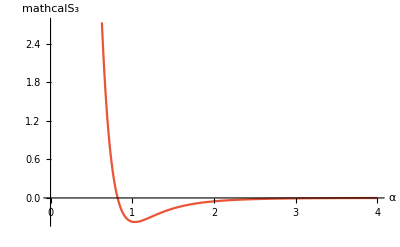

```mathematica
(* Plot of Subscript[S, 3] vs. α. *)

Delete[numericalAlpha,1];
Delete[Subscript[numericalS, 3],1];

ListPlot[Transpose[{numericalAlpha,Subscript[numericalS, 3]}],Joined->True,AxesLabel-> {α,Subscript[mathcalS, 3]}]
```

```mathematica
(** Explicit expression of Subscript[S, 3] in terms of α and kcol, where kcol solves the collision condition Ω[k,1] = Ω[k+p,-1]. kcol is an implicit function of α. **)

Subscript[S, 3,v3]=Simplify[Expand[Subscript[S, 3,v2] //. n -> kcol - Subscript[μ, 0]]] //. Subscript[Q, 3,3] ->   (1+8 Subscript[c, 0]^2 Subscript[N, 2,2]+16 Subscript[c, 0]^6 Subscript[N, 2,2]+Subscript[c, 0]^4 (-1+16 Subscript[N, 3,3]))/(2*3*8 Subscript[c, 0]^5)//. Subscript[Q, 3,1] ->  (3+Subscript[c, 0]^4-8 Subscript[c, 0]^3 Subscript[c, 2]+8 Subscript[c, 0]^2 (1-2 Subscript[c, 0]^4) Subscript[N, 2,2])/(2*8 Subscript[c, 0]^5)//. Subscript[N, 3,3] ->  -((Sinh[3 α]+Subscript[c, 0]^2 (3 Cosh[3 α] (1-2 Subscript[c, 0]^4+16 Subscript[c, 0]^2 Subscript[N, 2,2])+8 Sinh[3 α] (Subscript[c, 0]^2+Subscript[N, 2,2]-7 Subscript[c, 0]^4 Subscript[N, 2,2])))/(16 Subscript[c, 0]^4 (Sinh[3 α]-3 Cosh[3 α] Subscript[c, 0]^2)))//. Subscript[Q, 2,2] -> (1+Subscript[c, 0]^4+8 Subscript[c, 0]^2 Subscript[N, 2,2])/(16 Subscript[c, 0]^3)//. 
Subscript[Q, 2,0] -> -(-1+Subscript[c, 0]^4)/(4 Subscript[c, 0]^3)//.
Subscript[c, 2] ->  (3 Sinh[α]+4 Subscript[c, 0]^4 (Sinh[α]+4 Cosh[α] Subscript[N, 2,2])+Subscript[c, 0]^2 (3 Cosh[α]+8 Sinh[α] Subscript[N, 2,2])-2 Subscript[c, 0]^6 (Cosh[α]+12 Sinh[α] Subscript[N, 2,2]))/(8 Subscript[c, 0]^3 (Sinh[α]+Cosh[α] Subscript[c, 0]^2))//.Subscript[N, 2,2] -> (4 Subscript[c, 0]^2+Tanh[2 α]-3 Subscript[c, 0]^4 Tanh[2 α])/(16 Subscript[c, 0]^4-8 Subscript[c, 0]^2 Tanh[2 α]) //.   Subscript[Q, 1,1] -> 1/(2*Subscript[c, 0]) /. Subscript[ω, j_]:> ω[Subscript[μ, 0]+j] //. Subscript[c, 0] -> Sqrt[Tanh[α]]
```

(6 Sign[kcol] √(kcol Tanh[kcol α]) (2 kcol (6+13 kcol+9 kcol^2+2 kcol^3) Sign[kcol]^2 Tanh[kcol α]+kcol (1+kcol) (10+9 kcol+2 kcol^2) Sign[1+kcol]^2 Tanh[(1+kcol) α]+(2+kcol) (3+10 kcol+9 kcol^2+2 kcol^3) Sign[2+kcol]^2 Tanh[(2+kcol) α])+18 Sign[kcol] Tanh[α]^5 √(kcol Tanh[kcol α]) (2+24 kcol+8 kcol^2+(18 Coth[α]^2 (Sinh[3 α]+Tanh[α] (3 Cosh[3 α] (1-2 Tanh[α]^2+(16 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α]))+8 Sinh[3 α] (Tanh[α]+(4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α])/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])-(7 Tanh[α]^2 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])))))/(Sinh[3 α]-3 Cosh[3 α] Tanh[α])+(112 (2+kcol) Sign[2+kcol]^2 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]) Tanh[(2+kcol) α])/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])-7 (1+kcol) Sign[1+kcol]^2 Tanh[(1+kcol) α] (-(16 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])+3 (2+kcol) Sign[2+kcol]^2 Tanh[(2+kcol) α]))-6 √Tanh[α] (2 kcol^3 Sign[kcol]^6 Tanh[kcol α]^3-kcol (2+kcol) ((1+kcol) (18+10 kcol+kcol^2) Sign[1+kcol]^2 Tanh[(1+kcol) α]+(2+kcol) (3+4 kcol+kcol^2) Sign[2+kcol]^2 Tanh[(2+kcol) α])+kcol^2 Sign[kcol]^4 Tanh[kcol α]^2 ((1+kcol) (10+12 kcol+3 kcol^2) Sign[1+kcol]^2 Tanh[(1+kcol) α]+(2+kcol) (1+6 kcol+3 kcol^2) Sign[2+kcol]^2 Tanh[(2+kcol) α])-2 kcol Sign[kcol]^2 Tanh[kcol α] (36+102 kcol+100 kcol^2+39 kcol^3+5 kcol^4-(1+kcol) (2+kcol) (5+9 kcol+3 kcol^2) Sign[1+kcol]^2 Sign[2+kcol]^2 Tanh[(1+kcol) α] Tanh[(2+kcol) α]))+12 Tanh[α]^(9/2) ((3 (4-3 kcol) Sign[kcol] (1+Tanh[α]^2+(8 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])) √(kcol Tanh[kcol α]))/(2 Tanh[α]^(3/2))+3 kcol (-(12 (6+5 kcol) (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])+7 (1+kcol) (2+kcol) Sign[2+kcol]^2 Tanh[(2+kcol) α])+kcol Sign[kcol]^2 Tanh[kcol α] (1+111 kcol+37 kcol^2+(99 Coth[α]^2 (Sinh[3 α]+Tanh[α] (3 Cosh[3 α] (1-2 Tanh[α]^2+(16 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α]))+8 Sinh[3 α] (Tanh[α]+(4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α])/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])-(7 Tanh[α]^2 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])))))/(Sinh[3 α]-3 Cosh[3 α] Tanh[α])+(596 (2+kcol) Sign[2+kcol]^2 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]) Tanh[(2+kcol) α])/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])+(1+kcol) Sign[1+kcol]^2 Tanh[(1+kcol) α] ((488 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])-96 (2+kcol) Sign[2+kcol]^2 Tanh[(2+kcol) α])))+3 Tanh[α]^4 (-(kcol (-98+45 kcol) Sign[kcol]^2 (1+Tanh[α]^2+(8 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])) Tanh[kcol α])/Tanh[α]^(3/2)+48 kcol (1/(4 Tanh[α]^(5/2))(1+(8 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])+(16 Tanh[α]^3 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])+Tanh[α]^2 (-1-(Coth[α]^2 (Sinh[3 α]+Tanh[α] (3 Cosh[3 α] (1-2 Tanh[α]^2+(16 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α]))+8 Sinh[3 α] (Tanh[α]+(4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α])/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])-(7 Tanh[α]^2 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])))))/(Sinh[3 α]-3 Cosh[3 α] Tanh[α])))-(7 (2+kcol) Sign[2+kcol]^2 (1+Tanh[α]^2+(8 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])) Tanh[(2+kcol) α])/(16 Tanh[α]^(3/2)))+Sign[kcol]^3 (kcol Tanh[kcol α])^(3/2) (27+642 kcol+214 kcol^2+(591 Coth[α]^2 (Sinh[3 α]+Tanh[α] (3 Cosh[3 α] (1-2 Tanh[α]^2+(16 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α]))+8 Sinh[3 α] (Tanh[α]+(4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α])/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])-(7 Tanh[α]^2 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])))))/(Sinh[3 α]-3 Cosh[3 α] Tanh[α])+(3528 (2+kcol) Sign[2+kcol]^2 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]) Tanh[(2+kcol) α])/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])+(1+kcol) Sign[1+kcol]^2 Tanh[(1+kcol) α] ((2952 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])-606 (2+kcol) Sign[2+kcol]^2 Tanh[(2+kcol) α]))+Sign[kcol] √(kcol Tanh[kcol α]) (-(24 (28+150 kcol+91 kcol^2) (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])+(2+kcol) Sign[2+kcol]^2 (39+346 kcol+244 kcol^2-(27 Coth[α]^2 (Sinh[3 α]+Tanh[α] (3 Cosh[3 α] (1-2 Tanh[α]^2+(16 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α]))+8 Sinh[3 α] (Tanh[α]+(4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α])/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])-(7 Tanh[α]^2 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])))))/(Sinh[3 α]-3 Cosh[3 α] Tanh[α])) Tanh[(2+kcol) α]+4 (1+kcol) Sign[1+kcol]^2 Tanh[(1+kcol) α] (33+16 kcol+2 kcol^2-(27 Coth[α]^2 (Sinh[3 α]+Tanh[α] (3 Cosh[3 α] (1-2 Tanh[α]^2+(16 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α]))+8 Sinh[3 α] (Tanh[α]+(4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α])/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])-(7 Tanh[α]^2 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])))))/(Sinh[3 α]-3 Cosh[3 α] Tanh[α])-(210 (2+kcol) Sign[2+kcol]^2 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]) Tanh[(2+kcol) α])/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α]))))-2 Tanh[α]^(7/2) ((3 (-147+40 kcol) Sign[kcol]^3 (1+Tanh[α]^2+(8 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])) (kcol Tanh[kcol α])^(3/2))/(2 Tanh[α]^(3/2))-24 Sign[kcol] √(kcol Tanh[kcol α]) (1/(4 Tanh[α]^(5/2))(3+11 kcol) (1+(8 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])+(16 Tanh[α]^3 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])+Tanh[α]^2 (-1-(Coth[α]^2 (Sinh[3 α]+Tanh[α] (3 Cosh[3 α] (1-2 Tanh[α]^2+(16 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α]))+8 Sinh[3 α] (Tanh[α]+(4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α])/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])-(7 Tanh[α]^2 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])))))/(Sinh[3 α]-3 Cosh[3 α] Tanh[α])))+((-24+kcol) (1+kcol) Sign[1+kcol]^2 (1+Tanh[α]^2+(8 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])) Tanh[(1+kcol) α])/(8 Tanh[α]^(3/2))-((2+kcol) (27+70 kcol) Sign[2+kcol]^2 (1+Tanh[α]^2+(8 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])) Tanh[(2+kcol) α])/(16 Tanh[α]^(3/2)))+kcol (324+720 kcol+456 kcol^2+82 kcol^3+(18 Coth[α]^2 (Sinh[3 α]+Tanh[α] (3 Cosh[3 α] (1-2 Tanh[α]^2+(16 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α]))+8 Sinh[3 α] (Tanh[α]+(4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α])/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])-(7 Tanh[α]^2 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])))))/(Sinh[3 α]-3 Cosh[3 α] Tanh[α])+(6 kcol Coth[α]^2 (Sinh[3 α]+Tanh[α] (3 Cosh[3 α] (1-2 Tanh[α]^2+(16 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α]))+8 Sinh[3 α] (Tanh[α]+(4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α])/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])-(7 Tanh[α]^2 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])))))/(Sinh[3 α]-3 Cosh[3 α] Tanh[α])-(72 (2+kcol) (1+2 kcol) Sign[2+kcol]^2 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]) Tanh[(2+kcol) α])/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])-9 (1+kcol) Sign[1+kcol]^2 Tanh[(1+kcol) α] ((8 (-10+kcol) (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])+7 (2+kcol) (4+kcol) Sign[2+kcol]^2 Tanh[(2+kcol) α]))-6 kcol Sign[kcol]^2 Tanh[kcol α] (-(4 (86+357 kcol+167 kcol^2) (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])+(2+kcol) Sign[2+kcol]^2 (1+124 kcol+72 kcol^2-(18 Coth[α]^2 (Sinh[3 α]+Tanh[α] (3 Cosh[3 α] (1-2 Tanh[α]^2+(16 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α]))+8 Sinh[3 α] (Tanh[α]+(4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α])/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])-(7 Tanh[α]^2 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])))))/(Sinh[3 α]-3 Cosh[3 α] Tanh[α])) Tanh[(2+kcol) α]+(1+kcol) Sign[1+kcol]^2 Tanh[(1+kcol) α] (61+47 kcol+9 kcol^2-(45 Coth[α]^2 (Sinh[3 α]+Tanh[α] (3 Cosh[3 α] (1-2 Tanh[α]^2+(16 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α]))+8 Sinh[3 α] (Tanh[α]+(4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α])/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])-(7 Tanh[α]^2 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])))))/(Sinh[3 α]-3 Cosh[3 α] Tanh[α])-(340 (2+kcol) Sign[2+kcol]^2 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]) Tanh[(2+kcol) α])/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])))-kcol^2 Sign[kcol]^4 Tanh[kcol α]^2 ((1+kcol) Sign[1+kcol]^2 Tanh[(1+kcol) α] ((4032 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])-867 (2+kcol) Sign[2+kcol]^2 Tanh[(2+kcol) α])+2 (81+438 kcol+146 kcol^2+(354 Coth[α]^2 (Sinh[3 α]+Tanh[α] (3 Cosh[3 α] (1-2 Tanh[α]^2+(16 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α]))+8 Sinh[3 α] (Tanh[α]+(4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α])/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])-(7 Tanh[α]^2 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])))))/(Sinh[3 α]-3 Cosh[3 α] Tanh[α])+(2196 (2+kcol) Sign[2+kcol]^2 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]) Tanh[(2+kcol) α])/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α]))))-3 Tanh[α] (-(2 kcol^2 (7+9 kcol+3 kcol^2) Sign[kcol]^4 (1+Tanh[α]^2+(8 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])) Tanh[kcol α]^2)/Tanh[α]^(3/2)+1/Tanh[α]^(3/2)2 kcol (1+kcol) (2+kcol) (3+kcol) Sign[1+kcol]^2 Sign[2+kcol]^2 (1+Tanh[α]^2+(8 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])) Tanh[(1+kcol) α] Tanh[(2+kcol) α]+1/Tanh[α]^(3/2)2 kcol Sign[kcol]^2 (1+Tanh[α]^2+(8 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])) Tanh[kcol α] ((1+kcol) (5+4 kcol+kcol^2) Sign[1+kcol]^2 Tanh[(1+kcol) α]+(2+kcol) (2+2 kcol+kcol^2) Sign[2+kcol]^2 Tanh[(2+kcol) α])+Sign[kcol]^5 (kcol Tanh[kcol α])^(5/2) (33+16 kcol+18 kcol^2+4 kcol^3+(8 (2+kcol) (5+2 kcol) Sign[2+kcol]^2 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]) Tanh[(2+kcol) α])/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])-2 (1+kcol) Sign[1+kcol]^2 Tanh[(1+kcol) α] (-(4 (1+2 kcol) (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])+(2+kcol) (9+6 kcol) Sign[2+kcol]^2 Tanh[(2+kcol) α]))+Sign[kcol]^3 (kcol Tanh[kcol α])^(3/2) (-(8 (3+20 kcol+18 kcol^2+4 kcol^3) (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])+(2+kcol) (21+112 kcol+72 kcol^2+8 kcol^3) Sign[2+kcol]^2 Tanh[(2+kcol) α]+(1+kcol) Sign[1+kcol]^2 Tanh[(1+kcol) α] (123+184 kcol+72 kcol^2+8 kcol^3-(16 (2+kcol) (3+2 kcol) Sign[2+kcol]^2 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]) Tanh[(2+kcol) α])/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])))+Sign[kcol] √(kcol Tanh[kcol α]) ((1+kcol) Sign[1+kcol]^2 Tanh[(1+kcol) α] ((8 kcol (10+9 kcol+2 kcol^2) (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])+(2+kcol) (51+120 kcol+54 kcol^2+4 kcol^3) Sign[2+kcol]^2 Tanh[(2+kcol) α])-2 (1+kcol) (96+310 kcol+245 kcol^2+69 kcol^3+6 kcol^4-(4 (2+kcol) (3+7 kcol+2 kcol^2) Sign[2+kcol]^2 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]) Tanh[(2+kcol) α])/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α]))))+3 Tanh[α]^3 (-(3 kcol^2 (-34+5 kcol) Sign[kcol]^4 (1+Tanh[α]^2+(8 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])) Tanh[kcol α]^2)/Tanh[α]^(3/2)-48 kcol Sign[kcol]^2 Tanh[kcol α] (-1/(16 Tanh[α]^(5/2))3 (4+7 kcol) (1+(8 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])+(16 Tanh[α]^3 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])+Tanh[α]^2 (-1-(Coth[α]^2 (Sinh[3 α]+Tanh[α] (3 Cosh[3 α] (1-2 Tanh[α]^2+(16 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α]))+8 Sinh[3 α] (Tanh[α]+(4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α])/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])-(7 Tanh[α]^2 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])))))/(Sinh[3 α]-3 Cosh[3 α] Tanh[α])))+(5 (1+kcol) (6+kcol) Sign[1+kcol]^2 (1+Tanh[α]^2+(8 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])) Tanh[(1+kcol) α])/(16 Tanh[α]^(3/2))+((2+kcol) (24+31 kcol) Sign[2+kcol]^2 (1+Tanh[α]^2+(8 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])) Tanh[(2+kcol) α])/(16 Tanh[α]^(3/2)))+Sign[kcol]^5 (kcol Tanh[kcol α])^(5/2) (117+342 kcol+114 kcol^2+(225 Coth[α]^2 (Sinh[3 α]+Tanh[α] (3 Cosh[3 α] (1-2 Tanh[α]^2+(16 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α]))+8 Sinh[3 α] (Tanh[α]+(4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α])/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])-(7 Tanh[α]^2 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])))))/(Sinh[3 α]-3 Cosh[3 α] Tanh[α])+(1528 (2+kcol) Sign[2+kcol]^2 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]) Tanh[(2+kcol) α])/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])+(1+kcol) Sign[1+kcol]^2 Tanh[(1+kcol) α] ((1496 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])-342 (2+kcol) Sign[2+kcol]^2 Tanh[(2+kcol) α]))+Sign[kcol]^3 (kcol Tanh[kcol α])^(3/2) (-(8 (93+554 kcol+216 kcol^2) (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])+(2+kcol) Sign[2+kcol]^2 (-99+334 kcol+184 kcol^2-(69 Coth[α]^2 (Sinh[3 α]+Tanh[α] (3 Cosh[3 α] (1-2 Tanh[α]^2+(16 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α]))+8 Sinh[3 α] (Tanh[α]+(4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α])/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])-(7 Tanh[α]^2 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])))))/(Sinh[3 α]-3 Cosh[3 α] Tanh[α])) Tanh[(2+kcol) α]+(1+kcol) Sign[1+kcol]^2 Tanh[(1+kcol) α] (213+238 kcol+48 kcol^2-(123 Coth[α]^2 (Sinh[3 α]+Tanh[α] (3 Cosh[3 α] (1-2 Tanh[α]^2+(16 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α]))+8 Sinh[3 α] (Tanh[α]+(4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α])/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])-(7 Tanh[α]^2 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])))))/(Sinh[3 α]-3 Cosh[3 α] Tanh[α])-(1152 (2+kcol) Sign[2+kcol]^2 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]) Tanh[(2+kcol) α])/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])))+Sign[kcol] √(kcol Tanh[kcol α]) (-2 (90+426 kcol+621 kcol^2+304 kcol^3+43 kcol^4+(6 kcol (3+kcol) Coth[α]^2 (Sinh[3 α]+Tanh[α] (3 Cosh[3 α] (1-2 Tanh[α]^2+(16 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α]))+8 Sinh[3 α] (Tanh[α]+(4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α])/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])-(7 Tanh[α]^2 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])))))/(Sinh[3 α]-3 Cosh[3 α] Tanh[α])-(4 (2+kcol) (-15+12 kcol+17 kcol^2) Sign[2+kcol]^2 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]) Tanh[(2+kcol) α])/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α]))+(1+kcol) Sign[1+kcol]^2 Tanh[(1+kcol) α] ((8 (-12-102 kcol+13 kcol^2) (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])+(2+kcol) Sign[2+kcol]^2 (231+442 kcol+66 kcol^2+(27 Coth[α]^2 (Sinh[3 α]+Tanh[α] (3 Cosh[3 α] (1-2 Tanh[α]^2+(16 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α]))+8 Sinh[3 α] (Tanh[α]+(4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α])/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])-(7 Tanh[α]^2 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])))))/(Sinh[3 α]-3 Cosh[3 α] Tanh[α])) Tanh[(2+kcol) α]))+16 kcol (-1/(16 Tanh[α]^(5/2))3 (1+(8 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])+(16 Tanh[α]^3 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])+Tanh[α]^2 (-1-(Coth[α]^2 (Sinh[3 α]+Tanh[α] (3 Cosh[3 α] (1-2 Tanh[α]^2+(16 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α]))+8 Sinh[3 α] (Tanh[α]+(4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α])/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])-(7 Tanh[α]^2 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])))))/(Sinh[3 α]-3 Cosh[3 α] Tanh[α]))) (4 (1+kcol) Sign[1+kcol]^2 Tanh[(1+kcol) α]+(2+kcol) Sign[2+kcol]^2 Tanh[(2+kcol) α])+1/(16 Tanh[α]^(3/2))(1+Tanh[α]^2+(8 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])) (60+68 kcol+18 kcol^2+21 (1+kcol) (2+kcol) Sign[1+kcol]^2 Sign[2+kcol]^2 Tanh[(1+kcol) α] Tanh[(2+kcol) α])))+Tanh[α]^(3/2) (-48 Sign[kcol]^5 (kcol Tanh[kcol α])^(5/2) (-1/(16 Tanh[α]^(5/2))(3+2 kcol) (1+(8 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])+(16 Tanh[α]^3 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])+Tanh[α]^2 (-1-(Coth[α]^2 (Sinh[3 α]+Tanh[α] (3 Cosh[3 α] (1-2 Tanh[α]^2+(16 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α]))+8 Sinh[3 α] (Tanh[α]+(4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α])/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])-(7 Tanh[α]^2 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])))))/(Sinh[3 α]-3 Cosh[3 α] Tanh[α])))+((1+kcol) (2+kcol) Sign[1+kcol]^2 (1+Tanh[α]^2+(8 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])) Tanh[(1+kcol) α])/(8 Tanh[α]^(3/2))+((1+kcol) (2+kcol) Sign[2+kcol]^2 (1+Tanh[α]^2+(8 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])) Tanh[(2+kcol) α])/(8 Tanh[α]^(3/2)))+kcol^4 Sign[kcol]^8 Tanh[kcol α]^4 (3+6 kcol+2 kcol^2+(3 Coth[α]^2 (Sinh[3 α]+Tanh[α] (3 Cosh[3 α] (1-2 Tanh[α]^2+(16 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α]))+8 Sinh[3 α] (Tanh[α]+(4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α])/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])-(7 Tanh[α]^2 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])))))/(Sinh[3 α]-3 Cosh[3 α] Tanh[α])+(24 (2+kcol) Sign[2+kcol]^2 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]) Tanh[(2+kcol) α])/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])-6 (1+kcol) Sign[1+kcol]^2 Tanh[(1+kcol) α] (-(4 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])+(2+kcol) Sign[2+kcol]^2 Tanh[(2+kcol) α]))+kcol^3 Sign[kcol]^6 Tanh[kcol α]^3 (-(24 (-1+6 kcol+2 kcol^2) (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])+(2+kcol) Sign[2+kcol]^2 (-9+6 kcol+4 kcol^2-(3 Coth[α]^2 (Sinh[3 α]+Tanh[α] (3 Cosh[3 α] (1-2 Tanh[α]^2+(16 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α]))+8 Sinh[3 α] (Tanh[α]+(4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α])/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])-(7 Tanh[α]^2 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])))))/(Sinh[3 α]-3 Cosh[3 α] Tanh[α])) Tanh[(2+kcol) α]+(1+kcol) Sign[1+kcol]^2 Tanh[(1+kcol) α] (9+18 kcol+4 kcol^2-(3 Coth[α]^2 (Sinh[3 α]+Tanh[α] (3 Cosh[3 α] (1-2 Tanh[α]^2+(16 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α]))+8 Sinh[3 α] (Tanh[α]+(4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α])/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])-(7 Tanh[α]^2 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])))))/(Sinh[3 α]-3 Cosh[3 α] Tanh[α])-(48 (2+kcol) Sign[2+kcol]^2 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]) Tanh[(2+kcol) α])/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])))-kcol Sign[kcol]^2 Tanh[kcol α] (-(24 (12+102 kcol+103 kcol^2+30 kcol^3+2 kcol^4) (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])+(2+kcol) Sign[2+kcol]^2 (294+1164 kcol+903 kcol^2+174 kcol^3+4 kcol^4-(3 kcol (3+kcol) Coth[α]^2 (Sinh[3 α]+Tanh[α] (3 Cosh[3 α] (1-2 Tanh[α]^2+(16 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α]))+8 Sinh[3 α] (Tanh[α]+(4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α])/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])-(7 Tanh[α]^2 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])))))/(Sinh[3 α]-3 Cosh[3 α] Tanh[α])) Tanh[(2+kcol) α]+(1+kcol) Sign[1+kcol]^2 Tanh[(1+kcol) α] (636+1068 kcol+525 kcol^2+90 kcol^3+4 kcol^4-(3 kcol (3+kcol) Coth[α]^2 (Sinh[3 α]+Tanh[α] (3 Cosh[3 α] (1-2 Tanh[α]^2+(16 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α]))+8 Sinh[3 α] (Tanh[α]+(4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α])/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])-(7 Tanh[α]^2 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])))))/(Sinh[3 α]-3 Cosh[3 α] Tanh[α])-(48 (2+kcol) (14+12 kcol+kcol^2) Sign[2+kcol]^2 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]) Tanh[(2+kcol) α])/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])))-kcol^2 Sign[kcol]^4 Tanh[kcol α]^2 (246+324 kcol+465 kcol^2+138 kcol^3+8 kcol^4+(9 kcol Coth[α]^2 (Sinh[3 α]+Tanh[α] (3 Cosh[3 α] (1-2 Tanh[α]^2+(16 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α]))+8 Sinh[3 α] (Tanh[α]+(4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α])/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])-(7 Tanh[α]^2 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])))))/(Sinh[3 α]-3 Cosh[3 α] Tanh[α])+(3 kcol^2 Coth[α]^2 (Sinh[3 α]+Tanh[α] (3 Cosh[3 α] (1-2 Tanh[α]^2+(16 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α]))+8 Sinh[3 α] (Tanh[α]+(4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α])/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])-(7 Tanh[α]^2 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])))))/(Sinh[3 α]-3 Cosh[3 α] Tanh[α])+(24 (2+kcol) (29+10 kcol) Sign[2+kcol]^2 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]) Tanh[(2+kcol) α])/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])+(1+kcol) Sign[1+kcol]^2 Tanh[(1+kcol) α] ((48 (7+10 kcol) (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])-(2+kcol) Sign[2+kcol]^2 (369+294 kcol+8 kcol^2+(3 Coth[α]^2 (Sinh[3 α]+Tanh[α] (3 Cosh[3 α] (1-2 Tanh[α]^2+(16 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α]))+8 Sinh[3 α] (Tanh[α]+(4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α])/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])-(7 Tanh[α]^2 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])))))/(Sinh[3 α]-3 Cosh[3 α] Tanh[α])) Tanh[(2+kcol) α]))+kcol (6 (2+3 kcol+kcol^2) (78+64 kcol+15 kcol^2+kcol^3-(4 (2+kcol) (3+kcol) Sign[2+kcol]^2 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]) Tanh[(2+kcol) α])/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α]))-(1+kcol) Sign[1+kcol]^2 Tanh[(1+kcol) α] ((24 (36+38 kcol+12 kcol^2+kcol^3) (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])+(2+kcol) Sign[2+kcol]^2 (288+177 kcol+30 kcol^2+2 kcol^3+(3 (3+kcol) Coth[α]^2 (Sinh[3 α]+Tanh[α] (3 Cosh[3 α] (1-2 Tanh[α]^2+(16 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α]))+8 Sinh[3 α] (Tanh[α]+(4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α])/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])-(7 Tanh[α]^2 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])))))/(Sinh[3 α]-3 Cosh[3 α] Tanh[α])) Tanh[(2+kcol) α]))-48 Sign[kcol] √(kcol Tanh[kcol α]) (1/(8 Tanh[α]^(3/2))(2+kcol) (3+6 kcol+6 kcol^2+kcol^3) Sign[2+kcol]^2 (1+Tanh[α]^2+(8 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])) Tanh[(2+kcol) α]+(1+kcol) Sign[1+kcol]^2 Tanh[(1+kcol) α] (((18+21 kcol+9 kcol^2+kcol^3) (1+Tanh[α]^2+(8 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])))/(8 Tanh[α]^(3/2))-1/(16 Tanh[α]^(5/2))(2+kcol) (3+2 kcol) Sign[2+kcol]^2 (1+(8 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])+(16 Tanh[α]^3 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])+Tanh[α]^2 (-1-(Coth[α]^2 (Sinh[3 α]+Tanh[α] (3 Cosh[3 α] (1-2 Tanh[α]^2+(16 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α]))+8 Sinh[3 α] (Tanh[α]+(4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α])/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])-(7 Tanh[α]^2 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])))))/(Sinh[3 α]-3 Cosh[3 α] Tanh[α]))) Tanh[(2+kcol) α]))+48 Sign[kcol]^3 (kcol Tanh[kcol α])^(3/2) (-1/(16 Tanh[α]^(5/2))(3+2 kcol) (1+(8 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])+(16 Tanh[α]^3 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])+Tanh[α]^2 (-1-(Coth[α]^2 (Sinh[3 α]+Tanh[α] (3 Cosh[3 α] (1-2 Tanh[α]^2+(16 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α]))+8 Sinh[3 α] (Tanh[α]+(4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α])/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])-(7 Tanh[α]^2 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])))))/(Sinh[3 α]-3 Cosh[3 α] Tanh[α]))) ((1+kcol) Sign[1+kcol]^2 Tanh[(1+kcol) α]+(2+kcol) Sign[2+kcol]^2 Tanh[(2+kcol) α])+1/(8 Tanh[α]^(3/2))(1+Tanh[α]^2+(8 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])) (39+61 kcol+27 kcol^2+2 kcol^3+(1+kcol) (2+kcol) (3+2 kcol) Sign[1+kcol]^2 Sign[2+kcol]^2 Tanh[(1+kcol) α] Tanh[(2+kcol) α])))+Tanh[α]^2 ((12 kcol^3 Sign[kcol]^6 (1+Tanh[α]^2+(8 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])) Tanh[kcol α]^3)/Tanh[α]^(3/2)-48 kcol^2 Sign[kcol]^4 Tanh[kcol α]^2 (-1/(16 Tanh[α]^(5/2))3 (6+5 kcol) (1+(8 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])+(16 Tanh[α]^3 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])+Tanh[α]^2 (-1-(Coth[α]^2 (Sinh[3 α]+Tanh[α] (3 Cosh[3 α] (1-2 Tanh[α]^2+(16 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α]))+8 Sinh[3 α] (Tanh[α]+(4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α])/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])-(7 Tanh[α]^2 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])))))/(Sinh[3 α]-3 Cosh[3 α] Tanh[α])))+((1+kcol) (13+6 kcol) Sign[1+kcol]^2 (1+Tanh[α]^2+(8 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])) Tanh[(1+kcol) α])/(8 Tanh[α]^(3/2))+((2+kcol) (10+9 kcol) Sign[2+kcol]^2 (1+Tanh[α]^2+(8 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])) Tanh[(2+kcol) α])/(8 Tanh[α]^(3/2)))+12 Sign[kcol]^7 (kcol Tanh[kcol α])^(7/2) (3+6 kcol+2 kcol^2+(3 Coth[α]^2 (Sinh[3 α]+Tanh[α] (3 Cosh[3 α] (1-2 Tanh[α]^2+(16 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α]))+8 Sinh[3 α] (Tanh[α]+(4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α])/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])-(7 Tanh[α]^2 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])))))/(Sinh[3 α]-3 Cosh[3 α] Tanh[α])+(24 (2+kcol) Sign[2+kcol]^2 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]) Tanh[(2+kcol) α])/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])-6 (1+kcol) Sign[1+kcol]^2 Tanh[(1+kcol) α] (-(4 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])+(2+kcol) Sign[2+kcol]^2 Tanh[(2+kcol) α]))-Sign[kcol] √(kcol Tanh[kcol α]) (-(24 (12+146 kcol+165 kcol^2+58 kcol^3+6 kcol^4) (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])+(2+kcol) Sign[2+kcol]^2 (297+1512 kcol+1536 kcol^2+420 kcol^3+20 kcol^4-(6 kcol (3+kcol) Coth[α]^2 (Sinh[3 α]+Tanh[α] (3 Cosh[3 α] (1-2 Tanh[α]^2+(16 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α]))+8 Sinh[3 α] (Tanh[α]+(4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α])/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])-(7 Tanh[α]^2 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])))))/(Sinh[3 α]-3 Cosh[3 α] Tanh[α])) Tanh[(2+kcol) α]+2 (1+kcol) Sign[1+kcol]^2 Tanh[(1+kcol) α] (234+378 kcol+213 kcol^2+36 kcol^3+2 kcol^4-(6 kcol (3+kcol) Coth[α]^2 (Sinh[3 α]+Tanh[α] (3 Cosh[3 α] (1-2 Tanh[α]^2+(16 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α]))+8 Sinh[3 α] (Tanh[α]+(4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α])/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])-(7 Tanh[α]^2 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])))))/(Sinh[3 α]-3 Cosh[3 α] Tanh[α])-(36 (2+kcol) (13+14 kcol+2 kcol^2) Sign[2+kcol]^2 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]) Tanh[(2+kcol) α])/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])))+2 Sign[kcol]^5 (kcol Tanh[kcol α])^(5/2) ((1+kcol) Sign[1+kcol]^2 Tanh[(1+kcol) α] (33+66 kcol+14 kcol^2-(15 Coth[α]^2 (Sinh[3 α]+Tanh[α] (3 Cosh[3 α] (1-2 Tanh[α]^2+(16 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α]))+8 Sinh[3 α] (Tanh[α]+(4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α])/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])-(7 Tanh[α]^2 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])))))/(Sinh[3 α]-3 Cosh[3 α] Tanh[α])-(216 (2+kcol) Sign[2+kcol]^2 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]) Tanh[(2+kcol) α])/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α]))+2 (-(12 (-6+26 kcol+9 kcol^2) (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])+(2+kcol) Sign[2+kcol]^2 (-21+18 kcol+11 kcol^2-(6 Coth[α]^2 (Sinh[3 α]+Tanh[α] (3 Cosh[3 α] (1-2 Tanh[α]^2+(16 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α]))+8 Sinh[3 α] (Tanh[α]+(4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α])/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])-(7 Tanh[α]^2 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])))))/(Sinh[3 α]-3 Cosh[3 α] Tanh[α])) Tanh[(2+kcol) α]))-3 Sign[kcol]^3 (kcol Tanh[kcol α])^(3/2) (117+380 kcol+552 kcol^2+192 kcol^3+16 kcol^4+(18 kcol Coth[α]^2 (Sinh[3 α]+Tanh[α] (3 Cosh[3 α] (1-2 Tanh[α]^2+(16 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α]))+8 Sinh[3 α] (Tanh[α]+(4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α])/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])-(7 Tanh[α]^2 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])))))/(Sinh[3 α]-3 Cosh[3 α] Tanh[α])+(6 kcol^2 Coth[α]^2 (Sinh[3 α]+Tanh[α] (3 Cosh[3 α] (1-2 Tanh[α]^2+(16 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α]))+8 Sinh[3 α] (Tanh[α]+(4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α])/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])-(7 Tanh[α]^2 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])))))/(Sinh[3 α]-3 Cosh[3 α] Tanh[α])+(24 (2+kcol) (23+6 kcol) Sign[2+kcol]^2 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]) Tanh[(2+kcol) α])/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])-4 (1+kcol) Sign[1+kcol]^2 Tanh[(1+kcol) α] (-(6 (21+26 kcol) (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])+(2+kcol) Sign[2+kcol]^2 (81+78 kcol+4 kcol^2+(3 Coth[α]^2 (Sinh[3 α]+Tanh[α] (3 Cosh[3 α] (1-2 Tanh[α]^2+(16 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α]))+8 Sinh[3 α] (Tanh[α]+(4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α])/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])-(7 Tanh[α]^2 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])))))/(2 (Sinh[3 α]-3 Cosh[3 α] Tanh[α]))) Tanh[(2+kcol) α]))-48 kcol (((2+kcol) (3+6 kcol+2 kcol^2) Sign[2+kcol]^2 (1+Tanh[α]^2+(8 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])) Tanh[(2+kcol) α])/(8 Tanh[α]^(3/2))+(1+kcol) Sign[1+kcol]^2 Tanh[(1+kcol) α] (((6+6 kcol+kcol^2) (1+Tanh[α]^2+(8 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])))/(8 Tanh[α]^(3/2))-1/(16 Tanh[α]^(5/2))3 (2+kcol) Sign[2+kcol]^2 (1+(8 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])+(16 Tanh[α]^3 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])+Tanh[α]^2 (-1-(Coth[α]^2 (Sinh[3 α]+Tanh[α] (3 Cosh[3 α] (1-2 Tanh[α]^2+(16 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α]))+8 Sinh[3 α] (Tanh[α]+(4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α])/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])-(7 Tanh[α]^2 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])))))/(Sinh[3 α]-3 Cosh[3 α] Tanh[α]))) Tanh[(2+kcol) α]))+48 kcol Sign[kcol]^2 Tanh[kcol α] (-1/(16 Tanh[α]^(5/2))(1+(8 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])+(16 Tanh[α]^3 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])+Tanh[α]^2 (-1-(Coth[α]^2 (Sinh[3 α]+Tanh[α] (3 Cosh[3 α] (1-2 Tanh[α]^2+(16 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α]))+8 Sinh[3 α] (Tanh[α]+(4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α])/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])-(7 Tanh[α]^2 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])))))/(Sinh[3 α]-3 Cosh[3 α] Tanh[α]))) ((1+kcol) (12+11 kcol) Sign[1+kcol]^2 Tanh[(1+kcol) α]+(2+kcol) (6+7 kcol) Sign[2+kcol]^2 Tanh[(2+kcol) α])+1/(8 Tanh[α]^(3/2))(1+Tanh[α]^2+(8 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])) (61+126 kcol+72 kcol^2+9 kcol^3+(1+kcol) (2+kcol) (11+9 kcol) Sign[1+kcol]^2 Sign[2+kcol]^2 Tanh[(1+kcol) α] Tanh[(2+kcol) α])))+Tanh[α]^(5/2) (-(3 (-33+2 kcol) Sign[kcol]^5 (1+Tanh[α]^2+(8 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])) (kcol Tanh[kcol α])^(5/2))/Tanh[α]^(3/2)-144 Sign[kcol]^3 (kcol Tanh[kcol α])^(3/2) (-1/(48 Tanh[α]^(5/2))(39+44 kcol) (1+(8 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])+(16 Tanh[α]^3 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])+Tanh[α]^2 (-1-(Coth[α]^2 (Sinh[3 α]+Tanh[α] (3 Cosh[3 α] (1-2 Tanh[α]^2+(16 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α]))+8 Sinh[3 α] (Tanh[α]+(4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α])/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])-(7 Tanh[α]^2 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])))))/(Sinh[3 α]-3 Cosh[3 α] Tanh[α])))+((1+kcol) (23+8 kcol) Sign[1+kcol]^2 (1+Tanh[α]^2+(8 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])) Tanh[(1+kcol) α])/(16 Tanh[α]^(3/2))+((2+kcol) (21+20 kcol) Sign[2+kcol]^2 (1+Tanh[α]^2+(8 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])) Tanh[(2+kcol) α])/(16 Tanh[α]^(3/2)))+kcol^3 Sign[kcol]^6 Tanh[kcol α]^3 (165+366 kcol+122 kcol^2+(201 Coth[α]^2 (Sinh[3 α]+Tanh[α] (3 Cosh[3 α] (1-2 Tanh[α]^2+(16 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α]))+8 Sinh[3 α] (Tanh[α]+(4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α])/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])-(7 Tanh[α]^2 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])))))/(Sinh[3 α]-3 Cosh[3 α] Tanh[α])+(1512 (2+kcol) Sign[2+kcol]^2 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]) Tanh[(2+kcol) α])/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])-6 (1+kcol) Sign[1+kcol]^2 Tanh[(1+kcol) α] (-(252 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])+61 (2+kcol) Sign[2+kcol]^2 Tanh[(2+kcol) α]))+kcol^2 Sign[kcol]^4 Tanh[kcol α]^2 (-(72 (-2+76 kcol+27 kcol^2) (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])+(2+kcol) Sign[2+kcol]^2 (-267+366 kcol+208 kcol^2-(93 Coth[α]^2 (Sinh[3 α]+Tanh[α] (3 Cosh[3 α] (1-2 Tanh[α]^2+(16 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α]))+8 Sinh[3 α] (Tanh[α]+(4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α])/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])-(7 Tanh[α]^2 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])))))/(Sinh[3 α]-3 Cosh[3 α] Tanh[α])) Tanh[(2+kcol) α]+2 (1+kcol) Sign[1+kcol]^2 Tanh[(1+kcol) α] (141+216 kcol+44 kcol^2-(69 Coth[α]^2 (Sinh[3 α]+Tanh[α] (3 Cosh[3 α] (1-2 Tanh[α]^2+(16 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α]))+8 Sinh[3 α] (Tanh[α]+(4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α])/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])-(7 Tanh[α]^2 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])))))/(Sinh[3 α]-3 Cosh[3 α] Tanh[α])-(828 (2+kcol) Sign[2+kcol]^2 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]) Tanh[(2+kcol) α])/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])))-kcol (-(24 (60+82 kcol+36 kcol^2+5 kcol^3) (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])+(2+kcol) Sign[2+kcol]^2 (576+879 kcol+342 kcol^2+28 kcol^3-(3 (3+kcol) Coth[α]^2 (Sinh[3 α]+Tanh[α] (3 Cosh[3 α] (1-2 Tanh[α]^2+(16 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α]))+8 Sinh[3 α] (Tanh[α]+(4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α])/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])-(7 Tanh[α]^2 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])))))/(Sinh[3 α]-3 Cosh[3 α] Tanh[α])) Tanh[(2+kcol) α]+4 (1+kcol) Sign[1+kcol]^2 Tanh[(1+kcol) α] (54+60 kcol+12 kcol^2+kcol^3-(3 (3+kcol) Coth[α]^2 (Sinh[3 α]+Tanh[α] (3 Cosh[3 α] (1-2 Tanh[α]^2+(16 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α]))+8 Sinh[3 α] (Tanh[α]+(4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α])/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])-(7 Tanh[α]^2 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])))))/(Sinh[3 α]-3 Cosh[3 α] Tanh[α])-(54 (2+kcol) (4+kcol) Sign[2+kcol]^2 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]) Tanh[(2+kcol) α])/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])))-kcol Sign[kcol]^2 Tanh[kcol α] (684+2700 kcol+3555 kcol^2+1434 kcol^3+158 kcol^4+(117 kcol Coth[α]^2 (Sinh[3 α]+Tanh[α] (3 Cosh[3 α] (1-2 Tanh[α]^2+(16 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α]))+8 Sinh[3 α] (Tanh[α]+(4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α])/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])-(7 Tanh[α]^2 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])))))/(Sinh[3 α]-3 Cosh[3 α] Tanh[α])+(39 kcol^2 Coth[α]^2 (Sinh[3 α]+Tanh[α] (3 Cosh[3 α] (1-2 Tanh[α]^2+(16 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α]))+8 Sinh[3 α] (Tanh[α]+(4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α])/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])-(7 Tanh[α]^2 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])))))/(Sinh[3 α]-3 Cosh[3 α] Tanh[α])-(24 (2+kcol) (-60-4 kcol+5 kcol^2) Sign[2+kcol]^2 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]) Tanh[(2+kcol) α])/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])-6 (1+kcol) Sign[1+kcol]^2 Tanh[(1+kcol) α] ((4 (-84-128 kcol+5 kcol^2) (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])+(2+kcol) Sign[2+kcol]^2 (207+258 kcol+23 kcol^2+(9 Coth[α]^2 (Sinh[3 α]+Tanh[α] (3 Cosh[3 α] (1-2 Tanh[α]^2+(16 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α]))+8 Sinh[3 α] (Tanh[α]+(4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α])/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])-(7 Tanh[α]^2 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])))))/(Sinh[3 α]-3 Cosh[3 α] Tanh[α])) Tanh[(2+kcol) α]))+48 Sign[kcol] √(kcol Tanh[kcol α]) (-1/(16 Tanh[α]^(5/2))(1+(8 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])+(16 Tanh[α]^3 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])+Tanh[α]^2 (-1-(Coth[α]^2 (Sinh[3 α]+Tanh[α] (3 Cosh[3 α] (1-2 Tanh[α]^2+(16 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α]))+8 Sinh[3 α] (Tanh[α]+(4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α])/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])-(7 Tanh[α]^2 (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])))))/(Sinh[3 α]-3 Cosh[3 α] Tanh[α]))) (4 (1+kcol) (3+5 kcol) Sign[1+kcol]^2 Tanh[(1+kcol) α]+(2+kcol) (3+8 kcol) Sign[2+kcol]^2 Tanh[(2+kcol) α])+1/(16 Tanh[α]^(3/2))(1+Tanh[α]^2+(8 Tanh[α] (4 Tanh[α]+Tanh[2 α]-3 Tanh[α]^2 Tanh[2 α]))/(16 Tanh[α]^2-8 Tanh[α] Tanh[2 α])) (6 (10+35 kcol+27 kcol^2+5 kcol^3)+(1+kcol) (2+kcol) (33+32 kcol) Sign[1+kcol]^2 Sign[2+kcol]^2 Tanh[(1+kcol) α] Tanh[(2+kcol) α]))))/(48 Tanh[α]^(3/2) (√Tanh[α]+Sign[kcol] √(kcol Tanh[kcol α])-Sign[1+kcol] √((1+kcol) Tanh[(1+kcol) α])) (√Tanh[α]+Sign[kcol] √(kcol Tanh[kcol α])+Sign[1+kcol] √((1+kcol) Tanh[(1+kcol) α])) (2 √Tanh[α]+Sign[kcol] √(kcol Tanh[kcol α])-Sign[2+kcol] √((2+kcol) Tanh[(2+kcol) α])) (2 √Tanh[α]+Sign[kcol] √(kcol Tanh[kcol α])+Sign[2+kcol] √((2+kcol) Tanh[(2+kcol) α])))

```mathematica
(** Remove hyperbolic sinh from inhomogeneous terms. **)

Subscript[partIHT, 3]= Subscript[IHT, 3][[All,{1,2,3,5,6,8,9,10}]]/. Subscript[s, j_]:> Subscript[ω, j]^2*Subscript[C, j]/((Subscript[μ, 0]+j)) //. {Subscript[h, 2,-2+n] -> Subscript[tildeh, 2,-2+n],Subscript[ϕ, 2,-2+n] -> ⅈ*Subscript[tildeϕ, 2,-2+n]} //. {Subscript[h, 2,n] -> Subscript[tildeh, 2,n],Subscript[ϕ, 2,n]-> ⅈ*Subscript[tildeϕ, 2,n]} //. {Subscript[h, 2,n+1] -> Subscript[γ, 0]*Subscript[Γ, h,2,n+1,0],Subscript[ϕ, 2,n+1]-> Subscript[γ, 0]*ⅈ*Subscript[Γ, ϕ,2,n+1,0]} //. {Subscript[h, 2,n+2] -> Subscript[tildeh, 2,n+2] + Subscript[γ, 1]*Subscript[Γ, h,2,n+2,1],Subscript[ϕ, 2,n+2] -> ⅈ*Subscript[tildeϕ, 2,n+2] + Subscript[γ, 1]*ⅈ*Subscript[Γ, ϕ,2,n+2,1]} //. {Subscript[h, 2,n+3] -> Subscript[γ, 0]*Subscript[Γ, h,2,n+3,0] , Subscript[ϕ, 2,n+3] -> Subscript[γ, 0]*ⅈ*Subscript[Γ, ϕ,2,n+3,0]} //. {Subscript[h, 2,n+4] -> Subscript[γ, 1]*Subscript[Γ, h,2,n+4,1],Subscript[ϕ, 2,n+4] -> Subscript[γ, 1]*ⅈ*Subscript[Γ, ϕ,2,n+4,1]} //. {Subscript[h, 2,n+5] -> Subscript[γ, 0]*Subscript[Γ, h,2,n+5,0], Subscript[ϕ, 2,n+5]-> Subscript[γ, 0]*ⅈ*Subscript[Γ, ϕ,2,n+5,0]}//.{Subscript[h, 1,-1+n]-> Subscript[tildeh, 1,-1+n],Subscript[ϕ, 1,-1+n]-> ⅈ*(Subscript[tildeϕ, 1,-1+n])} //. {Subscript[h, 1,1+n]-> Subscript[tildeh, 1,1+n] ,Subscript[ϕ, 1,1+n]-> ⅈ*(Subscript[tildeϕ, 1,1+n])} //.{Subscript[h, 1,2+n]-> Subscript[γ, 0]*Subscript[Γ, h,1,2+n,0] ,Subscript[ϕ, 1,2+n]-> ⅈ*( Subscript[γ, 0]*Subscript[Γ, ϕ,1,2+n,0])}//.{Subscript[h, 1,4+n]-> Subscript[γ, 0]*Subscript[Γ, h,1,4+n,0] ,Subscript[ϕ, 1,4+n]-> ⅈ*( Subscript[γ, 0]*Subscript[Γ, ϕ,1,4+n,0])} //. Subscript[λ, 2] -> ⅈ*Subscript[tildeλ, 2];
```

```mathematica
(** Obtain particular solutions for vectors proportional to Exp[ⅈ*k*x], with k =/= n,n+p. **)

(**Subscript[partsoln, 3]=Simplify[partsoln[Subscript[partIHT, 3],GenModulate[{n,n+p},3][[{1,2,3,5,6,8,9,10}]],3]//. {Subscript[h, 2,-2+n] -> Subscript[tildeh, 2,-2+n],Subscript[ϕ, 2,-2+n] -> ⅈ*Subscript[tildeϕ, 2,-2+n]} //. {Subscript[h, 2,n] -> Subscript[tildeh, 2,n],Subscript[ϕ, 2,n]-> ⅈ*Subscript[tildeϕ, 2,n]} //. {Subscript[h, 2,n+1] -> Subscript[γ, 0]*Subscript[Γ, h,2,n+1,0],Subscript[ϕ, 2,n+1]-> Subscript[γ, 0]*ⅈ*Subscript[Γ, ϕ,2,n+1,0]} //. {Subscript[h, 2,n+2] -> Subscript[tildeh, 2,n+2] + Subscript[γ, 1]*Subscript[Γ, h,2,n+2,1],Subscript[ϕ, 2,n+2] -> ⅈ*Subscript[tildeϕ, 2,n+2] + Subscript[γ, 1]*ⅈ*Subscript[Γ, ϕ,2,n+2,1]} //. {Subscript[h, 2,n+3] -> Subscript[γ, 0]*Subscript[Γ, h,2,n+3,0] , Subscript[ϕ, 2,n+3] -> Subscript[γ, 0]*ⅈ*Subscript[Γ, ϕ,2,n+3,0]} //. {Subscript[h, 2,n+4] -> Subscript[γ, 1]*Subscript[Γ, h,2,n+4,1],Subscript[ϕ, 2,n+4] -> Subscript[γ, 1]*ⅈ*Subscript[Γ, ϕ,2,n+4,1]} //. {Subscript[h, 2,n+5] -> Subscript[γ, 0]*Subscript[Γ, h,2,n+5,0], Subscript[ϕ, 2,n+5]-> Subscript[γ, 0]*ⅈ*Subscript[Γ, ϕ,2,n+5,0]}//.{Subscript[h, 1,-1+n]-> Subscript[tildeh, 1,-1+n],Subscript[ϕ, 1,-1+n]-> ⅈ*(Subscript[tildeϕ, 1,-1+n])} //. {Subscript[h, 1,1+n]-> Subscript[tildeh, 1,1+n] ,Subscript[ϕ, 1,1+n]-> ⅈ*(Subscript[tildeϕ, 1,1+n])} //.{Subscript[h, 1,2+n]-> Subscript[γ, 0]*Subscript[Γ, h,1,2+n,0] ,Subscript[ϕ, 1,2+n]-> ⅈ*( Subscript[γ, 0]*Subscript[Γ, ϕ,1,2+n,0])}//.{Subscript[h, 1,4+n]-> Subscript[γ, 0]*Subscript[Γ, h,1,4+n,0] ,Subscript[ϕ, 1,4+n]-> ⅈ*( Subscript[γ, 0]*Subscript[Γ, ϕ,1,4+n,0])}]
Clear[S];**)

(** Takes a long while to obtain the particular solutions this way. Also, we don't need all of these to get Subscript[λ, 4]. **)
```

```mathematica
(** These are the only relevant particular solutions needed to calculate Subscript[λ, 4]. **)

Subscript[wcoeff, 3,n-1]=Flatten[partsoln[{{placeHolderh},{placeHolderϕ}},{n-1},3] //. {placeHolderh -> Subscript[partIHT, 3][[1,3]], placeHolderϕ -> Subscript[partIHT, 3][[2,3]]}]
Subscript[wcoeff, 3,n+1]=Flatten[partsoln[{{placeHolderh},{placeHolderϕ}},{n+1},3] //. {placeHolderh -> Subscript[partIHT, 3][[1,4]], placeHolderϕ -> Subscript[partIHT, 3][[2,4]]}]
Subscript[wcoeff, 3,n+2]=Flatten[partsoln[{{placeHolderh},{placeHolderϕ}},{n+2},3] //. {placeHolderh -> Subscript[partIHT, 3][[1,5]], placeHolderϕ -> Subscript[partIHT, 3][[2,5]]}]
Subscript[wcoeff, 3,n+4]=Flatten[partsoln[{{placeHolderh},{placeHolderϕ}},{n+4},3] //. {placeHolderh -> Subscript[partIHT, 3][[1,6]], placeHolderϕ -> Subscript[partIHT, 3][[2,6]]}]
```

{h_(3,-1+n)→(ⅈ c_0 (-1/2 ⅈ α c_0 μ_2+1/2 ⅈ n α c_0 μ_2+321)-1+ω_1^2 1)/(c_0^2-ω_1^2-2 c_0 ω_n+ω_n^2),ϕ_(3,1)→-1/(5+ω_n^2)}
 |  |  |  |

{h_(3,1+n)→-(ⅈ (1))/(c_0^2+2 c_0 ω_n+ω_n^2-ω_(1+n)^2),ϕ_(3,1+n)→-((423+1+ⅈ ω_n (1))/(c_0^2+2 c_0 ω_n+ω_n^2-ω_(1+n)^2))}
 |  |  |  |

{h_(3,2+n)→-((ⅈ (2 c_0 (1)+ω_n 1+ⅈ ω_1^2 (9/4 c_0^2 γ_0+112)))/(4 c_0^2+4 c_0 ω_n+ω_n^2-ω_(2+n)^2)),ϕ_(3,2+n)→-1/(4 c_0^2+4)}
 |  |  |  |

{h_(3,4+n)→-((ⅈ (4 c_0 (1)+ω_n (1)+ⅈ ω_1^2 (1)))/(16 c_0^2+8 c_0 ω_n+ω_n^2-ω_(4+n)^2)),ϕ_(3,4+n)→-1/(16 c_0^2+4)}
 |  |  |  |

```mathematica
(** Write these particular solutions as series in γ. **)

Subscript[tildew, 3,n-1] = {Subscript[tildeh, 3,n-1] -> Simplify[{{1,0},{0,1/ⅈ}}.{Subscript[h, 3,n-1],Subscript[ϕ, 3,n-1]}][[1]] //. Subscript[wcoeff, 3,n-1],Subscript[tildeϕ, 3,n-1] -> Simplify[{{1,0},{0,1/ⅈ}}.{Subscript[h, 3,n-1],Subscript[ϕ, 3,n-1]}][[2]] //. Subscript[wcoeff, 3,n-1]}

Subscript[tildew, 3,n+1] = {Subscript[tildeh, 3,n+1] -> Simplify[{{1,0},{0,1/ⅈ}}.{Subscript[h, 3,n+1],Subscript[ϕ, 3,n+1]}][[1]] //. Subscript[wcoeff, 3,n+1] //. Subscript[γ, 1]-> 0,Subscript[tildeϕ, 3,n+1] -> Simplify[{{1,0},{0,1/ⅈ}}.{Subscript[h, 3,n+1],Subscript[ϕ, 3,n+1]}][[2]] //. Subscript[wcoeff, 3,n+1] //. Subscript[γ, 1] -> 0}
Subscript[Γ, 3,n+1,1] = {Subscript[Γ, h,3,n+1,1] -> Coefficient[Simplify[{{1,0},{0,1/ⅈ}}.{Subscript[h, 3,n+1],Subscript[ϕ, 3,n+1]}][[1]] //. Subscript[wcoeff, 3,n+1], Subscript[γ, 1]],Subscript[Γ, ϕ,3,n+1,1] -> Coefficient[Simplify[{{1,0},{0,1/ⅈ}}.{Subscript[h, 3,n+1],Subscript[ϕ, 3,n+1]}][[2]] //. Subscript[wcoeff, 3,n+1], Subscript[γ, 1] ]}

Subscript[Γ, 3,n+2,0] = {Subscript[Γ, h,3,n+2,0] -> Coefficient[Simplify[{{1,0},{0,1/ⅈ}}.{Subscript[h, 3,n+2],Subscript[ϕ, 3,n+2]}][[1]] //. Subscript[wcoeff, 3,n+2], Subscript[γ, 0]],Subscript[Γ, ϕ,3,n+2,0] -> Coefficient[Simplify[{{1,0},{0,1/ⅈ}}.{Subscript[h, 3,n+2],Subscript[ϕ, 3,n+2]}][[2]] //. Subscript[wcoeff, 3,n+2], Subscript[γ, 0] ]}
Subscript[Γ, 3,n+2,2] = {Subscript[Γ, h,3,n+2,2] -> Coefficient[Simplify[{{1,0},{0,1/ⅈ}}.{Subscript[h, 3,n+2],Subscript[ϕ, 3,n+2]}][[1]] //. Subscript[wcoeff, 3,n+2], Subscript[γ, 2]],Subscript[Γ, ϕ,3,n+2,2] -> Coefficient[Simplify[{{1,0},{0,1/ⅈ}}.{Subscript[h, 3,n+2],Subscript[ϕ, 3,n+2]}][[2]] //. Subscript[wcoeff, 3,n+2], Subscript[γ, 2] ]}

Subscript[Γ, 3,n+4,0] = {Subscript[Γ, h,3,n+4,0] -> Coefficient[Simplify[{{1,0},{0,1/ⅈ}}.{Subscript[h, 3,n+4],Subscript[ϕ, 3,n+4]}][[1]] //. Subscript[wcoeff, 3,n+4], Subscript[γ, 0]],Subscript[Γ, ϕ,3,n+4,0] -> Coefficient[Simplify[{{1,0},{0,1/ⅈ}}.{Subscript[h, 3,n+4],Subscript[ϕ, 3,n+4]}][[2]] //. Subscript[wcoeff, 3,n+4], Subscript[γ, 0] ]}
Subscript[Γ, 3,n+4,2] = {Subscript[Γ, h,3,n+4,2] -> Coefficient[Simplify[{{1,0},{0,1/ⅈ}}.{Subscript[h, 3,n+4],Subscript[ϕ, 3,n+4]}][[1]] //. Subscript[wcoeff, 3,n+4], Subscript[γ, 2]],Subscript[Γ, ϕ,3,n+4,2] -> Coefficient[Simplify[{{1,0},{0,1/ⅈ}}.{Subscript[h, 3,n+4],Subscript[ϕ, 3,n+4]}][[2]] //. Subscript[wcoeff, 3,n+4], Subscript[γ, 2] ]}
```

{tildeh_(3,-1+n)→(ⅈ c_0 (-1/2 ⅈ α c_0 μ_2+322)-ⅈ ω_n (1)+ω_1^2 (1))/(c_0^2-ω_1^2-2 c_0 ω_n+ω_n^2),tildeϕ_(3,-1+n)→(ⅈ (1))/(5+ω_n^2)}
 |  |  |  |

{tildeh_(3,1+n)→-((ⅈ (c_0 (1)+ω_n (1)+ⅈ ω_1^2 (1)))/(c_0^2+2 c_0 ω_n+ω_n^2-ω_(1+n)^2)),tildeϕ_(3,1+n)→(ⅈ (1))/(c_0^2+111-ω_1^2)}
 |  |  |  |

{Γ_(h,3,1+n,1)→-1/(c_0^2+2 c_0 ω_n+ω_n^2-ω_(1+n)^2)ⅈ (-1/8 ⅈ c_0^2-1/4 ⅈ n c_0^2-1/8 ⅈ n^2 c_0^2-1/4 ⅈ c_0^2 μ_0-1/4 ⅈ n c_0^2 μ_0-1/8 ⅈ c_0^2 μ_0^2-1/4 ⅈ c_0 ω_n-1/2 ⅈ n c_0 ω_n-1/4 ⅈ n^2 c_0 ω_n-1/2 ⅈ c_0 μ_0 ω_n-1/2 ⅈ n c_0 μ_0 ω_n-1/4 ⅈ c_0 μ_0^2 ω_n-(ⅈ ω_n^2)/8-1/4 ⅈ n ω_n^2-1/8 ⅈ n^2 ω_n^2-1/4 ⅈ μ_0 ω_n^2-1/4 ⅈ n μ_0 ω_n^2-1/8 ⅈ μ_0^2 ω_n^2+(3 ⅈ c_0 ω_(1+n)^2)/(4 ω_(3+n))+(ⅈ n c_0 ω_(1+n)^2)/(4 ω_(3+n))+(ⅈ c_0 μ_0 ω_(1+n)^2)/(4 ω_(3+n))-(3 ⅈ c_0 ω_(1+n)^2)/(8 (1+n+μ_0) ω_(3+n))-(7 ⅈ n c_0 ω_(1+n)^2)/(8 (1+n+μ_0) ω_(3+n))-(5 ⅈ n^2 c_0 ω_(1+n)^2)/(8 (1+n+μ_0) ω_(3+n))-(ⅈ n^3 c_0 ω_(1+n)^2)/(8 (1+n+μ_0) ω_(3+n))-(7 ⅈ c_0 μ_0 ω_(1+n)^2)/(8 (1+n+μ_0) ω_(3+n))-(5 ⅈ n c_0 μ_0 ω_(1+n)^2)/(4 (1+n+μ_0) ω_(3+n))-(3 ⅈ n^2 c_0 μ_0 ω_(1+n)^2)/(8 (1+n+μ_0) ω_(3+n))-(5 ⅈ c_0 μ_0^2 ω_(1+n)^2)/(8 (1+n+μ_0) ω_(3+n))-(3 ⅈ n c_0 μ_0^2 ω_(1+n)^2)/(8 (1+n+μ_0) ω_(3+n))-(ⅈ c_0 μ_0^3 ω_(1+n)^2)/(8 (1+n+μ_0) ω_(3+n))-(3 ⅈ ω_n ω_(1+n)^2)/(8 (1+n+μ_0) ω_(3+n))-(7 ⅈ n ω_n ω_(1+n)^2)/(8 (1+n+μ_0) ω_(3+n))-(5 ⅈ n^2 ω_n ω_(1+n)^2)/(8 (1+n+μ_0) ω_(3+n))-(ⅈ n^3 ω_n ω_(1+n)^2)/(8 (1+n+μ_0) ω_(3+n))-(7 ⅈ μ_0 ω_n ω_(1+n)^2)/(8 (1+n+μ_0) ω_(3+n))-(5 ⅈ n μ_0 ω_n ω_(1+n)^2)/(4 (1+n+μ_0) ω_(3+n))-(3 ⅈ n^2 μ_0 ω_n ω_(1+n)^2)/(8 (1+n+μ_0) ω_(3+n))-(5 ⅈ μ_0^2 ω_n ω_(1+n)^2)/(8 (1+n+μ_0) ω_(3+n))-(3 ⅈ n μ_0^2 ω_n ω_(1+n)^2)/(8 (1+n+μ_0) ω_(3+n))-(ⅈ μ_0^3 ω_n ω_(1+n)^2)/(8 (1+n+μ_0) ω_(3+n))-6 ⅈ c_0^2 ω_(1+n)^2 N_(2,2)-(ⅈ c_0^2 ω_(1+n)^2 N_(2,2))/(1+n+μ_0)-(ⅈ n c_0^2 ω_(1+n)^2 N_(2,2))/(1+n+μ_0)-(ⅈ c_0^2 μ_0 ω_(1+n)^2 N_(2,2))/(1+n+μ_0)-2 ⅈ c_0 ω_n ω_(1+n)^2 N_(2,2)-(2 ⅈ c_0 ω_n ω_(1+n)^2 N_(2,2))/(1+n+μ_0)-(2 ⅈ n c_0 ω_n ω_(1+n)^2 N_(2,2))/(1+n+μ_0)-(2 ⅈ c_0 μ_0 ω_n ω_(1+n)^2 N_(2,2))/(1+n+μ_0)-(ⅈ ω_n^2 ω_(1+n)^2 N_(2,2))/(1+n+μ_0)-(ⅈ n ω_n^2 ω_(1+n)^2 N_(2,2))/(1+n+μ_0)-(ⅈ μ_0 ω_n^2 ω_(1+n)^2 N_(2,2))/(1+n+μ_0)-(3 ⅈ c_0 N_(2,2))/(ω_(3+n))-(4 ⅈ n c_0 N_(2,2))/(ω_(3+n))-(ⅈ n^2 c_0 N_(2,2))/(ω_(3+n))-(4 ⅈ c_0 μ_0 N_(2,2))/(ω_(3+n))-(2 ⅈ n c_0 μ_0 N_(2,2))/(ω_(3+n))-(ⅈ c_0 μ_0^2 N_(2,2))/(ω_(3+n))-(3 ⅈ ω_n N_(2,2))/(ω_(3+n))-(4 ⅈ n ω_n N_(2,2))/(ω_(3+n))-(ⅈ n^2 ω_n N_(2,2))/(ω_(3+n))-(4 ⅈ μ_0 ω_n N_(2,2))/(ω_(3+n))-(2 ⅈ n μ_0 ω_n N_(2,2))/(ω_(3+n))-(ⅈ μ_0^2 ω_n N_(2,2))/(ω_(3+n))+3 ⅈ c_0 ω_(1+n)^2 Q_(1,1)+1/2 ⅈ n c_0 ω_(1+n)^2 Q_(1,1)+1/2 ⅈ c_0 μ_0 ω_(1+n)^2 Q_(1,1)+(ⅈ c_0 ω_(1+n)^2 Q_(1,1))/(2 (1+n+μ_0))+(ⅈ n c_0 ω_(1+n)^2 Q_(1,1))/(1+n+μ_0)+(ⅈ n^2 c_0 ω_(1+n)^2 Q_(1,1))/(2 (1+n+μ_0))+(ⅈ c_0 μ_0 ω_(1+n)^2 Q_(1,1))/(1+n+μ_0)+(ⅈ n c_0 μ_0 ω_(1+n)^2 Q_(1,1))/(1+n+μ_0)+(ⅈ c_0 μ_0^2 ω_(1+n)^2 Q_(1,1))/(2 (1+n+μ_0))+1/2 ⅈ ω_n ω_(1+n)^2 Q_(1,1)+(ⅈ ω_n ω_(1+n)^2 Q_(1,1))/(2 (1+n+μ_0))+(ⅈ n ω_n ω_(1+n)^2 Q_(1,1))/(1+n+μ_0)+(ⅈ n^2 ω_n ω_(1+n)^2 Q_(1,1))/(2 (1+n+μ_0))+(ⅈ μ_0 ω_n ω_(1+n)^2 Q_(1,1))/(1+n+μ_0)+(ⅈ n μ_0 ω_n ω_(1+n)^2 Q_(1,1))/(1+n+μ_0)+(ⅈ μ_0^2 ω_n ω_(1+n)^2 Q_(1,1))/(2 (1+n+μ_0))+2 ⅈ c_0 Q_(2,2)+2 ⅈ n c_0 Q_(2,2)+2 ⅈ c_0 μ_0 Q_(2,2)+2 ⅈ ω_n Q_(2,2)+2 ⅈ n ω_n Q_(2,2)+2 ⅈ μ_0 ω_n Q_(2,2)-(6 ⅈ ω_(1+n)^2 Q_(2,2))/(ω_(3+n))-(2 ⅈ n ω_(1+n)^2 Q_(2,2))/(ω_(3+n))-(2 ⅈ μ_0 ω_(1+n)^2 Q_(2,2))/(ω_(3+n))-ⅈ c_0^2 ω_(1+n)^2 Γ_(h,2,2+n,1)-(ⅈ c_0^2 ω_(1+n)^2 Γ_(h,2,2+n,1))/(2 (1+n+μ_0))-(ⅈ n c_0^2 ω_(1+n)^2 Γ_(h,2,2+n,1))/(2 (1+n+μ_0))-(ⅈ c_0^2 μ_0 ω_(1+n)^2 Γ_(h,2,2+n,1))/(2 (1+n+μ_0))-1/2 ⅈ c_0 ω_n ω_(1+n)^2 Γ_(h,2,2+n,1)-(ⅈ c_0 ω_n ω_(1+n)^2 Γ_(h,2,2+n,1))/(1+n+μ_0)-(ⅈ n c_0 ω_n ω_(1+n)^2 Γ_(h,2,2+n,1))/(1+n+μ_0)-(ⅈ c_0 μ_0 ω_n ω_(1+n)^2 Γ_(h,2,2+n,1))/(1+n+μ_0)-(ⅈ ω_n^2 ω_(1+n)^2 Γ_(h,2,2+n,1))/(2 (1+n+μ_0))-(ⅈ n ω_n^2 ω_(1+n)^2 Γ_(h,2,2+n,1))/(2 (1+n+μ_0))-(ⅈ μ_0 ω_n^2 ω_(1+n)^2 Γ_(h,2,2+n,1))/(2 (1+n+μ_0))+ⅈ c_0 Q_(1,1) Γ_(h,2,2+n,1)+ⅈ n c_0 Q_(1,1) Γ_(h,2,2+n,1)+ⅈ c_0 μ_0 Q_(1,1) Γ_(h,2,2+n,1)+ⅈ ω_n Q_(1,1) Γ_(h,2,2+n,1)+ⅈ n ω_n Q_(1,1) Γ_(h,2,2+n,1)+ⅈ μ_0 ω_n Q_(1,1) Γ_(h,2,2+n,1)-ⅈ c_0 Γ_(ϕ,2,2+n,1)-3/2 ⅈ n c_0 Γ_(ϕ,2,2+n,1)-1/2 ⅈ n^2 c_0 Γ_(ϕ,2,2+n,1)-3/2 ⅈ c_0 μ_0 Γ_(ϕ,2,2+n,1)-ⅈ n c_0 μ_0 Γ_(ϕ,2,2+n,1)-1/2 ⅈ c_0 μ_0^2 Γ_(ϕ,2,2+n,1)-ⅈ ω_n Γ_(ϕ,2,2+n,1)-3/2 ⅈ n ω_n Γ_(ϕ,2,2+n,1)-1/2 ⅈ n^2 ω_n Γ_(ϕ,2,2+n,1)-3/2 ⅈ μ_0 ω_n Γ_(ϕ,2,2+n,1)-ⅈ n μ_0 ω_n Γ_(ϕ,2,2+n,1)-1/2 ⅈ μ_0^2 ω_n Γ_(ϕ,2,2+n,1)-2 ⅈ ω_(1+n)^2 Q_(1,1) Γ_(ϕ,2,2+n,1)-ⅈ n ω_(1+n)^2 Q_(1,1) Γ_(ϕ,2,2+n,1)-ⅈ μ_0 ω_(1+n)^2 Q_(1,1) Γ_(ϕ,2,2+n,1)),Γ_(ϕ,3,1+n,1)→1/(c_0^2+2 c_0 ω_n+ω_n^2-ω_(1+n)^2)ⅈ (-(ⅈ c_0)/8-1/4 ⅈ n c_0-1/8 ⅈ n^2 c_0-1/4 ⅈ c_0 μ_0-1/4 ⅈ n c_0 μ_0-1/8 ⅈ c_0 μ_0^2-(ⅈ ω_n)/8-1/4 ⅈ n ω_n-1/8 ⅈ n^2 ω_n-1/4 ⅈ μ_0 ω_n-1/4 ⅈ n μ_0 ω_n-1/8 ⅈ μ_0^2 ω_n+(3 ⅈ c_0^2)/(4 ω_(3+n))+(ⅈ n c_0^2)/(4 ω_(3+n))+(ⅈ c_0^2 μ_0)/(4 ω_(3+n))+(3 ⅈ c_0 ω_n)/(4 ω_(3+n))+(ⅈ n c_0 ω_n)/(4 ω_(3+n))+(ⅈ c_0 μ_0 ω_n)/(4 ω_(3+n))-(3 ⅈ ω_(1+n)^2)/(8 (1+n+μ_0) ω_(3+n))-(7 ⅈ n ω_(1+n)^2)/(8 (1+n+μ_0) ω_(3+n))-(5 ⅈ n^2 ω_(1+n)^2)/(8 (1+n+μ_0) ω_(3+n))-(ⅈ n^3 ω_(1+n)^2)/(8 (1+n+μ_0) ω_(3+n))-(7 ⅈ μ_0 ω_(1+n)^2)/(8 (1+n+μ_0) ω_(3+n))-(5 ⅈ n μ_0 ω_(1+n)^2)/(4 (1+n+μ_0) ω_(3+n))-(3 ⅈ n^2 μ_0 ω_(1+n)^2)/(8 (1+n+μ_0) ω_(3+n))-(5 ⅈ μ_0^2 ω_(1+n)^2)/(8 (1+n+μ_0) ω_(3+n))-(3 ⅈ n μ_0^2 ω_(1+n)^2)/(8 (1+n+μ_0) ω_(3+n))-(ⅈ μ_0^3 ω_(1+n)^2)/(8 (1+n+μ_0) ω_(3+n))-6 ⅈ c_0^3 N_(2,2)-8 ⅈ c_0^2 ω_n N_(2,2)-2 ⅈ c_0 ω_n^2 N_(2,2)-(ⅈ c_0 ω_(1+n)^2 N_(2,2))/(1+n+μ_0)-(ⅈ n c_0 ω_(1+n)^2 N_(2,2))/(1+n+μ_0)-(ⅈ c_0 μ_0 ω_(1+n)^2 N_(2,2))/(1+n+μ_0)-(ⅈ ω_n ω_(1+n)^2 N_(2,2))/(1+n+μ_0)-(ⅈ n ω_n ω_(1+n)^2 N_(2,2))/(1+n+μ_0)-(ⅈ μ_0 ω_n ω_(1+n)^2 N_(2,2))/(1+n+μ_0)-(3 ⅈ N_(2,2))/(ω_(3+n))-(4 ⅈ n N_(2,2))/(ω_(3+n))-(ⅈ n^2 N_(2,2))/(ω_(3+n))-(4 ⅈ μ_0 N_(2,2))/(ω_(3+n))-(2 ⅈ n μ_0 N_(2,2))/(ω_(3+n))-(ⅈ μ_0^2 N_(2,2))/(ω_(3+n))+3 ⅈ c_0^2 Q_(1,1)+1/2 ⅈ n c_0^2 Q_(1,1)+1/2 ⅈ c_0^2 μ_0 Q_(1,1)+7/2 ⅈ c_0 ω_n Q_(1,1)+1/2 ⅈ n c_0 ω_n Q_(1,1)+1/2 ⅈ c_0 μ_0 ω_n Q_(1,1)+1/2 ⅈ ω_n^2 Q_(1,1)+(ⅈ ω_(1+n)^2 Q_(1,1))/(2 (1+n+μ_0))+(ⅈ n ω_(1+n)^2 Q_(1,1))/(1+n+μ_0)+(ⅈ n^2 ω_(1+n)^2 Q_(1,1))/(2 (1+n+μ_0))+(ⅈ μ_0 ω_(1+n)^2 Q_(1,1))/(1+n+μ_0)+(ⅈ n μ_0 ω_(1+n)^2 Q_(1,1))/(1+n+μ_0)+(ⅈ μ_0^2 ω_(1+n)^2 Q_(1,1))/(2 (1+n+μ_0))+2 ⅈ Q_(2,2)+2 ⅈ n Q_(2,2)+2 ⅈ μ_0 Q_(2,2)-(6 ⅈ c_0 Q_(2,2))/(ω_(3+n))-(2 ⅈ n c_0 Q_(2,2))/(ω_(3+n))-(2 ⅈ c_0 μ_0 Q_(2,2))/(ω_(3+n))-(6 ⅈ ω_n Q_(2,2))/(ω_(3+n))-(2 ⅈ n ω_n Q_(2,2))/(ω_(3+n))-(2 ⅈ μ_0 ω_n Q_(2,2))/(ω_(3+n))-ⅈ c_0^3 Γ_(h,2,2+n,1)-3/2 ⅈ c_0^2 ω_n Γ_(h,2,2+n,1)-1/2 ⅈ c_0 ω_n^2 Γ_(h,2,2+n,1)-(ⅈ c_0 ω_(1+n)^2 Γ_(h,2,2+n,1))/(2 (1+n+μ_0))-(ⅈ n c_0 ω_(1+n)^2 Γ_(h,2,2+n,1))/(2 (1+n+μ_0))-(ⅈ c_0 μ_0 ω_(1+n)^2 Γ_(h,2,2+n,1))/(2 (1+n+μ_0))-(ⅈ ω_n ω_(1+n)^2 Γ_(h,2,2+n,1))/(2 (1+n+μ_0))-(ⅈ n ω_n ω_(1+n)^2 Γ_(h,2,2+n,1))/(2 (1+n+μ_0))-(ⅈ μ_0 ω_n ω_(1+n)^2 Γ_(h,2,2+n,1))/(2 (1+n+μ_0))+ⅈ Q_(1,1) Γ_(h,2,2+n,1)+ⅈ n Q_(1,1) Γ_(h,2,2+n,1)+ⅈ μ_0 Q_(1,1) Γ_(h,2,2+n,1)-ⅈ Γ_(ϕ,2,2+n,1)-3/2 ⅈ n Γ_(ϕ,2,2+n,1)-1/2 ⅈ n^2 Γ_(ϕ,2,2+n,1)-3/2 ⅈ μ_0 Γ_(ϕ,2,2+n,1)-ⅈ n μ_0 Γ_(ϕ,2,2+n,1)-1/2 ⅈ μ_0^2 Γ_(ϕ,2,2+n,1)-2 ⅈ c_0 Q_(1,1) Γ_(ϕ,2,2+n,1)-ⅈ n c_0 Q_(1,1) Γ_(ϕ,2,2+n,1)-ⅈ c_0 μ_0 Q_(1,1) Γ_(ϕ,2,2+n,1)-2 ⅈ ω_n Q_(1,1) Γ_(ϕ,2,2+n,1)-ⅈ n ω_n Q_(1,1) Γ_(ϕ,2,2+n,1)-ⅈ μ_0 ω_n Q_(1,1) Γ_(ϕ,2,2+n,1))}

{Γ_(h,3,2+n,0)→-(ⅈ (1))/(4 c_0^2+4 c_0 ω_n+ω_n^2-ω_(2+n)^2),Γ_(ϕ,3,2+n,0)→(ⅈ (1/2+586))/(4 c_0^2+4 c_0 ω_n+ω_n^2-ω_(2+n)^2)}
 |  |  |  |

{Γ_(h,3,2+n,2)→-1/(4 c_0^2+4 c_0 ω_n+ω_n^2-ω_(2+n)^2)ⅈ (-3/2 ⅈ c_0^2 ω_(2+n)^2-(4 ⅈ c_0^2 ω_(2+n)^2)/(2+n+μ_0)-(2 ⅈ n c_0^2 ω_(2+n)^2)/(2+n+μ_0)-(2 ⅈ c_0^2 μ_0 ω_(2+n)^2)/(2+n+μ_0)-1/2 ⅈ c_0 ω_n ω_(2+n)^2-(4 ⅈ c_0 ω_n ω_(2+n)^2)/(2+n+μ_0)-(2 ⅈ n c_0 ω_n ω_(2+n)^2)/(2+n+μ_0)-(2 ⅈ c_0 μ_0 ω_n ω_(2+n)^2)/(2+n+μ_0)-(ⅈ ω_n^2 ω_(2+n)^2)/(2+n+μ_0)-(ⅈ n ω_n^2 ω_(2+n)^2)/(2 (2+n+μ_0))-(ⅈ μ_0 ω_n^2 ω_(2+n)^2)/(2 (2+n+μ_0))-(6 ⅈ c_0)/(ω_(3+n))-(5 ⅈ n c_0)/(ω_(3+n))-(ⅈ n^2 c_0)/(ω_(3+n))-(5 ⅈ c_0 μ_0)/(ω_(3+n))-(2 ⅈ n c_0 μ_0)/(ω_(3+n))-(ⅈ c_0 μ_0^2)/(ω_(3+n))-(3 ⅈ ω_n)/(ω_(3+n))-(5 ⅈ n ω_n)/(2 ω_(3+n))-(ⅈ n^2 ω_n)/(2 ω_(3+n))-(5 ⅈ μ_0 ω_n)/(2 ω_(3+n))-(ⅈ n μ_0 ω_n)/(ω_(3+n))-(ⅈ μ_0^2 ω_n)/(2 ω_(3+n))+4 ⅈ c_0 Q_(1,1)+2 ⅈ n c_0 Q_(1,1)+2 ⅈ c_0 μ_0 Q_(1,1)+2 ⅈ ω_n Q_(1,1)+ⅈ n ω_n Q_(1,1)+ⅈ μ_0 ω_n Q_(1,1)-(3 ⅈ ω_(2+n)^2 Q_(1,1))/(ω_(3+n))-(ⅈ n ω_(2+n)^2 Q_(1,1))/(ω_(3+n))-(ⅈ μ_0 ω_(2+n)^2 Q_(1,1))/(ω_(3+n))),Γ_(ϕ,3,2+n,2)→1/(4 c_0^2+4 c_0 ω_n+ω_n^2-ω_(2+n)^2)ⅈ (-3 ⅈ c_0^3-5/2 ⅈ c_0^2 ω_n-1/2 ⅈ c_0 ω_n^2-(2 ⅈ c_0 ω_(2+n)^2)/(2+n+μ_0)-(ⅈ n c_0 ω_(2+n)^2)/(2+n+μ_0)-(ⅈ c_0 μ_0 ω_(2+n)^2)/(2+n+μ_0)-(ⅈ ω_n ω_(2+n)^2)/(2+n+μ_0)-(ⅈ n ω_n ω_(2+n)^2)/(2 (2+n+μ_0))-(ⅈ μ_0 ω_n ω_(2+n)^2)/(2 (2+n+μ_0))-(3 ⅈ)/(ω_(3+n))-(5 ⅈ n)/(2 ω_(3+n))-(ⅈ n^2)/(2 ω_(3+n))-(5 ⅈ μ_0)/(2 ω_(3+n))-(ⅈ n μ_0)/(ω_(3+n))-(ⅈ μ_0^2)/(2 ω_(3+n))+2 ⅈ Q_(1,1)+ⅈ n Q_(1,1)+ⅈ μ_0 Q_(1,1)-(6 ⅈ c_0 Q_(1,1))/(ω_(3+n))-(2 ⅈ n c_0 Q_(1,1))/(ω_(3+n))-(2 ⅈ c_0 μ_0 Q_(1,1))/(ω_(3+n))-(3 ⅈ ω_n Q_(1,1))/(ω_(3+n))-(ⅈ n ω_n Q_(1,1))/(ω_(3+n))-(ⅈ μ_0 ω_n Q_(1,1))/(ω_(3+n)))}

{Γ_(h,3,4+n,0)→-(ⅈ (1))/(16 c_0^2+8 c_0 ω_n+ω_n^2-ω_(4+n)^2),Γ_(ϕ,3,4+n,0)→(ⅈ (1))/(16 c_0^2+8 c_0 ω_n+ω_n^2-ω_(4+n)^2)}
 |  |  |  |

{Γ_(h,3,4+n,2)→-1/(16 c_0^2+8 c_0 ω_n+ω_n^2-ω_(4+n)^2)ⅈ (-(24 ⅈ c_0)/(ω_(3+n))-(14 ⅈ n c_0)/(ω_(3+n))-(2 ⅈ n^2 c_0)/(ω_(3+n))-(14 ⅈ c_0 μ_0)/(ω_(3+n))-(4 ⅈ n c_0 μ_0)/(ω_(3+n))-(2 ⅈ c_0 μ_0^2)/(ω_(3+n))-(6 ⅈ ω_n)/(ω_(3+n))-(7 ⅈ n ω_n)/(2 ω_(3+n))-(ⅈ n^2 ω_n)/(2 ω_(3+n))-(7 ⅈ μ_0 ω_n)/(2 ω_(3+n))-(ⅈ n μ_0 ω_n)/(ω_(3+n))-(ⅈ μ_0^2 ω_n)/(2 ω_(3+n))+3/2 ⅈ c_0^2 ω_(4+n)^2-(32 ⅈ c_0^2 ω_(4+n)^2)/(4+n+μ_0)-(8 ⅈ n c_0^2 ω_(4+n)^2)/(4+n+μ_0)-(8 ⅈ c_0^2 μ_0 ω_(4+n)^2)/(4+n+μ_0)+1/2 ⅈ c_0 ω_n ω_(4+n)^2-(16 ⅈ c_0 ω_n ω_(4+n)^2)/(4+n+μ_0)-(4 ⅈ n c_0 ω_n ω_(4+n)^2)/(4+n+μ_0)-(4 ⅈ c_0 μ_0 ω_n ω_(4+n)^2)/(4+n+μ_0)-(2 ⅈ ω_n^2 ω_(4+n)^2)/(4+n+μ_0)-(ⅈ n ω_n^2 ω_(4+n)^2)/(2 (4+n+μ_0))-(ⅈ μ_0 ω_n^2 ω_(4+n)^2)/(2 (4+n+μ_0))+16 ⅈ c_0 Q_(1,1)+4 ⅈ n c_0 Q_(1,1)+4 ⅈ c_0 μ_0 Q_(1,1)+4 ⅈ ω_n Q_(1,1)+ⅈ n ω_n Q_(1,1)+ⅈ μ_0 ω_n Q_(1,1)-(3 ⅈ ω_(4+n)^2 Q_(1,1))/(ω_(3+n))-(ⅈ n ω_(4+n)^2 Q_(1,1))/(ω_(3+n))-(ⅈ μ_0 ω_(4+n)^2 Q_(1,1))/(ω_(3+n))),Γ_(ϕ,3,4+n,2)→1/(16 c_0^2+8 c_0 ω_n+ω_n^2-ω_(4+n)^2)ⅈ (6 ⅈ c_0^3+7/2 ⅈ c_0^2 ω_n+1/2 ⅈ c_0 ω_n^2-(6 ⅈ)/(ω_(3+n))-(7 ⅈ n)/(2 ω_(3+n))-(ⅈ n^2)/(2 ω_(3+n))-(7 ⅈ μ_0)/(2 ω_(3+n))-(ⅈ n μ_0)/(ω_(3+n))-(ⅈ μ_0^2)/(2 ω_(3+n))-(8 ⅈ c_0 ω_(4+n)^2)/(4+n+μ_0)-(2 ⅈ n c_0 ω_(4+n)^2)/(4+n+μ_0)-(2 ⅈ c_0 μ_0 ω_(4+n)^2)/(4+n+μ_0)-(2 ⅈ ω_n ω_(4+n)^2)/(4+n+μ_0)-(ⅈ n ω_n ω_(4+n)^2)/(2 (4+n+μ_0))-(ⅈ μ_0 ω_n ω_(4+n)^2)/(2 (4+n+μ_0))+4 ⅈ Q_(1,1)+ⅈ n Q_(1,1)+ⅈ μ_0 Q_(1,1)-(12 ⅈ c_0 Q_(1,1))/(ω_(3+n))-(4 ⅈ n c_0 Q_(1,1))/(ω_(3+n))-(4 ⅈ c_0 μ_0 Q_(1,1))/(ω_(3+n))-(3 ⅈ ω_n Q_(1,1))/(ω_(3+n))-(ⅈ n ω_n Q_(1,1))/(ω_(3+n))-(ⅈ μ_0 ω_n Q_(1,1))/(ω_(3+n)))}

```mathematica
Subscript[w, 3] = Sum[{Subscript[h, 3,j],Subscript[ϕ, 3,j]}*Exp[ⅈ*j*x],{j,GenModulate[{n,n+p},3][[{1,3,4,5,6,7,8,9,10}]]} ]+ Subscript[γ, 3]*{1,1/(-ⅈ*Subscript[ω, n+p])}*Exp[ⅈ*(n+p)*x]//. Subscript[h, 3,n] -> 0 //. Subscript[h, 3,n+p]-> 0
```

{ⅇ^(ⅈ (3+n) x) γ_3+ⅇ^(ⅈ (-3+n) x) h_(3,-3+n)+ⅇ^(ⅈ (-1+n) x) h_(3,-1+n)+ⅇ^(ⅈ (1+n) x) h_(3,1+n)+ⅇ^(ⅈ (2+n) x) h_(3,2+n)+ⅇ^(ⅈ (4+n) x) h_(3,4+n)+ⅇ^(ⅈ (5+n) x) h_(3,5+n)+ⅇ^(ⅈ (6+n) x) h_(3,6+n),(ⅈ ⅇ^(ⅈ (3+n) x) γ_3)/(ω_(3+n))+ⅇ^(ⅈ (-3+n) x) ϕ_(3,-3+n)+ⅇ^(ⅈ (-1+n) x) ϕ_(3,-1+n)+ⅇ^(ⅈ n x) ϕ_(3,n)+ⅇ^(ⅈ (1+n) x) ϕ_(3,1+n)+ⅇ^(ⅈ (2+n) x) ϕ_(3,2+n)+ⅇ^(ⅈ (3+n) x) ϕ_(3,3+n)+ⅇ^(ⅈ (4+n) x) ϕ_(3,4+n)+ⅇ^(ⅈ (5+n) x) ϕ_(3,5+n)+ⅇ^(ⅈ (6+n) x) ϕ_(3,6+n)}

```mathematica
V. Fourth-Order Problem
```

```mathematica
(** Define operator Subscript[L, 4] for numerical computations. **)

Subscript[NumL, 4][w_,k_,η1_,q1_,η2_,q2_,η3_,q3_,η4_,q4_] :=(Clear[integrand];
kmod = GenModulate[k,4];
integrand = NCoefficient[1/24(24 Subscript[c, 4] Subscript[C, κ]*ⅈ*Fdiff[w[[1]],1]+12 Subscript[c, 2](Subscript[C, κ]*(2 ⅈ Subscript[μ, 2])*w[[1]]+2 (Subscript[s, κ] (α Subscript[μ, 1]+(κ+Subscript[μ, 0]) η1))*(ⅈ Subscript[μ, 1])*w[[1]]+(Subscript[C, κ] (α Subscript[μ, 1]+(κ+Subscript[μ, 0]) η1)^2+Subscript[s, κ] (2 α Subscript[μ, 2]+2 Subscript[μ, 1] η1+2 (κ+Subscript[μ, 0]) η2))*ⅈ*Fdiff[w[[1]],1])+Subscript[c, 0](Subscript[C, κ]*(24 ⅈ Subscript[μ, 4])*w[[1]]+2 (Subscript[s, κ] (α Subscript[μ, 1]+(κ+Subscript[μ, 0]) η1))*(6 ⅈ Subscript[μ, 3])*w[[1]]+2 (Subscript[C, κ] (α Subscript[μ, 1]+(κ+Subscript[μ, 0]) η1)^2+Subscript[s, κ] (2 α Subscript[μ, 2]+2 Subscript[μ, 1] η1+2 (κ+Subscript[μ, 0]) η2))*(2 ⅈ Subscript[μ, 2])*w[[1]]+2 (Subscript[s, κ] (α Subscript[μ, 1]+(κ+Subscript[μ, 0]) η1)^3+3 Subscript[C, κ] (α Subscript[μ, 1]+(κ+Subscript[μ, 0]) η1) (2 α Subscript[μ, 2]+2 Subscript[μ, 1] η1+2 (κ+Subscript[μ, 0]) η2)+Subscript[s, κ] (6 α Subscript[μ, 3]+6 Subscript[μ, 2] η1+6 Subscript[μ, 1] η2+6 (κ+Subscript[μ, 0]) η3))*(ⅈ Subscript[μ, 1])*w[[1]]+2 ((Subscript[s, κ] (α Subscript[μ, 1]+(κ+Subscript[μ, 0]) η1))*(6 ⅈ Subscript[μ, 3])*w[[1]]+2 (Subscript[C, κ] (α Subscript[μ, 1]+(κ+Subscript[μ, 0]) η1)^2+Subscript[s, κ] (2 α Subscript[μ, 2]+2 Subscript[μ, 1] η1+2 (κ+Subscript[μ, 0]) η2))*(2 ⅈ Subscript[μ, 2])*w[[1]]+(Subscript[s, κ] (α Subscript[μ, 1]+(κ+Subscript[μ, 0]) η1)^3+3 Subscript[C, κ] (α Subscript[μ, 1]+(κ+Subscript[μ, 0]) η1) (2 α Subscript[μ, 2]+2 Subscript[μ, 1] η1+2 (κ+Subscript[μ, 0]) η2)+Subscript[s, κ] (6 α Subscript[μ, 3]+6 Subscript[μ, 2] η1+6 Subscript[μ, 1] η2+6 (κ+Subscript[μ, 0]) η3))*(ⅈ Subscript[μ, 1])*w[[1]])+(Subscript[C, κ] (α Subscript[μ, 1]+(κ+Subscript[μ, 0]) η1)^4+6 Subscript[s, κ] (α Subscript[μ, 1]+(κ+Subscript[μ, 0]) η1)^2 (2 α Subscript[μ, 2]+2 Subscript[μ, 1] η1+2 (κ+Subscript[μ, 0]) η2)+3 Subscript[C, κ] (2 α Subscript[μ, 2]+2 Subscript[μ, 1] η1+2 (κ+Subscript[μ, 0]) η2)^2+4 Subscript[C, κ] (α Subscript[μ, 1]+(κ+Subscript[μ, 0]) η1) (6 α Subscript[μ, 3]+6 Subscript[μ, 2] η1+6 Subscript[μ, 1] η2+6 (κ+Subscript[μ, 0]) η3)+Subscript[s, κ] (24 α Subscript[μ, 4]+24 Subscript[μ, 3] η1+24 Subscript[μ, 2] η2+24 Subscript[μ, 1] η3+24 (κ+Subscript[μ, 0]) η4))*ⅈ*Fdiff[w[[1]],1])+(24 Subscript[μ, 3] (-ⅈ Subscript[C, κ] D[q1,x]+Subscript[c, 0] Subscript[s, κ] D[η1,x])+12 Subscript[μ, 2] (-2 ⅈ Subscript[s, κ] (α Subscript[μ, 1]+(κ+Subscript[μ, 0]) η1) D[q1,x]-2 ⅈ Subscript[C, κ] D[q2,x]+2 Subscript[c, 0] Subscript[C, κ] (α Subscript[μ, 1]+(κ+Subscript[μ, 0]) η1) D[η1,x]+2 Subscript[c, 0] Subscript[s, κ] D[η2,x])+4 Subscript[μ, 1] (-3 ⅈ (Subscript[C, κ] (α Subscript[μ, 1]+(κ+Subscript[μ, 0]) η1)^2+Subscript[s, κ] (2 α Subscript[μ, 2]+2 Subscript[μ, 1] η1+2 (κ+Subscript[μ, 0]) η2)) D[q1,x]-6 ⅈ Subscript[s, κ] (α Subscript[μ, 1]+(κ+Subscript[μ, 0]) η1) D[q2,x]-6 ⅈ Subscript[C, κ] D[q3,x]+3 (2 Subscript[c, 2] Subscript[s, κ]+Subscript[c, 0](Subscript[s, κ] (α Subscript[μ, 1]+(κ+Subscript[μ, 0]) η1)^2+Subscript[C, κ] (2 α Subscript[μ, 2]+2 Subscript[μ, 1] η1+2 (κ+Subscript[μ, 0]) η2))) D[η1,x]+6 Subscript[c, 0] Subscript[C, κ] (α Subscript[μ, 1]+(κ+Subscript[μ, 0]) η1) D[η2,x]+6 Subscript[c, 0] Subscript[s, κ] D[η3,x])+(κ+Subscript[μ, 0]) (-4 ⅈ (Subscript[s, κ] (α Subscript[μ, 1]+(κ+Subscript[μ, 0]) η1)^3+3 Subscript[C, κ] (α Subscript[μ, 1]+(κ+Subscript[μ, 0]) η1) (2 α Subscript[μ, 2]+2 Subscript[μ, 1] η1+2 (κ+Subscript[μ, 0]) η2)+Subscript[s, κ] (6 α Subscript[μ, 3]+6 Subscript[μ, 2] η1+6 Subscript[μ, 1] η2+6 (κ+Subscript[μ, 0]) η3)) D[q1,x]-12 ⅈ (Subscript[C, κ] (α Subscript[μ, 1]+(κ+Subscript[μ, 0]) η1)^2+Subscript[s, κ] (2 α Subscript[μ, 2]+2 Subscript[μ, 1] η1+2 (κ+Subscript[μ, 0]) η2)) D[q2,x]-24 ⅈ Subscript[s, κ] (α Subscript[μ, 1]+(κ+Subscript[μ, 0]) η1) D[q3,x]-24 ⅈ Subscript[C, κ] D[q4,x]+4 (6 Subscript[c, 2] Subscript[C, κ] (α Subscript[μ, 1]+(κ+Subscript[μ, 0]) η1)+Subscript[c, 0](Subscript[C, κ] (α Subscript[μ, 1]+(κ+Subscript[μ, 0]) η1)^3+3 Subscript[s, κ] (α Subscript[μ, 1]+(κ+Subscript[μ, 0]) η1) (2 α Subscript[μ, 2]+2 Subscript[μ, 1] η1+2 (κ+Subscript[μ, 0]) η2)+Subscript[C, κ] (6 α Subscript[μ, 3]+6 Subscript[μ, 2] η1+6 Subscript[μ, 1] η2+6 (κ+Subscript[μ, 0]) η3))) D[η1,x]+12 (2 Subscript[c, 2] Subscript[s, κ]+Subscript[c, 0](Subscript[s, κ] (α Subscript[μ, 1]+(κ+Subscript[μ, 0]) η1)^2+Subscript[C, κ] (2 α Subscript[μ, 2]+2 Subscript[μ, 1] η1+2 (κ+Subscript[μ, 0]) η2))) D[η2,x]+24 Subscript[c, 0] Subscript[C, κ] (α Subscript[μ, 1]+(κ+Subscript[μ, 0]) η1) D[η3,x]+24 Subscript[c, 0] Subscript[s, κ] D[η4,x]))*w[[1]]) + (-ⅈ/24(Subscript[s, κ]*(24 ⅈ Subscript[μ, 4])*w[[2]]+2 (Subscript[C, κ] (α Subscript[μ, 1]+(κ+Subscript[μ, 0]) η1))*(6 ⅈ Subscript[μ, 3])*w[[2]]+2 (Subscript[s, κ] (α Subscript[μ, 1]+(κ+Subscript[μ, 0]) η1)^2+Subscript[C, κ] (2 α Subscript[μ, 2]+2 Subscript[μ, 1] η1+2 (κ+Subscript[μ, 0]) η2))*(2 ⅈ Subscript[μ, 2])*w[[2]]+2 (Subscript[C, κ] (α Subscript[μ, 1]+(κ+Subscript[μ, 0]) η1)^3+3 Subscript[s, κ] (α Subscript[μ, 1]+(κ+Subscript[μ, 0]) η1) (2 α Subscript[μ, 2]+2 Subscript[μ, 1] η1+2 (κ+Subscript[μ, 0]) η2)+Subscript[C, κ] (6 α Subscript[μ, 3]+6 Subscript[μ, 2] η1+6 Subscript[μ, 1] η2+6 (κ+Subscript[μ, 0]) η3))*(ⅈ Subscript[μ, 1])*w[[2]]+2 ((Subscript[C, κ] (α Subscript[μ, 1]+(κ+Subscript[μ, 0]) η1))*(6 ⅈ Subscript[μ, 3])*w[[2]]+2 (Subscript[s, κ] (α Subscript[μ, 1]+(κ+Subscript[μ, 0]) η1)^2+Subscript[C, κ] (2 α Subscript[μ, 2]+2 Subscript[μ, 1] η1+2 (κ+Subscript[μ, 0]) η2))*(2 ⅈ Subscript[μ, 2])*w[[2]]+(Subscript[C, κ] (α Subscript[μ, 1]+(κ+Subscript[μ, 0]) η1)^3+3 Subscript[s, κ] (α Subscript[μ, 1]+(κ+Subscript[μ, 0]) η1) (2 α Subscript[μ, 2]+2 Subscript[μ, 1] η1+2 (κ+Subscript[μ, 0]) η2)+Subscript[C, κ] (6 α Subscript[μ, 3]+6 Subscript[μ, 2] η1+6 Subscript[μ, 1] η2+6 (κ+Subscript[μ, 0]) η3))*(ⅈ Subscript[μ, 1])*w[[2]])+(Subscript[s, κ] (α Subscript[μ, 1]+(κ+Subscript[μ, 0]) η1)^4+6 Subscript[C, κ] (α Subscript[μ, 1]+(κ+Subscript[μ, 0]) η1)^2 (2 α Subscript[μ, 2]+2 Subscript[μ, 1] η1+2 (κ+Subscript[μ, 0]) η2)+3 Subscript[s, κ] (2 α Subscript[μ, 2]+2 Subscript[μ, 1] η1+2 (κ+Subscript[μ, 0]) η2)^2+4 Subscript[s, κ] (α Subscript[μ, 1]+(κ+Subscript[μ, 0]) η1) (6 α Subscript[μ, 3]+6 Subscript[μ, 2] η1+6 Subscript[μ, 1] η2+6 (κ+Subscript[μ, 0]) η3)+Subscript[C, κ] (24 α Subscript[μ, 4]+24 Subscript[μ, 3] η1+24 Subscript[μ, 2] η2+24 Subscript[μ, 1] η3+24 (κ+Subscript[μ, 0]) η4))*ⅈ*Fdiff[w[[2]],1])),kmod];
{Sum[Exp[ⅈ*kmod[[j]]*x]*(integrand[[j]] //. κ -> kmod[[j]]),{j,1,Length[kmod]}],1/24 (2 D[η1,x]*Subscript[c, 0]^2*(6 ⅈ Subscript[μ, 3])*w[[1]]+2 D[η1,x]*(-2 Subscript[c, 0] D[q1,x])*(2 ⅈ Subscript[μ, 2])*w[[1]]+2 D[η1,x]*(2 D[q1,x]^2-2 Subscript[c, 0](-2 Subscript[c, 2]+2 D[q2,x])-4 Subscript[c, 0]^2 D[η1,x]^2)*(ⅈ Subscript[μ, 1])*w[[1]]+2 D[η1,x]*(6 D[q1,x] (-2 Subscript[c, 2]+2 D[q2,x])-12 Subscript[c, 0] D[q3,x]+24 Subscript[c, 0] D[q1,x] D[η1,x]^2-24 Subscript[c, 0]^2 D[η1,x] D[η2,x])*ⅈ*Fdiff[w[[1]],1]+2 (2 D[η2,x])*Subscript[c, 0]^2*(2 ⅈ Subscript[μ, 2])*w[[1]]+2 (2 D[η2,x])*(-2 Subscript[c, 0] D[q1,x])*(ⅈ Subscript[μ, 1])*w[[1]]+2 (2 D[η1,x]*(-2 Subscript[c, 0] D[q1,x])*(2 ⅈ Subscript[μ, 2])*w[[1]]+2 D[η1,x]*(2 D[q1,x]^2-2 Subscript[c, 0](-2 Subscript[c, 2]+2 D[q2,x])-4 Subscript[c, 0]^2 D[η1,x]^2)*(ⅈ Subscript[μ, 1])*w[[1]]+(2 D[η2,x])*(-2 Subscript[c, 0] D[q1,x])*(ⅈ Subscript[μ, 1])*w[[1]])+2 (2 D[η2,x])*(2 D[q1,x]^2-2 Subscript[c, 0](-2 Subscript[c, 2]+2 D[q2,x])-4 Subscript[c, 0]^2 D[η1,x]^2)*ⅈ*Fdiff[w[[1]],1]+2 (6 D[η3,x])*Subscript[c, 0]^2*(ⅈ Subscript[μ, 1])*w[[1]]+2 (D[η1,x]*Subscript[c, 0]^2*(6 ⅈ Subscript[μ, 3])*w[[1]]+2 D[η1,x]*(-2 Subscript[c, 0] D[q1,x])*(2 ⅈ Subscript[μ, 2])*w[[1]]+D[η1,x]*(2 D[q1,x]^2-2 Subscript[c, 0](-2 Subscript[c, 2]+2 D[q2,x])-4 Subscript[c, 0]^2 D[η1,x]^2)*(ⅈ Subscript[μ, 1])*w[[1]]+2 (2 D[η2,x])*Subscript[c, 0]^2*(2 ⅈ Subscript[μ, 2])*w[[1]]+2 (2 D[η2,x])*(-2 Subscript[c, 0] D[q1,x])*(ⅈ Subscript[μ, 1])*w[[1]]+(6 D[η3,x])*Subscript[c, 0]^2*(ⅈ Subscript[μ, 1])*w[[1]])+2 (6 D[η3,x])*(-2 Subscript[c, 0] D[q1,x])*ⅈ*Fdiff[w[[1]],1]+2 (D[η1,x]*(-2 Subscript[c, 0] D[q1,x])*(2 ⅈ Subscript[μ, 2])*w[[1]]+2 D[η1,x]*(2 D[q1,x]^2-2 Subscript[c, 0](-2 Subscript[c, 2]+2 D[q2,x])-4 Subscript[c, 0]^2 D[η1,x]^2)*(ⅈ Subscript[μ, 1])*w[[1]]+D[η1,x]*(6 D[q1,x] (-2 Subscript[c, 2]+2 D[q2,x])-12 Subscript[c, 0] D[q3,x]+24 Subscript[c, 0] D[q1,x] D[η1,x]^2-24 Subscript[c, 0]^2 D[η1,x] D[η2,x])*ⅈ*Fdiff[w[[1]],1]+2 (2 D[η2,x])*(-2 Subscript[c, 0] D[q1,x])*(ⅈ Subscript[μ, 1])*w[[1]]+2 (2 D[η2,x])*(2 D[q1,x]^2-2 Subscript[c, 0](-2 Subscript[c, 2]+2 D[q2,x])-4 Subscript[c, 0]^2 D[η1,x]^2)*ⅈ*Fdiff[w[[1]],1]+(6 D[η3,x])*(-2 Subscript[c, 0] D[q1,x])*ⅈ*Fdiff[w[[1]],1])+(24 D[η4,x])*Subscript[c, 0]^2*ⅈ*Fdiff[w[[1]],1]) + (1/24 (-(-Subscript[c, 0])*(24 ⅈ Subscript[μ, 4])*w[[2]]-2 D[q1,x]*(6 ⅈ Subscript[μ, 3])*w[[2]]-2 (-2 Subscript[c, 2]+2 D[q2,x]+2 Subscript[c, 0] D[η1,x]^2)*(2 ⅈ Subscript[μ, 2])*w[[2]]-2 (6 D[q3,x]-6 D[q1,x] D[η1,x]^2+12 Subscript[c, 0] D[η1,x] D[η2,x])*(ⅈ Subscript[μ, 1])*w[[2]]-2 (D[q1,x]*(6 ⅈ Subscript[μ, 3])*w[[2]]+2 (-2 Subscript[c, 2]+2 D[q2,x]+2 Subscript[c, 0] D[η1,x]^2)*(2 ⅈ Subscript[μ, 2])*w[[2]]+(6 D[q3,x]-6 D[q1,x] D[η1,x]^2+12 Subscript[c, 0] D[η1,x] D[η2,x])*(ⅈ Subscript[μ, 1])*w[[2]])-(-24 Subscript[c, 4]+24 D[q4,x]-12 (-2 Subscript[c, 2]+2 D[q2,x]) D[η1,x]^2-24 Subscript[c, 0] D[η1,x]^4-48 D[q1,x] D[η1,x] D[η2,x]+24 Subscript[c, 0] D[η2,x]^2+48 Subscript[c, 0] D[η1,x] D[η3,x])*ⅈ*Fdiff[w[[2]],1])
)});
```

```mathematica
(** Define operator Subscript[R, 4] for numerical computations. **)

Subscript[NumR, 4][w_,k_,η1_,q1_,η2_,q2_,η3_,q3_,η4_] :=(Clear[integrand];
kmod = GenModulate[k,4];
integrand = NCoefficient[(1/24*(Subscript[C, κ] (α Subscript[μ, 1]+(κ+Subscript[μ, 0]) η1)^4+6 Subscript[s, κ] (α Subscript[μ, 1]+(κ+Subscript[μ, 0]) η1)^2 (2 α Subscript[μ, 2]+2 Subscript[μ, 1] η1+2 (κ+Subscript[μ, 0]) η2)+3 Subscript[C, κ] (2 α Subscript[μ, 2]+2 Subscript[μ, 1] η1+2 (κ+Subscript[μ, 0]) η2)^2+4 Subscript[C, κ] (α Subscript[μ, 1]+(κ+Subscript[μ, 0]) η1) (6 α Subscript[μ, 3]+6 Subscript[μ, 2] η1+6 Subscript[μ, 1] η2+6 (κ+Subscript[μ, 0]) η3)+Subscript[s, κ] (24 α Subscript[μ, 4]+24 Subscript[μ, 3] η1+24 Subscript[μ, 2] η2+24 Subscript[μ, 1] η3+24 (κ+Subscript[μ, 0]) η4)))*w[[1]],kmod];
{Sum[Exp[ⅈ*kmod[[j]]*x]*(integrand[[j]] //. κ -> kmod[[j]]),{j,1,Length[kmod]}],(1/24 (-24 D[q3,x] D[η1,x]+12 (2 Subscript[c, 2]-2 D[q2,x]) D[η2,x]-4 D[q1,x] (-6 D[η1,x]^3+6 D[η3,x])+Subscript[c, 0](-72 D[η1,x]^2 D[η2,x]+24 D[η4,x])))*w[[1]]});
```

```mathematica
(** Obtain inhomogeneous terms of (Subscript[A, 0]-Subscript[λ, 0])Subscript[w, 3] = Subscript[λ, 3]*Subscript[w, 0] +Subscript[R, 0]^-1( (Subscript[λ, 0] Subscript[R, 1]-Subscript[L, 1])Subscript[w, 2]+(Subscript[λ, 0] Subscript[R, 2]+Subscript[λ, 2] Subscript[R, 0]-Subscript[L, 2])Subscript[w, 1]+ (Subscript[λ, 0] Subscript[R, 3]+Subscript[λ, 2] Subscript[R, 1]-Subscript[L, 3])Subscript[w, 0]), where Subscript[A, 0] = Subscript[R, 0]^-1 Subscript[L, 0]. **)

Subscript[IHT, 4]=NCoefficient[Subscript[λ, 4]*Subscript[w, 0] +Subscript[λ, 3]*Subscript[w, 1]+Subscript[λ, 2]*Subscript[w, 2] -  Subscript[NumInvR, 0][Subscript[NumL, 1][Subscript[w, 3],GenModulate[{n,p+n},3],Cos[x],2*Subscript[Q, 1,1]*Sin[x]]-Subscript[λ, 0]*Subscript[NumR, 1][Subscript[w, 3],GenModulate[{n,p+n},3],Cos[x]] + Subscript[NumL, 2][Subscript[w, 2],GenModulate[{n,p+n},2],Cos[x],2*Subscript[Q, 1,1]*Sin[x],2*Subscript[N, 2,2]*Cos[2*x],Subscript[Q, 2,0]*x + 2*Subscript[Q, 2,2]*Sin[2*x]]-Subscript[λ, 0]*Subscript[NumR, 2][Subscript[w, 2],GenModulate[{n,p+n},2],Cos[x],2*Subscript[Q, 1,1]*Sin[x],2*Subscript[N, 2,2]*Cos[2*x]] + Subscript[NumL, 3][Subscript[w, 1],GenModulate[{n,n+p},1],Cos[x],2*Subscript[Q, 1,1]*Sin[x],2*Subscript[N, 2,2]*Cos[2*x],Subscript[Q, 2,0]*x + 2*Subscript[Q, 2,2]*Sin[2*x], 2*Subscript[N, 3,3]*Cos[3*x],2*Subscript[Q, 3,1]*Sin[x]+2*Subscript[Q, 3,3]*Sin[3*x]] - Subscript[λ, 0]*Subscript[NumR, 3][Subscript[w, 1],GenModulate[{n,n+p},1],Cos[x],2*Subscript[Q, 1,1]*Sin[x],2*Subscript[N, 2,2]*Cos[2*x],Subscript[Q, 2,0]*x + 2*Subscript[Q, 2,2]*Sin[2*x], 2*Subscript[N, 3,3]*Cos[3*x]] -Subscript[λ, 2]*Subscript[NumR, 1][Subscript[w, 1],GenModulate[{n,n+p},1],Cos[x]] + Subscript[NumL, 4][Subscript[w, 0],{n,n+p},Cos[x],2*Subscript[Q, 1,1]*Sin[x],2*Subscript[N, 2,2]*Cos[2*x],Subscript[Q, 2,0]*x+2*Subscript[Q, 2,2]*Sin[2*x],2*Subscript[N, 3,3]*Cos[3*x],2*Subscript[Q, 3,1]*Sin[x]+2*Subscript[Q, 3,3]*Sin[3*x],2*Subscript[N, 4,2]*Cos[2*x]+2*Subscript[N, 4,4]*Cos[4*x],Subscript[Q, 4,0]*x+2*Subscript[Q, 4,2]*Sin[2*x]+2*Subscript[Q, 4,4]*Sin[4*x]]-Subscript[λ, 0]*Subscript[NumR, 4][Subscript[w, 0],{n,n+p},Cos[x],2*Subscript[Q, 1,1]*Sin[x],2*Subscript[N, 2,2]*Cos[2*x],Subscript[Q, 2,0]*x+2*Subscript[Q, 2,2]*Sin[2*x],2*Subscript[N, 3,3]*Cos[3*x],2*Subscript[Q, 3,1]*Sin[x]+2*Subscript[Q, 3,3]*Sin[3*x],2*Subscript[N, 4,2]*Cos[2*x]+2*Subscript[N, 4,4]*Cos[4*x]]-Subscript[λ, 2]*Subscript[NumR, 2][Subscript[w, 0],{n,n+p},Cos[x],2*Subscript[Q, 1,1]*Sin[x],2*Subscript[N, 2,2]*Cos[2*x]]-Subscript[λ, 3]*Subscript[NumR, 1][Subscript[w, 0],{n,n+p},Cos[x]], GenModulate[{n,n+p},4]] ,GenModulate[{n,n+p},4]];
```

```mathematica
(** Coefficients of inhomogeneous terms proportional to Exp[ⅈnx] and Exp[ⅈ(n+p)x]. **)

Subscript[IHT, 4,n] = Subscript[IHT, 4][[All,5]]
Subscript[IHT, 4,n+p] = Subscript[IHT, 4][[All,5+p]]
```

{-1/4 ⅈ n^3 c_2-ⅈ n c_4+(n^2 λ_2)/4+λ_4-3/4 ⅈ n^2 c_2 μ_0-ⅈ c_4 μ_0+1/2 n λ_2 μ_0-3/4 ⅈ n c_2 μ_0^2+1/4 λ_2 μ_0^2-1/4 ⅈ c_2 μ_0^3-1/4 ⅈ n^2 c_0 μ_2-ⅈ c_2 μ_2-(ⅈ n α c_2 s_n μ_2)/C_n+(α s_n λ_2 μ_2)/C_n-1/2 ⅈ n c_0 μ_0 μ_2-(ⅈ α c_2 s_n μ_0 μ_2)/C_n-1/4 ⅈ c_0 μ_0^2 μ_2-(ⅈ α c_0 s_n μ_2^2)/C_n-ⅈ c_0 μ_4+(ⅈ n^5 s_n)/(64 C_n ω_n)+(5 ⅈ n^4 s_n μ_0)/(64 C_n ω_n)+(5 ⅈ n^3 s_n μ_0^2)/(32 C_n ω_n)+(5 ⅈ n^2 s_n μ_0^3)/(32 C_n ω_n)+(5 ⅈ n s_n μ_0^4)/(64 C_n ω_n)+(ⅈ s_n μ_0^5)/(64 C_n ω_n)+(ⅈ n^3 α μ_2)/(4 ω_n)+(3 ⅈ n^2 s_n μ_2)/(4 C_n ω_n)+(3 ⅈ n^2 α μ_0 μ_2)/(4 ω_n)+(3 ⅈ n s_n μ_0 μ_2)/(2 C_n ω_n)+(3 ⅈ n α μ_0^2 μ_2)/(4 ω_n)+(3 ⅈ s_n μ_0^2 μ_2)/(4 C_n ω_n)+(ⅈ α μ_0^3 μ_2)/(4 ω_n)+(ⅈ α μ_2^2)/ω_n+(ⅈ n α^2 s_n μ_2^2)/(2 C_n ω_n)+(ⅈ α^2 s_n μ_0 μ_2^2)/(2 C_n ω_n)+(ⅈ n α μ_4)/ω_n+(ⅈ s_n μ_4)/(C_n ω_n)+(ⅈ α μ_0 μ_4)/ω_n-1/64 ⅈ n^4 ω_n-(ⅈ n^3 s_n γ_1 ω_n)/(48 C_n)-1/16 ⅈ n^3 μ_0 ω_n-(ⅈ n^2 s_n γ_1 μ_0 ω_n)/(16 C_n)-3/32 ⅈ n^2 μ_0^2 ω_n-(ⅈ n s_n γ_1 μ_0^2 ω_n)/(16 C_n)-1/16 ⅈ n μ_0^3 ω_n-(ⅈ s_n γ_1 μ_0^3 ω_n)/(48 C_n)-1/64 ⅈ μ_0^4 ω_n-1/2 ⅈ n μ_2 ω_n-(ⅈ n^2 α s_n μ_2 ω_n)/(4 C_n)-1/2 ⅈ μ_0 μ_2 ω_n-(ⅈ n α s_n μ_0 μ_2 ω_n)/(2 C_n)-(ⅈ α s_n μ_0^2 μ_2 ω_n)/(4 C_n)-1/2 ⅈ α^2 μ_2^2 ω_n-(ⅈ α s_n μ_4 ω_n)/C_n-(ⅈ n^3 γ_1)/(16 ω_(3+n))-(ⅈ n^4 γ_1)/(48 ω_(3+n))-(3 ⅈ n^2 γ_1 μ_0)/(16 ω_(3+n))-(ⅈ n^3 γ_1 μ_0)/(12 ω_(3+n))-(3 ⅈ n γ_1 μ_0^2)/(16 ω_(3+n))-(ⅈ n^2 γ_1 μ_0^2)/(8 ω_(3+n))-(ⅈ γ_1 μ_0^3)/(16 ω_(3+n))-(ⅈ n γ_1 μ_0^3)/(12 ω_(3+n))-(ⅈ γ_1 μ_0^4)/(48 ω_(3+n))-(ⅈ n^2 c_2 s_n h_(1,-1+n))/(2 C_n)+(n s_n λ_2 h_(1,-1+n))/(2 C_n)-(ⅈ n c_2 s_n μ_0 h_(1,-1+n))/C_n+(s_n λ_2 μ_0 h_(1,-1+n))/(2 C_n)-(ⅈ c_2 s_n μ_0^2 h_(1,-1+n))/(2 C_n)-(ⅈ n c_0 s_n μ_2 h_(1,-1+n))/(2 C_n)-(ⅈ c_0 s_n μ_0 μ_2 h_(1,-1+n))/(2 C_n)-(ⅈ n^3 s_n ω_n h_(1,-1+n))/(16 C_n)-(3 ⅈ n^2 s_n μ_0 ω_n h_(1,-1+n))/(16 C_n)-(3 ⅈ n s_n μ_0^2 ω_n h_(1,-1+n))/(16 C_n)-(ⅈ s_n μ_0^3 ω_n h_(1,-1+n))/(16 C_n)-1/2 ⅈ n α μ_2 ω_n h_(1,-1+n)-(ⅈ s_n μ_2 ω_n h_(1,-1+n))/(2 C_n)-1/2 ⅈ α μ_0 μ_2 ω_n h_(1,-1+n)-(ⅈ n^2 c_2 s_n h_(1,1+n))/(2 C_n)+(n s_n λ_2 h_(1,1+n))/(2 C_n)-(ⅈ n c_2 s_n μ_0 h_(1,1+n))/C_n+(s_n λ_2 μ_0 h_(1,1+n))/(2 C_n)-(ⅈ c_2 s_n μ_0^2 h_(1,1+n))/(2 C_n)-(ⅈ n c_0 s_n μ_2 h_(1,1+n))/(2 C_n)-(ⅈ c_0 s_n μ_0 μ_2 h_(1,1+n))/(2 C_n)-(ⅈ n^3 s_n ω_n h_(1,1+n))/(16 C_n)-(3 ⅈ n^2 s_n μ_0 ω_n h_(1,1+n))/(16 C_n)-(3 ⅈ n s_n μ_0^2 ω_n h_(1,1+n))/(16 C_n)-(ⅈ s_n μ_0^3 ω_n h_(1,1+n))/(16 C_n)-1/2 ⅈ n α μ_2 ω_n h_(1,1+n)-(ⅈ s_n μ_2 ω_n h_(1,1+n))/(2 C_n)-1/2 ⅈ α μ_0 μ_2 ω_n h_(1,1+n)-1/8 ⅈ n^2 ω_n h_(2,-2+n)-1/4 ⅈ n μ_0 ω_n h_(2,-2+n)-1/8 ⅈ μ_0^2 ω_n h_(2,-2+n)-1/8 ⅈ n^2 ω_n h_(2,2+n)-1/4 ⅈ n μ_0 ω_n h_(2,2+n)-1/8 ⅈ μ_0^2 ω_n h_(2,2+n)-(ⅈ n s_n ω_n h_(3,-1+n))/(2 C_n)-(ⅈ s_n μ_0 ω_n h_(3,-1+n))/(2 C_n)-(ⅈ n s_n ω_n h_(3,1+n))/(2 C_n)-(ⅈ s_n μ_0 ω_n h_(3,1+n))/(2 C_n)+(ⅈ n^4 N_(2,2))/(4 ω_n)+(ⅈ n^3 μ_0 N_(2,2))/ω_n+(3 ⅈ n^2 μ_0^2 N_(2,2))/(2 ω_n)+(ⅈ n μ_0^3 N_(2,2))/ω_n+(ⅈ μ_0^4 N_(2,2))/(4 ω_n)-(ⅈ n^3 s_n ω_n N_(2,2))/(4 C_n)-1/2 ⅈ n^2 γ_1 ω_n N_(2,2)-(3 ⅈ n^2 s_n μ_0 ω_n N_(2,2))/(4 C_n)-ⅈ n γ_1 μ_0 ω_n N_(2,2)-(3 ⅈ n s_n μ_0^2 ω_n N_(2,2))/(4 C_n)-1/2 ⅈ γ_1 μ_0^2 ω_n N_(2,2)-(ⅈ s_n μ_0^3 ω_n N_(2,2))/(4 C_n)-(3 ⅈ n^2 s_n γ_1 N_(2,2))/(2 C_n ω_(3+n))-(ⅈ n^3 s_n γ_1 N_(2,2))/(2 C_n ω_(3+n))-(3 ⅈ n s_n γ_1 μ_0 N_(2,2))/(C_n ω_(3+n))-(3 ⅈ n^2 s_n γ_1 μ_0 N_(2,2))/(2 C_n ω_(3+n))-(3 ⅈ s_n γ_1 μ_0^2 N_(2,2))/(2 C_n ω_(3+n))-(3 ⅈ n s_n γ_1 μ_0^2 N_(2,2))/(2 C_n ω_(3+n))-(ⅈ s_n γ_1 μ_0^3 N_(2,2))/(2 C_n ω_(3+n))-1/2 ⅈ n^2 ω_n h_(1,-1+n) N_(2,2)-ⅈ n μ_0 ω_n h_(1,-1+n) N_(2,2)-1/2 ⅈ μ_0^2 ω_n h_(1,-1+n) N_(2,2)-1/2 ⅈ n^2 ω_n h_(1,1+n) N_(2,2)-ⅈ n μ_0 ω_n h_(1,1+n) N_(2,2)-1/2 ⅈ μ_0^2 ω_n h_(1,1+n) N_(2,2)-(ⅈ n s_n ω_n h_(2,-2+n) N_(2,2))/C_n-(ⅈ s_n μ_0 ω_n h_(2,-2+n) N_(2,2))/C_n-(ⅈ n s_n ω_n h_(2,2+n) N_(2,2))/C_n-(ⅈ s_n μ_0 ω_n h_(2,2+n) N_(2,2))/C_n+(ⅈ n^3 s_n N_(2,2)^2)/(C_n ω_n)+(3 ⅈ n^2 s_n μ_0 N_(2,2)^2)/(C_n ω_n)+(3 ⅈ n s_n μ_0^2 N_(2,2)^2)/(C_n ω_n)+(ⅈ s_n μ_0^3 N_(2,2)^2)/(C_n ω_n)-ⅈ n^2 ω_n N_(2,2)^2-2 ⅈ n μ_0 ω_n N_(2,2)^2-ⅈ μ_0^2 ω_n N_(2,2)^2-(ⅈ n s_n γ_1 ω_n N_(3,3))/C_n-(ⅈ s_n γ_1 μ_0 ω_n N_(3,3))/C_n-(3 ⅈ n γ_1 N_(3,3))/(ω_(3+n))-(ⅈ n^2 γ_1 N_(3,3))/(ω_(3+n))-(3 ⅈ γ_1 μ_0 N_(3,3))/(ω_(3+n))-(2 ⅈ n γ_1 μ_0 N_(3,3))/(ω_(3+n))-(ⅈ γ_1 μ_0^2 N_(3,3))/(ω_(3+n))+(ⅈ n^4 s_n Q_(1,1))/(8 C_n)+1/8 ⅈ n^3 γ_1 Q_(1,1)+(ⅈ n^3 s_n μ_0 Q_(1,1))/(2 C_n)+3/8 ⅈ n^2 γ_1 μ_0 Q_(1,1)+(3 ⅈ n^2 s_n μ_0^2 Q_(1,1))/(4 C_n)+3/8 ⅈ n γ_1 μ_0^2 Q_(1,1)+(ⅈ n s_n μ_0^3 Q_(1,1))/(2 C_n)+1/8 ⅈ γ_1 μ_0^3 Q_(1,1)+(ⅈ s_n μ_0^4 Q_(1,1))/(8 C_n)+ⅈ n^2 α μ_2 Q_(1,1)+(2 ⅈ n s_n μ_2 Q_(1,1))/C_n+2 ⅈ n α μ_0 μ_2 Q_(1,1)+(2 ⅈ s_n μ_0 μ_2 Q_(1,1))/C_n+ⅈ α μ_0^2 μ_2 Q_(1,1)+3/8 ⅈ n^3 h_(1,-1+n) Q_(1,1)+9/8 ⅈ n^2 μ_0 h_(1,-1+n) Q_(1,1)+9/8 ⅈ n μ_0^2 h_(1,-1+n) Q_(1,1)+3/8 ⅈ μ_0^3 h_(1,-1+n) Q_(1,1)+ⅈ μ_2 h_(1,-1+n) Q_(1,1)+(ⅈ n α s_n μ_2 h_(1,-1+n) Q_(1,1))/C_n+(ⅈ α s_n μ_0 μ_2 h_(1,-1+n) Q_(1,1))/C_n+3/8 ⅈ n^3 h_(1,1+n) Q_(1,1)+9/8 ⅈ n^2 μ_0 h_(1,1+n) Q_(1,1)+9/8 ⅈ n μ_0^2 h_(1,1+n) Q_(1,1)+3/8 ⅈ μ_0^3 h_(1,1+n) Q_(1,1)+ⅈ μ_2 h_(1,1+n) Q_(1,1)+(ⅈ n α s_n μ_2 h_(1,1+n) Q_(1,1))/C_n+(ⅈ α s_n μ_0 μ_2 h_(1,1+n) Q_(1,1))/C_n+(ⅈ n^2 s_n h_(2,-2+n) Q_(1,1))/(2 C_n)+(ⅈ n s_n μ_0 h_(2,-2+n) Q_(1,1))/C_n+(ⅈ s_n μ_0^2 h_(2,-2+n) Q_(1,1))/(2 C_n)+(ⅈ n^2 s_n h_(2,2+n) Q_(1,1))/(2 C_n)+(ⅈ n s_n μ_0 h_(2,2+n) Q_(1,1))/C_n+(ⅈ s_n μ_0^2 h_(2,2+n) Q_(1,1))/(2 C_n)+ⅈ n h_(3,-1+n) Q_(1,1)+ⅈ μ_0 h_(3,-1+n) Q_(1,1)+ⅈ n h_(3,1+n) Q_(1,1)+ⅈ μ_0 h_(3,1+n) Q_(1,1)+ⅈ n^3 N_(2,2) Q_(1,1)+(ⅈ n^2 s_n γ_1 N_(2,2) Q_(1,1))/C_n+3 ⅈ n^2 μ_0 N_(2,2) Q_(1,1)+(2 ⅈ n s_n γ_1 μ_0 N_(2,2) Q_(1,1))/C_n+3 ⅈ n μ_0^2 N_(2,2) Q_(1,1)+(ⅈ s_n γ_1 μ_0^2 N_(2,2) Q_(1,1))/C_n+ⅈ μ_0^3 N_(2,2) Q_(1,1)+(ⅈ n^2 s_n h_(1,-1+n) N_(2,2) Q_(1,1))/C_n+(2 ⅈ n s_n μ_0 h_(1,-1+n) N_(2,2) Q_(1,1))/C_n+(ⅈ s_n μ_0^2 h_(1,-1+n) N_(2,2) Q_(1,1))/C_n+(ⅈ n^2 s_n h_(1,1+n) N_(2,2) Q_(1,1))/C_n+(2 ⅈ n s_n μ_0 h_(1,1+n) N_(2,2) Q_(1,1))/C_n+(ⅈ s_n μ_0^2 h_(1,1+n) N_(2,2) Q_(1,1))/C_n+1/4 ⅈ n^3 Q_(2,0)+3/4 ⅈ n^2 μ_0 Q_(2,0)+3/4 ⅈ n μ_0^2 Q_(2,0)+1/4 ⅈ μ_0^3 Q_(2,0)+ⅈ μ_2 Q_(2,0)+(ⅈ n α s_n μ_2 Q_(2,0))/C_n+(ⅈ α s_n μ_0 μ_2 Q_(2,0))/C_n+(ⅈ n^2 s_n h_(1,-1+n) Q_(2,0))/(2 C_n)+(ⅈ n s_n μ_0 h_(1,-1+n) Q_(2,0))/C_n+(ⅈ s_n μ_0^2 h_(1,-1+n) Q_(2,0))/(2 C_n)+(ⅈ n^2 s_n h_(1,1+n) Q_(2,0))/(2 C_n)+(ⅈ n s_n μ_0 h_(1,1+n) Q_(2,0))/C_n+(ⅈ s_n μ_0^2 h_(1,1+n) Q_(2,0))/(2 C_n)+1/2 ⅈ n^3 Q_(2,2)+(ⅈ n^2 s_n γ_1 Q_(2,2))/C_n+3/2 ⅈ n^2 μ_0 Q_(2,2)+(2 ⅈ n s_n γ_1 μ_0 Q_(2,2))/C_n+3/2 ⅈ n μ_0^2 Q_(2,2)+(ⅈ s_n γ_1 μ_0^2 Q_(2,2))/C_n+1/2 ⅈ μ_0^3 Q_(2,2)+(ⅈ n^2 s_n h_(1,-1+n) Q_(2,2))/C_n+(2 ⅈ n s_n μ_0 h_(1,-1+n) Q_(2,2))/C_n+(ⅈ s_n μ_0^2 h_(1,-1+n) Q_(2,2))/C_n+(ⅈ n^2 s_n h_(1,1+n) Q_(2,2))/C_n+(2 ⅈ n s_n μ_0 h_(1,1+n) Q_(2,2))/C_n+(ⅈ s_n μ_0^2 h_(1,1+n) Q_(2,2))/C_n+2 ⅈ n h_(2,-2+n) Q_(2,2)+2 ⅈ μ_0 h_(2,-2+n) Q_(2,2)+2 ⅈ n h_(2,2+n) Q_(2,2)+2 ⅈ μ_0 h_(2,2+n) Q_(2,2)+(4 ⅈ n^2 s_n N_(2,2) Q_(2,2))/C_n+(8 ⅈ n s_n μ_0 N_(2,2) Q_(2,2))/C_n+(4 ⅈ s_n μ_0^2 N_(2,2) Q_(2,2))/C_n+(ⅈ n^2 s_n Q_(3,1))/C_n+(2 ⅈ n s_n μ_0 Q_(3,1))/C_n+(ⅈ s_n μ_0^2 Q_(3,1))/C_n+ⅈ n h_(1,-1+n) Q_(3,1)+ⅈ μ_0 h_(1,-1+n) Q_(3,1)+ⅈ n h_(1,1+n) Q_(3,1)+ⅈ μ_0 h_(1,1+n) Q_(3,1)+3 ⅈ n γ_1 Q_(3,3)+3 ⅈ γ_1 μ_0 Q_(3,3)+ⅈ n Q_(4,0)+ⅈ μ_0 Q_(4,0)+1/16 n^3 ϕ_(1,-1+n)-1/16 n^4 ϕ_(1,-1+n)+3/16 n^2 μ_0 ϕ_(1,-1+n)-1/4 n^3 μ_0 ϕ_(1,-1+n)+3/16 n μ_0^2 ϕ_(1,-1+n)-3/8 n^2 μ_0^2 ϕ_(1,-1+n)+1/16 μ_0^3 ϕ_(1,-1+n)-1/4 n μ_0^3 ϕ_(1,-1+n)-1/16 μ_0^4 ϕ_(1,-1+n)+1/2 μ_2 ϕ_(1,-1+n)-n μ_2 ϕ_(1,-1+n)+(n α s_n μ_2 ϕ_(1,-1+n))/(2 C_n)-(n^2 α s_n μ_2 ϕ_(1,-1+n))/(2 C_n)-μ_0 μ_2 ϕ_(1,-1+n)+(α s_n μ_0 μ_2 ϕ_(1,-1+n))/(2 C_n)-(n α s_n μ_0 μ_2 ϕ_(1,-1+n))/C_n-(α s_n μ_0^2 μ_2 ϕ_(1,-1+n))/(2 C_n)+(n^2 s_n N_(2,2) ϕ_(1,-1+n))/(2 C_n)-(n^3 s_n N_(2,2) ϕ_(1,-1+n))/(2 C_n)+(n s_n μ_0 N_(2,2) ϕ_(1,-1+n))/C_n-(3 n^2 s_n μ_0 N_(2,2) ϕ_(1,-1+n))/(2 C_n)+(s_n μ_0^2 N_(2,2) ϕ_(1,-1+n))/(2 C_n)-(3 n s_n μ_0^2 N_(2,2) ϕ_(1,-1+n))/(2 C_n)-(s_n μ_0^3 N_(2,2) ϕ_(1,-1+n))/(2 C_n)-1/16 n^3 ϕ_(1,1+n)-1/16 n^4 ϕ_(1,1+n)-3/16 n^2 μ_0 ϕ_(1,1+n)-1/4 n^3 μ_0 ϕ_(1,1+n)-3/16 n μ_0^2 ϕ_(1,1+n)-3/8 n^2 μ_0^2 ϕ_(1,1+n)-1/16 μ_0^3 ϕ_(1,1+n)-1/4 n μ_0^3 ϕ_(1,1+n)-1/16 μ_0^4 ϕ_(1,1+n)-1/2 μ_2 ϕ_(1,1+n)-n μ_2 ϕ_(1,1+n)-(n α s_n μ_2 ϕ_(1,1+n))/(2 C_n)-(n^2 α s_n μ_2 ϕ_(1,1+n))/(2 C_n)-μ_0 μ_2 ϕ_(1,1+n)-(α s_n μ_0 μ_2 ϕ_(1,1+n))/(2 C_n)-(n α s_n μ_0 μ_2 ϕ_(1,1+n))/C_n-(α s_n μ_0^2 μ_2 ϕ_(1,1+n))/(2 C_n)-(n^2 s_n N_(2,2) ϕ_(1,1+n))/(2 C_n)-(n^3 s_n N_(2,2) ϕ_(1,1+n))/(2 C_n)-(n s_n μ_0 N_(2,2) ϕ_(1,1+n))/C_n-(3 n^2 s_n μ_0 N_(2,2) ϕ_(1,1+n))/(2 C_n)-(s_n μ_0^2 N_(2,2) ϕ_(1,1+n))/(2 C_n)-(3 n s_n μ_0^2 N_(2,2) ϕ_(1,1+n))/(2 C_n)-(s_n μ_0^3 N_(2,2) ϕ_(1,1+n))/(2 C_n)+(n^2 s_n ϕ_(2,-2+n))/(4 C_n)-(n^3 s_n ϕ_(2,-2+n))/(8 C_n)+(n s_n μ_0 ϕ_(2,-2+n))/(2 C_n)-(3 n^2 s_n μ_0 ϕ_(2,-2+n))/(8 C_n)+(s_n μ_0^2 ϕ_(2,-2+n))/(4 C_n)-(3 n s_n μ_0^2 ϕ_(2,-2+n))/(8 C_n)-(s_n μ_0^3 ϕ_(2,-2+n))/(8 C_n)+2 n N_(2,2) ϕ_(2,-2+n)-n^2 N_(2,2) ϕ_(2,-2+n)+2 μ_0 N_(2,2) ϕ_(2,-2+n)-2 n μ_0 N_(2,2) ϕ_(2,-2+n)-μ_0^2 N_(2,2) ϕ_(2,-2+n)-(n^3 s_n ϕ_(2,n))/(4 C_n)-(3 n^2 s_n μ_0 ϕ_(2,n))/(4 C_n)-(3 n s_n μ_0^2 ϕ_(2,n))/(4 C_n)-(s_n μ_0^3 ϕ_(2,n))/(4 C_n)-n α μ_2 ϕ_(2,n)-(s_n μ_2 ϕ_(2,n))/C_n-α μ_0 μ_2 ϕ_(2,n)-(n^2 s_n ϕ_(2,2+n))/(4 C_n)-(n^3 s_n ϕ_(2,2+n))/(8 C_n)-(n s_n μ_0 ϕ_(2,2+n))/(2 C_n)-(3 n^2 s_n μ_0 ϕ_(2,2+n))/(8 C_n)-(s_n μ_0^2 ϕ_(2,2+n))/(4 C_n)-(3 n s_n μ_0^2 ϕ_(2,2+n))/(8 C_n)-(s_n μ_0^3 ϕ_(2,2+n))/(8 C_n)-2 n N_(2,2) ϕ_(2,2+n)-n^2 N_(2,2) ϕ_(2,2+n)-2 μ_0 N_(2,2) ϕ_(2,2+n)-2 n μ_0 N_(2,2) ϕ_(2,2+n)-μ_0^2 N_(2,2) ϕ_(2,2+n)+1/2 n ϕ_(3,-1+n)-1/2 n^2 ϕ_(3,-1+n)+1/2 μ_0 ϕ_(3,-1+n)-n μ_0 ϕ_(3,-1+n)-1/2 μ_0^2 ϕ_(3,-1+n)-1/2 n ϕ_(3,1+n)-1/2 n^2 ϕ_(3,1+n)-1/2 μ_0 ϕ_(3,1+n)-n μ_0 ϕ_(3,1+n)-1/2 μ_0^2 ϕ_(3,1+n),-3/4 c_0^2 γ_1-1/8 n c_0^2 γ_1-1/8 c_0^2 γ_1 μ_0-(3 n c_0)/(8 ω_n)+(n c_2)/(2 ω_n)-(n c_4)/ω_n-(ⅈ λ_4)/ω_n-(3 c_0 μ_0)/(8 ω_n)+(c_2 μ_0)/(2 ω_n)-(c_4 μ_0)/ω_n+(c_0 μ_2)/(2 ω_n)-(c_2 μ_2)/ω_n-(c_0 μ_4)/ω_n-1/8 c_0 γ_1 ω_n+3/4 c_0^2 h_(1,-1+n)-3/8 n c_0^2 h_(1,-1+n)-c_0 c_2 h_(1,-1+n)+1/2 n c_0 c_2 h_(1,-1+n)+1/2 ⅈ c_0 λ_2 h_(1,-1+n)-3/8 c_0^2 μ_0 h_(1,-1+n)+1/2 c_0 c_2 μ_0 h_(1,-1+n)+1/2 c_0^2 μ_2 h_(1,-1+n)-3/8 c_0 ω_n h_(1,-1+n)+1/2 c_2 ω_n h_(1,-1+n)+3/4 c_0^2 h_(1,1+n)+3/8 n c_0^2 h_(1,1+n)-c_0 c_2 h_(1,1+n)-1/2 n c_0 c_2 h_(1,1+n)-1/2 ⅈ c_0 λ_2 h_(1,1+n)+3/8 c_0^2 μ_0 h_(1,1+n)-1/2 c_0 c_2 μ_0 h_(1,1+n)-1/2 c_0^2 μ_2 h_(1,1+n)+3/8 c_0 ω_n h_(1,1+n)-1/2 c_2 ω_n h_(1,1+n)-1/2 c_0^2 h_(3,-1+n)+1/2 c_0 ω_n h_(3,-1+n)-1/2 c_0^2 h_(3,1+n)-1/2 c_0 ω_n h_(3,1+n)+(6 c_0 γ_1 N_(2,2))/(ω_(3+n))+(2 n c_0 γ_1 N_(2,2))/(ω_(3+n))+(2 c_0 γ_1 μ_0 N_(2,2))/(ω_(3+n))-4 c_0^2 h_(2,-2+n) N_(2,2)+2 c_0 ω_n h_(2,-2+n) N_(2,2)-4 c_0^2 h_(2,2+n) N_(2,2)-2 c_0 ω_n h_(2,2+n) N_(2,2)+(8 n c_0 N_(2,2)^2)/ω_n+(8 c_0 μ_0 N_(2,2)^2)/ω_n-9 c_0^2 γ_1 N_(3,3)-3 c_0 γ_1 ω_n N_(3,3)-(3 γ_1 Q_(1,1))/(4 ω_(3+n))-(n γ_1 Q_(1,1))/(4 ω_(3+n))-(γ_1 μ_0 Q_(1,1))/(4 ω_(3+n))+2 c_0 h_(2,-2+n) Q_(1,1)-1/2 n c_0 h_(2,-2+n) Q_(1,1)-1/2 c_0 μ_0 h_(2,-2+n) Q_(1,1)-1/2 ω_n h_(2,-2+n) Q_(1,1)+2 c_0 h_(2,2+n) Q_(1,1)+1/2 n c_0 h_(2,2+n) Q_(1,1)+1/2 c_0 μ_0 h_(2,2+n) Q_(1,1)+1/2 ω_n h_(2,2+n) Q_(1,1)+12 c_0 γ_1 N_(2,2) Q_(1,1)+2 n c_0 γ_1 N_(2,2) Q_(1,1)+2 c_0 γ_1 μ_0 N_(2,2) Q_(1,1)-(4 n N_(2,2) Q_(1,1))/ω_n-(4 μ_0 N_(2,2) Q_(1,1))/ω_n+2 γ_1 ω_n N_(2,2) Q_(1,1)+4 c_0 h_(1,-1+n) N_(2,2) Q_(1,1)-2 n c_0 h_(1,-1+n) N_(2,2) Q_(1,1)-2 c_0 μ_0 h_(1,-1+n) N_(2,2) Q_(1,1)-2 ω_n h_(1,-1+n) N_(2,2) Q_(1,1)+4 c_0 h_(1,1+n) N_(2,2) Q_(1,1)+2 n c_0 h_(1,1+n) N_(2,2) Q_(1,1)+2 c_0 μ_0 h_(1,1+n) N_(2,2) Q_(1,1)+2 ω_n h_(1,1+n) N_(2,2) Q_(1,1)-3/2 γ_1 Q_(1,1)^2-1/2 n γ_1 Q_(1,1)^2-1/2 γ_1 μ_0 Q_(1,1)^2-1/2 h_(1,-1+n) Q_(1,1)^2+1/2 n h_(1,-1+n) Q_(1,1)^2+1/2 μ_0 h_(1,-1+n) Q_(1,1)^2-1/2 h_(1,1+n) Q_(1,1)^2-1/2 n h_(1,1+n) Q_(1,1)^2-1/2 μ_0 h_(1,1+n) Q_(1,1)^2-(n Q_(2,0))/(2 ω_n)-(μ_0 Q_(2,0))/(2 ω_n)+(μ_2 Q_(2,0))/ω_n+c_0 h_(1,-1+n) Q_(2,0)-1/2 n c_0 h_(1,-1+n) Q_(2,0)-1/2 c_0 μ_0 h_(1,-1+n) Q_(2,0)-1/2 ω_n h_(1,-1+n) Q_(2,0)+c_0 h_(1,1+n) Q_(2,0)+1/2 n c_0 h_(1,1+n) Q_(2,0)+1/2 c_0 μ_0 h_(1,1+n) Q_(2,0)+1/2 ω_n h_(1,1+n) Q_(2,0)+6 c_0 γ_1 Q_(2,2)+n c_0 γ_1 Q_(2,2)+c_0 γ_1 μ_0 Q_(2,2)+(n Q_(2,2))/ω_n+(μ_0 Q_(2,2))/ω_n+γ_1 ω_n Q_(2,2)-2 c_0 h_(1,-1+n) Q_(2,2)+n c_0 h_(1,-1+n) Q_(2,2)+c_0 μ_0 h_(1,-1+n) Q_(2,2)+ω_n h_(1,-1+n) Q_(2,2)-2 c_0 h_(1,1+n) Q_(2,2)-n c_0 h_(1,1+n) Q_(2,2)-c_0 μ_0 h_(1,1+n) Q_(2,2)-ω_n h_(1,1+n) Q_(2,2)-(9 γ_1 Q_(3,3))/(ω_(3+n))-(3 n γ_1 Q_(3,3))/(ω_(3+n))-(3 γ_1 μ_0 Q_(3,3))/(ω_(3+n))+(n Q_(4,0))/ω_n+(μ_0 Q_(4,0))/ω_n-2 ⅈ c_0 N_(2,2) ϕ_(1,-1+n)+2 ⅈ n c_0 N_(2,2) ϕ_(1,-1+n)+2 ⅈ c_0 μ_0 N_(2,2) ϕ_(1,-1+n)+1/4 ⅈ Q_(1,1) ϕ_(1,-1+n)-1/4 ⅈ n Q_(1,1) ϕ_(1,-1+n)-1/4 ⅈ μ_0 Q_(1,1) ϕ_(1,-1+n)+ⅈ μ_2 Q_(1,1) ϕ_(1,-1+n)-ⅈ Q_(3,1) ϕ_(1,-1+n)+ⅈ n Q_(3,1) ϕ_(1,-1+n)+ⅈ μ_0 Q_(3,1) ϕ_(1,-1+n)+2 ⅈ c_0 N_(2,2) ϕ_(1,1+n)+2 ⅈ n c_0 N_(2,2) ϕ_(1,1+n)+2 ⅈ c_0 μ_0 N_(2,2) ϕ_(1,1+n)-1/4 ⅈ Q_(1,1) ϕ_(1,1+n)-1/4 ⅈ n Q_(1,1) ϕ_(1,1+n)-1/4 ⅈ μ_0 Q_(1,1) ϕ_(1,1+n)+ⅈ μ_2 Q_(1,1) ϕ_(1,1+n)+ⅈ Q_(3,1) ϕ_(1,1+n)+ⅈ n Q_(3,1) ϕ_(1,1+n)+ⅈ μ_0 Q_(3,1) ϕ_(1,1+n)+1/2 ⅈ c_0 ϕ_(2,-2+n)-1/4 ⅈ n c_0 ϕ_(2,-2+n)-1/4 ⅈ c_0 μ_0 ϕ_(2,-2+n)-4 ⅈ Q_(2,2) ϕ_(2,-2+n)+2 ⅈ n Q_(2,2) ϕ_(2,-2+n)+2 ⅈ μ_0 Q_(2,2) ϕ_(2,-2+n)+1/2 ⅈ n c_0 ϕ_(2,n)-ⅈ n c_2 ϕ_(2,n)+λ_2 ϕ_(2,n)+1/2 ⅈ c_0 μ_0 ϕ_(2,n)-ⅈ c_2 μ_0 ϕ_(2,n)-ⅈ c_0 μ_2 ϕ_(2,n)+ⅈ n Q_(2,0) ϕ_(2,n)+ⅈ μ_0 Q_(2,0) ϕ_(2,n)-1/2 ⅈ c_0 ϕ_(2,2+n)-1/4 ⅈ n c_0 ϕ_(2,2+n)-1/4 ⅈ c_0 μ_0 ϕ_(2,2+n)+4 ⅈ Q_(2,2) ϕ_(2,2+n)+2 ⅈ n Q_(2,2) ϕ_(2,2+n)+2 ⅈ μ_0 Q_(2,2) ϕ_(2,2+n)-ⅈ Q_(1,1) ϕ_(3,-1+n)+ⅈ n Q_(1,1) ϕ_(3,-1+n)+ⅈ μ_0 Q_(1,1) ϕ_(3,-1+n)+ⅈ Q_(1,1) ϕ_(3,1+n)+ⅈ n Q_(1,1) ϕ_(3,1+n)+ⅈ μ_0 Q_(1,1) ϕ_(3,1+n)}

{1,(9 c_0 γ_0)/(8 ω_(3+n))+(3 n c_0 γ_0)/(8 ω_(3+n))-(3 c_2 γ_0)/(2 ω_(3+n))-(n c_2 γ_0)/(2 ω_(3+n))+216+ⅈ μ_0 Q_(1,1) ϕ_(3,2+n)+4 ⅈ Q_(1,1) ϕ_(3,4+n)+ⅈ n Q_(1,1) ϕ_(3,4+n)+ⅈ μ_0 Q_(1,1) ϕ_(3,4+n)}
 |  |  |  |

```mathematica
Subscript[cond, 4,n,v1]=Dot[Subscript[IHT, 4,n],Refine[Conjugate[Subscript[FA, n]],Subscript[ω, n] ∈ Reals]]/. Subscript[s, j_]:>  Subscript[ω, j]^2*Subscript[C, j]/((Subscript[μ, 0]+j)) ;
```

```mathematica
Subscript[cond, 4,n,v2]=Subscript[cond, 4,n,v1] //.  {Subscript[h, 3,-1+n] -> Subscript[tildeh, 3,-1+n],Subscript[ϕ, 3,-1+n] -> ⅈ*Subscript[tildeϕ, 3,-1+n]} //.{Subscript[h, 3,1+n] -> Subscript[tildeh, 3,1+n]+Subscript[γ, 1]*Subscript[Γ, h,3,1+n,1],Subscript[ϕ, 3,1+n] -> ⅈ*(Subscript[tildeϕ, 3,1+n]+Subscript[γ, 1]*Subscript[Γ, ϕ,3,1+n,1])} //. {Subscript[h, 2,n-2] -> Subscript[tildeh, 2,n-2], Subscript[ϕ, 2,n-2] -> ⅈ*Subscript[tildeϕ, 2,n-2]} //. {Subscript[h, 2,n] -> Subscript[tildeh, 2,n], Subscript[ϕ, 2,n] -> ⅈ*Subscript[tildeϕ, 2,n]} //. {Subscript[h, 2,2+n] -> Subscript[tildeh, 2,2+n]+Subscript[γ, 1]*Subscript[Γ, h,2,2+n,1],Subscript[ϕ, 2,2+n] -> ⅈ*(Subscript[tildeϕ, 2,2+n]+Subscript[γ, 1]*Subscript[Γ, ϕ,2,2+n,1])} //.{Subscript[h, 1,-1+n] -> Subscript[tildeh, 1,-1+n],Subscript[ϕ, 1,-1+n] -> ⅈ*Subscript[tildeϕ, 1,-1+n]} //. {Subscript[h, 1,1+n] -> Subscript[tildeh, 1,1+n],Subscript[ϕ, 1,1+n] -> ⅈ*Subscript[tildeϕ, 1,1+n]}
```

-1/4 ⅈ n^3 c_2-ⅈ n c_4+(n^2 λ_2)/4+λ_4-3/4 ⅈ n^2 c_2 μ_0-ⅈ c_4 μ_0+1/2 n λ_2 μ_0-3/4 ⅈ n c_2 μ_0^2+1/4 λ_2 μ_0^2-1/4 ⅈ c_2 μ_0^3-1/4 ⅈ n^2 c_0 μ_2-ⅈ c_2 μ_2-1/2 ⅈ n c_0 μ_0 μ_2-1/4 ⅈ c_0 μ_0^2 μ_2-ⅈ c_0 μ_4+(ⅈ n^3 α μ_2)/(4 ω_n)+(3 ⅈ n^2 α μ_0 μ_2)/(4 ω_n)+(3 ⅈ n α μ_0^2 μ_2)/(4 ω_n)+(ⅈ α μ_0^3 μ_2)/(4 ω_n)+(ⅈ α μ_2^2)/ω_n+(ⅈ n α μ_4)/ω_n+(ⅈ α μ_0 μ_4)/ω_n-1/64 ⅈ n^4 ω_n-1/16 ⅈ n^3 μ_0 ω_n-3/32 ⅈ n^2 μ_0^2 ω_n-1/16 ⅈ n μ_0^3 ω_n-1/64 ⅈ μ_0^4 ω_n+(ⅈ n^5 ω_n)/(64 (n+μ_0))+(5 ⅈ n^4 μ_0 ω_n)/(64 (n+μ_0))+(5 ⅈ n^3 μ_0^2 ω_n)/(32 (n+μ_0))+(5 ⅈ n^2 μ_0^3 ω_n)/(32 (n+μ_0))+(5 ⅈ n μ_0^4 ω_n)/(64 (n+μ_0))+(ⅈ μ_0^5 ω_n)/(64 (n+μ_0))-1/2 ⅈ n μ_2 ω_n-1/2 ⅈ μ_0 μ_2 ω_n+(3 ⅈ n^2 μ_2 ω_n)/(4 (n+μ_0))+(3 ⅈ n μ_0 μ_2 ω_n)/(2 (n+μ_0))+(3 ⅈ μ_0^2 μ_2 ω_n)/(4 (n+μ_0))-1/2 ⅈ α^2 μ_2^2 ω_n+(ⅈ n α^2 μ_2^2 ω_n)/(2 (n+μ_0))+(ⅈ α^2 μ_0 μ_2^2 ω_n)/(2 (n+μ_0))+(ⅈ μ_4 ω_n)/(n+μ_0)-(ⅈ n α c_2 μ_2 ω_n^2)/(n+μ_0)+(α λ_2 μ_2 ω_n^2)/(n+μ_0)-(ⅈ α c_2 μ_0 μ_2 ω_n^2)/(n+μ_0)-(ⅈ α c_0 μ_2^2 ω_n^2)/(n+μ_0)-(ⅈ n^3 γ_1 ω_n^3)/(48 (n+μ_0))-(ⅈ n^2 γ_1 μ_0 ω_n^3)/(16 (n+μ_0))-(ⅈ n γ_1 μ_0^2 ω_n^3)/(16 (n+μ_0))-(ⅈ γ_1 μ_0^3 ω_n^3)/(48 (n+μ_0))-(ⅈ n^2 α μ_2 ω_n^3)/(4 (n+μ_0))-(ⅈ n α μ_0 μ_2 ω_n^3)/(2 (n+μ_0))-(ⅈ α μ_0^2 μ_2 ω_n^3)/(4 (n+μ_0))-(ⅈ α μ_4 ω_n^3)/(n+μ_0)-(ⅈ n^3 γ_1)/(16 ω_(3+n))-(ⅈ n^4 γ_1)/(48 ω_(3+n))-(3 ⅈ n^2 γ_1 μ_0)/(16 ω_(3+n))-(ⅈ n^3 γ_1 μ_0)/(12 ω_(3+n))-(3 ⅈ n γ_1 μ_0^2)/(16 ω_(3+n))-(ⅈ n^2 γ_1 μ_0^2)/(8 ω_(3+n))-(ⅈ γ_1 μ_0^3)/(16 ω_(3+n))-(ⅈ n γ_1 μ_0^3)/(12 ω_(3+n))-(ⅈ γ_1 μ_0^4)/(48 ω_(3+n))+(ⅈ n^4 N_(2,2))/(4 ω_n)+(ⅈ n^3 μ_0 N_(2,2))/ω_n+(3 ⅈ n^2 μ_0^2 N_(2,2))/(2 ω_n)+(ⅈ n μ_0^3 N_(2,2))/ω_n+(ⅈ μ_0^4 N_(2,2))/(4 ω_n)-1/2 ⅈ n^2 γ_1 ω_n N_(2,2)-ⅈ n γ_1 μ_0 ω_n N_(2,2)-1/2 ⅈ γ_1 μ_0^2 ω_n N_(2,2)-(ⅈ n^3 ω_n^3 N_(2,2))/(4 (n+μ_0))-(3 ⅈ n^2 μ_0 ω_n^3 N_(2,2))/(4 (n+μ_0))-(3 ⅈ n μ_0^2 ω_n^3 N_(2,2))/(4 (n+μ_0))-(ⅈ μ_0^3 ω_n^3 N_(2,2))/(4 (n+μ_0))-(3 ⅈ n^2 γ_1 ω_n^2 N_(2,2))/(2 (n+μ_0) ω_(3+n))-(ⅈ n^3 γ_1 ω_n^2 N_(2,2))/(2 (n+μ_0) ω_(3+n))-(3 ⅈ n γ_1 μ_0 ω_n^2 N_(2,2))/((n+μ_0) ω_(3+n))-(3 ⅈ n^2 γ_1 μ_0 ω_n^2 N_(2,2))/(2 (n+μ_0) ω_(3+n))-(3 ⅈ γ_1 μ_0^2 ω_n^2 N_(2,2))/(2 (n+μ_0) ω_(3+n))-(3 ⅈ n γ_1 μ_0^2 ω_n^2 N_(2,2))/(2 (n+μ_0) ω_(3+n))-(ⅈ γ_1 μ_0^3 ω_n^2 N_(2,2))/(2 (n+μ_0) ω_(3+n))-ⅈ n^2 ω_n N_(2,2)^2-2 ⅈ n μ_0 ω_n N_(2,2)^2-ⅈ μ_0^2 ω_n N_(2,2)^2+(ⅈ n^3 ω_n N_(2,2)^2)/(n+μ_0)+(3 ⅈ n^2 μ_0 ω_n N_(2,2)^2)/(n+μ_0)+(3 ⅈ n μ_0^2 ω_n N_(2,2)^2)/(n+μ_0)+(ⅈ μ_0^3 ω_n N_(2,2)^2)/(n+μ_0)-(ⅈ n γ_1 ω_n^3 N_(3,3))/(n+μ_0)-(ⅈ γ_1 μ_0 ω_n^3 N_(3,3))/(n+μ_0)-(3 ⅈ n γ_1 N_(3,3))/(ω_(3+n))-(ⅈ n^2 γ_1 N_(3,3))/(ω_(3+n))-(3 ⅈ γ_1 μ_0 N_(3,3))/(ω_(3+n))-(2 ⅈ n γ_1 μ_0 N_(3,3))/(ω_(3+n))-(ⅈ γ_1 μ_0^2 N_(3,3))/(ω_(3+n))+1/8 ⅈ n^3 γ_1 Q_(1,1)+3/8 ⅈ n^2 γ_1 μ_0 Q_(1,1)+3/8 ⅈ n γ_1 μ_0^2 Q_(1,1)+1/8 ⅈ γ_1 μ_0^3 Q_(1,1)+ⅈ n^2 α μ_2 Q_(1,1)+2 ⅈ n α μ_0 μ_2 Q_(1,1)+ⅈ α μ_0^2 μ_2 Q_(1,1)+(ⅈ n^4 ω_n^2 Q_(1,1))/(8 (n+μ_0))+(ⅈ n^3 μ_0 ω_n^2 Q_(1,1))/(2 (n+μ_0))+(3 ⅈ n^2 μ_0^2 ω_n^2 Q_(1,1))/(4 (n+μ_0))+(ⅈ n μ_0^3 ω_n^2 Q_(1,1))/(2 (n+μ_0))+(ⅈ μ_0^4 ω_n^2 Q_(1,1))/(8 (n+μ_0))+(2 ⅈ n μ_2 ω_n^2 Q_(1,1))/(n+μ_0)+(2 ⅈ μ_0 μ_2 ω_n^2 Q_(1,1))/(n+μ_0)+ⅈ n^3 N_(2,2) Q_(1,1)+3 ⅈ n^2 μ_0 N_(2,2) Q_(1,1)+3 ⅈ n μ_0^2 N_(2,2) Q_(1,1)+ⅈ μ_0^3 N_(2,2) Q_(1,1)+(ⅈ n^2 γ_1 ω_n^2 N_(2,2) Q_(1,1))/(n+μ_0)+(2 ⅈ n γ_1 μ_0 ω_n^2 N_(2,2) Q_(1,1))/(n+μ_0)+(ⅈ γ_1 μ_0^2 ω_n^2 N_(2,2) Q_(1,1))/(n+μ_0)+1/4 ⅈ n^3 Q_(2,0)+3/4 ⅈ n^2 μ_0 Q_(2,0)+3/4 ⅈ n μ_0^2 Q_(2,0)+1/4 ⅈ μ_0^3 Q_(2,0)+ⅈ μ_2 Q_(2,0)+(ⅈ n α μ_2 ω_n^2 Q_(2,0))/(n+μ_0)+(ⅈ α μ_0 μ_2 ω_n^2 Q_(2,0))/(n+μ_0)+1/2 ⅈ n^3 Q_(2,2)+3/2 ⅈ n^2 μ_0 Q_(2,2)+3/2 ⅈ n μ_0^2 Q_(2,2)+1/2 ⅈ μ_0^3 Q_(2,2)+(ⅈ n^2 γ_1 ω_n^2 Q_(2,2))/(n+μ_0)+(2 ⅈ n γ_1 μ_0 ω_n^2 Q_(2,2))/(n+μ_0)+(ⅈ γ_1 μ_0^2 ω_n^2 Q_(2,2))/(n+μ_0)+(4 ⅈ n^2 ω_n^2 N_(2,2) Q_(2,2))/(n+μ_0)+(8 ⅈ n μ_0 ω_n^2 N_(2,2) Q_(2,2))/(n+μ_0)+(4 ⅈ μ_0^2 ω_n^2 N_(2,2) Q_(2,2))/(n+μ_0)+(ⅈ n^2 ω_n^2 Q_(3,1))/(n+μ_0)+(2 ⅈ n μ_0 ω_n^2 Q_(3,1))/(n+μ_0)+(ⅈ μ_0^2 ω_n^2 Q_(3,1))/(n+μ_0)+3 ⅈ n γ_1 Q_(3,3)+3 ⅈ γ_1 μ_0 Q_(3,3)+ⅈ n Q_(4,0)+ⅈ μ_0 Q_(4,0)-1/2 ⅈ n α μ_2 ω_n tildeh_(1,-1+n)-1/2 ⅈ α μ_0 μ_2 ω_n tildeh_(1,-1+n)-(ⅈ n^2 c_2 ω_n^2 tildeh_(1,-1+n))/(2 (n+μ_0))+(n λ_2 ω_n^2 tildeh_(1,-1+n))/(2 (n+μ_0))-(ⅈ n c_2 μ_0 ω_n^2 tildeh_(1,-1+n))/(n+μ_0)+(λ_2 μ_0 ω_n^2 tildeh_(1,-1+n))/(2 (n+μ_0))-(ⅈ c_2 μ_0^2 ω_n^2 tildeh_(1,-1+n))/(2 (n+μ_0))-(ⅈ n c_0 μ_2 ω_n^2 tildeh_(1,-1+n))/(2 (n+μ_0))-(ⅈ c_0 μ_0 μ_2 ω_n^2 tildeh_(1,-1+n))/(2 (n+μ_0))-(ⅈ n^3 ω_n^3 tildeh_(1,-1+n))/(16 (n+μ_0))-(3 ⅈ n^2 μ_0 ω_n^3 tildeh_(1,-1+n))/(16 (n+μ_0))-(3 ⅈ n μ_0^2 ω_n^3 tildeh_(1,-1+n))/(16 (n+μ_0))-(ⅈ μ_0^3 ω_n^3 tildeh_(1,-1+n))/(16 (n+μ_0))-(ⅈ μ_2 ω_n^3 tildeh_(1,-1+n))/(2 (n+μ_0))-1/2 ⅈ n^2 ω_n N_(2,2) tildeh_(1,-1+n)-ⅈ n μ_0 ω_n N_(2,2) tildeh_(1,-1+n)-1/2 ⅈ μ_0^2 ω_n N_(2,2) tildeh_(1,-1+n)+3/8 ⅈ n^3 Q_(1,1) tildeh_(1,-1+n)+9/8 ⅈ n^2 μ_0 Q_(1,1) tildeh_(1,-1+n)+9/8 ⅈ n μ_0^2 Q_(1,1) tildeh_(1,-1+n)+3/8 ⅈ μ_0^3 Q_(1,1) tildeh_(1,-1+n)+ⅈ μ_2 Q_(1,1) tildeh_(1,-1+n)+1/(n+μ_0)ⅈ n α μ_2 ω_n^2 Q_(1,1) tildeh_(1,-1+n)+1/(n+μ_0)ⅈ α μ_0 μ_2 ω_n^2 Q_(1,1) tildeh_(1,-1+n)+1/(n+μ_0)ⅈ n^2 ω_n^2 N_(2,2) Q_(1,1) tildeh_(1,-1+n)+1/(n+μ_0)2 ⅈ n μ_0 ω_n^2 N_(2,2) Q_(1,1) tildeh_(1,-1+n)+1/(n+μ_0)ⅈ μ_0^2 ω_n^2 N_(2,2) Q_(1,1) tildeh_(1,-1+n)+(ⅈ n^2 ω_n^2 Q_(2,0) tildeh_(1,-1+n))/(2 (n+μ_0))+(ⅈ n μ_0 ω_n^2 Q_(2,0) tildeh_(1,-1+n))/(n+μ_0)+(ⅈ μ_0^2 ω_n^2 Q_(2,0) tildeh_(1,-1+n))/(2 (n+μ_0))+(ⅈ n^2 ω_n^2 Q_(2,2) tildeh_(1,-1+n))/(n+μ_0)+1/(n+μ_0)2 ⅈ n μ_0 ω_n^2 Q_(2,2) tildeh_(1,-1+n)+(ⅈ μ_0^2 ω_n^2 Q_(2,2) tildeh_(1,-1+n))/(n+μ_0)+ⅈ n Q_(3,1) tildeh_(1,-1+n)+ⅈ μ_0 Q_(3,1) tildeh_(1,-1+n)-1/2 ⅈ n α μ_2 ω_n tildeh_(1,1+n)-1/2 ⅈ α μ_0 μ_2 ω_n tildeh_(1,1+n)-(ⅈ n^2 c_2 ω_n^2 tildeh_(1,1+n))/(2 (n+μ_0))+(n λ_2 ω_n^2 tildeh_(1,1+n))/(2 (n+μ_0))-(ⅈ n c_2 μ_0 ω_n^2 tildeh_(1,1+n))/(n+μ_0)+(λ_2 μ_0 ω_n^2 tildeh_(1,1+n))/(2 (n+μ_0))-(ⅈ c_2 μ_0^2 ω_n^2 tildeh_(1,1+n))/(2 (n+μ_0))-(ⅈ n c_0 μ_2 ω_n^2 tildeh_(1,1+n))/(2 (n+μ_0))-(ⅈ c_0 μ_0 μ_2 ω_n^2 tildeh_(1,1+n))/(2 (n+μ_0))-(ⅈ n^3 ω_n^3 tildeh_(1,1+n))/(16 (n+μ_0))-(3 ⅈ n^2 μ_0 ω_n^3 tildeh_(1,1+n))/(16 (n+μ_0))-(3 ⅈ n μ_0^2 ω_n^3 tildeh_(1,1+n))/(16 (n+μ_0))-(ⅈ μ_0^3 ω_n^3 tildeh_(1,1+n))/(16 (n+μ_0))-(ⅈ μ_2 ω_n^3 tildeh_(1,1+n))/(2 (n+μ_0))-1/2 ⅈ n^2 ω_n N_(2,2) tildeh_(1,1+n)-ⅈ n μ_0 ω_n N_(2,2) tildeh_(1,1+n)-1/2 ⅈ μ_0^2 ω_n N_(2,2) tildeh_(1,1+n)+3/8 ⅈ n^3 Q_(1,1) tildeh_(1,1+n)+9/8 ⅈ n^2 μ_0 Q_(1,1) tildeh_(1,1+n)+9/8 ⅈ n μ_0^2 Q_(1,1) tildeh_(1,1+n)+3/8 ⅈ μ_0^3 Q_(1,1) tildeh_(1,1+n)+ⅈ μ_2 Q_(1,1) tildeh_(1,1+n)+(ⅈ n α μ_2 ω_n^2 Q_(1,1) tildeh_(1,1+n))/(n+μ_0)+1/(n+μ_0)ⅈ α μ_0 μ_2 ω_n^2 Q_(1,1) tildeh_(1,1+n)+(ⅈ n^2 ω_n^2 N_(2,2) Q_(1,1) tildeh_(1,1+n))/(n+μ_0)+1/(n+μ_0)2 ⅈ n μ_0 ω_n^2 N_(2,2) Q_(1,1) tildeh_(1,1+n)+1/(n+μ_0)ⅈ μ_0^2 ω_n^2 N_(2,2) Q_(1,1) tildeh_(1,1+n)+(ⅈ n^2 ω_n^2 Q_(2,0) tildeh_(1,1+n))/(2 (n+μ_0))+(ⅈ n μ_0 ω_n^2 Q_(2,0) tildeh_(1,1+n))/(n+μ_0)+(ⅈ μ_0^2 ω_n^2 Q_(2,0) tildeh_(1,1+n))/(2 (n+μ_0))+(ⅈ n^2 ω_n^2 Q_(2,2) tildeh_(1,1+n))/(n+μ_0)+(2 ⅈ n μ_0 ω_n^2 Q_(2,2) tildeh_(1,1+n))/(n+μ_0)+(ⅈ μ_0^2 ω_n^2 Q_(2,2) tildeh_(1,1+n))/(n+μ_0)+ⅈ n Q_(3,1) tildeh_(1,1+n)+ⅈ μ_0 Q_(3,1) tildeh_(1,1+n)-1/8 ⅈ n^2 ω_n tildeh_(2,-2+n)-1/4 ⅈ n μ_0 ω_n tildeh_(2,-2+n)-1/8 ⅈ μ_0^2 ω_n tildeh_(2,-2+n)-(ⅈ n ω_n^3 N_(2,2) tildeh_(2,-2+n))/(n+μ_0)-(ⅈ μ_0 ω_n^3 N_(2,2) tildeh_(2,-2+n))/(n+μ_0)+(ⅈ n^2 ω_n^2 Q_(1,1) tildeh_(2,-2+n))/(2 (n+μ_0))+(ⅈ n μ_0 ω_n^2 Q_(1,1) tildeh_(2,-2+n))/(n+μ_0)+(ⅈ μ_0^2 ω_n^2 Q_(1,1) tildeh_(2,-2+n))/(2 (n+μ_0))+2 ⅈ n Q_(2,2) tildeh_(2,-2+n)+2 ⅈ μ_0 Q_(2,2) tildeh_(2,-2+n)-(ⅈ n ω_n^3 tildeh_(3,-1+n))/(2 (n+μ_0))-(ⅈ μ_0 ω_n^3 tildeh_(3,-1+n))/(2 (n+μ_0))+ⅈ n Q_(1,1) tildeh_(3,-1+n)+ⅈ μ_0 Q_(1,1) tildeh_(3,-1+n)+1/16 ⅈ n^3 tildeϕ_(1,-1+n)-1/16 ⅈ n^4 tildeϕ_(1,-1+n)+3/16 ⅈ n^2 μ_0 tildeϕ_(1,-1+n)-1/4 ⅈ n^3 μ_0 tildeϕ_(1,-1+n)+3/16 ⅈ n μ_0^2 tildeϕ_(1,-1+n)-3/8 ⅈ n^2 μ_0^2 tildeϕ_(1,-1+n)+1/16 ⅈ μ_0^3 tildeϕ_(1,-1+n)-1/4 ⅈ n μ_0^3 tildeϕ_(1,-1+n)-1/16 ⅈ μ_0^4 tildeϕ_(1,-1+n)+1/2 ⅈ μ_2 tildeϕ_(1,-1+n)-ⅈ n μ_2 tildeϕ_(1,-1+n)-ⅈ μ_0 μ_2 tildeϕ_(1,-1+n)+(ⅈ n α μ_2 ω_n^2 tildeϕ_(1,-1+n))/(2 (n+μ_0))-(ⅈ n^2 α μ_2 ω_n^2 tildeϕ_(1,-1+n))/(2 (n+μ_0))+(ⅈ α μ_0 μ_2 ω_n^2 tildeϕ_(1,-1+n))/(2 (n+μ_0))-(ⅈ n α μ_0 μ_2 ω_n^2 tildeϕ_(1,-1+n))/(n+μ_0)-(ⅈ α μ_0^2 μ_2 ω_n^2 tildeϕ_(1,-1+n))/(2 (n+μ_0))+(ⅈ n^2 ω_n^2 N_(2,2) tildeϕ_(1,-1+n))/(2 (n+μ_0))-(ⅈ n^3 ω_n^2 N_(2,2) tildeϕ_(1,-1+n))/(2 (n+μ_0))+(ⅈ n μ_0 ω_n^2 N_(2,2) tildeϕ_(1,-1+n))/(n+μ_0)-(3 ⅈ n^2 μ_0 ω_n^2 N_(2,2) tildeϕ_(1,-1+n))/(2 (n+μ_0))+(ⅈ μ_0^2 ω_n^2 N_(2,2) tildeϕ_(1,-1+n))/(2 (n+μ_0))-(3 ⅈ n μ_0^2 ω_n^2 N_(2,2) tildeϕ_(1,-1+n))/(2 (n+μ_0))-(ⅈ μ_0^3 ω_n^2 N_(2,2) tildeϕ_(1,-1+n))/(2 (n+μ_0))-1/16 ⅈ n^3 tildeϕ_(1,1+n)-1/16 ⅈ n^4 tildeϕ_(1,1+n)-3/16 ⅈ n^2 μ_0 tildeϕ_(1,1+n)-1/4 ⅈ n^3 μ_0 tildeϕ_(1,1+n)-3/16 ⅈ n μ_0^2 tildeϕ_(1,1+n)-3/8 ⅈ n^2 μ_0^2 tildeϕ_(1,1+n)-1/16 ⅈ μ_0^3 tildeϕ_(1,1+n)-1/4 ⅈ n μ_0^3 tildeϕ_(1,1+n)-1/16 ⅈ μ_0^4 tildeϕ_(1,1+n)-1/2 ⅈ μ_2 tildeϕ_(1,1+n)-ⅈ n μ_2 tildeϕ_(1,1+n)-ⅈ μ_0 μ_2 tildeϕ_(1,1+n)-(ⅈ n α μ_2 ω_n^2 tildeϕ_(1,1+n))/(2 (n+μ_0))-(ⅈ n^2 α μ_2 ω_n^2 tildeϕ_(1,1+n))/(2 (n+μ_0))-(ⅈ α μ_0 μ_2 ω_n^2 tildeϕ_(1,1+n))/(2 (n+μ_0))-(ⅈ n α μ_0 μ_2 ω_n^2 tildeϕ_(1,1+n))/(n+μ_0)-(ⅈ α μ_0^2 μ_2 ω_n^2 tildeϕ_(1,1+n))/(2 (n+μ_0))-(ⅈ n^2 ω_n^2 N_(2,2) tildeϕ_(1,1+n))/(2 (n+μ_0))-(ⅈ n^3 ω_n^2 N_(2,2) tildeϕ_(1,1+n))/(2 (n+μ_0))-(ⅈ n μ_0 ω_n^2 N_(2,2) tildeϕ_(1,1+n))/(n+μ_0)-(3 ⅈ n^2 μ_0 ω_n^2 N_(2,2) tildeϕ_(1,1+n))/(2 (n+μ_0))-(ⅈ μ_0^2 ω_n^2 N_(2,2) tildeϕ_(1,1+n))/(2 (n+μ_0))-(3 ⅈ n μ_0^2 ω_n^2 N_(2,2) tildeϕ_(1,1+n))/(2 (n+μ_0))-(ⅈ μ_0^3 ω_n^2 N_(2,2) tildeϕ_(1,1+n))/(2 (n+μ_0))+(ⅈ n^2 ω_n^2 tildeϕ_(2,-2+n))/(4 (n+μ_0))-(ⅈ n^3 ω_n^2 tildeϕ_(2,-2+n))/(8 (n+μ_0))+(ⅈ n μ_0 ω_n^2 tildeϕ_(2,-2+n))/(2 (n+μ_0))-(3 ⅈ n^2 μ_0 ω_n^2 tildeϕ_(2,-2+n))/(8 (n+μ_0))+(ⅈ μ_0^2 ω_n^2 tildeϕ_(2,-2+n))/(4 (n+μ_0))-(3 ⅈ n μ_0^2 ω_n^2 tildeϕ_(2,-2+n))/(8 (n+μ_0))-(ⅈ μ_0^3 ω_n^2 tildeϕ_(2,-2+n))/(8 (n+μ_0))+2 ⅈ n N_(2,2) tildeϕ_(2,-2+n)-ⅈ n^2 N_(2,2) tildeϕ_(2,-2+n)+2 ⅈ μ_0 N_(2,2) tildeϕ_(2,-2+n)-2 ⅈ n μ_0 N_(2,2) tildeϕ_(2,-2+n)-ⅈ μ_0^2 N_(2,2) tildeϕ_(2,-2+n)-ⅈ n α μ_2 tildeϕ_(2,n)-ⅈ α μ_0 μ_2 tildeϕ_(2,n)-(ⅈ n^3 ω_n^2 tildeϕ_(2,n))/(4 (n+μ_0))-(3 ⅈ n^2 μ_0 ω_n^2 tildeϕ_(2,n))/(4 (n+μ_0))-(3 ⅈ n μ_0^2 ω_n^2 tildeϕ_(2,n))/(4 (n+μ_0))-(ⅈ μ_0^3 ω_n^2 tildeϕ_(2,n))/(4 (n+μ_0))-(ⅈ μ_2 ω_n^2 tildeϕ_(2,n))/(n+μ_0)+1/2 ⅈ n tildeϕ_(3,-1+n)-1/2 ⅈ n^2 tildeϕ_(3,-1+n)+1/2 ⅈ μ_0 tildeϕ_(3,-1+n)-ⅈ n μ_0 tildeϕ_(3,-1+n)-1/2 ⅈ μ_0^2 tildeϕ_(3,-1+n)-1/8 ⅈ n^2 ω_n (tildeh_(2,2+n)+γ_1 Γ_(h,2,2+n,1))-1/4 ⅈ n μ_0 ω_n (tildeh_(2,2+n)+γ_1 Γ_(h,2,2+n,1))-1/8 ⅈ μ_0^2 ω_n (tildeh_(2,2+n)+γ_1 Γ_(h,2,2+n,1))-1/(n+μ_0)ⅈ n ω_n^3 N_(2,2) (tildeh_(2,2+n)+γ_1 Γ_(h,2,2+n,1))-1/(n+μ_0)ⅈ μ_0 ω_n^3 N_(2,2) (tildeh_(2,2+n)+γ_1 Γ_(h,2,2+n,1))+(ⅈ n^2 ω_n^2 Q_(1,1) (tildeh_(2,2+n)+γ_1 Γ_(h,2,2+n,1)))/(2 (n+μ_0))+1/(n+μ_0)ⅈ n μ_0 ω_n^2 Q_(1,1) (tildeh_(2,2+n)+γ_1 Γ_(h,2,2+n,1))+(ⅈ μ_0^2 ω_n^2 Q_(1,1) (tildeh_(2,2+n)+γ_1 Γ_(h,2,2+n,1)))/(2 (n+μ_0))+2 ⅈ n Q_(2,2) (tildeh_(2,2+n)+γ_1 Γ_(h,2,2+n,1))+2 ⅈ μ_0 Q_(2,2) (tildeh_(2,2+n)+γ_1 Γ_(h,2,2+n,1))-(ⅈ n ω_n^3 (tildeh_(3,1+n)+γ_1 Γ_(h,3,1+n,1)))/(2 (n+μ_0))-(ⅈ μ_0 ω_n^3 (tildeh_(3,1+n)+γ_1 Γ_(h,3,1+n,1)))/(2 (n+μ_0))+ⅈ n Q_(1,1) (tildeh_(3,1+n)+γ_1 Γ_(h,3,1+n,1))+ⅈ μ_0 Q_(1,1) (tildeh_(3,1+n)+γ_1 Γ_(h,3,1+n,1))-(ⅈ n^2 ω_n^2 (tildeϕ_(2,2+n)+γ_1 Γ_(ϕ,2,2+n,1)))/(4 (n+μ_0))-(ⅈ n^3 ω_n^2 (tildeϕ_(2,2+n)+γ_1 Γ_(ϕ,2,2+n,1)))/(8 (n+μ_0))-(ⅈ n μ_0 ω_n^2 (tildeϕ_(2,2+n)+γ_1 Γ_(ϕ,2,2+n,1)))/(2 (n+μ_0))-(3 ⅈ n^2 μ_0 ω_n^2 (tildeϕ_(2,2+n)+γ_1 Γ_(ϕ,2,2+n,1)))/(8 (n+μ_0))-(ⅈ μ_0^2 ω_n^2 (tildeϕ_(2,2+n)+γ_1 Γ_(ϕ,2,2+n,1)))/(4 (n+μ_0))-(3 ⅈ n μ_0^2 ω_n^2 (tildeϕ_(2,2+n)+γ_1 Γ_(ϕ,2,2+n,1)))/(8 (n+μ_0))-(ⅈ μ_0^3 ω_n^2 (tildeϕ_(2,2+n)+γ_1 Γ_(ϕ,2,2+n,1)))/(8 (n+μ_0))-2 ⅈ n N_(2,2) (tildeϕ_(2,2+n)+γ_1 Γ_(ϕ,2,2+n,1))-ⅈ n^2 N_(2,2) (tildeϕ_(2,2+n)+γ_1 Γ_(ϕ,2,2+n,1))-2 ⅈ μ_0 N_(2,2) (tildeϕ_(2,2+n)+γ_1 Γ_(ϕ,2,2+n,1))-2 ⅈ n μ_0 N_(2,2) (tildeϕ_(2,2+n)+γ_1 Γ_(ϕ,2,2+n,1))-ⅈ μ_0^2 N_(2,2) (tildeϕ_(2,2+n)+γ_1 Γ_(ϕ,2,2+n,1))-1/2 ⅈ n (tildeϕ_(3,1+n)+γ_1 Γ_(ϕ,3,1+n,1))-1/2 ⅈ n^2 (tildeϕ_(3,1+n)+γ_1 Γ_(ϕ,3,1+n,1))-1/2 ⅈ μ_0 (tildeϕ_(3,1+n)+γ_1 Γ_(ϕ,3,1+n,1))-ⅈ n μ_0 (tildeϕ_(3,1+n)+γ_1 Γ_(ϕ,3,1+n,1))-1/2 ⅈ μ_0^2 (tildeϕ_(3,1+n)+γ_1 Γ_(ϕ,3,1+n,1))+ⅈ ω_n (-3/4 c_0^2 γ_1-1/8 n c_0^2 γ_1-1/8 c_0^2 γ_1 μ_0-(3 n c_0)/(8 ω_n)+(n c_2)/(2 ω_n)-(n c_4)/ω_n-(ⅈ λ_4)/ω_n-(3 c_0 μ_0)/(8 ω_n)+(c_2 μ_0)/(2 ω_n)-(c_4 μ_0)/ω_n+(c_0 μ_2)/(2 ω_n)-(c_2 μ_2)/ω_n-(c_0 μ_4)/ω_n-1/8 c_0 γ_1 ω_n+(6 c_0 γ_1 N_(2,2))/(ω_(3+n))+(2 n c_0 γ_1 N_(2,2))/(ω_(3+n))+(2 c_0 γ_1 μ_0 N_(2,2))/(ω_(3+n))+(8 n c_0 N_(2,2)^2)/ω_n+(8 c_0 μ_0 N_(2,2)^2)/ω_n-9 c_0^2 γ_1 N_(3,3)-3 c_0 γ_1 ω_n N_(3,3)-(3 γ_1 Q_(1,1))/(4 ω_(3+n))-(n γ_1 Q_(1,1))/(4 ω_(3+n))-(γ_1 μ_0 Q_(1,1))/(4 ω_(3+n))+12 c_0 γ_1 N_(2,2) Q_(1,1)+2 n c_0 γ_1 N_(2,2) Q_(1,1)+2 c_0 γ_1 μ_0 N_(2,2) Q_(1,1)-(4 n N_(2,2) Q_(1,1))/ω_n-(4 μ_0 N_(2,2) Q_(1,1))/ω_n+2 γ_1 ω_n N_(2,2) Q_(1,1)-3/2 γ_1 Q_(1,1)^2-1/2 n γ_1 Q_(1,1)^2-1/2 γ_1 μ_0 Q_(1,1)^2-(n Q_(2,0))/(2 ω_n)-(μ_0 Q_(2,0))/(2 ω_n)+(μ_2 Q_(2,0))/ω_n+6 c_0 γ_1 Q_(2,2)+n c_0 γ_1 Q_(2,2)+c_0 γ_1 μ_0 Q_(2,2)+(n Q_(2,2))/ω_n+(μ_0 Q_(2,2))/ω_n+γ_1 ω_n Q_(2,2)-(9 γ_1 Q_(3,3))/(ω_(3+n))-(3 n γ_1 Q_(3,3))/(ω_(3+n))-(3 γ_1 μ_0 Q_(3,3))/(ω_(3+n))+(n Q_(4,0))/ω_n+(μ_0 Q_(4,0))/ω_n+3/4 c_0^2 tildeh_(1,-1+n)-3/8 n c_0^2 tildeh_(1,-1+n)-c_0 c_2 tildeh_(1,-1+n)+1/2 n c_0 c_2 tildeh_(1,-1+n)+1/2 ⅈ c_0 λ_2 tildeh_(1,-1+n)-3/8 c_0^2 μ_0 tildeh_(1,-1+n)+1/2 c_0 c_2 μ_0 tildeh_(1,-1+n)+1/2 c_0^2 μ_2 tildeh_(1,-1+n)-3/8 c_0 ω_n tildeh_(1,-1+n)+1/2 c_2 ω_n tildeh_(1,-1+n)+4 c_0 N_(2,2) Q_(1,1) tildeh_(1,-1+n)-2 n c_0 N_(2,2) Q_(1,1) tildeh_(1,-1+n)-2 c_0 μ_0 N_(2,2) Q_(1,1) tildeh_(1,-1+n)-2 ω_n N_(2,2) Q_(1,1) tildeh_(1,-1+n)-1/2 Q_(1,1)^2 tildeh_(1,-1+n)+1/2 n Q_(1,1)^2 tildeh_(1,-1+n)+1/2 μ_0 Q_(1,1)^2 tildeh_(1,-1+n)+c_0 Q_(2,0) tildeh_(1,-1+n)-1/2 n c_0 Q_(2,0) tildeh_(1,-1+n)-1/2 c_0 μ_0 Q_(2,0) tildeh_(1,-1+n)-1/2 ω_n Q_(2,0) tildeh_(1,-1+n)-2 c_0 Q_(2,2) tildeh_(1,-1+n)+n c_0 Q_(2,2) tildeh_(1,-1+n)+c_0 μ_0 Q_(2,2) tildeh_(1,-1+n)+ω_n Q_(2,2) tildeh_(1,-1+n)+3/4 c_0^2 tildeh_(1,1+n)+3/8 n c_0^2 tildeh_(1,1+n)-c_0 c_2 tildeh_(1,1+n)-1/2 n c_0 c_2 tildeh_(1,1+n)-1/2 ⅈ c_0 λ_2 tildeh_(1,1+n)+3/8 c_0^2 μ_0 tildeh_(1,1+n)-1/2 c_0 c_2 μ_0 tildeh_(1,1+n)-1/2 c_0^2 μ_2 tildeh_(1,1+n)+3/8 c_0 ω_n tildeh_(1,1+n)-1/2 c_2 ω_n tildeh_(1,1+n)+4 c_0 N_(2,2) Q_(1,1) tildeh_(1,1+n)+2 n c_0 N_(2,2) Q_(1,1) tildeh_(1,1+n)+2 c_0 μ_0 N_(2,2) Q_(1,1) tildeh_(1,1+n)+2 ω_n N_(2,2) Q_(1,1) tildeh_(1,1+n)-1/2 Q_(1,1)^2 tildeh_(1,1+n)-1/2 n Q_(1,1)^2 tildeh_(1,1+n)-1/2 μ_0 Q_(1,1)^2 tildeh_(1,1+n)+c_0 Q_(2,0) tildeh_(1,1+n)+1/2 n c_0 Q_(2,0) tildeh_(1,1+n)+1/2 c_0 μ_0 Q_(2,0) tildeh_(1,1+n)+1/2 ω_n Q_(2,0) tildeh_(1,1+n)-2 c_0 Q_(2,2) tildeh_(1,1+n)-n c_0 Q_(2,2) tildeh_(1,1+n)-c_0 μ_0 Q_(2,2) tildeh_(1,1+n)-ω_n Q_(2,2) tildeh_(1,1+n)-4 c_0^2 N_(2,2) tildeh_(2,-2+n)+2 c_0 ω_n N_(2,2) tildeh_(2,-2+n)+2 c_0 Q_(1,1) tildeh_(2,-2+n)-1/2 n c_0 Q_(1,1) tildeh_(2,-2+n)-1/2 c_0 μ_0 Q_(1,1) tildeh_(2,-2+n)-1/2 ω_n Q_(1,1) tildeh_(2,-2+n)-1/2 c_0^2 tildeh_(3,-1+n)+1/2 c_0 ω_n tildeh_(3,-1+n)+2 c_0 N_(2,2) tildeϕ_(1,-1+n)-2 n c_0 N_(2,2) tildeϕ_(1,-1+n)-2 c_0 μ_0 N_(2,2) tildeϕ_(1,-1+n)-1/4 Q_(1,1) tildeϕ_(1,-1+n)+1/4 n Q_(1,1) tildeϕ_(1,-1+n)+1/4 μ_0 Q_(1,1) tildeϕ_(1,-1+n)-μ_2 Q_(1,1) tildeϕ_(1,-1+n)+Q_(3,1) tildeϕ_(1,-1+n)-n Q_(3,1) tildeϕ_(1,-1+n)-μ_0 Q_(3,1) tildeϕ_(1,-1+n)-2 c_0 N_(2,2) tildeϕ_(1,1+n)-2 n c_0 N_(2,2) tildeϕ_(1,1+n)-2 c_0 μ_0 N_(2,2) tildeϕ_(1,1+n)+1/4 Q_(1,1) tildeϕ_(1,1+n)+1/4 n Q_(1,1) tildeϕ_(1,1+n)+1/4 μ_0 Q_(1,1) tildeϕ_(1,1+n)-μ_2 Q_(1,1) tildeϕ_(1,1+n)-Q_(3,1) tildeϕ_(1,1+n)-n Q_(3,1) tildeϕ_(1,1+n)-μ_0 Q_(3,1) tildeϕ_(1,1+n)-1/2 c_0 tildeϕ_(2,-2+n)+1/4 n c_0 tildeϕ_(2,-2+n)+1/4 c_0 μ_0 tildeϕ_(2,-2+n)+4 Q_(2,2) tildeϕ_(2,-2+n)-2 n Q_(2,2) tildeϕ_(2,-2+n)-2 μ_0 Q_(2,2) tildeϕ_(2,-2+n)-1/2 n c_0 tildeϕ_(2,n)+n c_2 tildeϕ_(2,n)+ⅈ λ_2 tildeϕ_(2,n)-1/2 c_0 μ_0 tildeϕ_(2,n)+c_2 μ_0 tildeϕ_(2,n)+c_0 μ_2 tildeϕ_(2,n)-n Q_(2,0) tildeϕ_(2,n)-μ_0 Q_(2,0) tildeϕ_(2,n)+Q_(1,1) tildeϕ_(3,-1+n)-n Q_(1,1) tildeϕ_(3,-1+n)-μ_0 Q_(1,1) tildeϕ_(3,-1+n)-4 c_0^2 N_(2,2) (tildeh_(2,2+n)+γ_1 Γ_(h,2,2+n,1))-2 c_0 ω_n N_(2,2) (tildeh_(2,2+n)+γ_1 Γ_(h,2,2+n,1))+2 c_0 Q_(1,1) (tildeh_(2,2+n)+γ_1 Γ_(h,2,2+n,1))+1/2 n c_0 Q_(1,1) (tildeh_(2,2+n)+γ_1 Γ_(h,2,2+n,1))+1/2 c_0 μ_0 Q_(1,1) (tildeh_(2,2+n)+γ_1 Γ_(h,2,2+n,1))+1/2 ω_n Q_(1,1) (tildeh_(2,2+n)+γ_1 Γ_(h,2,2+n,1))-1/2 c_0^2 (tildeh_(3,1+n)+γ_1 Γ_(h,3,1+n,1))-1/2 c_0 ω_n (tildeh_(3,1+n)+γ_1 Γ_(h,3,1+n,1))+1/2 c_0 (tildeϕ_(2,2+n)+γ_1 Γ_(ϕ,2,2+n,1))+1/4 n c_0 (tildeϕ_(2,2+n)+γ_1 Γ_(ϕ,2,2+n,1))+1/4 c_0 μ_0 (tildeϕ_(2,2+n)+γ_1 Γ_(ϕ,2,2+n,1))-4 Q_(2,2) (tildeϕ_(2,2+n)+γ_1 Γ_(ϕ,2,2+n,1))-2 n Q_(2,2) (tildeϕ_(2,2+n)+γ_1 Γ_(ϕ,2,2+n,1))-2 μ_0 Q_(2,2) (tildeϕ_(2,2+n)+γ_1 Γ_(ϕ,2,2+n,1))-Q_(1,1) (tildeϕ_(3,1+n)+γ_1 Γ_(ϕ,3,1+n,1))-n Q_(1,1) (tildeϕ_(3,1+n)+γ_1 Γ_(ϕ,3,1+n,1))-μ_0 Q_(1,1) (tildeϕ_(3,1+n)+γ_1 Γ_(ϕ,3,1+n,1)))

```mathematica
(** The solvability condition takes the form 2 Subscript[λ, 4] + Subscript[ⅈS, 3,n] Subscript[γ, 1] = -2ⅈ(Subscript[μ, 4] Subscript[c, Subscript[g, 1,n]]-Subscript[P, 4,n]). **)

Simplify[Coefficient[Subscript[cond, 4,n,v2],Subscript[λ, 4]]]

Subscript[S, 3,n]=Factor[Coefficient[Subscript[cond, 3,n,v1],Subscript[γ, 0]]/ⅈ];
Simplify[Expand[Simplify[ⅈ*Subscript[S, 3,n]-Coefficient[Subscript[cond, 4,n,v2],Subscript[γ, 1]]]//. Subscript[Γ, 3,n+1,1] //. Subscript[Γ, 2,1+n,0]  //. Subscript[Γ, 2,2+n,1]//. Subscript[Γ, 1,2+n,0]]]

Simplify[Coefficient[Subscript[cond, 4,n,v2],Subscript[μ, 4]]/(2*ⅈ)-Subscript[c, Subscript[g, 1,n]] //. Subscript[c, Subscript[g, 1,n]] -> (α*(n+Subscript[μ, 0])^2-2 Subscript[c, 0] (n+Subscript[μ, 0]) Subscript[ω, n]+Subscript[ω, n]^2-α*Subscript[ω, n]^4)/(2 (n+Subscript[μ, 0]) Subscript[ω, n])]

Subscript[P, 4,n]=Simplify[(Subscript[cond, 4,n,v2] //. Subscript[λ, 4]-> 0 //. Subscript[μ, 4] -> 0 //. Subscript[γ, 1] -> 0  //. Subscript[λ, 2] -> ⅈ*Subscript[tildeλ, 2])/(-2*ⅈ)]
```

2

0

0

1/(32 (n+μ_0) ω_n)(-16 α μ_2^2 (n+μ_0-c_0 ω_n^3)-4 μ_2 (n^4 α+α μ_0^4+2 n c_0 ω_n-n^3 c_0 ω_n-8 n c_2 ω_n+n^2 ω_n^2-4 n α c_2 ω_n^3+4 α tildeλ_2 ω_n^3-n^2 α ω_n^4+4 n^3 α ω_n Q_(1,1)+8 n ω_n^3 Q_(1,1)+μ_0^3 (-c_0 ω_n+4 α (n+ω_n Q_(1,1)))+8 n ω_n Q_(2,0)+4 n α ω_n^3 Q_(2,0)-2 n^2 α ω_n^2 tildeh_(1,-1+n)+2 n c_0^2 ω_n^2 tildeh_(1,-1+n)-2 n c_0 ω_n^3 tildeh_(1,-1+n)-2 ω_n^4 tildeh_(1,-1+n)+4 n ω_n Q_(1,1) tildeh_(1,-1+n)+4 n α ω_n^3 Q_(1,1) tildeh_(1,-1+n)-2 n^2 α ω_n^2 tildeh_(1,1+n)-2 n c_0^2 ω_n^2 tildeh_(1,1+n)-2 n c_0 ω_n^3 tildeh_(1,1+n)-2 ω_n^4 tildeh_(1,1+n)+4 n ω_n Q_(1,1) tildeh_(1,1+n)+4 n α ω_n^3 Q_(1,1) tildeh_(1,1+n)+2 n ω_n tildeϕ_(1,-1+n)-4 n^2 ω_n tildeϕ_(1,-1+n)+2 n α ω_n^3 tildeϕ_(1,-1+n)-2 n^2 α ω_n^3 tildeϕ_(1,-1+n)-4 n ω_n^2 Q_(1,1) tildeϕ_(1,-1+n)-2 n ω_n tildeϕ_(1,1+n)-4 n^2 ω_n tildeϕ_(1,1+n)-2 n α ω_n^3 tildeϕ_(1,1+n)-2 n^2 α ω_n^3 tildeϕ_(1,1+n)-4 n ω_n^2 Q_(1,1) tildeϕ_(1,1+n)-4 n^2 α ω_n tildeϕ_(2,n)+4 n c_0 ω_n^2 tildeϕ_(2,n)-4 ω_n^3 tildeϕ_(2,n)+μ_0^2 (6 n^2 α-3 n c_0 ω_n-α ω_n^4+ω_n^2 (1-2 α tildeh_(1,-1+n)-2 α tildeh_(1,1+n))-2 α ω_n^3 (tildeϕ_(1,-1+n)+tildeϕ_(1,1+n))+4 ω_n (3 n α Q_(1,1)-tildeϕ_(1,-1+n)-tildeϕ_(1,1+n)-α tildeϕ_(2,n)))+μ_0 (2 c_0^2 ω_n^2 (tildeh_(1,-1+n)-tildeh_(1,1+n))+c_0 ω_n (2-3 n^2-2 ω_n^2 (tildeh_(1,-1+n)+tildeh_(1,1+n))+4 ω_n tildeϕ_(2,n))+2 (2 n^3 α-n α ω_n^4-2 c_2 ω_n (2+α ω_n^2)+ω_n^2 (n-2 n α tildeh_(1,-1+n)-2 n α tildeh_(1,1+n)-2 Q_(1,1) tildeϕ_(1,-1+n)-2 Q_(1,1) tildeϕ_(1,1+n))+ω_n^3 (2 Q_(1,1) (2+α tildeh_(1,-1+n)+α tildeh_(1,1+n))+α (2 Q_(2,0)+(1-2 n) tildeϕ_(1,-1+n)-(1+2 n) tildeϕ_(1,1+n)))+ω_n (4 Q_(2,0)+2 Q_(1,1) (3 n^2 α+tildeh_(1,-1+n)+tildeh_(1,1+n))+tildeϕ_(1,-1+n)-4 n tildeϕ_(1,-1+n)-tildeϕ_(1,1+n)-4 n tildeϕ_(1,1+n)-4 n α tildeϕ_(2,n)))))+(n+μ_0) (-8 n c_2 ω_n+4 n^3 c_2 ω_n+32 n c_4 ω_n-4 n^2 tildeλ_2 ω_n-8 c_2 μ_0 ω_n+12 n^2 c_2 μ_0 ω_n+32 c_4 μ_0 ω_n-8 n tildeλ_2 μ_0 ω_n+12 n c_2 μ_0^2 ω_n-4 tildeλ_2 μ_0^2 ω_n+4 c_2 μ_0^3 ω_n-4 n^4 N_(2,2)-16 n^3 μ_0 N_(2,2)-24 n^2 μ_0^2 N_(2,2)-16 n μ_0^3 N_(2,2)-4 μ_0^4 N_(2,2)+4 n^2 ω_n^4 N_(2,2)+8 n μ_0 ω_n^4 N_(2,2)+4 μ_0^2 ω_n^4 N_(2,2)-2 n^3 ω_n^3 Q_(1,1)-6 n^2 μ_0 ω_n^3 Q_(1,1)-6 n μ_0^2 ω_n^3 Q_(1,1)-2 μ_0^3 ω_n^3 Q_(1,1)+64 n ω_n N_(2,2) Q_(1,1)-16 n^3 ω_n N_(2,2) Q_(1,1)+64 μ_0 ω_n N_(2,2) Q_(1,1)-48 n^2 μ_0 ω_n N_(2,2) Q_(1,1)-48 n μ_0^2 ω_n N_(2,2) Q_(1,1)-16 μ_0^3 ω_n N_(2,2) Q_(1,1)+8 n ω_n Q_(2,0)-4 n^3 ω_n Q_(2,0)+8 μ_0 ω_n Q_(2,0)-12 n^2 μ_0 ω_n Q_(2,0)-12 n μ_0^2 ω_n Q_(2,0)-4 μ_0^3 ω_n Q_(2,0)-16 n ω_n Q_(2,2)-8 n^3 ω_n Q_(2,2)-16 μ_0 ω_n Q_(2,2)-24 n^2 μ_0 ω_n Q_(2,2)-24 n μ_0^2 ω_n Q_(2,2)-8 μ_0^3 ω_n Q_(2,2)-64 n ω_n^3 N_(2,2) Q_(2,2)-64 μ_0 ω_n^3 N_(2,2) Q_(2,2)-16 n ω_n^3 Q_(3,1)-16 μ_0 ω_n^3 Q_(3,1)-32 n ω_n Q_(4,0)-32 μ_0 ω_n Q_(4,0)-8 c_2 ω_n^3 tildeh_(1,-1+n)+8 n c_2 ω_n^3 tildeh_(1,-1+n)-8 tildeλ_2 ω_n^3 tildeh_(1,-1+n)+8 c_2 μ_0 ω_n^3 tildeh_(1,-1+n)+n^2 ω_n^4 tildeh_(1,-1+n)+2 n μ_0 ω_n^4 tildeh_(1,-1+n)+μ_0^2 ω_n^4 tildeh_(1,-1+n)+8 n^2 ω_n^2 N_(2,2) tildeh_(1,-1+n)+16 n μ_0 ω_n^2 N_(2,2) tildeh_(1,-1+n)+8 μ_0^2 ω_n^2 N_(2,2) tildeh_(1,-1+n)-6 n^3 ω_n Q_(1,1) tildeh_(1,-1+n)-18 n^2 μ_0 ω_n Q_(1,1) tildeh_(1,-1+n)-18 n μ_0^2 ω_n Q_(1,1) tildeh_(1,-1+n)-6 μ_0^3 ω_n Q_(1,1) tildeh_(1,-1+n)+32 ω_n^3 N_(2,2) Q_(1,1) tildeh_(1,-1+n)-16 n ω_n^3 N_(2,2) Q_(1,1) tildeh_(1,-1+n)-16 μ_0 ω_n^3 N_(2,2) Q_(1,1) tildeh_(1,-1+n)+8 ω_n^2 Q_(1,1)^2 tildeh_(1,-1+n)-8 n ω_n^2 Q_(1,1)^2 tildeh_(1,-1+n)-8 μ_0 ω_n^2 Q_(1,1)^2 tildeh_(1,-1+n)+8 ω_n^3 Q_(2,0) tildeh_(1,-1+n)-8 n ω_n^3 Q_(2,0) tildeh_(1,-1+n)-8 μ_0 ω_n^3 Q_(2,0) tildeh_(1,-1+n)-16 ω_n^3 Q_(2,2) tildeh_(1,-1+n)-16 n ω_n^3 Q_(2,2) tildeh_(1,-1+n)-16 μ_0 ω_n^3 Q_(2,2) tildeh_(1,-1+n)-16 n ω_n Q_(3,1) tildeh_(1,-1+n)-16 μ_0 ω_n Q_(3,1) tildeh_(1,-1+n)+8 c_2 ω_n^3 tildeh_(1,1+n)+8 n c_2 ω_n^3 tildeh_(1,1+n)-8 tildeλ_2 ω_n^3 tildeh_(1,1+n)+8 c_2 μ_0 ω_n^3 tildeh_(1,1+n)+n^2 ω_n^4 tildeh_(1,1+n)+2 n μ_0 ω_n^4 tildeh_(1,1+n)+μ_0^2 ω_n^4 tildeh_(1,1+n)+8 n^2 ω_n^2 N_(2,2) tildeh_(1,1+n)+16 n μ_0 ω_n^2 N_(2,2) tildeh_(1,1+n)+8 μ_0^2 ω_n^2 N_(2,2) tildeh_(1,1+n)-6 n^3 ω_n Q_(1,1) tildeh_(1,1+n)-18 n^2 μ_0 ω_n Q_(1,1) tildeh_(1,1+n)-18 n μ_0^2 ω_n Q_(1,1) tildeh_(1,1+n)-6 μ_0^3 ω_n Q_(1,1) tildeh_(1,1+n)-32 ω_n^3 N_(2,2) Q_(1,1) tildeh_(1,1+n)-16 n ω_n^3 N_(2,2) Q_(1,1) tildeh_(1,1+n)-16 μ_0 ω_n^3 N_(2,2) Q_(1,1) tildeh_(1,1+n)+8 ω_n^2 Q_(1,1)^2 tildeh_(1,1+n)+8 n ω_n^2 Q_(1,1)^2 tildeh_(1,1+n)+8 μ_0 ω_n^2 Q_(1,1)^2 tildeh_(1,1+n)-8 ω_n^3 Q_(2,0) tildeh_(1,1+n)-8 n ω_n^3 Q_(2,0) tildeh_(1,1+n)-8 μ_0 ω_n^3 Q_(2,0) tildeh_(1,1+n)+16 ω_n^3 Q_(2,2) tildeh_(1,1+n)-16 n ω_n^3 Q_(2,2) tildeh_(1,1+n)-16 μ_0 ω_n^3 Q_(2,2) tildeh_(1,1+n)-16 n ω_n Q_(3,1) tildeh_(1,1+n)-16 μ_0 ω_n Q_(3,1) tildeh_(1,1+n)+2 n^2 ω_n^2 tildeh_(2,-2+n)+4 n μ_0 ω_n^2 tildeh_(2,-2+n)+2 μ_0^2 ω_n^2 tildeh_(2,-2+n)+16 ω_n^4 N_(2,2) tildeh_(2,-2+n)+8 ω_n^3 Q_(1,1) tildeh_(2,-2+n)-8 n ω_n^3 Q_(1,1) tildeh_(2,-2+n)-8 μ_0 ω_n^3 Q_(1,1) tildeh_(2,-2+n)-32 n ω_n Q_(2,2) tildeh_(2,-2+n)-32 μ_0 ω_n Q_(2,2) tildeh_(2,-2+n)+2 n^2 ω_n^2 tildeh_(2,2+n)+4 n μ_0 ω_n^2 tildeh_(2,2+n)+2 μ_0^2 ω_n^2 tildeh_(2,2+n)+16 ω_n^4 N_(2,2) tildeh_(2,2+n)-8 ω_n^3 Q_(1,1) tildeh_(2,2+n)-8 n ω_n^3 Q_(1,1) tildeh_(2,2+n)-8 μ_0 ω_n^3 Q_(1,1) tildeh_(2,2+n)-32 n ω_n Q_(2,2) tildeh_(2,2+n)-32 μ_0 ω_n Q_(2,2) tildeh_(2,2+n)+8 ω_n^4 tildeh_(3,-1+n)-16 n ω_n Q_(1,1) tildeh_(3,-1+n)-16 μ_0 ω_n Q_(1,1) tildeh_(3,-1+n)+8 ω_n^4 tildeh_(3,1+n)-16 n ω_n Q_(1,1) tildeh_(3,1+n)-16 μ_0 ω_n Q_(1,1) tildeh_(3,1+n)+2 c_0^2 ω_n^2 (3 (-2+n+μ_0) tildeh_(1,-1+n)-3 (2+n+μ_0) tildeh_(1,1+n)+4 (8 N_(2,2) (tildeh_(2,-2+n)+tildeh_(2,2+n))+tildeh_(3,-1+n)+tildeh_(3,1+n)))-n^3 ω_n tildeϕ_(1,-1+n)+n^4 ω_n tildeϕ_(1,-1+n)-3 n^2 μ_0 ω_n tildeϕ_(1,-1+n)+4 n^3 μ_0 ω_n tildeϕ_(1,-1+n)-3 n μ_0^2 ω_n tildeϕ_(1,-1+n)+6 n^2 μ_0^2 ω_n tildeϕ_(1,-1+n)-μ_0^3 ω_n tildeϕ_(1,-1+n)+4 n μ_0^3 ω_n tildeϕ_(1,-1+n)+μ_0^4 ω_n tildeϕ_(1,-1+n)-8 n ω_n^3 N_(2,2) tildeϕ_(1,-1+n)+8 n^2 ω_n^3 N_(2,2) tildeϕ_(1,-1+n)-8 μ_0 ω_n^3 N_(2,2) tildeϕ_(1,-1+n)+16 n μ_0 ω_n^3 N_(2,2) tildeϕ_(1,-1+n)+8 μ_0^2 ω_n^3 N_(2,2) tildeϕ_(1,-1+n)+4 ω_n^2 Q_(1,1) tildeϕ_(1,-1+n)-4 n ω_n^2 Q_(1,1) tildeϕ_(1,-1+n)-4 μ_0 ω_n^2 Q_(1,1) tildeϕ_(1,-1+n)-16 ω_n^2 Q_(3,1) tildeϕ_(1,-1+n)+16 n ω_n^2 Q_(3,1) tildeϕ_(1,-1+n)+16 μ_0 ω_n^2 Q_(3,1) tildeϕ_(1,-1+n)+n^3 ω_n tildeϕ_(1,1+n)+n^4 ω_n tildeϕ_(1,1+n)+3 n^2 μ_0 ω_n tildeϕ_(1,1+n)+4 n^3 μ_0 ω_n tildeϕ_(1,1+n)+3 n μ_0^2 ω_n tildeϕ_(1,1+n)+6 n^2 μ_0^2 ω_n tildeϕ_(1,1+n)+μ_0^3 ω_n tildeϕ_(1,1+n)+4 n μ_0^3 ω_n tildeϕ_(1,1+n)+μ_0^4 ω_n tildeϕ_(1,1+n)+8 n ω_n^3 N_(2,2) tildeϕ_(1,1+n)+8 n^2 ω_n^3 N_(2,2) tildeϕ_(1,1+n)+8 μ_0 ω_n^3 N_(2,2) tildeϕ_(1,1+n)+16 n μ_0 ω_n^3 N_(2,2) tildeϕ_(1,1+n)+8 μ_0^2 ω_n^3 N_(2,2) tildeϕ_(1,1+n)-4 ω_n^2 Q_(1,1) tildeϕ_(1,1+n)-4 n ω_n^2 Q_(1,1) tildeϕ_(1,1+n)-4 μ_0 ω_n^2 Q_(1,1) tildeϕ_(1,1+n)+16 ω_n^2 Q_(3,1) tildeϕ_(1,1+n)+16 n ω_n^2 Q_(3,1) tildeϕ_(1,1+n)+16 μ_0 ω_n^2 Q_(3,1) tildeϕ_(1,1+n)-4 n ω_n^3 tildeϕ_(2,-2+n)+2 n^2 ω_n^3 tildeϕ_(2,-2+n)-4 μ_0 ω_n^3 tildeϕ_(2,-2+n)+4 n μ_0 ω_n^3 tildeϕ_(2,-2+n)+2 μ_0^2 ω_n^3 tildeϕ_(2,-2+n)-32 n ω_n N_(2,2) tildeϕ_(2,-2+n)+16 n^2 ω_n N_(2,2) tildeϕ_(2,-2+n)-32 μ_0 ω_n N_(2,2) tildeϕ_(2,-2+n)+32 n μ_0 ω_n N_(2,2) tildeϕ_(2,-2+n)+16 μ_0^2 ω_n N_(2,2) tildeϕ_(2,-2+n)-64 ω_n^2 Q_(2,2) tildeϕ_(2,-2+n)+32 n ω_n^2 Q_(2,2) tildeϕ_(2,-2+n)+32 μ_0 ω_n^2 Q_(2,2) tildeϕ_(2,-2+n)-16 n c_2 ω_n^2 tildeϕ_(2,n)+16 tildeλ_2 ω_n^2 tildeϕ_(2,n)-16 c_2 μ_0 ω_n^2 tildeϕ_(2,n)+4 n^2 ω_n^3 tildeϕ_(2,n)+8 n μ_0 ω_n^3 tildeϕ_(2,n)+4 μ_0^2 ω_n^3 tildeϕ_(2,n)+16 n ω_n^2 Q_(2,0) tildeϕ_(2,n)+16 μ_0 ω_n^2 Q_(2,0) tildeϕ_(2,n)+4 n ω_n^3 tildeϕ_(2,2+n)+2 n^2 ω_n^3 tildeϕ_(2,2+n)+4 μ_0 ω_n^3 tildeϕ_(2,2+n)+4 n μ_0 ω_n^3 tildeϕ_(2,2+n)+2 μ_0^2 ω_n^3 tildeϕ_(2,2+n)+32 n ω_n N_(2,2) tildeϕ_(2,2+n)+16 n^2 ω_n N_(2,2) tildeϕ_(2,2+n)+32 μ_0 ω_n N_(2,2) tildeϕ_(2,2+n)+32 n μ_0 ω_n N_(2,2) tildeϕ_(2,2+n)+16 μ_0^2 ω_n N_(2,2) tildeϕ_(2,2+n)+64 ω_n^2 Q_(2,2) tildeϕ_(2,2+n)+32 n ω_n^2 Q_(2,2) tildeϕ_(2,2+n)+32 μ_0 ω_n^2 Q_(2,2) tildeϕ_(2,2+n)+2 c_0 ω_n (3 n-64 n N_(2,2)^2+8 c_2 ω_n tildeh_(1,-1+n)-4 n c_2 ω_n tildeh_(1,-1+n)+4 tildeλ_2 ω_n tildeh_(1,-1+n)+3 ω_n^2 tildeh_(1,-1+n)-8 ω_n Q_(2,0) tildeh_(1,-1+n)+4 n ω_n Q_(2,0) tildeh_(1,-1+n)+16 ω_n Q_(2,2) tildeh_(1,-1+n)-8 n ω_n Q_(2,2) tildeh_(1,-1+n)+8 c_2 ω_n tildeh_(1,1+n)+4 n c_2 ω_n tildeh_(1,1+n)-4 tildeλ_2 ω_n tildeh_(1,1+n)-3 ω_n^2 tildeh_(1,1+n)-8 ω_n Q_(2,0) tildeh_(1,1+n)-4 n ω_n Q_(2,0) tildeh_(1,1+n)+16 ω_n Q_(2,2) tildeh_(1,1+n)+8 n ω_n Q_(2,2) tildeh_(1,1+n)-16 ω_n Q_(1,1) tildeh_(2,-2+n)+4 n ω_n Q_(1,1) tildeh_(2,-2+n)-16 ω_n Q_(1,1) tildeh_(2,2+n)-4 n ω_n Q_(1,1) tildeh_(2,2+n)-4 ω_n^2 tildeh_(3,-1+n)+4 ω_n^2 tildeh_(3,1+n)-16 ω_n N_(2,2) (Q_(1,1) (-(-2+n) tildeh_(1,-1+n)+(2+n) tildeh_(1,1+n))+ω_n (tildeh_(2,-2+n)-tildeh_(2,2+n))+tildeϕ_(1,-1+n)-n tildeϕ_(1,-1+n)-tildeϕ_(1,1+n)-n tildeϕ_(1,1+n))+4 ω_n tildeϕ_(2,-2+n)-2 n ω_n tildeϕ_(2,-2+n)+4 n ω_n tildeϕ_(2,n)-4 ω_n tildeϕ_(2,2+n)-2 n ω_n tildeϕ_(2,2+n)+μ_0 (3-64 N_(2,2)^2+4 ω_n Q_(2,0) tildeh_(1,-1+n)-8 ω_n Q_(2,2) tildeh_(1,-1+n)-4 ω_n Q_(2,0) tildeh_(1,1+n)+8 ω_n Q_(2,2) tildeh_(1,1+n)+4 c_2 ω_n (-tildeh_(1,-1+n)+tildeh_(1,1+n))+4 ω_n Q_(1,1) tildeh_(2,-2+n)-4 ω_n Q_(1,1) tildeh_(2,2+n)+16 ω_n N_(2,2) (Q_(1,1) (tildeh_(1,-1+n)-tildeh_(1,1+n))+tildeϕ_(1,-1+n)+tildeϕ_(1,1+n))-2 ω_n tildeϕ_(2,-2+n)+4 ω_n tildeϕ_(2,n)-2 ω_n tildeϕ_(2,2+n)))-8 n ω_n tildeϕ_(3,-1+n)+8 n^2 ω_n tildeϕ_(3,-1+n)-8 μ_0 ω_n tildeϕ_(3,-1+n)+16 n μ_0 ω_n tildeϕ_(3,-1+n)+8 μ_0^2 ω_n tildeϕ_(3,-1+n)-16 ω_n^2 Q_(1,1) tildeϕ_(3,-1+n)+16 n ω_n^2 Q_(1,1) tildeϕ_(3,-1+n)+16 μ_0 ω_n^2 Q_(1,1) tildeϕ_(3,-1+n)+8 n ω_n tildeϕ_(3,1+n)+8 n^2 ω_n tildeϕ_(3,1+n)+8 μ_0 ω_n tildeϕ_(3,1+n)+16 n μ_0 ω_n tildeϕ_(3,1+n)+8 μ_0^2 ω_n tildeϕ_(3,1+n)+16 ω_n^2 Q_(1,1) tildeϕ_(3,1+n)+16 n ω_n^2 Q_(1,1) tildeϕ_(3,1+n)+16 μ_0 ω_n^2 Q_(1,1) tildeϕ_(3,1+n)))

```mathematica
Subscript[cond, 4,n+p,v1]=Dot[Subscript[IHT, 4,n+p],Refine[Conjugate[Subscript[FA, n+p]],Subscript[ω, n+p] ∈ Reals]]/. Subscript[s, j_]:>  Subscript[ω, j]^2*Subscript[C, j]/((Subscript[μ, 0]+j)) ;
```

```mathematica
Subscript[cond, 4,n+p,v2]=Subscript[cond, 4,n+p,v1] //.  {Subscript[h, 3,2+n] -> Subscript[γ, 0]*Subscript[Γ, h,3,2+n,0] + Subscript[γ, 2]*Subscript[Γ, h,3,2+n,2],Subscript[ϕ, 3,2+n] -> ⅈ*(Subscript[γ, 0]*Subscript[Γ, ϕ,3,2+n,0] + Subscript[γ, 2]*Subscript[Γ, ϕ,3,2+n,2])} //.{Subscript[h, 3,4+n] -> Subscript[γ, 0]*Subscript[Γ, h,3,4+n,0] + Subscript[γ, 2]*Subscript[Γ, h,3,4+n,2],Subscript[ϕ, 3,4+n] -> ⅈ*(Subscript[γ, 0]*Subscript[Γ, ϕ,3,4+n,0] + Subscript[γ, 2]*Subscript[Γ, ϕ,3,4+n,2])}  //. {Subscript[h, 2,n+1] -> Subscript[γ, 0]*Subscript[Γ, h,2,1+n,0], Subscript[ϕ, 2,1+n] -> ⅈ*Subscript[γ, 0]*Subscript[Γ, ϕ,2,1+n,0]} //. {Subscript[h, 2,n+3] -> Subscript[γ, 0]*Subscript[Γ, h,2,3+n,0], Subscript[ϕ, 2,3+n] -> ⅈ*Subscript[γ, 0]*Subscript[Γ, ϕ,2,3+n,0]} //. {Subscript[h, 2,n+5] -> Subscript[γ, 0]*Subscript[Γ, h,2,5+n,0], Subscript[ϕ, 2,5+n] -> ⅈ*Subscript[γ, 0]*Subscript[Γ, ϕ,2,5+n,0]} //.{Subscript[h, 1,n+2] -> Subscript[γ, 0]*Subscript[Γ, h,1,2+n,0], Subscript[ϕ, 1,2+n] -> ⅈ*Subscript[γ, 0]*Subscript[Γ, ϕ,1,2+n,0]}//. {Subscript[h, 1,n+4] -> Subscript[γ, 0]*Subscript[Γ, h,1,4+n,0], Subscript[ϕ, 1,4+n] -> ⅈ*Subscript[γ, 0]*Subscript[Γ, ϕ,1,4+n,0]}
```

1
 |  |  |  |

```mathematica
(** The solvability condition takes the form  2 Subscript[γ, 0] Subscript[λ, 4] + 2(Subscript[λ, 3]+Subscript[ⅈμ, 3] Subscript[c, Subscript[g, -1,n+p]])Subscript[γ, 1] = -2 Subscript[ⅈγ, 0](Subscript[μ, 4] Subscript[c, Subscript[g, -1,n+p]]-Subscript[P, 4,n+p]). **)

Simplify[Coefficient[Subscript[cond, 4,n+p,v2],Subscript[λ, 4]]]

Simplify[2*(Subscript[λ, 3] + ⅈ*Subscript[μ, 3]*Subscript[c, Subscript[g, -1,n+p]]) - Coefficient[Subscript[cond, 4,n+p,v2],Subscript[γ, 1]] //. Subscript[c, Subscript[g, -1,n+p]] -> (-α (n+p+Subscript[μ, 0])^2-2 Subscript[c, 0] (n+p+Subscript[μ, 0]) Subscript[ω, n+p]-Subscript[ω, n+p]^2+α*Subscript[ω, n+p]^4)/(2 (n+p+Subscript[μ, 0]) Subscript[ω, n+p])//.Subscript[ω, p+n] -> -Subscript[ω, n]-p*Subscript[c, 0]]
```

2 γ_0

0

```mathematica
Subscript[P, 2,n+p] = FullSimplify[Subscript[cond, 2,n+p,v1]/(-ⅈ) //. Subscript[μ, 2] -> 0 //. Subscript[λ, 2] -> 0]
Subscript[P, 2,n] = FullSimplify[Subscript[cond, 2,n,v1]/(-ⅈ) //. Subscript[μ, 2] -> 0 //. Subscript[λ, 2] -> 0]
```

1/8 (8 c_2 (3+n+μ_0)+9 ω_n+6 n ω_n+n^2 ω_n+6 μ_0 ω_n+2 n μ_0 ω_n+μ_0^2 ω_n+9 ω_(3+n)+6 n ω_(3+n)+n^2 ω_(3+n)+6 μ_0 ω_(3+n)+2 n μ_0 ω_(3+n)+μ_0^2 ω_(3+n)-12 ω_(3+n)^2 Q_(1,1)-4 n ω_(3+n)^2 Q_(1,1)-4 μ_0 ω_(3+n)^2 Q_(1,1)-24 Q_(2,0)-8 n Q_(2,0)-8 μ_0 Q_(2,0)+2 ω_n ω_(3+n)^2 Γ_(h,1,2+n,0)-12 Q_(1,1) Γ_(h,1,2+n,0)-4 n Q_(1,1) Γ_(h,1,2+n,0)-4 μ_0 Q_(1,1) Γ_(h,1,2+n,0)+4 c_0^2 ω_(3+n) (Γ_(h,1,2+n,0)-2 Γ_(h,1,4+n,0))+2 ω_n ω_(3+n)^2 Γ_(h,1,4+n,0)-12 Q_(1,1) Γ_(h,1,4+n,0)-4 n Q_(1,1) Γ_(h,1,4+n,0)-4 μ_0 Q_(1,1) Γ_(h,1,4+n,0)+c_0 ((3+n) (7+3 n)+μ_0 (16+6 n+3 μ_0)+2 ω_(3+n) ((ω_n+3 ω_(3+n)) Γ_(h,1,2+n,0)-(ω_n-3 ω_(3+n)) Γ_(h,1,4+n,0)))+12 Γ_(ϕ,1,2+n,0)+10 n Γ_(ϕ,1,2+n,0)+2 n^2 Γ_(ϕ,1,2+n,0)+10 μ_0 Γ_(ϕ,1,2+n,0)+4 n μ_0 Γ_(ϕ,1,2+n,0)+2 μ_0^2 Γ_(ϕ,1,2+n,0)-8 ω_(3+n) Q_(1,1) Γ_(ϕ,1,2+n,0)-4 n ω_(3+n) Q_(1,1) Γ_(ϕ,1,2+n,0)-4 μ_0 ω_(3+n) Q_(1,1) Γ_(ϕ,1,2+n,0)+2 (4+n+μ_0) (3+n+μ_0-2 ω_(3+n) Q_(1,1)) Γ_(ϕ,1,4+n,0))

1/4 (4 c_2 (n+μ_0)-2 n ω_n^2 Q_(1,1)-2 μ_0 ω_n^2 Q_(1,1)-4 n Q_(2,0)-4 μ_0 Q_(2,0)+ω_n^3 tildeh_(1,-1+n)-2 n Q_(1,1) tildeh_(1,-1+n)-2 μ_0 Q_(1,1) tildeh_(1,-1+n)-c_0 (n+μ_0+ω_n^2 (tildeh_(1,-1+n)-tildeh_(1,1+n)))+ω_n^3 tildeh_(1,1+n)-2 n Q_(1,1) tildeh_(1,1+n)-2 μ_0 Q_(1,1) tildeh_(1,1+n)+c_0^2 ω_n (tildeh_(1,-1+n)+tildeh_(1,1+n))-n tildeϕ_(1,-1+n)+n^2 tildeϕ_(1,-1+n)-μ_0 tildeϕ_(1,-1+n)+2 n μ_0 tildeϕ_(1,-1+n)+μ_0^2 tildeϕ_(1,-1+n)-2 ω_n Q_(1,1) tildeϕ_(1,-1+n)+2 n ω_n Q_(1,1) tildeϕ_(1,-1+n)+2 μ_0 ω_n Q_(1,1) tildeϕ_(1,-1+n)+(1+n+μ_0) (n+μ_0+2 ω_n Q_(1,1)) tildeϕ_(1,1+n))

```mathematica
Simplify[Coefficient[Subscript[cond, 4,n+p,v2],Subscript[γ, 2]]//. Subscript[Γ, 3,2+n,2] //.  Subscript[Γ, 3,4+n,2] //. Subscript[μλ, 2] //. Subscript[tildew, 1,-1+n] //. Subscript[tildew, 1,1+n] //. Subscript[Γ, 1,2+n,0] //. Subscript[Γ, 1,4+n,0] //. Subscript[c, Subscript[g, 1,n]] -> (α*(n+Subscript[μ, 0])^2-2 Subscript[c, 0] (n+Subscript[μ, 0]) Subscript[ω, n]+Subscript[ω, n]^2-α*Subscript[ω, n]^4)/(2 (n+Subscript[μ, 0]) Subscript[ω, n])//. Subscript[c, Subscript[g, -1,n+p]] -> (-α (n+p+Subscript[μ, 0])^2-2 Subscript[c, 0] (n+p+Subscript[μ, 0]) Subscript[ω, n+p]-Subscript[ω, n+p]^2+α*Subscript[ω, n+p]^4)/(2 (n+p+Subscript[μ, 0]) Subscript[ω, n+p])//.Subscript[ω, p+n] -> -Subscript[ω, n]-p*Subscript[c, 0] ]
```

0

```mathematica
Simplify[Subscript[γ, 0]*Subscript[c, Subscript[g, -1,n+p]]-Coefficient[Subscript[cond, 4,n+p,v2],Subscript[μ, 4]]/(2*ⅈ)/. Subscript[c, Subscript[g, -1,n+p]] -> (-α (n+p+Subscript[μ, 0])^2-2 Subscript[c, 0] (n+p+Subscript[μ, 0]) Subscript[ω, n+p]-Subscript[ω, n+p]^2+α*Subscript[ω, n+p]^4)/(2 (n+p+Subscript[μ, 0]) Subscript[ω, n+p])//.Subscript[ω, p+n] -> -Subscript[ω, n]-p*Subscript[c, 0]]
```

0

```mathematica
Subscript[P, 4,n+p]=Simplify[(Subscript[cond, 4,n+p,v2] //. Subscript[λ, 4]-> 0 //. Subscript[μ, 4] -> 0 //. Subscript[γ, 1] -> 0  //. Subscript[γ, 2]-> 0 //. Subscript[λ, 2] -> ⅈ*Subscript[tildeλ, 2])/(-2*ⅈ*Subscript[γ, 0])]
```

1/(128 (3+n+μ_0) ω_(3+n))(32 α μ_2^2 (c_0 ω_(3+n) (3 (3+n) α+2 ω_(3+n)^2)+(3+n) (2+α ω_n ω_(3+n)+α ω_(3+n)^2)+μ_0 (2+3 α c_0 ω_(3+n)+α ω_n ω_(3+n)+α ω_(3+n)^2))+16 μ_2 (81 α+108 n α+54 n^2 α+12 n^3 α+n^4 α+α μ_0^4+24 c_2 ω_(3+n)+8 n c_2 ω_(3+n)+18 ω_n ω_(3+n)+12 n ω_n ω_(3+n)+2 n^2 ω_n ω_(3+n)+27 ω_(3+n)^2+18 n ω_(3+n)^2+3 n^2 ω_(3+n)^2+12 α c_2 ω_(3+n)^3+4 n α c_2 ω_(3+n)^3-4 α tildeλ_2 ω_(3+n)^3+9 α ω_n ω_(3+n)^3+6 n α ω_n ω_(3+n)^3+n^2 α ω_n ω_(3+n)^3-108 α ω_(3+n) Q_(1,1)-108 n α ω_(3+n) Q_(1,1)-36 n^2 α ω_(3+n) Q_(1,1)-4 n^3 α ω_(3+n) Q_(1,1)-24 ω_(3+n)^3 Q_(1,1)-8 n ω_(3+n)^3 Q_(1,1)+μ_0^3 (c_0 ω_(3+n)+4 α (3+n-ω_(3+n) Q_(1,1)))-24 ω_(3+n) Q_(2,0)-8 n ω_(3+n) Q_(2,0)-12 α ω_(3+n)^3 Q_(2,0)-4 n α ω_(3+n)^3 Q_(2,0)+18 α ω_n ω_(3+n) Γ_(h,1,2+n,0)+12 n α ω_n ω_(3+n) Γ_(h,1,2+n,0)+2 n^2 α ω_n ω_(3+n) Γ_(h,1,2+n,0)+2 ω_n ω_(3+n)^3 Γ_(h,1,2+n,0)-12 ω_(3+n) Q_(1,1) Γ_(h,1,2+n,0)-4 n ω_(3+n) Q_(1,1) Γ_(h,1,2+n,0)-12 α ω_(3+n)^3 Q_(1,1) Γ_(h,1,2+n,0)-4 n α ω_(3+n)^3 Q_(1,1) Γ_(h,1,2+n,0)+2 (3+n) c_0^2 ω_(3+n)^2 (Γ_(h,1,2+n,0)-Γ_(h,1,4+n,0))+18 α ω_n ω_(3+n) Γ_(h,1,4+n,0)+12 n α ω_n ω_(3+n) Γ_(h,1,4+n,0)+2 n^2 α ω_n ω_(3+n) Γ_(h,1,4+n,0)+2 ω_n ω_(3+n)^3 Γ_(h,1,4+n,0)-12 ω_(3+n) Q_(1,1) Γ_(h,1,4+n,0)-4 n ω_(3+n) Q_(1,1) Γ_(h,1,4+n,0)-12 α ω_(3+n)^3 Q_(1,1) Γ_(h,1,4+n,0)-4 n α ω_(3+n)^3 Q_(1,1) Γ_(h,1,4+n,0)+30 ω_(3+n) Γ_(ϕ,1,2+n,0)+22 n ω_(3+n) Γ_(ϕ,1,2+n,0)+4 n^2 ω_(3+n) Γ_(ϕ,1,2+n,0)+12 α ω_(3+n)^3 Γ_(ϕ,1,2+n,0)+10 n α ω_(3+n)^3 Γ_(ϕ,1,2+n,0)+2 n^2 α ω_(3+n)^3 Γ_(ϕ,1,2+n,0)-12 ω_(3+n)^2 Q_(1,1) Γ_(ϕ,1,2+n,0)-4 n ω_(3+n)^2 Q_(1,1) Γ_(ϕ,1,2+n,0)+42 ω_(3+n) Γ_(ϕ,1,4+n,0)+26 n ω_(3+n) Γ_(ϕ,1,4+n,0)+4 n^2 ω_(3+n) Γ_(ϕ,1,4+n,0)+24 α ω_(3+n)^3 Γ_(ϕ,1,4+n,0)+14 n α ω_(3+n)^3 Γ_(ϕ,1,4+n,0)+2 n^2 α ω_(3+n)^3 Γ_(ϕ,1,4+n,0)-12 ω_(3+n)^2 Q_(1,1) Γ_(ϕ,1,4+n,0)-4 n ω_(3+n)^2 Q_(1,1) Γ_(ϕ,1,4+n,0)+36 α ω_(3+n) Γ_(ϕ,2,3+n,0)+24 n α ω_(3+n) Γ_(ϕ,2,3+n,0)+4 n^2 α ω_(3+n) Γ_(ϕ,2,3+n,0)+4 ω_(3+n)^3 Γ_(ϕ,2,3+n,0)+c_0 ω_(3+n) (ω_(3+n)^2 (3 (3+n)^2 α+2 (6+n) Γ_(h,1,2+n,0)+2 (6+n) Γ_(h,1,4+n,0))+(3+n) (25+12 n+n^2+6 (3+n) α Γ_(h,1,2+n,0)+6 (3+n) α Γ_(h,1,4+n,0))+4 (3+n) ω_(3+n) Γ_(ϕ,2,3+n,0))+μ_0^2 (54 α+36 n α+6 n^2 α+3 ω_(3+n)^2-36 α ω_(3+n) Q_(1,1)-12 n α ω_(3+n) Q_(1,1)+ω_n ω_(3+n) (2+α ω_(3+n)^2+2 α Γ_(h,1,2+n,0)+2 α Γ_(h,1,4+n,0))+3 c_0 ω_(3+n) (5+n+α ω_(3+n)^2+2 α Γ_(h,1,2+n,0)+2 α Γ_(h,1,4+n,0))+4 ω_(3+n) Γ_(ϕ,1,2+n,0)+2 α ω_(3+n)^3 Γ_(ϕ,1,2+n,0)+4 ω_(3+n) Γ_(ϕ,1,4+n,0)+2 α ω_(3+n)^3 Γ_(ϕ,1,4+n,0)+4 α ω_(3+n) Γ_(ϕ,2,3+n,0))+μ_0 (2 c_0^2 ω_(3+n)^2 (Γ_(h,1,2+n,0)-Γ_(h,1,4+n,0))+c_0 ω_(3+n) (61+30 n+3 n^2+12 (3+n) α Γ_(h,1,2+n,0)+36 α Γ_(h,1,4+n,0)+12 n α Γ_(h,1,4+n,0)+2 ω_(3+n)^2 (3 (3+n) α+Γ_(h,1,2+n,0)+Γ_(h,1,4+n,0))+4 ω_(3+n) Γ_(ϕ,2,3+n,0))+2 (54 α+54 n α+18 n^2 α+2 n^3 α+9 ω_(3+n)^2+3 n ω_(3+n)^2+2 c_2 ω_(3+n) (2+α ω_(3+n)^2)-54 α ω_(3+n) Q_(1,1)-36 n α ω_(3+n) Q_(1,1)-6 n^2 α ω_(3+n) Q_(1,1)-4 ω_(3+n)^3 Q_(1,1)-4 ω_(3+n) Q_(2,0)-2 α ω_(3+n)^3 Q_(2,0)-2 ω_(3+n) Q_(1,1) Γ_(h,1,2+n,0)-2 α ω_(3+n)^3 Q_(1,1) Γ_(h,1,2+n,0)-2 ω_(3+n) Q_(1,1) Γ_(h,1,4+n,0)-2 α ω_(3+n)^3 Q_(1,1) Γ_(h,1,4+n,0)+(3+n) ω_n ω_(3+n) (2+α ω_(3+n)^2+2 α Γ_(h,1,2+n,0)+2 α Γ_(h,1,4+n,0))+11 ω_(3+n) Γ_(ϕ,1,2+n,0)+4 n ω_(3+n) Γ_(ϕ,1,2+n,0)+5 α ω_(3+n)^3 Γ_(ϕ,1,2+n,0)+2 n α ω_(3+n)^3 Γ_(ϕ,1,2+n,0)-2 ω_(3+n)^2 Q_(1,1) Γ_(ϕ,1,2+n,0)+13 ω_(3+n) Γ_(ϕ,1,4+n,0)+4 n ω_(3+n) Γ_(ϕ,1,4+n,0)+7 α ω_(3+n)^3 Γ_(ϕ,1,4+n,0)+2 n α ω_(3+n)^3 Γ_(ϕ,1,4+n,0)-2 ω_(3+n)^2 Q_(1,1) Γ_(ϕ,1,4+n,0)+12 α ω_(3+n) Γ_(ϕ,2,3+n,0)+4 n α ω_(3+n) Γ_(ϕ,2,3+n,0))))+(3+n+μ_0) (336 c_2 ω_(3+n)+400 n c_2 ω_(3+n)+144 n^2 c_2 ω_(3+n)+16 n^3 c_2 ω_(3+n)+384 c_4 ω_(3+n)+128 n c_4 ω_(3+n)-144 tildeλ_2 ω_(3+n)-96 n tildeλ_2 ω_(3+n)-16 n^2 tildeλ_2 ω_(3+n)+400 c_2 μ_0 ω_(3+n)+288 n c_2 μ_0 ω_(3+n)+48 n^2 c_2 μ_0 ω_(3+n)+128 c_4 μ_0 ω_(3+n)-96 tildeλ_2 μ_0 ω_(3+n)-32 n tildeλ_2 μ_0 ω_(3+n)+144 c_2 μ_0^2 ω_(3+n)+48 n c_2 μ_0^2 ω_(3+n)-16 tildeλ_2 μ_0^2 ω_(3+n)+16 c_2 μ_0^3 ω_(3+n)+81 ω_n ω_(3+n)+108 n ω_n ω_(3+n)+54 n^2 ω_n ω_(3+n)+12 n^3 ω_n ω_(3+n)+n^4 ω_n ω_(3+n)+108 μ_0 ω_n ω_(3+n)+108 n μ_0 ω_n ω_(3+n)+36 n^2 μ_0 ω_n ω_(3+n)+4 n^3 μ_0 ω_n ω_(3+n)+54 μ_0^2 ω_n ω_(3+n)+36 n μ_0^2 ω_n ω_(3+n)+6 n^2 μ_0^2 ω_n ω_(3+n)+12 μ_0^3 ω_n ω_(3+n)+4 n μ_0^3 ω_n ω_(3+n)+μ_0^4 ω_n ω_(3+n)+81 ω_(3+n)^2+108 n ω_(3+n)^2+54 n^2 ω_(3+n)^2+12 n^3 ω_(3+n)^2+n^4 ω_(3+n)^2+108 μ_0 ω_(3+n)^2+108 n μ_0 ω_(3+n)^2+36 n^2 μ_0 ω_(3+n)^2+4 n^3 μ_0 ω_(3+n)^2+54 μ_0^2 ω_(3+n)^2+36 n μ_0^2 ω_(3+n)^2+6 n^2 μ_0^2 ω_(3+n)^2+12 μ_0^3 ω_(3+n)^2+4 n μ_0^3 ω_(3+n)^2+μ_0^4 ω_(3+n)^2+1296 N_(2,2)+1728 n N_(2,2)+864 n^2 N_(2,2)+192 n^3 N_(2,2)+16 n^4 N_(2,2)+1728 μ_0 N_(2,2)+1728 n μ_0 N_(2,2)+576 n^2 μ_0 N_(2,2)+64 n^3 μ_0 N_(2,2)+864 μ_0^2 N_(2,2)+576 n μ_0^2 N_(2,2)+96 n^2 μ_0^2 N_(2,2)+192 μ_0^3 N_(2,2)+64 n μ_0^3 N_(2,2)+16 μ_0^4 N_(2,2)+144 ω_n ω_(3+n)^3 N_(2,2)+96 n ω_n ω_(3+n)^3 N_(2,2)+16 n^2 ω_n ω_(3+n)^3 N_(2,2)+96 μ_0 ω_n ω_(3+n)^3 N_(2,2)+32 n μ_0 ω_n ω_(3+n)^3 N_(2,2)+16 μ_0^2 ω_n ω_(3+n)^3 N_(2,2)+576 ω_n ω_(3+n) N_(2,2)^2+384 n ω_n ω_(3+n) N_(2,2)^2+64 n^2 ω_n ω_(3+n) N_(2,2)^2+384 μ_0 ω_n ω_(3+n) N_(2,2)^2+128 n μ_0 ω_n ω_(3+n) N_(2,2)^2+64 μ_0^2 ω_n ω_(3+n) N_(2,2)^2+576 ω_(3+n)^2 N_(2,2)^2+384 n ω_(3+n)^2 N_(2,2)^2+64 n^2 ω_(3+n)^2 N_(2,2)^2+384 μ_0 ω_(3+n)^2 N_(2,2)^2+128 n μ_0 ω_(3+n)^2 N_(2,2)^2+64 μ_0^2 ω_(3+n)^2 N_(2,2)^2-216 ω_(3+n)^3 Q_(1,1)-216 n ω_(3+n)^3 Q_(1,1)-72 n^2 ω_(3+n)^3 Q_(1,1)-8 n^3 ω_(3+n)^3 Q_(1,1)-216 μ_0 ω_(3+n)^3 Q_(1,1)-144 n μ_0 ω_(3+n)^3 Q_(1,1)-24 n^2 μ_0 ω_(3+n)^3 Q_(1,1)-72 μ_0^2 ω_(3+n)^3 Q_(1,1)-24 n μ_0^2 ω_(3+n)^3 Q_(1,1)-8 μ_0^3 ω_(3+n)^3 Q_(1,1)-960 ω_(3+n) N_(2,2) Q_(1,1)-1472 n ω_(3+n) N_(2,2) Q_(1,1)-576 n^2 ω_(3+n) N_(2,2) Q_(1,1)-64 n^3 ω_(3+n) N_(2,2) Q_(1,1)-1472 μ_0 ω_(3+n) N_(2,2) Q_(1,1)-1152 n μ_0 ω_(3+n) N_(2,2) Q_(1,1)-192 n^2 μ_0 ω_(3+n) N_(2,2) Q_(1,1)-576 μ_0^2 ω_(3+n) N_(2,2) Q_(1,1)-192 n μ_0^2 ω_(3+n) N_(2,2) Q_(1,1)-64 μ_0^3 ω_(3+n) N_(2,2) Q_(1,1)-336 ω_(3+n) Q_(2,0)-400 n ω_(3+n) Q_(2,0)-144 n^2 ω_(3+n) Q_(2,0)-16 n^3 ω_(3+n) Q_(2,0)-400 μ_0 ω_(3+n) Q_(2,0)-288 n μ_0 ω_(3+n) Q_(2,0)-48 n^2 μ_0 ω_(3+n) Q_(2,0)-144 μ_0^2 ω_(3+n) Q_(2,0)-48 n μ_0^2 ω_(3+n) Q_(2,0)-16 μ_0^3 ω_(3+n) Q_(2,0)-1056 ω_(3+n) Q_(2,2)-928 n ω_(3+n) Q_(2,2)-288 n^2 ω_(3+n) Q_(2,2)-32 n^3 ω_(3+n) Q_(2,2)-928 μ_0 ω_(3+n) Q_(2,2)-576 n μ_0 ω_(3+n) Q_(2,2)-96 n^2 μ_0 ω_(3+n) Q_(2,2)-288 μ_0^2 ω_(3+n) Q_(2,2)-96 n μ_0^2 ω_(3+n) Q_(2,2)-32 μ_0^3 ω_(3+n) Q_(2,2)-768 ω_(3+n)^3 N_(2,2) Q_(2,2)-256 n ω_(3+n)^3 N_(2,2) Q_(2,2)-256 μ_0 ω_(3+n)^3 N_(2,2) Q_(2,2)-192 ω_(3+n)^3 Q_(3,1)-64 n ω_(3+n)^3 Q_(3,1)-64 μ_0 ω_(3+n)^3 Q_(3,1)-384 ω_(3+n) Q_(4,0)-128 n ω_(3+n) Q_(4,0)-128 μ_0 ω_(3+n) Q_(4,0)+32 c_2 ω_n ω_(3+n)^2 Γ_(h,1,2+n,0)+96 c_2 ω_(3+n)^3 Γ_(h,1,2+n,0)+32 n c_2 ω_(3+n)^3 Γ_(h,1,2+n,0)-32 tildeλ_2 ω_(3+n)^3 Γ_(h,1,2+n,0)+32 c_2 μ_0 ω_(3+n)^3 Γ_(h,1,2+n,0)+36 ω_n ω_(3+n)^3 Γ_(h,1,2+n,0)+24 n ω_n ω_(3+n)^3 Γ_(h,1,2+n,0)+4 n^2 ω_n ω_(3+n)^3 Γ_(h,1,2+n,0)+24 μ_0 ω_n ω_(3+n)^3 Γ_(h,1,2+n,0)+8 n μ_0 ω_n ω_(3+n)^3 Γ_(h,1,2+n,0)+4 μ_0^2 ω_n ω_(3+n)^3 Γ_(h,1,2+n,0)+288 ω_n ω_(3+n) N_(2,2) Γ_(h,1,2+n,0)+192 n ω_n ω_(3+n) N_(2,2) Γ_(h,1,2+n,0)+32 n^2 ω_n ω_(3+n) N_(2,2) Γ_(h,1,2+n,0)+192 μ_0 ω_n ω_(3+n) N_(2,2) Γ_(h,1,2+n,0)+64 n μ_0 ω_n ω_(3+n) N_(2,2) Γ_(h,1,2+n,0)+32 μ_0^2 ω_n ω_(3+n) N_(2,2) Γ_(h,1,2+n,0)-648 ω_(3+n) Q_(1,1) Γ_(h,1,2+n,0)-648 n ω_(3+n) Q_(1,1) Γ_(h,1,2+n,0)-216 n^2 ω_(3+n) Q_(1,1) Γ_(h,1,2+n,0)-24 n^3 ω_(3+n) Q_(1,1) Γ_(h,1,2+n,0)-648 μ_0 ω_(3+n) Q_(1,1) Γ_(h,1,2+n,0)-432 n μ_0 ω_(3+n) Q_(1,1) Γ_(h,1,2+n,0)-72 n^2 μ_0 ω_(3+n) Q_(1,1) Γ_(h,1,2+n,0)-216 μ_0^2 ω_(3+n) Q_(1,1) Γ_(h,1,2+n,0)-72 n μ_0^2 ω_(3+n) Q_(1,1) Γ_(h,1,2+n,0)-24 μ_0^3 ω_(3+n) Q_(1,1) Γ_(h,1,2+n,0)-128 ω_n ω_(3+n)^2 N_(2,2) Q_(1,1) Γ_(h,1,2+n,0)-192 ω_(3+n)^3 N_(2,2) Q_(1,1) Γ_(h,1,2+n,0)-64 n ω_(3+n)^3 N_(2,2) Q_(1,1) Γ_(h,1,2+n,0)-64 μ_0 ω_(3+n)^3 N_(2,2) Q_(1,1) Γ_(h,1,2+n,0)+64 ω_(3+n)^2 Q_(1,1)^2 Γ_(h,1,2+n,0)+32 n ω_(3+n)^2 Q_(1,1)^2 Γ_(h,1,2+n,0)+32 μ_0 ω_(3+n)^2 Q_(1,1)^2 Γ_(h,1,2+n,0)-32 ω_n ω_(3+n)^2 Q_(2,0) Γ_(h,1,2+n,0)-96 ω_(3+n)^3 Q_(2,0) Γ_(h,1,2+n,0)-32 n ω_(3+n)^3 Q_(2,0) Γ_(h,1,2+n,0)-32 μ_0 ω_(3+n)^3 Q_(2,0) Γ_(h,1,2+n,0)+64 ω_n ω_(3+n)^2 Q_(2,2) Γ_(h,1,2+n,0)-192 ω_(3+n)^3 Q_(2,2) Γ_(h,1,2+n,0)-64 n ω_(3+n)^3 Q_(2,2) Γ_(h,1,2+n,0)-64 μ_0 ω_(3+n)^3 Q_(2,2) Γ_(h,1,2+n,0)-192 ω_(3+n) Q_(3,1) Γ_(h,1,2+n,0)-64 n ω_(3+n) Q_(3,1) Γ_(h,1,2+n,0)-64 μ_0 ω_(3+n) Q_(3,1) Γ_(h,1,2+n,0)-32 c_2 ω_n ω_(3+n)^2 Γ_(h,1,4+n,0)+96 c_2 ω_(3+n)^3 Γ_(h,1,4+n,0)+32 n c_2 ω_(3+n)^3 Γ_(h,1,4+n,0)-32 tildeλ_2 ω_(3+n)^3 Γ_(h,1,4+n,0)+32 c_2 μ_0 ω_(3+n)^3 Γ_(h,1,4+n,0)+36 ω_n ω_(3+n)^3 Γ_(h,1,4+n,0)+24 n ω_n ω_(3+n)^3 Γ_(h,1,4+n,0)+4 n^2 ω_n ω_(3+n)^3 Γ_(h,1,4+n,0)+24 μ_0 ω_n ω_(3+n)^3 Γ_(h,1,4+n,0)+8 n μ_0 ω_n ω_(3+n)^3 Γ_(h,1,4+n,0)+4 μ_0^2 ω_n ω_(3+n)^3 Γ_(h,1,4+n,0)+288 ω_n ω_(3+n) N_(2,2) Γ_(h,1,4+n,0)+192 n ω_n ω_(3+n) N_(2,2) Γ_(h,1,4+n,0)+32 n^2 ω_n ω_(3+n) N_(2,2) Γ_(h,1,4+n,0)+192 μ_0 ω_n ω_(3+n) N_(2,2) Γ_(h,1,4+n,0)+64 n μ_0 ω_n ω_(3+n) N_(2,2) Γ_(h,1,4+n,0)+32 μ_0^2 ω_n ω_(3+n) N_(2,2) Γ_(h,1,4+n,0)-648 ω_(3+n) Q_(1,1) Γ_(h,1,4+n,0)-648 n ω_(3+n) Q_(1,1) Γ_(h,1,4+n,0)-216 n^2 ω_(3+n) Q_(1,1) Γ_(h,1,4+n,0)-24 n^3 ω_(3+n) Q_(1,1) Γ_(h,1,4+n,0)-648 μ_0 ω_(3+n) Q_(1,1) Γ_(h,1,4+n,0)-432 n μ_0 ω_(3+n) Q_(1,1) Γ_(h,1,4+n,0)-72 n^2 μ_0 ω_(3+n) Q_(1,1) Γ_(h,1,4+n,0)-216 μ_0^2 ω_(3+n) Q_(1,1) Γ_(h,1,4+n,0)-72 n μ_0^2 ω_(3+n) Q_(1,1) Γ_(h,1,4+n,0)-24 μ_0^3 ω_(3+n) Q_(1,1) Γ_(h,1,4+n,0)+128 ω_n ω_(3+n)^2 N_(2,2) Q_(1,1) Γ_(h,1,4+n,0)-192 ω_(3+n)^3 N_(2,2) Q_(1,1) Γ_(h,1,4+n,0)-64 n ω_(3+n)^3 N_(2,2) Q_(1,1) Γ_(h,1,4+n,0)-64 μ_0 ω_(3+n)^3 N_(2,2) Q_(1,1) Γ_(h,1,4+n,0)-128 ω_(3+n)^2 Q_(1,1)^2 Γ_(h,1,4+n,0)-32 n ω_(3+n)^2 Q_(1,1)^2 Γ_(h,1,4+n,0)-32 μ_0 ω_(3+n)^2 Q_(1,1)^2 Γ_(h,1,4+n,0)+32 ω_n ω_(3+n)^2 Q_(2,0) Γ_(h,1,4+n,0)-96 ω_(3+n)^3 Q_(2,0) Γ_(h,1,4+n,0)-32 n ω_(3+n)^3 Q_(2,0) Γ_(h,1,4+n,0)-32 μ_0 ω_(3+n)^3 Q_(2,0) Γ_(h,1,4+n,0)-64 ω_n ω_(3+n)^2 Q_(2,2) Γ_(h,1,4+n,0)-192 ω_(3+n)^3 Q_(2,2) Γ_(h,1,4+n,0)-64 n ω_(3+n)^3 Q_(2,2) Γ_(h,1,4+n,0)-64 μ_0 ω_(3+n)^3 Q_(2,2) Γ_(h,1,4+n,0)-192 ω_(3+n) Q_(3,1) Γ_(h,1,4+n,0)-64 n ω_(3+n) Q_(3,1) Γ_(h,1,4+n,0)-64 μ_0 ω_(3+n) Q_(3,1) Γ_(h,1,4+n,0)+72 ω_n ω_(3+n) Γ_(h,2,1+n,0)+48 n ω_n ω_(3+n) Γ_(h,2,1+n,0)+8 n^2 ω_n ω_(3+n) Γ_(h,2,1+n,0)+48 μ_0 ω_n ω_(3+n) Γ_(h,2,1+n,0)+16 n μ_0 ω_n ω_(3+n) Γ_(h,2,1+n,0)+8 μ_0^2 ω_n ω_(3+n) Γ_(h,2,1+n,0)+64 ω_n ω_(3+n)^3 N_(2,2) Γ_(h,2,1+n,0)-32 ω_n ω_(3+n)^2 Q_(1,1) Γ_(h,2,1+n,0)-96 ω_(3+n)^3 Q_(1,1) Γ_(h,2,1+n,0)-32 n ω_(3+n)^3 Q_(1,1) Γ_(h,2,1+n,0)-32 μ_0 ω_(3+n)^3 Q_(1,1) Γ_(h,2,1+n,0)-384 ω_(3+n) Q_(2,2) Γ_(h,2,1+n,0)-128 n ω_(3+n) Q_(2,2) Γ_(h,2,1+n,0)-128 μ_0 ω_(3+n) Q_(2,2) Γ_(h,2,1+n,0)+72 ω_n ω_(3+n) Γ_(h,2,5+n,0)+48 n ω_n ω_(3+n) Γ_(h,2,5+n,0)+8 n^2 ω_n ω_(3+n) Γ_(h,2,5+n,0)+48 μ_0 ω_n ω_(3+n) Γ_(h,2,5+n,0)+16 n μ_0 ω_n ω_(3+n) Γ_(h,2,5+n,0)+8 μ_0^2 ω_n ω_(3+n) Γ_(h,2,5+n,0)+64 ω_n ω_(3+n)^3 N_(2,2) Γ_(h,2,5+n,0)+32 ω_n ω_(3+n)^2 Q_(1,1) Γ_(h,2,5+n,0)-96 ω_(3+n)^3 Q_(1,1) Γ_(h,2,5+n,0)-32 n ω_(3+n)^3 Q_(1,1) Γ_(h,2,5+n,0)-32 μ_0 ω_(3+n)^3 Q_(1,1) Γ_(h,2,5+n,0)-384 ω_(3+n) Q_(2,2) Γ_(h,2,5+n,0)-128 n ω_(3+n) Q_(2,2) Γ_(h,2,5+n,0)-128 μ_0 ω_(3+n) Q_(2,2) Γ_(h,2,5+n,0)+32 ω_n ω_(3+n)^3 Γ_(h,3,2+n,0)-192 ω_(3+n) Q_(1,1) Γ_(h,3,2+n,0)-64 n ω_(3+n) Q_(1,1) Γ_(h,3,2+n,0)-64 μ_0 ω_(3+n) Q_(1,1) Γ_(h,3,2+n,0)-8 c_0^2 ω_(3+n)^2 (3 (4+n+μ_0) Γ_(h,1,2+n,0)-3 (8+n+μ_0) Γ_(h,1,4+n,0)-8 (2 N_(2,2) (Γ_(h,2,1+n,0)-5 Γ_(h,2,5+n,0))+Γ_(h,3,2+n,0)-2 Γ_(h,3,4+n,0)))+32 ω_n ω_(3+n)^3 Γ_(h,3,4+n,0)-192 ω_(3+n) Q_(1,1) Γ_(h,3,4+n,0)-64 n ω_(3+n) Q_(1,1) Γ_(h,3,4+n,0)-64 μ_0 ω_(3+n) Q_(1,1) Γ_(h,3,4+n,0)+216 ω_(3+n) Γ_(ϕ,1,2+n,0)+324 n ω_(3+n) Γ_(ϕ,1,2+n,0)+180 n^2 ω_(3+n) Γ_(ϕ,1,2+n,0)+44 n^3 ω_(3+n) Γ_(ϕ,1,2+n,0)+4 n^4 ω_(3+n) Γ_(ϕ,1,2+n,0)+324 μ_0 ω_(3+n) Γ_(ϕ,1,2+n,0)+360 n μ_0 ω_(3+n) Γ_(ϕ,1,2+n,0)+132 n^2 μ_0 ω_(3+n) Γ_(ϕ,1,2+n,0)+16 n^3 μ_0 ω_(3+n) Γ_(ϕ,1,2+n,0)+180 μ_0^2 ω_(3+n) Γ_(ϕ,1,2+n,0)+132 n μ_0^2 ω_(3+n) Γ_(ϕ,1,2+n,0)+24 n^2 μ_0^2 ω_(3+n) Γ_(ϕ,1,2+n,0)+44 μ_0^3 ω_(3+n) Γ_(ϕ,1,2+n,0)+16 n μ_0^3 ω_(3+n) Γ_(ϕ,1,2+n,0)+4 μ_0^4 ω_(3+n) Γ_(ϕ,1,2+n,0)+192 ω_(3+n)^3 N_(2,2) Γ_(ϕ,1,2+n,0)+160 n ω_(3+n)^3 N_(2,2) Γ_(ϕ,1,2+n,0)+32 n^2 ω_(3+n)^3 N_(2,2) Γ_(ϕ,1,2+n,0)+160 μ_0 ω_(3+n)^3 N_(2,2) Γ_(ϕ,1,2+n,0)+64 n μ_0 ω_(3+n)^3 N_(2,2) Γ_(ϕ,1,2+n,0)+32 μ_0^2 ω_(3+n)^3 N_(2,2) Γ_(ϕ,1,2+n,0)+32 ω_(3+n)^2 Q_(1,1) Γ_(ϕ,1,2+n,0)+16 n ω_(3+n)^2 Q_(1,1) Γ_(ϕ,1,2+n,0)+16 μ_0 ω_(3+n)^2 Q_(1,1) Γ_(ϕ,1,2+n,0)-128 ω_(3+n)^2 Q_(3,1) Γ_(ϕ,1,2+n,0)-64 n ω_(3+n)^2 Q_(3,1) Γ_(ϕ,1,2+n,0)-64 μ_0 ω_(3+n)^2 Q_(3,1) Γ_(ϕ,1,2+n,0)+432 ω_(3+n) Γ_(ϕ,1,4+n,0)+540 n ω_(3+n) Γ_(ϕ,1,4+n,0)+252 n^2 ω_(3+n) Γ_(ϕ,1,4+n,0)+52 n^3 ω_(3+n) Γ_(ϕ,1,4+n,0)+4 n^4 ω_(3+n) Γ_(ϕ,1,4+n,0)+540 μ_0 ω_(3+n) Γ_(ϕ,1,4+n,0)+504 n μ_0 ω_(3+n) Γ_(ϕ,1,4+n,0)+156 n^2 μ_0 ω_(3+n) Γ_(ϕ,1,4+n,0)+16 n^3 μ_0 ω_(3+n) Γ_(ϕ,1,4+n,0)+252 μ_0^2 ω_(3+n) Γ_(ϕ,1,4+n,0)+156 n μ_0^2 ω_(3+n) Γ_(ϕ,1,4+n,0)+24 n^2 μ_0^2 ω_(3+n) Γ_(ϕ,1,4+n,0)+52 μ_0^3 ω_(3+n) Γ_(ϕ,1,4+n,0)+16 n μ_0^3 ω_(3+n) Γ_(ϕ,1,4+n,0)+4 μ_0^4 ω_(3+n) Γ_(ϕ,1,4+n,0)+384 ω_(3+n)^3 N_(2,2) Γ_(ϕ,1,4+n,0)+224 n ω_(3+n)^3 N_(2,2) Γ_(ϕ,1,4+n,0)+32 n^2 ω_(3+n)^3 N_(2,2) Γ_(ϕ,1,4+n,0)+224 μ_0 ω_(3+n)^3 N_(2,2) Γ_(ϕ,1,4+n,0)+64 n μ_0 ω_(3+n)^3 N_(2,2) Γ_(ϕ,1,4+n,0)+32 μ_0^2 ω_(3+n)^3 N_(2,2) Γ_(ϕ,1,4+n,0)+64 ω_(3+n)^2 Q_(1,1) Γ_(ϕ,1,4+n,0)+16 n ω_(3+n)^2 Q_(1,1) Γ_(ϕ,1,4+n,0)+16 μ_0 ω_(3+n)^2 Q_(1,1) Γ_(ϕ,1,4+n,0)-256 ω_(3+n)^2 Q_(3,1) Γ_(ϕ,1,4+n,0)-64 n ω_(3+n)^2 Q_(3,1) Γ_(ϕ,1,4+n,0)-64 μ_0 ω_(3+n)^2 Q_(3,1) Γ_(ϕ,1,4+n,0)+24 ω_(3+n)^3 Γ_(ϕ,2,1+n,0)+32 n ω_(3+n)^3 Γ_(ϕ,2,1+n,0)+8 n^2 ω_(3+n)^3 Γ_(ϕ,2,1+n,0)+32 μ_0 ω_(3+n)^3 Γ_(ϕ,2,1+n,0)+16 n μ_0 ω_(3+n)^3 Γ_(ϕ,2,1+n,0)+8 μ_0^2 ω_(3+n)^3 Γ_(ϕ,2,1+n,0)+192 ω_(3+n) N_(2,2) Γ_(ϕ,2,1+n,0)+256 n ω_(3+n) N_(2,2) Γ_(ϕ,2,1+n,0)+64 n^2 ω_(3+n) N_(2,2) Γ_(ϕ,2,1+n,0)+256 μ_0 ω_(3+n) N_(2,2) Γ_(ϕ,2,1+n,0)+128 n μ_0 ω_(3+n) N_(2,2) Γ_(ϕ,2,1+n,0)+64 μ_0^2 ω_(3+n) N_(2,2) Γ_(ϕ,2,1+n,0)-128 ω_(3+n)^2 Q_(2,2) Γ_(ϕ,2,1+n,0)-128 n ω_(3+n)^2 Q_(2,2) Γ_(ϕ,2,1+n,0)-128 μ_0 ω_(3+n)^2 Q_(2,2) Γ_(ϕ,2,1+n,0)+192 c_2 ω_(3+n)^2 Γ_(ϕ,2,3+n,0)+64 n c_2 ω_(3+n)^2 Γ_(ϕ,2,3+n,0)-64 tildeλ_2 ω_(3+n)^2 Γ_(ϕ,2,3+n,0)+64 c_2 μ_0 ω_(3+n)^2 Γ_(ϕ,2,3+n,0)+144 ω_(3+n)^3 Γ_(ϕ,2,3+n,0)+96 n ω_(3+n)^3 Γ_(ϕ,2,3+n,0)+16 n^2 ω_(3+n)^3 Γ_(ϕ,2,3+n,0)+96 μ_0 ω_(3+n)^3 Γ_(ϕ,2,3+n,0)+32 n μ_0 ω_(3+n)^3 Γ_(ϕ,2,3+n,0)+16 μ_0^2 ω_(3+n)^3 Γ_(ϕ,2,3+n,0)-192 ω_(3+n)^2 Q_(2,0) Γ_(ϕ,2,3+n,0)-64 n ω_(3+n)^2 Q_(2,0) Γ_(ϕ,2,3+n,0)-64 μ_0 ω_(3+n)^2 Q_(2,0) Γ_(ϕ,2,3+n,0)+120 ω_(3+n)^3 Γ_(ϕ,2,5+n,0)+64 n ω_(3+n)^3 Γ_(ϕ,2,5+n,0)+8 n^2 ω_(3+n)^3 Γ_(ϕ,2,5+n,0)+64 μ_0 ω_(3+n)^3 Γ_(ϕ,2,5+n,0)+16 n μ_0 ω_(3+n)^3 Γ_(ϕ,2,5+n,0)+8 μ_0^2 ω_(3+n)^3 Γ_(ϕ,2,5+n,0)+960 ω_(3+n) N_(2,2) Γ_(ϕ,2,5+n,0)+512 n ω_(3+n) N_(2,2) Γ_(ϕ,2,5+n,0)+64 n^2 ω_(3+n) N_(2,2) Γ_(ϕ,2,5+n,0)+512 μ_0 ω_(3+n) N_(2,2) Γ_(ϕ,2,5+n,0)+128 n μ_0 ω_(3+n) N_(2,2) Γ_(ϕ,2,5+n,0)+64 μ_0^2 ω_(3+n) N_(2,2) Γ_(ϕ,2,5+n,0)-640 ω_(3+n)^2 Q_(2,2) Γ_(ϕ,2,5+n,0)-128 n ω_(3+n)^2 Q_(2,2) Γ_(ϕ,2,5+n,0)-128 μ_0 ω_(3+n)^2 Q_(2,2) Γ_(ϕ,2,5+n,0)+c_0 ω_(3+n) (12 (3+n) μ_0^3+3 μ_0^4+6 μ_0^2 (27+18 n+3 n^2+32 N_(2,2)^2+16 N_(2,2) (Γ_(h,1,2+n,0)+Γ_(h,1,4+n,0))+2 ω_(3+n)^2 (4 N_(2,2)+Γ_(h,1,2+n,0)+Γ_(h,1,4+n,0))+4 Γ_(h,2,1+n,0)+4 Γ_(h,2,5+n,0))+(3+n) (64 (1+3 n) N_(2,2)^2+96 (3+n) N_(2,2) (Γ_(h,1,2+n,0)+Γ_(h,1,4+n,0))+3 (35+27 n+9 n^2+n^3+8 (3+n) Γ_(h,2,1+n,0)+8 (3+n) Γ_(h,2,5+n,0)))+12 ω_(3+n)^2 ((3+n)^2 Γ_(h,1,2+n,0)+9 Γ_(h,1,4+n,0)+6 n Γ_(h,1,4+n,0)+n^2 Γ_(h,1,4+n,0)+4 N_(2,2) ((3+n)^2+4 Γ_(h,2,1+n,0)+4 Γ_(h,2,5+n,0))+8 Γ_(h,3,2+n,0)+8 Γ_(h,3,4+n,0))+8 ω_(3+n) (-3 ω_n Γ_(h,1,2+n,0)-64 N_(2,2) Q_(1,1) Γ_(h,1,2+n,0)-16 n N_(2,2) Q_(1,1) Γ_(h,1,2+n,0)-16 Q_(2,0) Γ_(h,1,2+n,0)-4 n Q_(2,0) Γ_(h,1,2+n,0)+32 Q_(2,2) Γ_(h,1,2+n,0)+8 n Q_(2,2) Γ_(h,1,2+n,0)-4 tildeλ_2 (Γ_(h,1,2+n,0)-Γ_(h,1,4+n,0))+3 ω_n Γ_(h,1,4+n,0)+128 N_(2,2) Q_(1,1) Γ_(h,1,4+n,0)+16 n N_(2,2) Q_(1,1) Γ_(h,1,4+n,0)+32 Q_(2,0) Γ_(h,1,4+n,0)+4 n Q_(2,0) Γ_(h,1,4+n,0)-64 Q_(2,2) Γ_(h,1,4+n,0)-8 n Q_(2,2) Γ_(h,1,4+n,0)+4 c_2 ((4+n) Γ_(h,1,2+n,0)-(8+n) Γ_(h,1,4+n,0))+16 ω_n N_(2,2) Γ_(h,2,1+n,0)-8 Q_(1,1) Γ_(h,2,1+n,0)-4 n Q_(1,1) Γ_(h,2,1+n,0)-16 ω_n N_(2,2) Γ_(h,2,5+n,0)+40 Q_(1,1) Γ_(h,2,5+n,0)+4 n Q_(1,1) Γ_(h,2,5+n,0)+4 ω_n Γ_(h,3,2+n,0)-4 ω_n Γ_(h,3,4+n,0)-32 N_(2,2) Γ_(ϕ,1,2+n,0)-16 n N_(2,2) Γ_(ϕ,1,2+n,0)-64 N_(2,2) Γ_(ϕ,1,4+n,0)-16 n N_(2,2) Γ_(ϕ,1,4+n,0)+2 Γ_(ϕ,2,1+n,0)+2 n Γ_(ϕ,2,1+n,0)-12 Γ_(ϕ,2,3+n,0)-4 n Γ_(ϕ,2,3+n,0)+10 Γ_(ϕ,2,5+n,0)+2 n Γ_(ϕ,2,5+n,0))+4 μ_0 (32 (5+3 n) N_(2,2)^2+48 (3+n) N_(2,2) (Γ_(h,1,2+n,0)+Γ_(h,1,4+n,0))+6 (3+n) ω_(3+n)^2 (4 N_(2,2)+Γ_(h,1,2+n,0)+Γ_(h,1,4+n,0))+3 (29+27 n+9 n^2+n^3+4 (3+n) Γ_(h,2,1+n,0)+4 (3+n) Γ_(h,2,5+n,0))+4 ω_(3+n) (-2 Q_(2,0) Γ_(h,1,2+n,0)+4 Q_(2,2) Γ_(h,1,2+n,0)+2 c_2 (Γ_(h,1,2+n,0)-Γ_(h,1,4+n,0))+2 Q_(2,0) Γ_(h,1,4+n,0)-4 Q_(2,2) Γ_(h,1,4+n,0)-2 Q_(1,1) Γ_(h,2,1+n,0)+2 Q_(1,1) Γ_(h,2,5+n,0)-8 N_(2,2) (Q_(1,1) (Γ_(h,1,2+n,0)-Γ_(h,1,4+n,0))+Γ_(ϕ,1,2+n,0)+Γ_(ϕ,1,4+n,0))+Γ_(ϕ,2,1+n,0)-2 Γ_(ϕ,2,3+n,0)+Γ_(ϕ,2,5+n,0))))+192 ω_(3+n) Γ_(ϕ,3,2+n,0)+160 n ω_(3+n) Γ_(ϕ,3,2+n,0)+32 n^2 ω_(3+n) Γ_(ϕ,3,2+n,0)+160 μ_0 ω_(3+n) Γ_(ϕ,3,2+n,0)+64 n μ_0 ω_(3+n) Γ_(ϕ,3,2+n,0)+32 μ_0^2 ω_(3+n) Γ_(ϕ,3,2+n,0)-128 ω_(3+n)^2 Q_(1,1) Γ_(ϕ,3,2+n,0)-64 n ω_(3+n)^2 Q_(1,1) Γ_(ϕ,3,2+n,0)-64 μ_0 ω_(3+n)^2 Q_(1,1) Γ_(ϕ,3,2+n,0)+384 ω_(3+n) Γ_(ϕ,3,4+n,0)+224 n ω_(3+n) Γ_(ϕ,3,4+n,0)+32 n^2 ω_(3+n) Γ_(ϕ,3,4+n,0)+224 μ_0 ω_(3+n) Γ_(ϕ,3,4+n,0)+64 n μ_0 ω_(3+n) Γ_(ϕ,3,4+n,0)+32 μ_0^2 ω_(3+n) Γ_(ϕ,3,4+n,0)-256 ω_(3+n)^2 Q_(1,1) Γ_(ϕ,3,4+n,0)-64 n ω_(3+n)^2 Q_(1,1) Γ_(ϕ,3,4+n,0)-64 μ_0 ω_(3+n)^2 Q_(1,1) Γ_(ϕ,3,4+n,0)))

```mathematica
(** Once the solvability conditions are written in the forms above, the solution for Subscript[λ, 4] and Subscript[μ, 4] follows the manuscript using the expressions above. **)
```